```mathematica
SetDirectory["/Users/micciche/CORSI/CORSO_INTRO-COMPL_2022-2023/EROGATO_2023-2024/LEZIONI/LEZIONE_24/CODICI"]
```

/Users/micciche/CORSI/CORSO_INTRO-COMPL_2022-2023/EROGATO_2023-2024/LEZIONI/LEZIONE_24/CODICI

```mathematica
iter=10;
```

## Example 1 - Gaussian

```mathematica
data=Import["Volred_NYSE100_1995-2003_5.dat"];
NN=Length[data]
nstocks=Length[data[[1]]]
```

5000

100

```mathematica
Table[data[[st]],{st,1,5}]//TableForm
```

0.00245955 | 0. | 0.00583083 | 0. | 0.00169973 | 0. | 0. | 0.00202244 | 0. | 0. | 0. | 0. | 0. | 0.00272835 | 0. | 0.00190624 | 0.00245422 | 0. | 0.00216221 | 0. | 0. | 0.00451483 | 0. | 0. | 0. | 0. | 0. | 0.00167913 | 0.00446425 | 0. | 0.00359061 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0045662 | 0. | 0.00216167 | 0. | 0. | 0.00732604 | 0.00582877 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0165293 | 0.00489058 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267683 | 0. | 0. | 0.00273598 | 0. | 0. | 0. | 0.0032732 | 0.00696864 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00399065 | 0.00519482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00451405 | 0.
0.00245352 | 0.0016252 | 0.00583083 | 0.00128396 | 0.00169973 | 0. | 0.00229025 | 0.00202244 | 0. | 0. | 0. | 0.0061727 | 0.00171424 | 0.00272835 | 0. | 0.00191064 | 0. | 0.00383898 | 0.00215754 | 0. | 0.00347846 | 0.00226508 | 0. | 0. | 0.00493817 | 0. | 0. | 0. | 0.00222963 | 0.00271338 | 0.00357836 | 0. | 0.00247169 | 0.00426403 | 0. | 0.00597029 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00420966 | 0. | 0. | 0.00216167 | 0. | 0. | 0. | 0. | 0.00235038 | 0. | 0. | 0.00486564 | 0. | 0. | 0.00116074 | 0.00289465 | 0.00809677 | 0.00415757 | 0. | 0. | 0. | 0. | 0.00626901 | 0. | 0. | 0.00332803 | 0. | 0. | 0. | 0.00589997 | 0. | 0.00273598 | 0. | 0. | 0. | 0.0032732 | 0. | 0. | 0. | 0. | 0.00259379 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00630917 | 0. | 0.00399245 | 0. | 0.
0.00245352 | 0.00324049 | 0. | 0.0012863 | 0.00508934 | 0. | 0. | 0. | 0. | 0.00315954 | 0. | 0. | 0.00171424 | 0.00272835 | 0.003454 | 0. | 0. | 0. | 0. | 0. | 0.00347846 | 0. | 0.00199403 | 0. | 0.00496267 | 0. | 0.00166794 | 0. | 0. | 0.00540549 | 0. | 0.00539043 | 0.00247169 | 0.00426403 | 0.00187067 | 0. | 0.0105814 | 0. | 0.00264954 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00201024 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00115939 | 0. | 0. | 0.00207316 | 0. | 0. | 0.00415615 | 0. | 0. | 0. | 0. | 0.00332803 | 0. | 0.00445505 | 0. | 0. | 0. | 0. | 0.0040742 | 0. | 0.00336143 | 0. | 0.00349039 | 0. | 0. | 0. | 0.00259379 | 0.00990107 | 0.00357835 | 0.0120723 | 0. | 0. | 0. | 0.00260732 | 0. | 0.00197068 | 0. | 0. | 0. | 0.00630917 | 0. | 0. | 0. | 0.
0. | 0.00161793 | 0. | 0. | 0. | 0.00243621 | 0. | 0. | 0. | 0. | 0.00259197 | 0.00308193 | 0.00171424 | 0.00272835 | 0. | 0. | 0.00244821 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00527651 | 0. | 0.00167631 | 0.00222963 | 0. | 0. | 0. | 0.00247169 | 0.00428304 | 0.00187067 | 0. | 0. | 0.00287772 | 0.00264954 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00216167 | 0.00541832 | 0.00201024 | 0. | 0.00586678 | 0. | 0. | 0. | 0.00966274 | 0.00228598 | 0. | 0.00115939 | 0. | 0. | 0.00623073 | 0. | 0.00219031 | 0.00415615 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00447387 | 0.00267683 | 0. | 0. | 0.00273598 | 0. | 0.00790579 | 0. | 0.0032732 | 0.00349039 | 0. | 0. | 0. | 0.00258708 | 0. | 0. | 0.00405736 | 0.00519482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00247219 | 0. | 0. | 0. | 0.00904982 | 0.
0.00245352 | 0.00161793 | 0. | 0. | 0. | 0. | 0.00229025 | 0. | 0. | 0. | 0. | 0. | 0.00171653 | 0.00272835 | 0. | 0. | 0.00244821 | 0.0038243 | 0. | 0. | 0. | 0.00227022 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00222467 | 0.00269218 | 0. | 0. | 0.00247874 | 0.00428304 | 0. | 0. | 0. | 0.00287772 | 0. | 0. | 0.002466 | 0. | 0.00422927 | 0.00228571 | 0. | 0. | 0.00541832 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00389799 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00166263 | 0. | 0. | 0.00267021 | 0. | 0. | 0. | 0. | 0. | 0. | 0.0032732 | 0.00350262 | 0. | 0. | 0. | 0.00258111 | 0.00493879 | 0. | 0. | 0.00522194 | 0. | 0. | 0.00260732 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00453578 | 0.

```mathematica
Do[CC[st1,st1]=1;
     Do[CC[st1,st2]=Correlation[data[[All,st1]],data[[All,st2]]];
         CC[st2,st1]=CC[st1,st2];,
         {st2,st1+1,nstocks}],
   {st1,1,nstocks}]
```

```mathematica
CCmat=Table[Table[CC[st1,st2],{st2,1,nstocks}],{st1,1,nstocks}];
CCmat//MatrixForm
```

(1 | 0.0166255 | 0.00779223 | 0.0645654 | 0.0544416 | 0.032731 | 0.0933749 | 0.0377621 | 0.0273507 | 0.0420462 | 0.0751041 | 0.0362033 | 0.0447494 | 0.0615503 | 0.0471428 | 0.0367137 | 0.0354722 | 0.0537173 | 0.0298782 | 0.0205642 | 0.0240264 | 0.0375051 | 0.0508979 | 0.030627 | 0.0637182 | 0.0310409 | 0.0406838 | 0.0526905 | 0.0498028 | 0.0205014 | 0.0326666 | 0.0517382 | 0.048899 | 0.0134659 | 0.0491149 | 0.0387153 | 0.0295643 | 0.041786 | 0.0242064 | 0.0290136 | 0.055961 | 0.0438646 | 0.0267051 | 0.0815654 | 0.0318267 | 0.0345152 | 0.0600274 | 0.0588956 | 0.0149804 | -0.0114398 | 0.0333768 | -0.00434774 | 0.00492653 | 0.0351036 | 0.0481351 | 0.0354389 | 0.0745177 | 0.0472334 | -0.00400398 | 0.0157591 | 0.0242765 | 0.0725047 | 0.0184247 | 0.0431207 | 0.0394856 | 0.0424013 | 0.0511274 | 0.0685839 | 0.0125245 | 0.00633337 | 0.0452085 | 0.00328186 | 0.0391413 | 0.0405237 | 0.0402656 | -0.00687425 | 0.00791835 | 0.0508823 | 0.0538783 | 0.0284832 | 0.0476879 | 0.0329155 | 0.0226228 | 0.0105557 | 0.0257379 | 0.0252142 | 0.0392813 | 0.0263633 | 0.0216241 | 0.0196367 | 0.0530004 | 0.0204482 | 0.0586849 | -0.0212698 | 0.00712405 | 0.00256688 | -0.0190311 | 0.0424924 | -0.00639595 | 0.027488
0.0166255 | 1 | 0.00990031 | 0.0504668 | 0.0522502 | 0.0369905 | 0.0463658 | 0.0215297 | 0.0307415 | 0.0126518 | 0.0700447 | 0.0382648 | 0.0236612 | 0.0235256 | 0.0205698 | 0.0542494 | 0.0203382 | 0.00633687 | 0.0458635 | 0.019241 | 0.00181299 | 0.0406515 | 0.0545265 | 0.0463285 | 0.0229789 | 0.0334965 | 0.0875902 | 0.0408313 | 0.0399403 | 0.0404897 | 0.0260122 | 0.0408169 | 0.0558377 | 0.017923 | 0.0445872 | 0.0326837 | 0.0252601 | 0.00780952 | 0.0262178 | 0.0272931 | 0.0251434 | 0.0619169 | 0.0262355 | 0.0335029 | 0.0316347 | 0.0620097 | 0.0429346 | 0.060464 | 0.0111274 | 0.00130391 | 0.00737222 | 0.0169258 | -0.00230724 | 0.0157369 | 0.0216117 | 0.0141493 | 0.0193605 | 0.0240769 | 0.00482346 | 0.0375404 | 0.0183777 | 0.0335327 | 0.0114841 | 0.0295597 | 0.0251148 | 0.0340678 | 0.037305 | 0.0654626 | 0.00600549 | 0.00940831 | 0.0220345 | 0.00818215 | 0.0380082 | 0.0212039 | 0.0410639 | 0.00606054 | 0.0428445 | 0.0330252 | 0.0282328 | 0.0539795 | 0.0488003 | 0.0338762 | 0.0526533 | 0.0126944 | 0.0245893 | 0.0284285 | 0.0389899 | 0.0152477 | 0.00991585 | 0.000750349 | 0.0192243 | 0.0409646 | 0.0113558 | 0.0293229 | 0.0154321 | 0.0176798 | 0.010413 | 0.0162509 | -0.00232849 | 0.0418358
0.00779223 | 0.00990031 | 1 | 0.0225172 | 0.0271549 | 0.00597458 | 0.0207331 | 0.0342008 | 0.0126099 | -0.000110602 | 0.0183432 | -0.00898141 | 0.0360564 | 0.018552 | 0.0475109 | 0.0294892 | 0.0291745 | 0.0284857 | 0.0233631 | 0.0285159 | 0.0296688 | 0.0034494 | 0.0262374 | 0.0008759 | 0.00051909 | -0.00603344 | -0.0080071 | 0.0104067 | 0.0181425 | 0.0406343 | -0.0132501 | 0.0330143 | 0.00647336 | 0.0239601 | 0.0110115 | 0.00400228 | 0.0437422 | -0.0129494 | -0.0153976 | 0.0298429 | 0.0277146 | 0.00647405 | 0.0276376 | 0.0133088 | 0.0194097 | 0.022885 | 0.00803161 | 0.0303605 | 0.00520794 | 0.00968172 | 0.015209 | 0.0311518 | 0.00308388 | 0.0403946 | -0.00803046 | 0.0128091 | 0.00527692 | 0.0454192 | -0.0305056 | 0.0014818 | 0.0189667 | -0.00449174 | 0.00337289 | 0.0141578 | -0.0157793 | 0.0220692 | 0.00686443 | 0.0113567 | 0.00889482 | 0.0259906 | 0.00959352 | 0.0258146 | 0.0257829 | 0.000917369 | 0.0134946 | 0.00744785 | -0.00914579 | -0.0043412 | 0.018506 | -0.0301623 | 0.0188498 | -0.00412838 | 0.0286469 | -0.025208 | 0.0191965 | -0.000175819 | 0.0133701 | 0.0272728 | 0.00814006 | 0.00264504 | 0.00155176 | -0.0063156 | 0.0152235 | -0.0130915 | 0.0154386 | 0.00450793 | 0.0180092 | -0.00718334 | 0.00169359 | -0.025197
0.0645654 | 0.0504668 | 0.0225172 | 1 | 0.0530319 | 0.0280721 | 0.0673845 | 0.0194299 | 0.0126922 | 0.0589385 | 0.0792121 | 0.0475068 | 0.0600937 | 0.0250038 | 0.011406 | 0.0452263 | 0.0470376 | 0.0177391 | 0.0236412 | 0.0046489 | 0.0210258 | 0.0344892 | 0.044122 | 0.0820177 | 0.0474155 | 0.0275597 | 0.0468015 | 0.0377052 | 0.0600511 | 0.0488519 | 0.021924 | 0.0331316 | 0.0554904 | 0.0109838 | 0.0368769 | 0.0625012 | 0.0640168 | 0.0340869 | 0.0403699 | 0.0349976 | 0.0461638 | 0.0583369 | 0.0192771 | 0.0885802 | 0.0488452 | 0.0413712 | 0.0142445 | 0.0160279 | -0.0125483 | 0.0166815 | 0.00827471 | 0.00212737 | 0.0365362 | 0.0261395 | 0.0445719 | 0.0570536 | 0.0579793 | 0.0580739 | 0.0150667 | 0.0253687 | 0.0343833 | 0.0321275 | 0.00753986 | 0.020814 | 0.0231323 | 0.02379 | 0.0701724 | 0.0662807 | 0.0142106 | 0.0170702 | 0.0428001 | 0.0199576 | 0.0379582 | 0.0313764 | 0.0494861 | 0.0325237 | 0.0339691 | 0.016509 | 0.0435835 | 0.0415187 | 0.0463594 | 0.0225189 | 0.0739059 | 0.0382312 | 0.0510864 | 0.0332816 | 0.0143082 | 0.0337671 | 0.0185549 | 0.0411841 | 0.052746 | 0.0290571 | 0.0458561 | -0.00716814 | 0.0275682 | 0.00686703 | 0.0170982 | 0.0439165 | 0.0599098 | 0.0320667
0.0544416 | 0.0522502 | 0.0271549 | 0.0530319 | 1 | 0.0343249 | 0.0694915 | 0.0390607 | 0.0539827 | 0.0589895 | 0.058896 | 0.0318716 | 0.0478752 | 0.0484731 | 0.0248112 | 0.0425916 | 0.0616229 | 0.0445605 | 0.0458745 | 0.0229265 | 0.0662342 | 0.0495597 | 0.0445814 | 0.0705264 | 0.0262729 | 0.0141604 | 0.0788191 | 0.0751516 | 0.0553781 | 0.0699763 | 0.0381027 | 0.0342654 | 0.0628348 | 0.0201297 | 0.0626539 | 0.0519062 | 0.0167387 | 0.0466296 | 0.0229245 | 0.0523952 | 0.0375398 | 0.060802 | 0.0437884 | 0.085162 | 0.055319 | 0.0643262 | 0.0259109 | 0.0536926 | -0.00957886 | -0.00875494 | 0.0505743 | -0.0000999378 | 0.0239729 | 0.03738 | 0.030543 | 0.0782425 | 0.0351332 | 0.00978236 | 0.029917 | 0.0386616 | 0.0615835 | 0.0700295 | 0.0416848 | 0.0392062 | 0.0159291 | 0.0302752 | 0.0488443 | 0.077678 | 0.0346506 | 0.0519978 | 0.0257885 | 0.0283407 | 0.079676 | 0.0240309 | 0.0842657 | 0.016129 | 0.03956 | 0.0282525 | 0.0529032 | 0.0235185 | 0.0624365 | 0.0301146 | 0.0990468 | 0.0526616 | 0.0368054 | 0.0582397 | 0.0404581 | 0.0456738 | 0.0153497 | 0.0396027 | 0.0636305 | 0.0471871 | 0.0384394 | 0.0208519 | -0.0021633 | 0.0264204 | 0.00630996 | 0.0173574 | 0.0316872 | 0.0431192
0.032731 | 0.0369905 | 0.00597458 | 0.0280721 | 0.0343249 | 1 | 0.0619922 | 0.0113595 | 0.042529 | 0.029443 | 0.0374651 | 0.00239461 | 0.0155024 | 0.0218176 | 0.0146648 | 0.0300974 | 0.0331112 | 0.00403566 | 0.0330436 | 0.0172508 | 0.0313677 | 0.0164986 | 0.011205 | 0.0298521 | 0.0122471 | 0.0029198 | 0.0238321 | 0.0121855 | 0.0220951 | 0.0156503 | 0.03387 | 0.0221042 | 0.0144698 | -0.0193958 | 0.013449 | -0.0166328 | 0.012787 | 0.0292067 | 0.0145283 | 0.0265907 | 0.0100465 | 0.0206261 | 0.0081708 | 0.0177078 | 0.0582734 | -0.0021377 | -0.00399784 | 0.00585358 | -0.0193479 | -0.00387549 | 0.016957 | 0.000929493 | 0.00990108 | -0.00537808 | 0.0373138 | 0.0194759 | 0.0163826 | 0.0261348 | -0.0198332 | 0.0135788 | 0.00722138 | 0.0295388 | -0.00631951 | 0.0155137 | 0.00263678 | 0.0366399 | 0.024029 | 0.0343601 | -0.00728253 | 0.0288543 | -0.0175839 | 0.00373404 | -0.00090225 | 0.0256933 | 0.0155473 | 0.0138205 | -0.00230505 | 0.0285024 | 0.0133509 | 0.0193027 | 0.0350374 | 0.00916725 | 0.0169917 | 0.0355908 | 0.0312047 | 0.0204949 | 0.0218717 | 0.00875121 | -0.00855866 | 0.0148522 | 0.0301021 | 0.0116668 | 0.0398517 | -0.0210766 | 0.023423 | -0.00561941 | 0.0266503 | 0.0274533 | 0.0189382 | 0.011441
0.0933749 | 0.0463658 | 0.0207331 | 0.0673845 | 0.0694915 | 0.0619922 | 1 | 0.0401045 | 0.0546044 | 0.0550557 | 0.0843571 | 0.0341945 | 0.042863 | 0.0415286 | 0.0355635 | 0.0379015 | 0.0368541 | 0.0170056 | 0.0695756 | 0.0245639 | 0.0523665 | 0.0601563 | 0.0278372 | 0.081412 | 0.0476284 | -0.0188608 | 0.0667911 | 0.0395134 | 0.0450855 | 0.0516315 | 0.0177791 | 0.0291091 | 0.0533166 | 0.0429351 | 0.0267012 | 0.0529192 | 0.0106726 | 0.0495421 | 0.0520877 | 0.0645899 | 0.0357285 | 0.0483709 | 0.00811242 | 0.0580163 | 0.0458182 | 0.0600548 | 0.0385797 | 0.0464682 | 0.00490211 | 0.0339074 | 0.0163759 | 0.00640908 | -0.00286327 | 0.0111139 | 0.0522594 | 0.0432209 | 0.00923034 | 0.0601384 | -0.00755253 | 0.0250511 | 0.00851323 | 0.0541292 | 0.0342422 | 0.0336068 | 0.00487025 | 0.0293745 | 0.0533458 | 0.087794 | -0.00509986 | 0.0614649 | 0.0323013 | 0.00507777 | 0.025921 | 0.0391934 | 0.0571892 | 0.0080622 | 0.0359929 | 0.0495189 | 0.0386921 | 0.064329 | 0.0467836 | 0.0404062 | 0.0481641 | -0.00498147 | 0.0381076 | 0.0475092 | 0.00995724 | 0.0304198 | 0.0337033 | 0.033105 | 0.0518607 | 0.0364808 | 0.0481233 | 0.013229 | -0.0092679 | 0.00185016 | 0.00978995 | 0.0134609 | 0.0410815 | 0.00369001
0.0377621 | 0.0215297 | 0.0342008 | 0.0194299 | 0.0390607 | 0.0113595 | 0.0401045 | 1 | 0.0494556 | 0.0388608 | 0.0739606 | 0.0514708 | 0.0450493 | 0.0268568 | 0.0346135 | 0.0529247 | 0.041225 | 0.0348794 | 0.0499274 | 0.042236 | 0.0288277 | 0.0273175 | 0.0468759 | 0.0401981 | 0.0518723 | 0.0213661 | 0.046515 | 0.0610194 | 0.0513442 | 0.025739 | 0.0403999 | 0.0273659 | 0.0562507 | 0.00467209 | 0.0359549 | 0.0430829 | 0.0149557 | 0.012699 | 0.0397773 | 0.0399601 | 0.0376764 | 0.0750636 | -0.00412261 | 0.0684257 | 0.0331672 | 0.0460081 | 0.0221416 | 0.0287624 | 0.0375991 | -0.00060598 | 0.0200453 | 0.0000572123 | 0.00356188 | 0.0239873 | 0.0313357 | 0.054995 | 0.0390309 | 0.0640392 | -0.0036701 | 0.048878 | 0.0209663 | 0.0198641 | 0.0368274 | 0.0451554 | -0.000846619 | 0.0473682 | 0.0368458 | 0.0399184 | 0.0373991 | 0.0322192 | 0.0613711 | 0.0103821 | 0.00954225 | 0.0143928 | 0.0571201 | 0.014404 | 0.0170283 | 0.0244541 | 0.0518331 | 0.0616801 | 0.0429465 | 0.0148024 | 0.0235116 | 0.00598028 | 0.00501572 | 0.0340884 | 0.0239038 | 0.0232193 | 0.0269726 | 0.0119459 | 0.0356521 | 0.0467976 | 0.0698766 | 0.00115978 | 0.0316346 | 0.0139954 | 0.0270305 | 0.0476142 | 0.020271 | 0.0347554
0.0273507 | 0.0307415 | 0.0126099 | 0.0126922 | 0.0539827 | 0.042529 | 0.0546044 | 0.0494556 | 1 | 0.0190547 | 0.0266626 | 0.0308472 | 0.0272002 | 0.0491928 | 0.0420728 | 0.0338137 | 0.0210559 | 0.0358462 | 0.0252751 | 0.0208373 | 0.0175543 | 0.0275321 | 0.0401028 | 0.0207223 | 0.0287739 | 0.0459565 | 0.0675774 | 0.017841 | 0.0146086 | 0.0436804 | 0.0162395 | 0.0150961 | 0.0299016 | 0.0201059 | 0.0292664 | 0.0277374 | 0.0155944 | 0.0226267 | 0.0524636 | 0.0281012 | 0.0262696 | 0.043048 | 0.0418427 | 0.0414327 | 0.0362935 | 0.0281633 | 0.0113836 | 0.0484824 | 0.0170449 | -0.00209947 | -0.00409256 | 0.0107474 | 0.016626 | 0.00286381 | 0.020972 | -0.00381475 | 0.0109596 | 0.00674604 | 0.00457512 | 0.0128229 | 0.012095 | 0.00393448 | 0.0331668 | 0.0298147 | 0.0236976 | -0.00116001 | 0.0141673 | 0.0353056 | 0.00938636 | 0.0183367 | 0.00504195 | 0.0145633 | 0.0144601 | 0.030643 | 0.0531836 | 0.0145649 | 0.0394252 | 0.00943887 | 0.048101 | 0.0156513 | 0.0226836 | 0.039396 | 0.0149123 | 0.00156924 | 0.0180594 | 0.0467601 | 0.019176 | 0.00892994 | -0.0080033 | 0.0259789 | 0.0284115 | 0.0274067 | 0.00975098 | 0.0190133 | 0.0353664 | 0.00730816 | 0.0184482 | 0.0197294 | 0.0307079 | -0.00220979
0.0420462 | 0.0126518 | -0.000110602 | 0.0589385 | 0.0589895 | 0.029443 | 0.0550557 | 0.0388608 | 0.0190547 | 1 | 0.0735574 | 0.0335925 | 0.0366307 | 0.0124652 | 0.00922724 | 0.0581388 | 0.0246548 | 0.0181851 | 0.0195519 | 0.0125299 | 0.0147126 | 0.0303917 | 0.0343599 | 0.0499481 | 0.0679387 | -0.00513144 | 0.0349276 | 0.0133954 | 0.0393866 | 0.0285201 | 0.0466058 | 0.0313831 | 0.0454225 | 0.0331484 | 0.0481668 | 0.0595655 | 0.0375369 | 0.0187244 | 0.0166208 | 0.0310487 | 0.0363894 | 0.0337905 | 0.0458936 | 0.034431 | 0.0430127 | 0.0336442 | 0.0340433 | 0.0521938 | 0.000240706 | -0.00931786 | 0.0296757 | 0.00602734 | 0.0321234 | 0.0375468 | 0.0415152 | 0.00470956 | 0.0295927 | 0.0272392 | 0.000570405 | 0.0194908 | 0.0264208 | 0.0413367 | 0.0173965 | 0.00348382 | -0.0123803 | 0.05697 | 0.0413234 | 0.0476195 | 0.00846595 | 0.0516916 | 0.0417637 | 0.0102096 | 0.00636015 | 0.0377711 | 0.0826811 | 0.00573502 | 0.0314117 | 0.0131859 | 0.0224457 | 0.047296 | 0.0699959 | 0.0470992 | 0.0267316 | 0.001442 | 0.0528169 | 0.00868529 | 0.0417665 | 0.0536782 | 0.0433257 | 0.0203917 | 0.0351937 | 0.0301565 | 0.020713 | 0.028085 | -0.00125196 | 0.0252682 | 0.00994849 | 0.021876 | 0.0229498 | 0.0152715
0.0751041 | 0.0700447 | 0.0183432 | 0.0792121 | 0.058896 | 0.0374651 | 0.0843571 | 0.0739606 | 0.0266626 | 0.0735574 | 1 | 0.0544844 | 0.0449454 | 0.05709 | 0.0223982 | 0.0920292 | 0.0539931 | 0.0266587 | 0.0304304 | 0.0198565 | 0.0667122 | 0.0613142 | 0.0532506 | 0.0638745 | 0.047118 | 0.0318316 | 0.0705434 | 0.0496283 | 0.052212 | 0.0586339 | 0.047905 | 0.0255947 | 0.103739 | 0.0137509 | 0.0593468 | 0.0776605 | -0.00134683 | 0.0149711 | 0.0649361 | 0.0377482 | 0.0598165 | 0.0570093 | 0.0260762 | 0.0890276 | 0.0581739 | 0.0351986 | 0.0366521 | 0.0866668 | 0.0125808 | -0.016004 | 0.0508791 | 0.0126367 | 0.0119485 | 0.0357474 | 0.0563533 | 0.0689783 | 0.0774137 | 0.0918969 | 0.0154406 | 0.0659758 | 0.0118565 | 0.0433533 | 0.00943124 | 0.0499592 | 0.0303171 | 0.0473164 | 0.0839151 | 0.0792246 | 0.0270068 | 0.029591 | 0.0241652 | 0.0275616 | 0.0406394 | 0.0494244 | 0.0989043 | 0.0202704 | 0.0589419 | 0.0248544 | 0.0342418 | 0.032686 | 0.1191 | 0.0168194 | 0.0965192 | -0.00856977 | 0.022452 | 0.024522 | 0.0308048 | 0.0572134 | 0.0212179 | 0.0482333 | 0.0672255 | 0.0559683 | 0.0961558 | -0.00548414 | -0.000652358 | 0.0204124 | 0.0122012 | 0.0362161 | 0.0265848 | 0.0282024
0.0362033 | 0.0382648 | -0.00898141 | 0.0475068 | 0.0318716 | 0.00239461 | 0.0341945 | 0.0514708 | 0.0308472 | 0.0335925 | 0.0544844 | 1 | 0.0365235 | 0.0157561 | -0.00378113 | 0.041061 | 0.0164366 | 0.0177424 | 0.0344005 | 0.00905764 | 0.0180002 | 0.0312723 | 0.056426 | 0.0584498 | 0.03224 | 0.0169617 | 0.0178321 | 0.03492 | 0.0261068 | 0.0316936 | 0.0193108 | 0.0144826 | 0.0595094 | 0.0100366 | 0.0081696 | 0.0310339 | -0.00384011 | 0.00921358 | 0.0310395 | 0.029282 | 0.0494775 | 0.0157915 | 0.0158026 | 0.03771 | 0.0258532 | 0.0336086 | 0.0100014 | 0.0415988 | 0.017073 | 0.0076305 | 0.0275658 | -0.00767698 | 0.0402515 | 0.0270378 | 0.00142002 | 0.0388721 | 0.0425061 | 0.0283547 | 0.0163639 | 0.0310399 | -0.00429833 | 0.0390988 | 0.00110522 | 0.0440286 | 0.0364067 | 0.0530619 | 0.0390755 | 0.0482256 | 0.00354973 | 0.0457698 | 0.0216889 | 0.0237589 | 0.027916 | 0.0264114 | 0.0416441 | 0.0366032 | 0.0563553 | 0.0514894 | 0.0293195 | 0.0521187 | 0.0386961 | 0.0366905 | 0.0480238 | 0.0108089 | 0.0157311 | -0.00916478 | 0.0144634 | 0.0151109 | 0.0291595 | 0.0268329 | 0.00789116 | 0.0163224 | 0.0277396 | -0.0011249 | 0.0111222 | 0.0396641 | -0.00742694 | 0.0159031 | 0.0254273 | 0.0378222
0.0447494 | 0.0236612 | 0.0360564 | 0.0600937 | 0.0478752 | 0.0155024 | 0.042863 | 0.0450493 | 0.0272002 | 0.0366307 | 0.0449454 | 0.0365235 | 1 | 0.0412155 | 0.016789 | 0.067383 | 0.0553104 | 0.026044 | 0.0392341 | 0.0406615 | 0.0275995 | 0.0543461 | 0.0514295 | 0.044556 | 0.0206475 | 0.00757317 | 0.0878459 | 0.0531517 | 0.0324992 | 0.0199412 | 0.0472129 | 0.0558103 | 0.138975 | 0.0152862 | 0.04304 | 0.0374111 | 0.0342206 | 0.0141203 | 0.0219614 | 0.0311859 | 0.0398952 | 0.0338688 | 0.0175066 | 0.0589519 | 0.002632 | 0.0390928 | 0.0124136 | 0.0275709 | 0.027656 | 0.0099953 | 0.00920157 | -0.0057979 | 0.0113307 | 0.0234401 | 0.00964338 | 0.038722 | 0.0682086 | 0.0395532 | 0.0246343 | 0.0500919 | 0.0136985 | 0.0203247 | 0.0238394 | 0.027594 | 0.0365242 | 0.0478464 | 0.0698618 | 0.0639886 | 0.01239 | 0.0385592 | 0.0153149 | 0.0228943 | 0.00456299 | 0.0211425 | 0.0727263 | 0.0206089 | 0.0432024 | 0.0271038 | 0.0348838 | 0.0545525 | 0.0605093 | 0.0206171 | 0.0302227 | 0.00569299 | 0.0194671 | 0.050035 | 0.0209941 | 0.0372905 | -0.00713356 | 0.0250369 | 0.0274956 | 0.0367897 | 0.0448576 | -0.00539777 | 0.0214093 | 0.0450476 | 0.00211504 | -0.00869076 | 0.035747 | 0.0150223
0.0615503 | 0.0235256 | 0.018552 | 0.0250038 | 0.0484731 | 0.0218176 | 0.0415286 | 0.0268568 | 0.0491928 | 0.0124652 | 0.05709 | 0.0157561 | 0.0412155 | 1 | 0.0230596 | 0.0126082 | 0.037651 | 0.0291341 | 0.0322548 | 0.0125541 | 0.0459365 | 0.0468234 | 0.0282394 | 0.0303185 | 0.0307415 | 0.0353596 | 0.0541147 | 0.0501569 | 0.0560818 | 0.0152959 | 0.0183905 | 0.0399411 | 0.044414 | 0.00221016 | 0.0424501 | 0.0329691 | 0.019824 | 0.0170566 | 0.0553214 | 0.0137493 | 0.0210939 | 0.0165048 | 0.0102524 | 0.0224764 | 0.0170652 | 0.0439259 | 0.0193151 | 0.021821 | 0.018479 | -0.00153943 | 0.0269797 | -0.0196775 | -0.0040313 | 0.0209208 | 0.0288878 | 0.0444943 | 0.0125098 | 0.0390411 | 0.0261301 | 0.0234404 | 0.00781155 | 0.0317697 | 0.0315714 | 0.0331696 | 0.00954772 | 0.00366766 | 0.0290379 | 0.048066 | -0.0071031 | -0.00541384 | 0.0111261 | 0.0211447 | 0.0194272 | 0.0230801 | 0.0235454 | -0.00661357 | 0.0114267 | 0.0460937 | 0.0403781 | 0.033344 | 0.0105891 | -0.0108013 | 0.0357011 | 0.0211387 | 0.00358891 | 0.0396925 | 0.027152 | 0.0320375 | -0.0104234 | 0.0220472 | 0.0217975 | 0.007357 | 0.040243 | 0.0268171 | 0.000461347 | -0.00320927 | -0.00047855 | 0.0247509 | 0.0243497 | 0.019232
0.0471428 | 0.0205698 | 0.0475109 | 0.011406 | 0.0248112 | 0.0146648 | 0.0355635 | 0.0346135 | 0.0420728 | 0.00922724 | 0.0223982 | -0.00378113 | 0.016789 | 0.0230596 | 1 | 0.0046188 | -0.0049258 | 0.019878 | 0.0316541 | 0.03453 | 0.0378483 | 0.00280156 | 0.026134 | 0.0431764 | 0.00367391 | 0.0158979 | 0.0312878 | 0.0184136 | 0.0133173 | 0.0175583 | 0.00380506 | 0.0348169 | 0.040569 | 0.0241806 | 0.0453079 | 0.0397995 | -0.00238864 | 0.0336992 | 0.00821026 | 0.0153138 | 0.00843995 | 0.0290169 | 0.0183022 | 0.0511027 | 0.050835 | 0.0713737 | 0.0339461 | 0.0232027 | 0.0324787 | -0.0000293839 | -0.00336256 | 0.0353881 | 0.0227048 | -0.0134179 | 0.0106984 | 0.0055865 | 0.011992 | -0.00528413 | -0.0124614 | 0.0197052 | 0.0109082 | 0.0531985 | -0.00145137 | 0.0152132 | 0.014487 | 0.0317419 | 0.0523923 | 0.0207117 | 0.000190991 | 0.0221503 | -0.0012967 | 0.00817997 | 0.0175937 | -0.00469754 | 0.0233061 | 0.0137012 | -0.00776196 | 0.0122635 | 0.0219435 | 0.0365166 | 0.00683865 | 0.0295517 | 0.0292051 | -0.0000945348 | 0.0297225 | 0.0259707 | -0.0136197 | 0.0297679 | 0.0205945 | 0.0414199 | 0.0329114 | 0.0257567 | 0.0346407 | 0.00269803 | 0.0197522 | 0.0114399 | 0.0271457 | 0.010053 | -0.00173597 | -0.00756795
0.0367137 | 0.0542494 | 0.0294892 | 0.0452263 | 0.0425916 | 0.0300974 | 0.0379015 | 0.0529247 | 0.0338137 | 0.0581388 | 0.0920292 | 0.041061 | 0.067383 | 0.0126082 | 0.0046188 | 1 | 0.0251398 | 0.0439159 | 0.0509775 | 0.0434788 | 0.0412572 | 0.0573554 | 0.0202551 | 0.0572059 | 0.0597926 | 0.0152656 | 0.0697609 | 0.0541932 | 0.0190543 | 0.0402762 | 0.0384949 | 0.0277395 | 0.0608388 | 0.0110546 | 0.0298149 | 0.0496266 | -0.00195917 | 0.045217 | 0.0365021 | 0.0495606 | 0.033094 | 0.0369364 | 0.0428574 | 0.076455 | 0.0339008 | 0.0422609 | 0.0282752 | 0.0362482 | 0.0246343 | 0.00562781 | 0.00933736 | 0.0362171 | 0.0360804 | 0.0270041 | 0.0395493 | 0.0360026 | 0.0238944 | 0.0545471 | -0.0136733 | 0.0251104 | 0.0450942 | 0.0333045 | 0.0386235 | 0.028292 | -0.00110423 | 0.0302037 | 0.0405419 | 0.0431468 | 0.011439 | 0.0148178 | 0.0126321 | 0.0233289 | 0.0247325 | 0.00891042 | 0.0579221 | 0.0368376 | 0.0510309 | 0.036576 | 0.0409015 | 0.0534511 | 0.0537063 | 0.0225923 | 0.0476566 | 0.0210362 | 0.00827911 | 0.0250875 | 0.0400509 | 0.0299873 | 0.0130746 | 0.0420621 | 0.0372189 | 0.0251179 | 0.0242572 | 0.00871216 | 0.0112892 | 0.0217178 | 0.026299 | 0.0556977 | 0.0225351 | 0.0371827
0.0354722 | 0.0203382 | 0.0291745 | 0.0470376 | 0.0616229 | 0.0331112 | 0.0368541 | 0.041225 | 0.0210559 | 0.0246548 | 0.0539931 | 0.0164366 | 0.0553104 | 0.037651 | -0.0049258 | 0.0251398 | 1 | 0.01013 | 0.0452309 | 0.00859288 | 0.0455248 | 0.0379887 | 0.0365989 | 0.0296219 | 0.0304574 | 0.0228851 | 0.0475563 | 0.0398308 | 0.0366023 | 0.0295286 | 0.0287936 | 0.0295584 | 0.0525138 | 0.0035722 | 0.0247191 | 0.0266694 | 0.0324735 | 0.0363732 | 0.0304778 | 0.0396946 | 0.0277929 | 0.042919 | 0.0273077 | 0.0528664 | 0.0183121 | 0.0128321 | 0.0199412 | 0.0286436 | 0.0282283 | -0.00420408 | 0.0269151 | 0.0336649 | 0.0236478 | 0.0154188 | 0.04202 | 0.0419117 | 0.034615 | 0.0560021 | 0.0102053 | 0.0356741 | 0.0596735 | 0.0527505 | 0.0141361 | 0.0389919 | 0.0138342 | 0.0529405 | 0.0790259 | 0.0297835 | 0.0204803 | 0.0474886 | 0.0274307 | 0.0142099 | 0.0357648 | 0.0106856 | 0.0549208 | 0.00987575 | 0.0225491 | 0.0460885 | 0.0593996 | 0.0114077 | 0.0634868 | 0.0261131 | 0.0424922 | 0.0140685 | 0.0514022 | 0.0488367 | 0.00740323 | 0.0204462 | 0.0307383 | 0.0289413 | 0.0118411 | 0.0328307 | 0.0470712 | 0.0254655 | -0.00433333 | 0.00539347 | 0.0267424 | 0.0373312 | 0.0255652 | 0.0193762
0.0537173 | 0.00633687 | 0.0284857 | 0.0177391 | 0.0445605 | 0.00403566 | 0.0170056 | 0.0348794 | 0.0358462 | 0.0181851 | 0.0266587 | 0.0177424 | 0.026044 | 0.0291341 | 0.019878 | 0.0439159 | 0.01013 | 1 | 0.0129747 | 0.0195002 | 0.0251604 | 0.0179036 | 0.0305079 | 0.0193001 | 0.0374537 | 0.0131503 | 0.0179356 | 0.0480287 | 0.0297964 | -0.0000264284 | 0.0105281 | 0.0189352 | 0.0343992 | 0.0154669 | 0.0199357 | 0.0297391 | 0.0242459 | 0.0263911 | 0.0198683 | 0.0134443 | 0.0222328 | 0.0697234 | -0.00837102 | 0.0371383 | 0.0222977 | 0.00441122 | 0.00941021 | 0.023652 | 0.0366514 | 0.0235133 | 0.0312271 | -0.0118813 | 0.0134059 | 0.00732674 | 0.0233899 | 0.0251493 | 0.0281402 | 0.00717424 | -0.00763482 | -0.0107911 | 0.0305114 | 0.0401468 | -0.00838895 | 0.0385657 | 0.011058 | 0.0235034 | 0.0283795 | 0.0282552 | -0.00979208 | 0.0177065 | 0.0257364 | 0.0269177 | 0.02234 | 0.0272172 | 0.00153994 | 0.000717624 | 0.021805 | 0.0467416 | 0.0220678 | 0.0310057 | 0.0275263 | 0.0259773 | 0.00632991 | 0.0106456 | -0.00498019 | 0.02844 | 0.0259185 | 0.0311798 | -0.000418214 | 0.0345502 | 0.0266541 | -0.005456 | 0.046074 | 0.00153613 | 0.00667485 | 0.0496537 | -0.00610461 | 0.0144204 | 0.0127354 | 0.0319172
0.0298782 | 0.0458635 | 0.0233631 | 0.0236412 | 0.0458745 | 0.0330436 | 0.0695756 | 0.0499274 | 0.0252751 | 0.0195519 | 0.0304304 | 0.0344005 | 0.0392341 | 0.0322548 | 0.0316541 | 0.0509775 | 0.0452309 | 0.0129747 | 1 | 0.03753 | 0.0222878 | 0.036908 | 0.0367746 | 0.0357008 | 0.0198457 | 0.00413901 | 0.0433987 | 0.065919 | 0.0445661 | 0.0225119 | 0.0424956 | 0.0384376 | 0.0352733 | 0.0134544 | 0.0235633 | 0.0244282 | -0.00320123 | 0.021335 | 0.0290412 | 0.0161388 | 0.0147083 | 0.0398275 | 0.0426837 | 0.0542738 | 0.045172 | 0.0514479 | 0.0418491 | 0.0608108 | 0.0189453 | -0.012981 | 0.0142645 | 0.0346127 | 0.0160374 | 0.0515494 | 0.0238801 | 0.0271073 | 0.032662 | 0.0279482 | -0.0207568 | 0.0125636 | 0.00603286 | 0.00305336 | 0.0404642 | 0.0264652 | 0.00510041 | 0.0500848 | 0.0252799 | 0.0691755 | -0.00265271 | 0.0166436 | 0.010662 | 0.0311952 | 0.0334076 | 0.00640553 | 0.0336388 | 0.00445134 | 0.0542098 | 0.00259666 | 0.0168537 | 0.0315256 | 0.0369953 | 0.0290564 | 0.0408516 | 0.000552236 | 0.0275966 | 0.0320516 | 0.0187833 | 0.0367259 | 0.00774611 | 0.00658075 | 0.00945705 | 0.00595222 | 0.0538771 | 0.0212769 | 0.00347201 | -0.00084474 | 0.0292657 | 0.0184527 | -0.0413187 | 0.0351987
0.0205642 | 0.019241 | 0.0285159 | 0.0046489 | 0.0229265 | 0.0172508 | 0.0245639 | 0.042236 | 0.0208373 | 0.0125299 | 0.0198565 | 0.00905764 | 0.0406615 | 0.0125541 | 0.03453 | 0.0434788 | 0.00859288 | 0.0195002 | 0.03753 | 1 | 0.00868285 | 0.0362327 | 0.0499626 | 0.0352708 | 0.0405911 | 0.0206602 | 0.025653 | 0.0349079 | 0.0211073 | 0.0161553 | 0.0269619 | 0.0146288 | -0.00644158 | 0.00554443 | 0.00419107 | 0.0429019 | 0.00181828 | 0.0499469 | 0.037597 | 0.016337 | 0.0279714 | 0.0120615 | 0.0102484 | 0.0139234 | 0.00853116 | 0.024338 | 0.0368828 | 0.00174974 | 0.0428498 | 0.0153336 | -0.00407299 | 0.0159238 | 0.0239108 | -0.00402509 | 0.0230713 | 0.031175 | 0.000738576 | 0.0112742 | 0.0027528 | 0.0353352 | 0.0155088 | 0.0241348 | 0.00345929 | 0.0248065 | 0.0383652 | 0.0108778 | 0.0440929 | 0.0121781 | -0.0163187 | 0.0220118 | 0.0138724 | 0.0263961 | 0.00674177 | 0.00174503 | 0.0363715 | -0.00190856 | 0.0442631 | 0.0129861 | 0.00889224 | 0.0352478 | 0.0224542 | 0.00312157 | 0.0247702 | 0.010144 | 0.0157868 | 0.0149152 | 0.00713908 | 0.0200319 | 0.0289028 | -0.00705997 | 0.021929 | -0.00100457 | 0.0160786 | -0.000154123 | -0.00932196 | -0.0203745 | 0.0441857 | 0.0483705 | 0.020166 | 0.0333676
0.0240264 | 0.00181299 | 0.0296688 | 0.0210258 | 0.0662342 | 0.0313677 | 0.0523665 | 0.0288277 | 0.0175543 | 0.0147126 | 0.0667122 | 0.0180002 | 0.0275995 | 0.0459365 | 0.0378483 | 0.0412572 | 0.0455248 | 0.0251604 | 0.0222878 | 0.00868285 | 1 | 0.0220762 | 0.0335937 | 0.0260399 | 0.0449956 | 0.00916324 | 0.0489459 | 0.0380513 | 0.04346 | 0.0651064 | 0.00542877 | 0.0294789 | 0.0386865 | 0.00357888 | 0.0423751 | 0.0294562 | 0.0229672 | 0.00423341 | 0.0247402 | 0.0688456 | 0.0364558 | 0.0468667 | 0.0114819 | 0.0228375 | 0.0366206 | 0.0450688 | 0.0229028 | 0.0281652 | 0.0189307 | -0.00356136 | 0.0420972 | 0.00409395 | -0.012638 | 0.00223653 | 0.0327927 | 0.0453047 | 0.0242272 | 0.0377973 | -0.0110158 | 0.0212647 | 0.0252242 | 0.0181187 | 0.0455632 | 0.0147612 | 0.0219737 | 0.0431758 | 0.0214747 | 0.0329138 | 0.0212467 | 0.0295747 | 0.0152264 | -0.000273125 | 0.0345749 | 0.0117926 | 0.0364837 | 0.00749872 | 0.0389233 | 0.011767 | 0.0494878 | 0.0373875 | 0.0566909 | 0.0151211 | 0.0410771 | 0.0250915 | 0.0232438 | 0.0353473 | 0.0277519 | 0.0873506 | 0.00218237 | 0.0157935 | 0.0194545 | 0.00720921 | 0.0537187 | 0.0321227 | 0.0487677 | 0.0136526 | -0.00351095 | 0.0435358 | 0.0199253 | 0.0318957
0.0375051 | 0.0406515 | 0.0034494 | 0.0344892 | 0.0495597 | 0.0164986 | 0.0601563 | 0.0273175 | 0.0275321 | 0.0303917 | 0.0613142 | 0.0312723 | 0.0543461 | 0.0468234 | 0.00280156 | 0.0573554 | 0.0379887 | 0.0179036 | 0.036908 | 0.0362327 | 0.0220762 | 1 | 0.0516535 | 0.0602523 | 0.0393805 | 0.0208145 | 0.0258238 | 0.0400468 | 0.0140134 | 0.0316479 | 0.0258248 | 0.0259555 | 0.0619521 | 0.0122865 | 0.0286076 | 0.0218836 | 0.012998 | 0.0356059 | 0.0327001 | 0.0546347 | 0.0395992 | 0.0134808 | 0.039833 | 0.0434321 | 0.0423862 | 0.0360856 | 0.0213634 | 0.0396204 | 0.0150987 | 0.000504195 | 0.02764 | 0.0513545 | 0.0287608 | 0.0330084 | 0.0401258 | 0.0274072 | 0.0811402 | 0.0626432 | 0.0219395 | 0.0461279 | 0.0242943 | 0.0213622 | 0.0432457 | 0.0497171 | 0.0473909 | 0.0243162 | 0.0501652 | 0.0533138 | -0.0044539 | 0.0344252 | 0.034627 | 0.0399928 | 0.0227131 | 0.0240741 | 0.0567114 | 0.0240358 | 0.047009 | 0.0388241 | 0.0304335 | 0.0232972 | 0.0559122 | 0.0308501 | 0.0404368 | 0.0174095 | 0.0327696 | 0.0165693 | 0.0500594 | 0.0213249 | 0.00170257 | 0.0226776 | 0.0298135 | 0.0541089 | 0.0284353 | 0.0190411 | 0.00939592 | 0.0254673 | 0.048981 | 0.0167274 | 0.0103551 | 0.0232355
0.0508979 | 0.0545265 | 0.0262374 | 0.044122 | 0.0445814 | 0.011205 | 0.0278372 | 0.0468759 | 0.0401028 | 0.0343599 | 0.0532506 | 0.056426 | 0.0514295 | 0.0282394 | 0.026134 | 0.0202551 | 0.0365989 | 0.0305079 | 0.0367746 | 0.0499626 | 0.0335937 | 0.0516535 | 1 | 0.0430676 | 0.0363913 | 0.0316971 | 0.0644728 | 0.0519603 | 0.00201357 | -0.0000634785 | 0.0290365 | 0.0285122 | 0.0332969 | 0.00995996 | 0.036821 | 0.0155471 | -0.00284282 | 0.0254857 | 0.0352708 | 0.0489633 | 0.0360719 | 0.0631364 | 0.0096353 | 0.0512049 | 0.0448498 | 0.0390588 | 0.0397686 | 0.0216858 | 0.052514 | 0.0283919 | -0.00414705 | 0.0515856 | 0.048255 | 0.0523567 | 0.0290837 | 0.0319864 | 0.0284225 | 0.0639447 | -0.000757894 | 0.0202823 | 0.0055094 | 0.030997 | 0.0202169 | 0.0473002 | 0.0245752 | 0.0294879 | 0.0360218 | 0.0455955 | -0.0108328 | 0.0344911 | 0.0165263 | 0.00987285 | 0.0209855 | 0.0394483 | 0.0353804 | 0.0209173 | 0.0397577 | 0.0271345 | 0.038721 | 0.0462226 | 0.0636544 | 0.00234516 | 0.0224881 | 0.00994478 | 0.0446046 | 0.0222638 | 0.0203688 | 0.00995968 | 0.0232413 | 0.00888748 | 0.0127499 | 0.0286166 | 0.0522956 | 0.039387 | -0.00290586 | -0.0167421 | 0.0249093 | 0.025071 | 0.0201357 | 0.0279123
0.030627 | 0.0463285 | 0.0008759 | 0.0820177 | 0.0705264 | 0.0298521 | 0.081412 | 0.0401981 | 0.0207223 | 0.0499481 | 0.0638745 | 0.0584498 | 0.044556 | 0.0303185 | 0.0431764 | 0.0572059 | 0.0296219 | 0.0193001 | 0.0357008 | 0.0352708 | 0.0260399 | 0.0602523 | 0.0430676 | 1 | 0.0711412 | 0.0275199 | 0.0689564 | 0.0505962 | 0.0580227 | 0.0462826 | 0.0561367 | 0.0347919 | 0.0925075 | 0.0357432 | 0.0656794 | 0.0708501 | 0.0241665 | 0.0298545 | 0.0600634 | 0.043508 | 0.0260411 | 0.0753552 | 0.0357316 | 0.06739 | 0.0364937 | 0.0666078 | 0.0366932 | 0.0674156 | 0.012419 | 0.00889611 | 0.0144643 | 0.0287951 | 0.0276108 | 0.0438448 | 0.00847133 | 0.0710467 | 0.0691577 | 0.0684965 | -0.012264 | 0.0523313 | 0.0252591 | 0.0294829 | 0.0410056 | 0.062651 | 0.0314102 | 0.0614909 | 0.082244 | 0.0689054 | 0.0162062 | 0.0333203 | 0.0409367 | 0.035315 | 0.0406776 | 0.0258192 | 0.0607254 | 0.00296115 | 0.0563534 | 0.061772 | 0.0559507 | 0.0381217 | 0.0734977 | 0.0213339 | 0.0303631 | 0.0139499 | 0.030027 | 0.0333599 | 0.0326955 | 0.0241977 | 0.0309876 | 0.0585529 | 0.0595468 | 0.00946629 | 0.0550231 | 0.0307588 | 0.0267487 | 0.0260777 | 0.0375902 | 0.0336254 | 0.038486 | 0.0201384
0.0637182 | 0.0229789 | 0.00051909 | 0.0474155 | 0.0262729 | 0.0122471 | 0.0476284 | 0.0518723 | 0.0287739 | 0.0679387 | 0.047118 | 0.03224 | 0.0206475 | 0.0307415 | 0.00367391 | 0.0597926 | 0.0304574 | 0.0374537 | 0.0198457 | 0.0405911 | 0.0449956 | 0.0393805 | 0.0363913 | 0.0711412 | 1 | 0.04146 | 0.0177955 | 0.0374145 | 0.03893 | 0.0456298 | 0.0332651 | 0.040717 | 0.0623036 | 0.0110665 | 0.030572 | 0.0483014 | 0.00644166 | 0.017608 | 0.0418892 | 0.0298252 | 0.0417939 | 0.0389136 | -0.0102542 | 0.0599963 | 0.0338557 | 0.0229325 | 0.0474514 | 0.0236072 | -0.00267362 | 0.00614933 | 0.000944531 | 0.00114832 | 0.0189328 | 0.0396155 | 0.0389334 | 0.0321909 | 0.0359906 | 0.0507862 | 0.0131388 | 0.029679 | 0.0253867 | 0.0515883 | 0.0278312 | 0.0396866 | 0.0418976 | 0.0461252 | 0.0385807 | 0.0411972 | 0.0198764 | 0.0242757 | -0.00056071 | 0.0313909 | 0.0099826 | 0.0308776 | 0.0520682 | -0.00272603 | 0.0532785 | 0.0310448 | 0.035467 | 0.0364309 | 0.0404767 | 0.00663089 | 0.0375346 | 0.0228276 | 0.0383575 | 0.00922657 | 0.0299392 | 0.00648778 | 0.0157952 | 0.0187034 | 0.02222 | 0.024289 | 0.0411151 | 0.0101383 | 0.0325992 | 0.0175243 | 0.0164371 | 0.0191632 | 0.00843995 | 0.0122595
0.0310409 | 0.0334965 | -0.00603344 | 0.0275597 | 0.0141604 | 0.0029198 | -0.0188608 | 0.0213661 | 0.0459565 | -0.00513144 | 0.0318316 | 0.0169617 | 0.00757317 | 0.0353596 | 0.0158979 | 0.0152656 | 0.0228851 | 0.0131503 | 0.00413901 | 0.0206602 | 0.00916324 | 0.0208145 | 0.0316971 | 0.0275199 | 0.04146 | 1 | 0.0421133 | 0.0250356 | 0.0463797 | 0.0084019 | 0.00186523 | 0.00483167 | 0.0264884 | -0.0158912 | 0.0170771 | 0.0262336 | 0.00945225 | 0.0333449 | 0.018474 | 0.0303484 | 0.0271544 | 0.0369117 | 0.00545818 | 0.019798 | -0.0115995 | 0.0184331 | 0.0468904 | -0.00182292 | 0.0302603 | 0.0218608 | 0.0109655 | 0.0147305 | 0.012277 | 0.0351889 | 0.0395592 | 0.0194652 | 0.0423312 | -0.000283915 | 0.0202908 | 0.0296314 | -0.000717445 | 0.0257939 | 0.00964047 | 0.0278097 | -0.00678977 | 0.0354521 | 0.0518431 | 0.0226814 | -0.0147654 | 0.00404518 | 0.0543607 | 0.0283632 | 0.0271358 | 0.0191485 | 0.0334835 | 0.025351 | 0.0268779 | 0.0295423 | 0.040217 | 0.0627991 | 0.038514 | 0.0175221 | 0.0198038 | 0.0224558 | 0.00403128 | 0.0504948 | 0.013349 | 0.0191798 | 0.0192176 | 0.0294864 | 0.0451562 | 0.0446324 | 0.0451216 | 0.0473903 | 0.025395 | 0.0273945 | 0.0183646 | 0.02705 | 0.0392207 | 0.0295987
0.0406838 | 0.0875902 | -0.0080071 | 0.0468015 | 0.0788191 | 0.0238321 | 0.0667911 | 0.046515 | 0.0675774 | 0.0349276 | 0.0705434 | 0.0178321 | 0.0878459 | 0.0541147 | 0.0312878 | 0.0697609 | 0.0475563 | 0.0179356 | 0.0433987 | 0.025653 | 0.0489459 | 0.0258238 | 0.0644728 | 0.0689564 | 0.0177955 | 0.0421133 | 1 | 0.062662 | 0.0374589 | 0.0536821 | 0.0342074 | 0.0586116 | 0.0246706 | 0.0179975 | 0.067251 | 0.0606766 | 0.0121877 | 0.0282768 | 0.051124 | 0.0261889 | 0.0451558 | 0.064493 | 0.0190886 | 0.0706164 | 0.0100786 | 0.117186 | 0.0168876 | 0.0620128 | 0.0373854 | 0.0332153 | 0.035301 | 0.00988693 | 0.0218105 | 0.026122 | 0.0608724 | 0.0456747 | 0.0563292 | 0.0410327 | -0.0173507 | 0.0452161 | 0.0316476 | 0.0272162 | 0.0558485 | 0.0536389 | 0.0180945 | 0.0229224 | 0.0581578 | 0.0731953 | 0.0274862 | 0.0248899 | 0.052829 | 0.0281148 | 0.0214725 | 0.0284724 | 0.065231 | 0.0274425 | 0.0539007 | 0.0445612 | 0.0611025 | 0.0299208 | 0.0665757 | 0.0187969 | 0.0507928 | 0.023683 | 0.0609428 | 0.0540481 | 0.0277623 | 0.0411876 | 0.0207061 | -0.00337712 | 0.0341921 | 0.0384032 | 0.0377867 | 0.0258104 | -0.0193492 | 0.0316095 | 0.0321499 | 0.0639407 | 0.0401284 | 0.00133249
0.0526905 | 0.0408313 | 0.0104067 | 0.0377052 | 0.0751516 | 0.0121855 | 0.0395134 | 0.0610194 | 0.017841 | 0.0133954 | 0.0496283 | 0.03492 | 0.0531517 | 0.0501569 | 0.0184136 | 0.0541932 | 0.0398308 | 0.0480287 | 0.065919 | 0.0349079 | 0.0380513 | 0.0400468 | 0.0519603 | 0.0505962 | 0.0374145 | 0.0250356 | 0.062662 | 1 | 0.0636143 | 0.0280216 | 0.0400066 | 0.0454709 | 0.0489652 | 0.0330107 | 0.0747937 | 0.0387491 | 0.0157413 | 0.0568103 | 0.0279987 | 0.0465078 | 0.0247707 | 0.066141 | 0.0139311 | 0.0449891 | 0.0328801 | 0.0499812 | 0.0135284 | 0.0412271 | 0.0410481 | 0.0281057 | 0.0547068 | -0.0152267 | -0.00110974 | 0.0354185 | 0.0422543 | 0.0562168 | 0.0226032 | 0.053519 | 0.00297573 | 0.0470769 | 0.0525318 | 0.0357014 | 0.0174285 | 0.0331012 | 0.00805718 | 0.0282674 | 0.0515714 | 0.0625245 | 0.00796876 | 0.00668518 | 0.00476824 | 0.021533 | 0.0512086 | 0.0189438 | 0.0448446 | 0.0283057 | 0.0482661 | 0.0416911 | 0.00800347 | 0.0421518 | 0.0446093 | 0.00370363 | 0.044527 | -0.0106571 | 0.0567124 | 0.052417 | 0.000740433 | 0.0137746 | 0.00475489 | 0.0290017 | 0.0500651 | 0.0267918 | 0.0548953 | 0.0160322 | 0.00554371 | -0.00153615 | 0.0241387 | 0.0357189 | -0.00505327 | 0.0021124
0.0498028 | 0.0399403 | 0.0181425 | 0.0600511 | 0.0553781 | 0.0220951 | 0.0450855 | 0.0513442 | 0.0146086 | 0.0393866 | 0.052212 | 0.0261068 | 0.0324992 | 0.0560818 | 0.0133173 | 0.0190543 | 0.0366023 | 0.0297964 | 0.0445661 | 0.0211073 | 0.04346 | 0.0140134 | 0.00201357 | 0.0580227 | 0.03893 | 0.0463797 | 0.0374589 | 0.0636143 | 1 | 0.0304525 | 0.0303517 | 0.0341965 | 0.0539178 | -0.00448657 | 0.0539848 | 0.0412518 | -0.00908338 | 0.010374 | 0.011729 | 0.042027 | 0.0369658 | 0.0343681 | 0.000685534 | 0.0572119 | 0.0523859 | 0.0368612 | 0.0194805 | 0.0364005 | 0.0238002 | 0.00861178 | 0.0153057 | 0.00925075 | -0.00152336 | 0.0115607 | 0.0359253 | 0.0334318 | 0.0221741 | 0.0360931 | 0.0131472 | 0.0108916 | -0.0189913 | 0.0544992 | 0.0393356 | 0.0157302 | 0.00260118 | 0.0410329 | 0.0520652 | 0.0380198 | -0.0148073 | 0.0163222 | 0.0257963 | 0.0504889 | 0.00620846 | 0.019326 | 0.0589402 | 0.0263167 | 0.013799 | 0.0232893 | 0.049185 | 0.030519 | 0.0342396 | 0.0239283 | 0.0388977 | 0.0228077 | 0.0241873 | 0.0562016 | 0.0228515 | 0.013928 | 0.037984 | 0.0090445 | 0.0286371 | 0.0337171 | 0.0512557 | 0.0164674 | 0.00700547 | 0.00254626 | 0.0132189 | 0.0235228 | 0.0235565 | 0.0114684
0.0205014 | 0.0404897 | 0.0406343 | 0.0488519 | 0.0699763 | 0.0156503 | 0.0516315 | 0.025739 | 0.0436804 | 0.0285201 | 0.0586339 | 0.0316936 | 0.0199412 | 0.0152959 | 0.0175583 | 0.0402762 | 0.0295286 | -0.0000264284 | 0.0225119 | 0.0161553 | 0.0651064 | 0.0316479 | -0.0000634785 | 0.0462826 | 0.0456298 | 0.0084019 | 0.0536821 | 0.0280216 | 0.0304525 | 1 | 0.0241948 | -0.029082 | 0.0490283 | 0.0244758 | 0.0626323 | 0.060383 | -0.0124745 | 0.0233825 | 0.0474854 | 0.0390632 | 0.0590335 | 0.040592 | 0.00547239 | 0.0277146 | 0.0258246 | 0.0364143 | 0.0257673 | 0.0393042 | -0.0219884 | -0.00958424 | 0.0148017 | 0.00255789 | 0.0320082 | 0.0385669 | 0.0430497 | 0.0414645 | 0.0304157 | 0.0310595 | 0.00743483 | 0.0256604 | 0.0337139 | 0.0381732 | 0.00657319 | 0.0496921 | 0.013496 | 0.027089 | 0.0665122 | 0.0611101 | 0.00912459 | 0.0185248 | 0.000647731 | 0.00625734 | 0.0325964 | 0.0310936 | 0.0505258 | 0.00738355 | 0.050163 | 0.0489028 | 0.0250141 | 0.0391209 | 0.0331345 | 0.00453812 | 0.0392423 | 0.0340058 | 0.0299016 | 0.0146208 | 0.0244335 | 0.0431431 | 0.0168355 | 0.0314671 | 0.0305647 | 0.0572372 | 0.0480276 | 0.00652528 | 0.033974 | 0.0400427 | 0.0130519 | 0.0237352 | 0.00519496 | 0.016773
0.0326666 | 0.0260122 | -0.0132501 | 0.021924 | 0.0381027 | 0.03387 | 0.0177791 | 0.0403999 | 0.0162395 | 0.0466058 | 0.047905 | 0.0193108 | 0.0472129 | 0.0183905 | 0.00380506 | 0.0384949 | 0.0287936 | 0.0105281 | 0.0424956 | 0.0269619 | 0.00542877 | 0.0258248 | 0.0290365 | 0.0561367 | 0.0332651 | 0.00186523 | 0.0342074 | 0.0400066 | 0.0303517 | 0.0241948 | 1 | 0.0191716 | 0.0173871 | 0.0109361 | 0.0265053 | 0.0647587 | 0.0140048 | 0.0122666 | 0.0273767 | 0.0312616 | 0.0361395 | 0.0326439 | 0.0233426 | 0.0630008 | 0.0354399 | 0.00787273 | 0.0241345 | 0.0414596 | 0.00660643 | -0.0104812 | 0.0330743 | 0.0178221 | 0.0198572 | 0.0341384 | 0.0173477 | 0.0286358 | 0.0512874 | 0.0309423 | 0.0261972 | 0.0389636 | 0.035031 | 0.0318415 | 0.0450835 | 0.0160097 | 0.0518152 | 0.0246259 | 0.0440187 | 0.0541649 | 0.0134664 | 0.0316173 | 0.0435564 | 0.0359606 | 0.0473735 | 0.00498137 | 0.0199934 | 0.0210097 | 0.00242542 | 0.0485429 | 0.0305168 | 0.0226557 | 0.0276589 | 0.0424383 | 0.0257384 | -0.00255921 | 0.045523 | 0.045914 | 0.0314134 | 0.0256825 | -0.00478403 | 0.0206783 | 0.0426741 | 0.0494558 | 0.0466698 | 0.00249069 | 0.0149154 | 0.0105567 | 0.0413572 | 0.0212833 | 0.0319322 | 0.0365035
0.0517382 | 0.0408169 | 0.0330143 | 0.0331316 | 0.0342654 | 0.0221042 | 0.0291091 | 0.0273659 | 0.0150961 | 0.0313831 | 0.0255947 | 0.0144826 | 0.0558103 | 0.0399411 | 0.0348169 | 0.0277395 | 0.0295584 | 0.0189352 | 0.0384376 | 0.0146288 | 0.0294789 | 0.0259555 | 0.0285122 | 0.0347919 | 0.040717 | 0.00483167 | 0.0586116 | 0.0454709 | 0.0341965 | -0.029082 | 0.0191716 | 1 | 0.0489695 | 0.00268719 | 0.0183591 | 0.0292468 | 0.0332201 | -0.00975219 | 0.0148642 | -0.00237624 | 0.0255262 | 0.0350026 | 0.00961142 | 0.0256453 | 0.0174293 | 0.0499495 | 0.0178952 | 0.024832 | 0.017942 | 0.00883143 | 0.0303496 | -0.00922281 | -0.00807201 | 0.0366201 | 0.0438457 | 0.0332699 | 0.0414744 | 0.041038 | -0.00882935 | -0.000926825 | 0.009351 | 0.0220886 | 0.00706306 | 0.0223729 | 0.00459576 | 0.0307543 | 0.0216575 | 0.039718 | -0.000366115 | 0.021424 | 0.0280755 | 0.00468457 | 0.0185761 | -0.00556375 | 0.0303135 | -0.000958869 | 0.0215962 | -0.00749916 | 0.0244683 | 0.016312 | 0.0410741 | 0.00809275 | 0.0482509 | 0.0102063 | 0.014942 | 0.0115208 | 0.0135733 | 0.0140777 | 0.0378 | 0.0439316 | 0.0139802 | 0.0151354 | 0.0170804 | 0.00510365 | -0.0148335 | -0.0132634 | 0.0100365 | 0.0274894 | 0.0171322 | 0.0327446
0.048899 | 0.0558377 | 0.00647336 | 0.0554904 | 0.0628348 | 0.0144698 | 0.0533166 | 0.0562507 | 0.0299016 | 0.0454225 | 0.103739 | 0.0595094 | 0.138975 | 0.044414 | 0.040569 | 0.0608388 | 0.0525138 | 0.0343992 | 0.0352733 | -0.00644158 | 0.0386865 | 0.0619521 | 0.0332969 | 0.0925075 | 0.0623036 | 0.0264884 | 0.0246706 | 0.0489652 | 0.0539178 | 0.0490283 | 0.0173871 | 0.0489695 | 1 | 0.0270839 | 0.036447 | 0.0297801 | 0.0155922 | 0.0566768 | 0.063237 | 0.0225758 | 0.0325933 | 0.0578485 | 0.0333461 | 0.0606669 | 0.0250618 | 0.0583555 | 0.0105409 | 0.0529979 | 0.0212324 | 0.0188376 | 0.0249864 | -0.00709647 | 0.0171707 | 0.0179364 | 0.0328824 | 0.055573 | 0.0630681 | 0.0768476 | 0.02869 | 0.0538528 | 0.0491281 | 0.0412366 | 0.0223271 | 0.063207 | 0.0130323 | 0.0339026 | 0.0633354 | 0.0695264 | 0.00738377 | 0.0322714 | 0.0271567 | -0.00755304 | 0.0320626 | 0.0325689 | 0.0575305 | 0.0237536 | 0.0687443 | 0.037778 | 0.0277232 | 0.0251926 | 0.0476774 | 0.0267429 | 0.0630677 | -0.00521934 | 0.0174819 | 0.0164085 | 0.0217927 | 0.0411223 | 0.0370204 | 0.0116674 | 0.0330857 | 0.0429762 | 0.0319691 | 0.00200598 | 0.00939799 | 0.0220529 | 0.0256455 | 0.0105407 | 0.0185223 | -0.00111602
0.0134659 | 0.017923 | 0.0239601 | 0.0109838 | 0.0201297 | -0.0193958 | 0.0429351 | 0.00467209 | 0.0201059 | 0.0331484 | 0.0137509 | 0.0100366 | 0.0152862 | 0.00221016 | 0.0241806 | 0.0110546 | 0.0035722 | 0.0154669 | 0.0134544 | 0.00554443 | 0.00357888 | 0.0122865 | 0.00995996 | 0.0357432 | 0.0110665 | -0.0158912 | 0.0179975 | 0.0330107 | -0.00448657 | 0.0244758 | 0.0109361 | 0.00268719 | 0.0270839 | 1 | 0.0364951 | 0.0150026 | 0.0147845 | -0.00104223 | 0.00307144 | -0.0024973 | 0.00101585 | 0.0141227 | 0.0242623 | 0.0210601 | 0.00830376 | 0.00532884 | 0.00312368 | 0.00589628 | 0.0102063 | 0.000916436 | 0.0340596 | 0.00194641 | 0.033242 | 0.00230399 | 0.0101897 | 0.0200754 | 0.0349509 | 0.0309974 | 0.0274809 | 0.0106473 | 0.000506305 | -0.00486131 | -0.0183802 | 0.0227433 | 0.0114774 | -0.00432365 | 0.0109971 | 0.0333343 | -0.00331037 | 0.0134952 | -0.00166994 | 0.0102401 | 0.0232266 | 0.00808737 | 0.0167989 | 0.00211926 | 0.0110327 | 0.0303416 | 0.00300079 | -0.00631929 | 0.0250428 | -0.00390383 | -0.000410159 | 0.0142613 | 0.00303522 | 0.0437509 | -0.0101685 | 0.00600613 | 0.00240635 | -0.00474485 | -0.00472517 | 0.00770858 | 0.0126877 | 0.0102139 | 0.00282915 | 0.0250666 | 0.0145919 | 0.00221222 | -0.00125539 | 0.00974817
0.0491149 | 0.0445872 | 0.0110115 | 0.0368769 | 0.0626539 | 0.013449 | 0.0267012 | 0.0359549 | 0.0292664 | 0.0481668 | 0.0593468 | 0.0081696 | 0.04304 | 0.0424501 | 0.0453079 | 0.0298149 | 0.0247191 | 0.0199357 | 0.0235633 | 0.00419107 | 0.0423751 | 0.0286076 | 0.036821 | 0.0656794 | 0.030572 | 0.0170771 | 0.067251 | 0.0747937 | 0.0539848 | 0.0626323 | 0.0265053 | 0.0183591 | 0.036447 | 0.0364951 | 1 | 0.0597624 | 0.0142297 | 0.0383574 | 0.0176665 | 0.0415119 | 0.0144694 | 0.0494265 | 0.0301485 | 0.0554351 | 0.0470386 | 0.0442495 | 0.0217631 | 0.0189719 | 0.0215522 | 0.00280123 | 0.0271243 | 0.00291858 | -0.0179427 | 0.0472508 | 0.0405525 | 0.0373719 | 0.0525385 | 0.0349492 | -0.00605909 | 0.0447291 | 0.0352189 | 0.0467005 | 0.0170723 | 0.0397794 | 0.0207217 | 0.0268353 | 0.0293142 | 0.073974 | 0.0433718 | 0.0242346 | 0.0410097 | 0.0206808 | 0.0404886 | 0.0231403 | 0.0544649 | -0.00542996 | 0.022762 | 0.0204647 | -0.000243528 | 0.0357717 | 0.0512262 | 0.0288744 | 0.0300171 | 0.0466499 | 0.0162292 | 0.0195595 | 0.0115158 | 0.0292385 | -0.0034989 | 0.0221915 | 0.0413468 | 0.02263 | 0.0472943 | 0.0249967 | 0.0137973 | -0.00767891 | 0.0186363 | 0.0525626 | 0.0324534 | 0.0271374
0.0387153 | 0.0326837 | 0.00400228 | 0.0625012 | 0.0519062 | -0.0166328 | 0.0529192 | 0.0430829 | 0.0277374 | 0.0595655 | 0.0776605 | 0.0310339 | 0.0374111 | 0.0329691 | 0.0397995 | 0.0496266 | 0.0266694 | 0.0297391 | 0.0244282 | 0.0429019 | 0.0294562 | 0.0218836 | 0.0155471 | 0.0708501 | 0.0483014 | 0.0262336 | 0.0606766 | 0.0387491 | 0.0412518 | 0.060383 | 0.0647587 | 0.0292468 | 0.0297801 | 0.0150026 | 0.0597624 | 1 | 0.0501821 | 0.0337776 | 0.0240979 | 0.030675 | 0.0418577 | 0.0388367 | 0.0168427 | 0.0657855 | 0.026111 | 0.0402164 | 0.0376622 | 0.0439504 | 0.00919442 | 0.00958615 | 0.0215419 | 0.0410681 | 0.0316709 | 0.0155141 | 0.0244143 | 0.052541 | 0.0360007 | 0.0492305 | 0.0114578 | 0.0127963 | 0.0600476 | 0.0345607 | 0.0212735 | 0.0498312 | 0.00719731 | 0.0163031 | 0.0590896 | 0.0902614 | 0.0228745 | 0.0248427 | 0.0439485 | 0.0281412 | 0.0488735 | 0.0341022 | 0.050426 | 0.0129225 | 0.0253618 | 0.021155 | 0.0600707 | 0.0442044 | 0.0466595 | 0.028579 | 0.0723349 | 0.0142824 | 0.0391164 | 0.0319093 | 0.033091 | 0.0630173 | 0.00585989 | 0.0246843 | 0.0560769 | 0.018962 | 0.0515172 | 0.0249501 | 0.00534092 | 0.0095081 | 0.0146293 | 0.0363519 | 0.00846757 | 0.0597161
0.0295643 | 0.0252601 | 0.0437422 | 0.0640168 | 0.0167387 | 0.012787 | 0.0106726 | 0.0149557 | 0.0155944 | 0.0375369 | -0.00134683 | -0.00384011 | 0.0342206 | 0.019824 | -0.00238864 | -0.00195917 | 0.0324735 | 0.0242459 | -0.00320123 | 0.00181828 | 0.0229672 | 0.012998 | -0.00284282 | 0.0241665 | 0.00644166 | 0.00945225 | 0.0121877 | 0.0157413 | -0.00908338 | -0.0124745 | 0.0140048 | 0.0332201 | 0.0155922 | 0.0147845 | 0.0142297 | 0.0501821 | 1 | 0.0323219 | 0.0201534 | 0.0140697 | 0.025379 | -0.00419029 | 0.0382675 | 0.0158683 | -0.0172299 | 0.0320352 | -0.0116919 | 0.0167439 | 0.00160941 | -0.0190102 | 0.0187415 | 0.012716 | 0.00867367 | 0.0270119 | 0.0307994 | -0.00236368 | 0.0120401 | 0.0224262 | -0.00960724 | 0.0108325 | 0.0131857 | 0.0220638 | 0.0129327 | 0.0289845 | 0.000453487 | 0.0183081 | 0.0379956 | 0.0209803 | -0.00451614 | 0.0305853 | 0.0420463 | 0.00883297 | 0.00503867 | 0.013306 | 0.0192748 | 0.0133112 | 0.0381541 | 0.023168 | 0.030614 | 0.0506568 | 0.0323254 | 0.0260494 | 0.0202712 | 0.0298954 | 0.0127762 | 0.0190969 | -0.000260715 | 0.0379987 | 0.020235 | 0.010173 | 0.0205937 | 0.0281504 | 0.0295009 | 0.0117361 | 0.0349588 | 0.0482565 | 0.0337535 | 0.0142937 | 0.0136993 | 0.0262928
0.041786 | 0.00780952 | -0.0129494 | 0.0340869 | 0.0466296 | 0.0292067 | 0.0495421 | 0.012699 | 0.0226267 | 0.0187244 | 0.0149711 | 0.00921358 | 0.0141203 | 0.0170566 | 0.0336992 | 0.045217 | 0.0363732 | 0.0263911 | 0.021335 | 0.0499469 | 0.00423341 | 0.0356059 | 0.0254857 | 0.0298545 | 0.017608 | 0.0333449 | 0.0282768 | 0.0568103 | 0.010374 | 0.0233825 | 0.0122666 | -0.00975219 | 0.0566768 | -0.00104223 | 0.0383574 | 0.0337776 | 0.0323219 | 1 | 0.0345777 | 0.0132795 | 0.0201193 | 0.0403007 | -0.0023016 | 0.0202824 | 0.0191165 | 0.0416953 | 0.0246253 | 0.0063062 | 0.0148277 | 0.00516521 | 0.02521 | -0.00448737 | 0.0185418 | 0.0145242 | 0.0382458 | -0.000323118 | 0.0153724 | 0.0374898 | 0.00229108 | 0.0231916 | 0.0308144 | 0.0218756 | 0.0225427 | 0.0372156 | 0.0429021 | 0.0233669 | 0.0309387 | 0.0509627 | 0.0268822 | 0.024006 | 0.0313053 | 0.0354314 | 0.0208194 | 0.0330903 | 0.0097321 | 0.00895956 | 0.0425239 | 0.0361402 | 0.0579126 | 0.0116703 | 0.0181403 | 0.023348 | 0.0395898 | 0.00722289 | 0.0033622 | -0.00150871 | 0.00316377 | 0.0376727 | 0.0153539 | 0.00839492 | 0.0228835 | -0.000486715 | 0.0276509 | 0.00369843 | 0.00294649 | -0.0061063 | 0.00886632 | 0.0342573 | 0.0189148 | 0.00849554
0.0242064 | 0.0262178 | -0.0153976 | 0.0403699 | 0.0229245 | 0.0145283 | 0.0520877 | 0.0397773 | 0.0524636 | 0.0166208 | 0.0649361 | 0.0310395 | 0.0219614 | 0.0553214 | 0.00821026 | 0.0365021 | 0.0304778 | 0.0198683 | 0.0290412 | 0.037597 | 0.0247402 | 0.0327001 | 0.0352708 | 0.0600634 | 0.0418892 | 0.018474 | 0.051124 | 0.0279987 | 0.011729 | 0.0474854 | 0.0273767 | 0.0148642 | 0.063237 | 0.00307144 | 0.0176665 | 0.0240979 | 0.0201534 | 0.0345777 | 1 | 0.0261535 | 0.0412095 | 0.0455482 | 0.018507 | 0.0485766 | 0.0490354 | 0.0472854 | 0.0198179 | 0.0189827 | -0.00199131 | -0.0114471 | 0.00618499 | -0.00390999 | -0.00440752 | 0.0315561 | 0.0532882 | 0.0395574 | 0.039929 | 0.0545281 | 0.00976662 | 0.00720719 | 0.0254489 | 0.0371577 | 0.0132628 | 0.0286782 | 0.0418153 | 0.0516432 | 0.0292598 | 0.0393159 | -0.0160439 | 0.0518091 | 0.0514799 | 0.0116758 | 0.0147028 | 0.0401326 | 0.0292153 | 0.00272119 | 0.0490779 | 0.0143215 | 0.0725446 | 0.0328432 | 0.00633779 | 0.00565542 | 0.0494254 | 0.00351218 | 0.0298432 | 0.0224212 | 0.0147612 | 0.0143962 | 0.00854985 | 0.0180897 | 0.0421911 | 0.0205868 | 0.0277038 | 0.00975559 | 0.0150184 | -0.00280499 | 0.0527686 | 0.0526098 | 0.0433316 | 0.0147181
0.0290136 | 0.0272931 | 0.0298429 | 0.0349976 | 0.0523952 | 0.0265907 | 0.0645899 | 0.0399601 | 0.0281012 | 0.0310487 | 0.0377482 | 0.029282 | 0.0311859 | 0.0137493 | 0.0153138 | 0.0495606 | 0.0396946 | 0.0134443 | 0.0161388 | 0.016337 | 0.0688456 | 0.0546347 | 0.0489633 | 0.043508 | 0.0298252 | 0.0303484 | 0.0261889 | 0.0465078 | 0.042027 | 0.0390632 | 0.0312616 | -0.00237624 | 0.0225758 | -0.0024973 | 0.0415119 | 0.030675 | 0.0140697 | 0.0132795 | 0.0261535 | 1 | 0.0182304 | 0.017165 | 0.0344432 | 0.0399707 | 0.0316539 | 0.031706 | 0.039591 | 0.0364045 | 0.00655403 | 0.0156931 | 0.0388648 | 0.00867466 | 0.0140965 | -0.0027605 | 0.0139806 | 0.0329441 | 0.0448144 | 0.0497906 | 0.0242491 | 0.0349755 | 0.0125547 | 0.0179767 | 0.0101308 | 0.0458184 | 0.0029622 | 0.02558 | 0.0364161 | 0.0297666 | 0.00562288 | 0.0273426 | 0.041848 | 0.0370076 | 0.0344371 | 0.0258516 | 0.0675362 | 0.0355671 | 0.0424306 | 0.023053 | 0.014684 | 0.0470773 | 0.0376001 | 0.0266356 | 0.0186627 | 0.00588785 | 0.0370935 | 0.0286039 | 0.0206061 | 0.0183396 | 0.0150071 | 0.0600244 | 0.0409079 | 0.0534952 | 0.035422 | 0.01962 | 0.0417065 | 0.0158106 | -0.00559824 | -0.0000401991 | 0.050333 | 0.0369379
0.055961 | 0.0251434 | 0.0277146 | 0.0461638 | 0.0375398 | 0.0100465 | 0.0357285 | 0.0376764 | 0.0262696 | 0.0363894 | 0.0598165 | 0.0494775 | 0.0398952 | 0.0210939 | 0.00843995 | 0.033094 | 0.0277929 | 0.0222328 | 0.0147083 | 0.0279714 | 0.0364558 | 0.0395992 | 0.0360719 | 0.0260411 | 0.0417939 | 0.0271544 | 0.0451558 | 0.0247707 | 0.0369658 | 0.0590335 | 0.0361395 | 0.0255262 | 0.0325933 | 0.00101585 | 0.0144694 | 0.0418577 | 0.025379 | 0.0201193 | 0.0412095 | 0.0182304 | 1 | 0.0643821 | 0.0223275 | 0.0428507 | 0.0331377 | 0.0411068 | -0.00300601 | 0.0043393 | 0.0150707 | 0.00867538 | 0.0257007 | 0.00231137 | 0.00550733 | 0.0164234 | 0.0591897 | 0.0349834 | 0.0538414 | 0.0364129 | 0.024234 | 0.0390363 | 0.0529121 | 0.0371447 | 0.0247755 | 0.013184 | 0.0230321 | 0.0488691 | 0.0460269 | 0.0334631 | 0.0286709 | 0.0403505 | 0.0234626 | 0.0269455 | 0.0233835 | 0.0197824 | 0.0296805 | -0.00195643 | 0.00977595 | 0.0213785 | 0.0345569 | 0.0186192 | 0.0320119 | 0.00966294 | 0.0491616 | -0.00641154 | 0.0212634 | 0.022037 | 0.0369978 | 0.0189719 | 0.0183958 | 0.0034562 | 0.0379624 | 0.0388206 | 0.0425393 | 0.0381017 | 0.0159592 | 0.0487773 | 0.00623652 | 0.0191239 | 0.0248118 | 0.0292166
0.0438646 | 0.0619169 | 0.00647405 | 0.0583369 | 0.060802 | 0.0206261 | 0.0483709 | 0.0750636 | 0.043048 | 0.0337905 | 0.0570093 | 0.0157915 | 0.0338688 | 0.0165048 | 0.0290169 | 0.0369364 | 0.042919 | 0.0697234 | 0.0398275 | 0.0120615 | 0.0468667 | 0.0134808 | 0.0631364 | 0.0753552 | 0.0389136 | 0.0369117 | 0.064493 | 0.066141 | 0.0343681 | 0.040592 | 0.0326439 | 0.0350026 | 0.0578485 | 0.0141227 | 0.0494265 | 0.0388367 | -0.00419029 | 0.0403007 | 0.0455482 | 0.017165 | 0.0643821 | 1 | 0.00499497 | 0.039561 | 0.0398235 | 0.0432058 | 0.0167136 | 0.0460123 | 0.00773696 | 0.0162155 | 0.031595 | -0.0066855 | 0.0128011 | 0.0317454 | 0.0508148 | 0.0541481 | 0.0415153 | 0.0449456 | 0.0160935 | 0.0164846 | 0.0485325 | 0.0165913 | 0.0171876 | 0.0195476 | 0.0408989 | 0.034479 | 0.0383728 | 0.0565737 | 0.0143928 | 0.0435835 | 0.0167181 | 0.0286416 | 0.0221394 | 0.0420905 | 0.0699174 | 0.00971129 | 0.0292583 | 0.0184009 | 0.0510813 | 0.0236577 | 0.0378956 | 0.0206901 | 0.0459142 | 0.0254682 | 0.0403266 | 0.0374858 | 0.0425209 | 0.0302384 | 0.0203872 | 0.0364379 | 0.0525721 | 0.0381513 | 0.0270375 | 0.0278387 | 0.0290131 | 0.0153074 | 0.0266884 | 0.0129643 | 0.00202105 | 0.0201406
0.0267051 | 0.0262355 | 0.0276376 | 0.0192771 | 0.0437884 | 0.0081708 | 0.00811242 | -0.00412261 | 0.0418427 | 0.0458936 | 0.0260762 | 0.0158026 | 0.0175066 | 0.0102524 | 0.0183022 | 0.0428574 | 0.0273077 | -0.00837102 | 0.0426837 | 0.0102484 | 0.0114819 | 0.039833 | 0.0096353 | 0.0357316 | -0.0102542 | 0.00545818 | 0.0190886 | 0.0139311 | 0.000685534 | 0.00547239 | 0.0233426 | 0.00961142 | 0.0333461 | 0.0242623 | 0.0301485 | 0.0168427 | 0.0382675 | -0.0023016 | 0.018507 | 0.0344432 | 0.0223275 | 0.00499497 | 1 | 0.0253922 | 0.0234039 | 0.0138507 | 0.0232173 | 0.00704632 | 0.00570083 | 0.000344385 | 0.0231207 | 0.0266713 | 0.0328272 | 0.00804883 | 0.01384 | 0.0207396 | 0.0515544 | 0.0117513 | 0.0207368 | 0.0166859 | 0.0196847 | 0.0229774 | 0.00856223 | 0.0347877 | 0.0119248 | 0.0323106 | 0.0413844 | 0.0261043 | -0.0122942 | 0.0173784 | -0.00270553 | 0.0166606 | 0.0495036 | 0.0162735 | 0.0383012 | 0.015594 | 0.0093861 | 0.0168944 | 0.0185782 | 0.0281264 | 0.0590289 | -0.0159674 | -0.00465786 | 0.00513166 | 0.0221419 | 0.00714933 | -0.000586355 | 0.0575226 | 0.0289982 | 0.030442 | -0.00316791 | 0.0209972 | 0.00988953 | 0.0146126 | 0.0173996 | 0.000901993 | 0.0184758 | 0.0334118 | -0.0207936 | 0.0577719
0.0815654 | 0.0335029 | 0.0133088 | 0.0885802 | 0.085162 | 0.0177078 | 0.0580163 | 0.0684257 | 0.0414327 | 0.034431 | 0.0890276 | 0.03771 | 0.0589519 | 0.0224764 | 0.0511027 | 0.076455 | 0.0528664 | 0.0371383 | 0.0542738 | 0.0139234 | 0.0228375 | 0.0434321 | 0.0512049 | 0.06739 | 0.0599963 | 0.019798 | 0.0706164 | 0.0449891 | 0.0572119 | 0.0277146 | 0.0630008 | 0.0256453 | 0.0606669 | 0.0210601 | 0.0554351 | 0.0657855 | 0.0158683 | 0.0202824 | 0.0485766 | 0.0399707 | 0.0428507 | 0.039561 | 0.0253922 | 1 | 0.0409459 | 0.0346145 | 0.0174286 | 0.046376 | 0.0449656 | 0.0247669 | 0.0343032 | 0.032491 | 0.0371483 | 0.0221058 | 0.0398759 | 0.0419647 | 0.069923 | 0.0355343 | -0.00123598 | 0.0547331 | 0.0270958 | 0.0466963 | 0.03284 | 0.0344604 | 0.0074523 | 0.0304415 | 0.0466158 | 0.0708937 | 0.00977663 | 0.021468 | 0.0259523 | 0.0491606 | 0.0393766 | 0.026961 | 0.0553279 | 0.0199783 | 0.0518068 | 0.0283549 | 0.0285265 | 0.0257012 | 0.0858427 | 0.00896823 | 0.0590425 | 0.0186623 | 0.0333345 | 0.0252278 | 0.0472792 | 0.0202819 | 0.00028614 | 0.0169929 | 0.0521273 | 0.0463982 | 0.0644874 | 0.00405474 | 0.00855481 | 0.0434926 | 0.0313112 | 0.0198787 | 0.00798067 | 0.0463921
0.0318267 | 0.0316347 | 0.0194097 | 0.0488452 | 0.055319 | 0.0582734 | 0.0458182 | 0.0331672 | 0.0362935 | 0.0430127 | 0.0581739 | 0.0258532 | 0.002632 | 0.0170652 | 0.050835 | 0.0339008 | 0.0183121 | 0.0222977 | 0.045172 | 0.00853116 | 0.0366206 | 0.0423862 | 0.0448498 | 0.0364937 | 0.0338557 | -0.0115995 | 0.0100786 | 0.0328801 | 0.0523859 | 0.0258246 | 0.0354399 | 0.0174293 | 0.0250618 | 0.00830376 | 0.0470386 | 0.026111 | -0.0172299 | 0.0191165 | 0.0490354 | 0.0316539 | 0.0331377 | 0.0398235 | 0.0234039 | 0.0409459 | 1 | 0.0404211 | 0.0347632 | 0.0553127 | 0.0285513 | 0.0154246 | 0.0310631 | 0.0424691 | 0.0294086 | 0.0174684 | 0.0610479 | 0.0475856 | 0.0204029 | 0.0551903 | -0.014253 | 0.0360728 | 0.0326397 | 0.0485189 | 0.0330492 | 0.0668577 | 0.0514537 | 0.0244094 | 0.00441806 | 0.0696407 | 0.00942011 | 0.0444556 | 0.0406938 | 0.0264328 | 0.00528293 | 0.0252179 | 0.0377079 | 0.0112198 | 0.0148382 | 0.0310161 | 0.0255148 | 0.0421692 | 0.0365123 | 0.0293259 | 0.0279964 | 0.00988284 | 0.0382161 | -0.00676748 | 0.047204 | 0.0236396 | 0.0287164 | 0.0344817 | 0.0524327 | 0.0272103 | 0.034875 | 0.00879752 | 0.0138451 | -0.0031364 | 0.0117388 | 0.0186404 | 0.0208365 | 0.0258087
0.0345152 | 0.0620097 | 0.022885 | 0.0413712 | 0.0643262 | -0.0021377 | 0.0600548 | 0.0460081 | 0.0281633 | 0.0336442 | 0.0351986 | 0.0336086 | 0.0390928 | 0.0439259 | 0.0713737 | 0.0422609 | 0.0128321 | 0.00441122 | 0.0514479 | 0.024338 | 0.0450688 | 0.0360856 | 0.0390588 | 0.0666078 | 0.0229325 | 0.0184331 | 0.117186 | 0.0499812 | 0.0368612 | 0.0364143 | 0.00787273 | 0.0499495 | 0.0583555 | 0.00532884 | 0.0442495 | 0.0402164 | 0.0320352 | 0.0416953 | 0.0472854 | 0.031706 | 0.0411068 | 0.0432058 | 0.0138507 | 0.0346145 | 0.0404211 | 1 | 0.0146532 | 0.0509919 | 0.0538684 | 0.0316964 | 0.0386036 | 0.0178916 | 0.0143345 | 0.00445192 | 0.0372712 | 0.0286077 | 0.0402234 | 0.0150681 | 0.0198086 | 0.0491746 | 0.0253867 | 0.02844 | 0.0420877 | 0.0478372 | 0.0382084 | 0.0238324 | 0.0334598 | 0.0785037 | 0.0341161 | 0.0423338 | 0.010383 | 0.0379735 | 0.0323242 | 0.0260735 | 0.0436386 | 0.0239045 | 0.0318071 | 0.0256797 | 0.0383412 | 0.0491624 | 0.084898 | 0.0133925 | 0.0286001 | 0.0457258 | 0.0652741 | 0.0276491 | 0.0396215 | 0.0268136 | 0.0154159 | 0.0155077 | 0.0632638 | 0.0743652 | 0.0504918 | 0.0367794 | 0.0063617 | 0.0091645 | -0.00411701 | 0.0367733 | 0.0218875 | 0.035284
0.0600274 | 0.0429346 | 0.00803161 | 0.0142445 | 0.0259109 | -0.00399784 | 0.0385797 | 0.0221416 | 0.0113836 | 0.0340433 | 0.0366521 | 0.0100014 | 0.0124136 | 0.0193151 | 0.0339461 | 0.0282752 | 0.0199412 | 0.00941021 | 0.0418491 | 0.0368828 | 0.0229028 | 0.0213634 | 0.0397686 | 0.0366932 | 0.0474514 | 0.0468904 | 0.0168876 | 0.0135284 | 0.0194805 | 0.0257673 | 0.0241345 | 0.0178952 | 0.0105409 | 0.00312368 | 0.0217631 | 0.0376622 | -0.0116919 | 0.0246253 | 0.0198179 | 0.039591 | -0.00300601 | 0.0167136 | 0.0232173 | 0.0174286 | 0.0347632 | 0.0146532 | 1 | 0.0478551 | 0.0213667 | 0.0100105 | 0.0392735 | 0.0112554 | 0.0303231 | 0.0188432 | 0.0357686 | 0.0247361 | 0.0257813 | 0.0287418 | -0.0093502 | 0.000690232 | 0.0118285 | 0.0244033 | 0.0375526 | 0.0438107 | 0.0339894 | 0.0476439 | 0.0288816 | 0.0441154 | -0.000723018 | -0.001779 | 0.00489353 | 0.00292655 | 0.0256227 | 0.0189908 | 0.0158315 | 0.0298607 | 0.0128467 | 0.0202659 | 0.0098721 | 0.0154184 | 0.0104258 | 0.0351259 | 0.03657 | -0.0168963 | 0.00961392 | 0.0105182 | 0.0112354 | 0.0309041 | 0.00675631 | 0.0168048 | 0.0347958 | 0.0221955 | 0.0234996 | 0.00585684 | 0.0151711 | 0.00663094 | 0.00778732 | 0.0162685 | 0.00969617 | 0.0463949
0.0588956 | 0.060464 | 0.0303605 | 0.0160279 | 0.0536926 | 0.00585358 | 0.0464682 | 0.0287624 | 0.0484824 | 0.0521938 | 0.0866668 | 0.0415988 | 0.0275709 | 0.021821 | 0.0232027 | 0.0362482 | 0.0286436 | 0.023652 | 0.0608108 | 0.00174974 | 0.0281652 | 0.0396204 | 0.0216858 | 0.0674156 | 0.0236072 | -0.00182292 | 0.0620128 | 0.0412271 | 0.0364005 | 0.0393042 | 0.0414596 | 0.024832 | 0.0529979 | 0.00589628 | 0.0189719 | 0.0439504 | 0.0167439 | 0.0063062 | 0.0189827 | 0.0364045 | 0.0043393 | 0.0460123 | 0.00704632 | 0.046376 | 0.0553127 | 0.0509919 | 0.0478551 | 1 | 0.000466787 | 0.0260412 | 0.0203906 | 0.0345549 | 0.0184119 | 0.0338787 | 0.0373279 | 0.0525743 | 0.0298698 | 0.05293 | 0.0184127 | 0.0329343 | 0.0190433 | 0.0520693 | -0.0041619 | 0.0353151 | 0.0313604 | 0.0295209 | 0.0396371 | 0.0552243 | 0.00860713 | 0.0240997 | 0.0137746 | 0.0087421 | 0.0337995 | 0.0108837 | 0.0420714 | 0.0229709 | 0.0242381 | 0.0154076 | 0.0162426 | 0.0372091 | 0.0609604 | 0.0304632 | 0.032719 | 0.00874411 | 0.0494362 | 0.0190397 | 0.034067 | 0.0284383 | 0.0357625 | 0.0292345 | 0.0476589 | 0.0227924 | 0.0672771 | 0.0160141 | 0.00859628 | -0.0078737 | 0.00535981 | 0.0209823 | 0.0270904 | 0.0401694
0.0149804 | 0.0111274 | 0.00520794 | -0.0125483 | -0.00957886 | -0.0193479 | 0.00490211 | 0.0375991 | 0.0170449 | 0.000240706 | 0.0125808 | 0.017073 | 0.027656 | 0.018479 | 0.0324787 | 0.0246343 | 0.0282283 | 0.0366514 | 0.0189453 | 0.0428498 | 0.0189307 | 0.0150987 | 0.052514 | 0.012419 | -0.00267362 | 0.0302603 | 0.0373854 | 0.0410481 | 0.0238002 | -0.0219884 | 0.00660643 | 0.017942 | 0.0212324 | 0.0102063 | 0.0215522 | 0.00919442 | 0.00160941 | 0.0148277 | -0.00199131 | 0.00655403 | 0.0150707 | 0.00773696 | 0.00570083 | 0.0449656 | 0.0285513 | 0.0538684 | 0.0213667 | 0.000466787 | 1 | 0.0308064 | 0.0223889 | 0.0230221 | 0.0217064 | -0.0074798 | 0.034341 | 0.0285348 | 0.00934643 | 0.0265153 | 0.0124669 | 0.00657185 | 0.00975002 | 0.023393 | 0.0256809 | 0.0354003 | 0.0304749 | 0.00081981 | 0.000749369 | 0.0337063 | 0.00421303 | 0.0116222 | 0.0297633 | 0.00471065 | 0.0224892 | 0.0262248 | 0.000516765 | -0.0016562 | 0.0183813 | 0.0337565 | 0.0224634 | 0.0323619 | 0.0308561 | -0.000223082 | 0.0224002 | 0.0305898 | 0.0269168 | 0.0363127 | -0.00148691 | 0.028945 | 0.0174055 | 0.0183146 | 0.0105298 | 0.00219125 | 0.00230474 | 0.0147789 | 0.00884723 | 0.0234101 | 0.0124393 | 0.0139393 | 0.05815 | -0.00577459
-0.0114398 | 0.00130391 | 0.00968172 | 0.0166815 | -0.00875494 | -0.00387549 | 0.0339074 | -0.00060598 | -0.00209947 | -0.00931786 | -0.016004 | 0.0076305 | 0.0099953 | -0.00153943 | -0.0000293839 | 0.00562781 | -0.00420408 | 0.0235133 | -0.012981 | 0.0153336 | -0.00356136 | 0.000504195 | 0.0283919 | 0.00889611 | 0.00614933 | 0.0218608 | 0.0332153 | 0.0281057 | 0.00861178 | -0.00958424 | -0.0104812 | 0.00883143 | 0.0188376 | 0.000916436 | 0.00280123 | 0.00958615 | -0.0190102 | 0.00516521 | -0.0114471 | 0.0156931 | 0.00867538 | 0.0162155 | 0.000344385 | 0.0247669 | 0.0154246 | 0.0316964 | 0.0100105 | 0.0260412 | 0.0308064 | 1 | 0.0151718 | 0.00575455 | 0.00790115 | 0.00296953 | -0.00110129 | 0.044604 | -0.000674164 | 0.0283536 | -0.0253051 | 0.0101026 | 0.0142997 | -0.00732347 | 0.0334455 | 0.0121441 | -0.0122342 | -0.00213901 | -0.0141188 | 0.0344226 | 0.00558003 | -0.00822799 | 0.026852 | 0.0137514 | 0.0268953 | -0.0127108 | 0.0254643 | -0.00153795 | -0.00396919 | 0.0066595 | 0.0418784 | -0.000958746 | -0.0158802 | 0.0075664 | 0.0310935 | -0.012851 | 0.0251201 | 0.0142625 | 0.0145975 | -0.026291 | 0.0286421 | 0.0205614 | 0.00625899 | -0.022524 | -0.0153364 | 0.0228016 | 0.036658 | -0.0101432 | -0.0151076 | 0.00763235 | 0.00760759 | 0.0331031
0.0333768 | 0.00737222 | 0.015209 | 0.00827471 | 0.0505743 | 0.016957 | 0.0163759 | 0.0200453 | -0.00409256 | 0.0296757 | 0.0508791 | 0.0275658 | 0.00920157 | 0.0269797 | -0.00336256 | 0.00933736 | 0.0269151 | 0.0312271 | 0.0142645 | -0.00407299 | 0.0420972 | 0.02764 | -0.00414705 | 0.0144643 | 0.000944531 | 0.0109655 | 0.035301 | 0.0547068 | 0.0153057 | 0.0148017 | 0.0330743 | 0.0303496 | 0.0249864 | 0.0340596 | 0.0271243 | 0.0215419 | 0.0187415 | 0.02521 | 0.00618499 | 0.0388648 | 0.0257007 | 0.031595 | 0.0231207 | 0.0343032 | 0.0310631 | 0.0386036 | 0.0392735 | 0.0203906 | 0.0223889 | 0.0151718 | 1 | 0.0172187 | 0.015984 | -0.00650439 | 0.0343013 | 0.0104796 | 0.0337021 | 0.0173886 | 0.00283477 | 0.00839492 | 0.0340803 | 0.0169785 | 0.0432076 | 0.0115128 | 0.00730764 | 0.0100028 | 0.0371853 | 0.0359139 | 0.019197 | 0.0240004 | 0.0237279 | 0.00809584 | 0.0480664 | 0.00441889 | 0.0274133 | -0.00194512 | 0.0191628 | 0.021238 | 0.0097759 | 0.0129772 | 0.0216999 | 0.0278967 | 0.0311099 | -0.0115384 | 0.013697 | 0.0177349 | 0.0369175 | 0.0316406 | 0.0188353 | 0.0293656 | 0.0247347 | 0.0356342 | 0.0243929 | 0.0352461 | 0.00208591 | 0.0214957 | 0.020551 | 0.0174008 | 0.0452862 | 0.0412373
-0.00434774 | 0.0169258 | 0.0311518 | 0.00212737 | -0.0000999378 | 0.000929493 | 0.00640908 | 0.0000572123 | 0.0107474 | 0.00602734 | 0.0126367 | -0.00767698 | -0.0057979 | -0.0196775 | 0.0353881 | 0.0362171 | 0.0336649 | -0.0118813 | 0.0346127 | 0.0159238 | 0.00409395 | 0.0513545 | 0.0515856 | 0.0287951 | 0.00114832 | 0.0147305 | 0.00988693 | -0.0152267 | 0.00925075 | 0.00255789 | 0.0178221 | -0.00922281 | -0.00709647 | 0.00194641 | 0.00291858 | 0.0410681 | 0.012716 | -0.00448737 | -0.00390999 | 0.00867466 | 0.00231137 | -0.0066855 | 0.0266713 | 0.032491 | 0.0424691 | 0.0178916 | 0.0112554 | 0.0345549 | 0.0230221 | 0.00575455 | 0.0172187 | 1 | 0.0304546 | -0.0229969 | 0.0271822 | 0.00567156 | 0.00567209 | 0.00210503 | -0.0055762 | -0.00480963 | -0.00168107 | 0.0156344 | 0.00834907 | 0.0188948 | 0.000813184 | 0.0140499 | 0.00924588 | 0.00299443 | 0.0255132 | -0.004177 | 0.0295825 | 0.000358863 | 0.00936919 | 0.028373 | 0.018685 | 0.00728944 | 0.0198189 | -0.00108467 | 0.0349813 | 0.0144056 | 0.039185 | 0.0277693 | 0.00247328 | 0.0187002 | 0.0352647 | -0.0154477 | 0.00115697 | 0.0150366 | -0.00620046 | 0.00264199 | 0.0242306 | 0.00301438 | 0.0162207 | 0.0129619 | 0.0277084 | -0.00693635 | 0.00453744 | 0.00887984 | -0.00207747 | 0.0265423
0.00492653 | -0.00230724 | 0.00308388 | 0.0365362 | 0.0239729 | 0.00990108 | -0.00286327 | 0.00356188 | 0.016626 | 0.0321234 | 0.0119485 | 0.0402515 | 0.0113307 | -0.0040313 | 0.0227048 | 0.0360804 | 0.0236478 | 0.0134059 | 0.0160374 | 0.0239108 | -0.012638 | 0.0287608 | 0.048255 | 0.0276108 | 0.0189328 | 0.012277 | 0.0218105 | -0.00110974 | -0.00152336 | 0.0320082 | 0.0198572 | -0.00807201 | 0.0171707 | 0.033242 | -0.0179427 | 0.0316709 | 0.00867367 | 0.0185418 | -0.00440752 | 0.0140965 | 0.00550733 | 0.0128011 | 0.0328272 | 0.0371483 | 0.0294086 | 0.0143345 | 0.0303231 | 0.0184119 | 0.0217064 | 0.00790115 | 0.015984 | 0.0304546 | 1 | 0.0311459 | 0.0275964 | 0.0392197 | 0.0117714 | 0.0567317 | 0.0397195 | 0.00944101 | 0.0249888 | 0.0269576 | 0.0143012 | 0.00519657 | -0.00713402 | 0.0275727 | 0.00352141 | 0.0125062 | 0.0249991 | 0.00284764 | 0.0344603 | 0.0469406 | 0.0674166 | 0.0215268 | 0.0477951 | 0.0356801 | 0.0339344 | 0.0270216 | 0.0173179 | 0.0203792 | 0.0233652 | 0.0291068 | -0.00222964 | 0.00249678 | 0.0181764 | -0.00123498 | 0.0209227 | 0.0152001 | 0.0400924 | 0.0059269 | 0.026326 | 0.0142006 | 0.031622 | -0.00483412 | 0.0260658 | 0.0334706 | 0.0373906 | 0.0285805 | 0.0219913 | 0.0554117
0.0351036 | 0.0157369 | 0.0403946 | 0.0261395 | 0.03738 | -0.00537808 | 0.0111139 | 0.0239873 | 0.00286381 | 0.0375468 | 0.0357474 | 0.0270378 | 0.0234401 | 0.0209208 | -0.0134179 | 0.0270041 | 0.0154188 | 0.00732674 | 0.0515494 | -0.00402509 | 0.00223653 | 0.0330084 | 0.0523567 | 0.0438448 | 0.0396155 | 0.0351889 | 0.026122 | 0.0354185 | 0.0115607 | 0.0385669 | 0.0341384 | 0.0366201 | 0.0179364 | 0.00230399 | 0.0472508 | 0.0155141 | 0.0270119 | 0.0145242 | 0.0315561 | -0.0027605 | 0.0164234 | 0.0317454 | 0.00804883 | 0.0221058 | 0.0174684 | 0.00445192 | 0.0188432 | 0.0338787 | -0.0074798 | 0.00296953 | -0.00650439 | -0.0229969 | 0.0311459 | 1 | 0.0159569 | 0.0340204 | 0.0408375 | 0.0274496 | 0.0229205 | 0.0217212 | 0.0520333 | 0.0472424 | 0.00877077 | 0.0477891 | 0.0112497 | 0.0223327 | 0.01478 | 0.0345961 | -0.0129733 | 0.0265588 | -0.00736272 | 0.0136207 | 0.00869844 | 0.0175569 | 0.0135272 | 0.03208 | 0.0115053 | 0.0352333 | 0.011371 | 0.0275767 | 0.0281859 | 0.0224879 | 0.00581963 | 0.0118267 | 0.00814983 | 0.0318217 | 0.0431689 | 0.0095624 | 0.00682044 | 0.0270012 | 0.0378179 | 0.00226951 | 0.0375702 | -0.00203722 | 0.0189504 | 0.0177969 | 0.0313927 | 0.0162457 | 0.0248818 | 0.036417
0.0481351 | 0.0216117 | -0.00803046 | 0.0445719 | 0.030543 | 0.0373138 | 0.0522594 | 0.0313357 | 0.020972 | 0.0415152 | 0.0563533 | 0.00142002 | 0.00964338 | 0.0288878 | 0.0106984 | 0.0395493 | 0.04202 | 0.0233899 | 0.0238801 | 0.0230713 | 0.0327927 | 0.0401258 | 0.0290837 | 0.00847133 | 0.0389334 | 0.0395592 | 0.0608724 | 0.0422543 | 0.0359253 | 0.0430497 | 0.0173477 | 0.0438457 | 0.0328824 | 0.0101897 | 0.0405525 | 0.0244143 | 0.0307994 | 0.0382458 | 0.0532882 | 0.0139806 | 0.0591897 | 0.0508148 | 0.01384 | 0.0398759 | 0.0610479 | 0.0372712 | 0.0357686 | 0.0373279 | 0.034341 | -0.00110129 | 0.0343013 | 0.0271822 | 0.0275964 | 0.0159569 | 1 | 0.0437572 | 0.0429234 | 0.0595975 | 0.00823317 | 0.05596 | 0.0384158 | 0.0428057 | -0.00505575 | 0.0731706 | 0.00941478 | 0.0463668 | 0.056339 | 0.0213028 | -0.000185531 | 0.0436647 | 0.0404602 | -0.013318 | 0.0635925 | 0.0232514 | 0.0436596 | 0.00229423 | 0.0101919 | 0.00548056 | 0.0359247 | 0.0267954 | 0.082394 | 0.0198351 | 0.0458125 | 0.027197 | 0.0135077 | 0.010704 | -0.00036377 | 0.0475572 | 0.0291063 | 0.00732708 | 0.0389755 | 0.0358593 | 0.0472887 | 0.0334098 | 0.034043 | 0.00603564 | 0.0198682 | 0.0253337 | 0.0325946 | 0.0143653
0.0354389 | 0.0141493 | 0.0128091 | 0.0570536 | 0.0782425 | 0.0194759 | 0.0432209 | 0.054995 | -0.00381475 | 0.00470956 | 0.0689783 | 0.0388721 | 0.038722 | 0.0444943 | 0.0055865 | 0.0360026 | 0.0419117 | 0.0251493 | 0.0271073 | 0.031175 | 0.0453047 | 0.0274072 | 0.0319864 | 0.0710467 | 0.0321909 | 0.0194652 | 0.0456747 | 0.0562168 | 0.0334318 | 0.0414645 | 0.0286358 | 0.0332699 | 0.055573 | 0.0200754 | 0.0373719 | 0.052541 | -0.00236368 | -0.000323118 | 0.0395574 | 0.0329441 | 0.0349834 | 0.0541481 | 0.0207396 | 0.0419647 | 0.0475856 | 0.0286077 | 0.0247361 | 0.0525743 | 0.0285348 | 0.044604 | 0.0104796 | 0.00567156 | 0.0392197 | 0.0340204 | 0.0437572 | 1 | 0.0334696 | 0.0533017 | 0.0170858 | 0.010404 | 0.0274488 | 0.00657235 | 0.0181935 | 0.057452 | 0.0342777 | 0.0526632 | 0.0694013 | 0.0379988 | 0.00284969 | 0.0225932 | -0.00822317 | 0.0374725 | 0.0494975 | 0.0499755 | 0.0348887 | 0.0241795 | 0.0469309 | 0.0224378 | 0.0716552 | 0.0527134 | 0.0308189 | 0.0198533 | 0.0411115 | 0.0277796 | 0.024335 | 0.0235984 | 0.0402062 | 0.0378658 | 0.0201384 | 0.0324366 | 0.0587283 | 0.0463291 | 0.0556232 | 0.0154388 | 0.0206884 | 0.0161982 | 0.0303998 | 0.0355281 | 0.0164037 | 0.0143692
0.0745177 | 0.0193605 | 0.00527692 | 0.0579793 | 0.0351332 | 0.0163826 | 0.00923034 | 0.0390309 | 0.0109596 | 0.0295927 | 0.0774137 | 0.0425061 | 0.0682086 | 0.0125098 | 0.011992 | 0.0238944 | 0.034615 | 0.0281402 | 0.032662 | 0.000738576 | 0.0242272 | 0.0811402 | 0.0284225 | 0.0691577 | 0.0359906 | 0.0423312 | 0.0563292 | 0.0226032 | 0.0221741 | 0.0304157 | 0.0512874 | 0.0414744 | 0.0630681 | 0.0349509 | 0.0525385 | 0.0360007 | 0.0120401 | 0.0153724 | 0.039929 | 0.0448144 | 0.0538414 | 0.0415153 | 0.0515544 | 0.069923 | 0.0204029 | 0.0402234 | 0.0257813 | 0.0298698 | 0.00934643 | -0.000674164 | 0.0337021 | 0.00567209 | 0.0117714 | 0.0408375 | 0.0429234 | 0.0334696 | 1 | 0.0476133 | 0.0173593 | 0.0259995 | 0.0163548 | 0.0281674 | 0.021756 | 0.0203591 | 0.0191678 | 0.0246897 | 0.0249188 | 0.0717753 | -3.2805×10^-6 | 0.0239581 | 0.0153502 | 0.016277 | 0.0483669 | 0.0347949 | 0.0435702 | -0.00827767 | 0.0239958 | 0.051453 | 0.0316045 | 0.0564241 | 0.0288747 | 0.00308303 | 0.0335569 | 0.0279894 | 0.00567199 | 0.0167874 | 0.0349944 | 0.0327463 | 0.02132 | 0.0233525 | 0.0692232 | 0.0337291 | 0.048317 | -0.00186601 | 0.0144292 | -0.0147316 | 0.00616424 | 0.0273824 | 0.0164198 | 0.00899234
0.0472334 | 0.0240769 | 0.0454192 | 0.0580739 | 0.00978236 | 0.0261348 | 0.0601384 | 0.0640392 | 0.00674604 | 0.0272392 | 0.0918969 | 0.0283547 | 0.0395532 | 0.0390411 | -0.00528413 | 0.0545471 | 0.0560021 | 0.00717424 | 0.0279482 | 0.0112742 | 0.0377973 | 0.0626432 | 0.0639447 | 0.0684965 | 0.0507862 | -0.000283915 | 0.0410327 | 0.053519 | 0.0360931 | 0.0310595 | 0.0309423 | 0.041038 | 0.0768476 | 0.0309974 | 0.0349492 | 0.0492305 | 0.0224262 | 0.0374898 | 0.0545281 | 0.0497906 | 0.0364129 | 0.0449456 | 0.0117513 | 0.0355343 | 0.0551903 | 0.0150681 | 0.0287418 | 0.05293 | 0.0265153 | 0.0283536 | 0.0173886 | 0.00210503 | 0.0567317 | 0.0274496 | 0.0595975 | 0.0533017 | 0.0476133 | 1 | -0.00222875 | 0.0356478 | 0.0447835 | 0.0369987 | 0.0470465 | 0.036662 | 0.0000785281 | 0.0493638 | 0.0693833 | 0.0323394 | 0.00588433 | 0.022129 | 0.0296104 | 0.0527727 | 0.053452 | 0.0431316 | 0.0557266 | 0.0164787 | 0.0336031 | 0.0412311 | 0.0231175 | 0.0205639 | 0.0374739 | 0.0366831 | 0.0510793 | 0.0314268 | 0.0170735 | 0.0155878 | -0.00218293 | -0.000750724 | 0.020394 | 0.0227127 | 0.0429062 | 0.037635 | 0.0389286 | 0.00697238 | 0.0393388 | 0.0231352 | 0.0199429 | 0.0628184 | 0.0280704 | 0.00685528
-0.00400398 | 0.00482346 | -0.0305056 | 0.0150667 | 0.029917 | -0.0198332 | -0.00755253 | -0.0036701 | 0.00457512 | 0.000570405 | 0.0154406 | 0.0163639 | 0.0246343 | 0.0261301 | -0.0124614 | -0.0136733 | 0.0102053 | -0.00763482 | -0.0207568 | 0.0027528 | -0.0110158 | 0.0219395 | -0.000757894 | -0.012264 | 0.0131388 | 0.0202908 | -0.0173507 | 0.00297573 | 0.0131472 | 0.00743483 | 0.0261972 | -0.00882935 | 0.02869 | 0.0274809 | -0.00605909 | 0.0114578 | -0.00960724 | 0.00229108 | 0.00976662 | 0.0242491 | 0.024234 | 0.0160935 | 0.0207368 | -0.00123598 | -0.014253 | 0.0198086 | -0.0093502 | 0.0184127 | 0.0124669 | -0.0253051 | 0.00283477 | -0.0055762 | 0.0397195 | 0.0229205 | 0.00823317 | 0.0170858 | 0.0173593 | -0.00222875 | 1 | -0.0149659 | -0.0217198 | 0.0249164 | 0.00156813 | -0.0212853 | 0.0163342 | 0.0203654 | 0.00350134 | 0.0129069 | -0.012428 | -0.0205396 | 0.0214864 | 0.0120237 | 0.0137363 | -0.0119865 | 0.0248148 | 0.00426033 | 0.00060281 | -0.0389219 | 0.0103923 | 0.0093658 | -0.0011998 | 0.00439672 | 0.0136728 | -0.0118897 | 0.0179443 | 0.00258074 | -0.00281312 | -0.000976851 | -0.0143702 | 0.00934358 | 0.0171018 | 0.024151 | 0.000731119 | 0.00512751 | 0.0131731 | 0.0353148 | 0.0174437 | -0.00258673 | -0.0124404 | 0.00954766
0.0157591 | 0.0375404 | 0.0014818 | 0.0253687 | 0.0386616 | 0.0135788 | 0.0250511 | 0.048878 | 0.0128229 | 0.0194908 | 0.0659758 | 0.0310399 | 0.0500919 | 0.0234404 | 0.0197052 | 0.0251104 | 0.0356741 | -0.0107911 | 0.0125636 | 0.0353352 | 0.0212647 | 0.0461279 | 0.0202823 | 0.0523313 | 0.029679 | 0.0296314 | 0.0452161 | 0.0470769 | 0.0108916 | 0.0256604 | 0.0389636 | -0.000926825 | 0.0538528 | 0.0106473 | 0.0447291 | 0.0127963 | 0.0108325 | 0.0231916 | 0.00720719 | 0.0349755 | 0.0390363 | 0.0164846 | 0.0166859 | 0.0547331 | 0.0360728 | 0.0491746 | 0.000690232 | 0.0329343 | 0.00657185 | 0.0101026 | 0.00839492 | -0.00480963 | 0.00944101 | 0.0217212 | 0.05596 | 0.010404 | 0.0259995 | 0.0356478 | -0.0149659 | 1 | 0.0320415 | 0.04255 | 0.0174838 | 0.0403808 | 0.00383412 | 0.0323545 | 0.0635707 | 0.0370467 | 0.0141496 | 0.0107707 | 0.011436 | 0.0037358 | 0.0284894 | 0.0120847 | 0.0464172 | 0.0132756 | 0.0223117 | 0.00486069 | 0.052841 | 0.0424147 | 0.0497133 | 0.0153623 | 0.037939 | 0.0343032 | 0.0123812 | 0.0350429 | 0.0277191 | 0.00262389 | 0.0129673 | 0.0194931 | 0.0311065 | 0.0195719 | 0.0339107 | 0.0101661 | 0.021719 | 0.0264535 | 0.0216265 | -0.010249 | -0.00676633 | 0.0256954
0.0242765 | 0.0183777 | 0.0189667 | 0.0343833 | 0.0615835 | 0.00722138 | 0.00851323 | 0.0209663 | 0.012095 | 0.0264208 | 0.0118565 | -0.00429833 | 0.0136985 | 0.00781155 | 0.0109082 | 0.0450942 | 0.0596735 | 0.0305114 | 0.00603286 | 0.0155088 | 0.0252242 | 0.0242943 | 0.0055094 | 0.0252591 | 0.0253867 | -0.000717445 | 0.0316476 | 0.0525318 | -0.0189913 | 0.0337139 | 0.035031 | 0.009351 | 0.0491281 | 0.000506305 | 0.0352189 | 0.0600476 | 0.0131857 | 0.0308144 | 0.0254489 | 0.0125547 | 0.0529121 | 0.0485325 | 0.0196847 | 0.0270958 | 0.0326397 | 0.0253867 | 0.0118285 | 0.0190433 | 0.00975002 | 0.0142997 | 0.0340803 | -0.00168107 | 0.0249888 | 0.0520333 | 0.0384158 | 0.0274488 | 0.0163548 | 0.0447835 | -0.0217198 | 0.0320415 | 1 | 0.0244506 | 0.0352792 | 0.0388054 | 0.0359691 | 0.0575924 | 0.0525846 | 0.0226633 | 0.0398438 | 0.0186834 | 0.0245021 | 0.00502189 | 0.0792023 | 0.0182846 | 0.0225255 | 0.0287486 | 0.0398929 | 0.0099254 | -0.0126791 | 0.00152757 | 0.0343848 | 0.0225966 | 0.00731999 | 0.00426786 | 0.0257912 | 0.0176479 | 0.0208672 | 0.0127596 | 0.0341351 | 0.0169974 | 0.0114553 | 0.0193675 | 0.0137967 | 0.0294565 | 0.0349556 | -0.00461844 | 0.0290409 | 0.0443005 | 0.0282945 | 0.0367126
0.0725047 | 0.0335327 | -0.00449174 | 0.0321275 | 0.0700295 | 0.0295388 | 0.0541292 | 0.0198641 | 0.00393448 | 0.0413367 | 0.0433533 | 0.0390988 | 0.0203247 | 0.0317697 | 0.0531985 | 0.0333045 | 0.0527505 | 0.0401468 | 0.00305336 | 0.0241348 | 0.0181187 | 0.0213622 | 0.030997 | 0.0294829 | 0.0515883 | 0.0257939 | 0.0272162 | 0.0357014 | 0.0544992 | 0.0381732 | 0.0318415 | 0.0220886 | 0.0412366 | -0.00486131 | 0.0467005 | 0.0345607 | 0.0220638 | 0.0218756 | 0.0371577 | 0.0179767 | 0.0371447 | 0.0165913 | 0.0229774 | 0.0466963 | 0.0485189 | 0.02844 | 0.0244033 | 0.0520693 | 0.023393 | -0.00732347 | 0.0169785 | 0.0156344 | 0.0269576 | 0.0472424 | 0.0428057 | 0.00657235 | 0.0281674 | 0.0369987 | 0.0249164 | 0.04255 | 0.0244506 | 1 | 0.00679962 | 0.0413331 | -0.00635589 | 0.0347073 | 0.036874 | 0.045233 | -0.00169497 | 0.023528 | 0.0513318 | 0.003549 | 0.0290251 | 0.0326492 | 0.0350968 | 0.0313928 | 0.0283211 | 0.0337546 | 0.0236761 | 0.0483752 | 0.0725909 | 0.0245212 | 0.0517215 | 0.006421 | 0.0116952 | 0.0478754 | 0.000882931 | 0.0332796 | 0.00706966 | 0.0460383 | 0.0782454 | 0.0212108 | 0.0307945 | 0.0406246 | 0.00109428 | 0.0320848 | 0.0137364 | 0.0196475 | 0.00557944 | 0.0226359
0.0184247 | 0.0114841 | 0.00337289 | 0.00753986 | 0.0416848 | -0.00631951 | 0.0342422 | 0.0368274 | 0.0331668 | 0.0173965 | 0.00943124 | 0.00110522 | 0.0238394 | 0.0315714 | -0.00145137 | 0.0386235 | 0.0141361 | -0.00838895 | 0.0404642 | 0.00345929 | 0.0455632 | 0.0432457 | 0.0202169 | 0.0410056 | 0.0278312 | 0.00964047 | 0.0558485 | 0.0174285 | 0.0393356 | 0.00657319 | 0.0450835 | 0.00706306 | 0.0223271 | -0.0183802 | 0.0170723 | 0.0212735 | 0.0129327 | 0.0225427 | 0.0132628 | 0.0101308 | 0.0247755 | 0.0171876 | 0.00856223 | 0.03284 | 0.0330492 | 0.0420877 | 0.0375526 | -0.0041619 | 0.0256809 | 0.0334455 | 0.0432076 | 0.00834907 | 0.0143012 | 0.00877077 | -0.00505575 | 0.0181935 | 0.021756 | 0.0470465 | 0.00156813 | 0.0174838 | 0.0352792 | 0.00679962 | 1 | 0.020396 | -0.00142933 | 0.0430037 | 0.042844 | 0.0628498 | -0.00415222 | 0.0128834 | -0.00928778 | 0.017001 | -0.00886735 | 0.0189182 | 0.0440279 | 0.0082941 | 0.023216 | 0.0210958 | 0.0190146 | 0.019726 | 0.0311379 | 0.0190415 | 0.0268417 | 0.00165607 | 0.00517708 | 0.0657566 | 0.0455057 | 0.0118839 | 0.00957888 | -0.0196753 | 0.0261474 | 0.00965975 | 0.0338512 | 0.0134749 | -0.0108581 | 0.0282056 | 0.0282476 | 0.029464 | 0.017144 | 0.0167636
0.0431207 | 0.0295597 | 0.0141578 | 0.020814 | 0.0392062 | 0.0155137 | 0.0336068 | 0.0451554 | 0.0298147 | 0.00348382 | 0.0499592 | 0.0440286 | 0.027594 | 0.0331696 | 0.0152132 | 0.028292 | 0.0389919 | 0.0385657 | 0.0264652 | 0.0248065 | 0.0147612 | 0.0497171 | 0.0473002 | 0.062651 | 0.0396866 | 0.0278097 | 0.0536389 | 0.0331012 | 0.0157302 | 0.0496921 | 0.0160097 | 0.0223729 | 0.063207 | 0.0227433 | 0.0397794 | 0.0498312 | 0.0289845 | 0.0372156 | 0.0286782 | 0.0458184 | 0.013184 | 0.0195476 | 0.0347877 | 0.0344604 | 0.0668577 | 0.0478372 | 0.0438107 | 0.0353151 | 0.0354003 | 0.0121441 | 0.0115128 | 0.0188948 | 0.00519657 | 0.0477891 | 0.0731706 | 0.057452 | 0.0203591 | 0.036662 | -0.0212853 | 0.0403808 | 0.0388054 | 0.0413331 | 0.020396 | 1 | 0.00640905 | 0.0317151 | 0.0452729 | 0.050337 | -0.00750291 | 0.0378803 | 0.0357339 | 0.00962861 | 0.018324 | 0.0414096 | 0.045758 | 0.0206754 | 0.0462397 | 0.0452161 | 0.0478013 | 0.0322834 | 0.0599999 | 0.0130172 | 0.0247704 | 0.0146125 | 0.046713 | 0.0305254 | 0.0484765 | 0.0474227 | 0.00776623 | 0.0204341 | 0.0321593 | 0.0121715 | 0.03297 | 0.0297465 | 0.021458 | 0.0285857 | 0.0279123 | 0.0494935 | 0.0211973 | 0.00151708
0.0394856 | 0.0251148 | -0.0157793 | 0.0231323 | 0.0159291 | 0.00263678 | 0.00487025 | -0.000846619 | 0.0236976 | -0.0123803 | 0.0303171 | 0.0364067 | 0.0365242 | 0.00954772 | 0.014487 | -0.00110423 | 0.0138342 | 0.011058 | 0.00510041 | 0.0383652 | 0.0219737 | 0.0473909 | 0.0245752 | 0.0314102 | 0.0418976 | -0.00678977 | 0.0180945 | 0.00805718 | 0.00260118 | 0.013496 | 0.0518152 | 0.00459576 | 0.0130323 | 0.0114774 | 0.0207217 | 0.00719731 | 0.000453487 | 0.0429021 | 0.0418153 | 0.0029622 | 0.0230321 | 0.0408989 | 0.0119248 | 0.0074523 | 0.0514537 | 0.0382084 | 0.0339894 | 0.0313604 | 0.0304749 | -0.0122342 | 0.00730764 | 0.000813184 | -0.00713402 | 0.0112497 | 0.00941478 | 0.0342777 | 0.0191678 | 0.0000785281 | 0.0163342 | 0.00383412 | 0.0359691 | -0.00635589 | -0.00142933 | 0.00640905 | 1 | -0.00463731 | 0.0166524 | 0.01949 | 0.030423 | 0.0235722 | 0.00248626 | 0.0127049 | 0.0299481 | 0.00954126 | 0.00700976 | -0.000102907 | 0.00617977 | 0.014591 | 0.0200037 | -0.0148187 | 0.0359468 | -0.00302248 | 0.0291624 | 0.0122459 | 0.00459869 | 0.0124582 | 0.00585969 | -0.0044247 | 0.03112 | -0.0106054 | 0.0132136 | -0.00104378 | 0.0262985 | 0.00395842 | 0.0187464 | 0.00769079 | -0.0243526 | 0.0259242 | 0.0288424 | 0.0200145
0.0424013 | 0.0340678 | 0.0220692 | 0.02379 | 0.0302752 | 0.0366399 | 0.0293745 | 0.0473682 | -0.00116001 | 0.05697 | 0.0473164 | 0.0530619 | 0.0478464 | 0.00366766 | 0.0317419 | 0.0302037 | 0.0529405 | 0.0235034 | 0.0500848 | 0.0108778 | 0.0431758 | 0.0243162 | 0.0294879 | 0.0614909 | 0.0461252 | 0.0354521 | 0.0229224 | 0.0282674 | 0.0410329 | 0.027089 | 0.0246259 | 0.0307543 | 0.0339026 | -0.00432365 | 0.0268353 | 0.0163031 | 0.0183081 | 0.0233669 | 0.0516432 | 0.02558 | 0.0488691 | 0.034479 | 0.0323106 | 0.0304415 | 0.0244094 | 0.0238324 | 0.0476439 | 0.0295209 | 0.00081981 | -0.00213901 | 0.0100028 | 0.0140499 | 0.0275727 | 0.0223327 | 0.0463668 | 0.0526632 | 0.0246897 | 0.0493638 | 0.0203654 | 0.0323545 | 0.0575924 | 0.0347073 | 0.0430037 | 0.0317151 | -0.00463731 | 1 | 0.0512389 | 0.0191488 | 0.00727737 | 0.0236577 | 0.0359519 | 0.0212366 | 0.0143963 | 0.0424139 | 0.0477286 | 0.00365434 | 0.0322543 | 0.0189621 | 0.0287701 | 0.0497812 | 0.0371302 | 0.0153314 | 0.0464029 | 0.00825434 | 0.00580154 | 0.00953364 | 0.0159199 | -0.00107817 | 0.0128399 | 0.0428621 | 0.031838 | 0.0275034 | 0.026738 | 0.0212537 | 0.0194765 | 0.0210217 | 0.0110416 | 0.0320443 | 0.0087451 | 0.0139889
0.0511274 | 0.037305 | 0.00686443 | 0.0701724 | 0.0488443 | 0.024029 | 0.0533458 | 0.0368458 | 0.0141673 | 0.0413234 | 0.0839151 | 0.0390755 | 0.0698618 | 0.0290379 | 0.0523923 | 0.0405419 | 0.0790259 | 0.0283795 | 0.0252799 | 0.0440929 | 0.0214747 | 0.0501652 | 0.0360218 | 0.082244 | 0.0385807 | 0.0518431 | 0.0581578 | 0.0515714 | 0.0520652 | 0.0665122 | 0.0440187 | 0.0216575 | 0.0633354 | 0.0109971 | 0.0293142 | 0.0590896 | 0.0379956 | 0.0309387 | 0.0292598 | 0.0364161 | 0.0460269 | 0.0383728 | 0.0413844 | 0.0466158 | 0.00441806 | 0.0334598 | 0.0288816 | 0.0396371 | 0.000749369 | -0.0141188 | 0.0371853 | 0.00924588 | 0.00352141 | 0.01478 | 0.056339 | 0.0694013 | 0.0249188 | 0.0693833 | 0.00350134 | 0.0635707 | 0.0525846 | 0.036874 | 0.042844 | 0.0452729 | 0.0166524 | 0.0512389 | 1 | 0.0671279 | 0.0109965 | 0.0430129 | 0.0260921 | 0.0116116 | 0.0500102 | 0.0157922 | 0.0714634 | 0.0317718 | 0.0417426 | 0.0690325 | 0.0335465 | 0.0561888 | 0.0659807 | 0.0111626 | 0.0243237 | 0.0120285 | 0.0193384 | 0.0320666 | 0.0308114 | 0.0237054 | 0.0512884 | 0.0177943 | 0.0632986 | 0.0519862 | 0.0531785 | 0.0101476 | 0.0406433 | 0.0157005 | 0.0175758 | 0.0427739 | 0.0266819 | 0.0649258
0.0685839 | 0.0654626 | 0.0113567 | 0.0662807 | 0.077678 | 0.0343601 | 0.087794 | 0.0399184 | 0.0353056 | 0.0476195 | 0.0792246 | 0.0482256 | 0.0639886 | 0.048066 | 0.0207117 | 0.0431468 | 0.0297835 | 0.0282552 | 0.0691755 | 0.0121781 | 0.0329138 | 0.0533138 | 0.0455955 | 0.0689054 | 0.0411972 | 0.0226814 | 0.0731953 | 0.0625245 | 0.0380198 | 0.0611101 | 0.0541649 | 0.039718 | 0.0695264 | 0.0333343 | 0.073974 | 0.0902614 | 0.0209803 | 0.0509627 | 0.0393159 | 0.0297666 | 0.0334631 | 0.0565737 | 0.0261043 | 0.0708937 | 0.0696407 | 0.0785037 | 0.0441154 | 0.0552243 | 0.0337063 | 0.0344226 | 0.0359139 | 0.00299443 | 0.0125062 | 0.0345961 | 0.0213028 | 0.0379988 | 0.0717753 | 0.0323394 | 0.0129069 | 0.0370467 | 0.0226633 | 0.045233 | 0.0628498 | 0.050337 | 0.01949 | 0.0191488 | 0.0671279 | 1 | 0.0190868 | 0.0448641 | 0.0546287 | 0.0563667 | 0.0469256 | 0.0317948 | 0.0788859 | 0.0149224 | 0.0541643 | 0.0509759 | 0.0420137 | 0.065181 | 0.0341335 | 0.00401482 | 0.0585881 | 0.0323492 | 0.0513339 | 0.0383002 | 0.0639056 | 0.0355117 | 0.0200603 | 0.0295979 | 0.0491372 | 0.0444785 | 0.0380415 | 0.0329656 | 0.0179505 | 0.0221579 | 0.0375628 | 0.0460327 | 0.0337195 | 0.0344714
0.0125245 | 0.00600549 | 0.00889482 | 0.0142106 | 0.0346506 | -0.00728253 | -0.00509986 | 0.0373991 | 0.00938636 | 0.00846595 | 0.0270068 | 0.00354973 | 0.01239 | -0.0071031 | 0.000190991 | 0.011439 | 0.0204803 | -0.00979208 | -0.00265271 | -0.0163187 | 0.0212467 | -0.0044539 | -0.0108328 | 0.0162062 | 0.0198764 | -0.0147654 | 0.0274862 | 0.00796876 | -0.0148073 | 0.00912459 | 0.0134664 | -0.000366115 | 0.00738377 | -0.00331037 | 0.0433718 | 0.0228745 | -0.00451614 | 0.0268822 | -0.0160439 | 0.00562288 | 0.0286709 | 0.0143928 | -0.0122942 | 0.00977663 | 0.00942011 | 0.0341161 | -0.000723018 | 0.00860713 | 0.00421303 | 0.00558003 | 0.019197 | 0.0255132 | 0.0249991 | -0.0129733 | -0.000185531 | 0.00284969 | -3.2805×10^-6 | 0.00588433 | -0.012428 | 0.0141496 | 0.0398438 | -0.00169497 | -0.00415222 | -0.00750291 | 0.030423 | 0.00727737 | 0.0109965 | 0.0190868 | 1 | 0.0105017 | 0.0265034 | 0.0199463 | 0.0122737 | 0.0293997 | 0.00744075 | 0.0260936 | -0.00444448 | 0.000289999 | 0.011928 | -0.0208591 | 0.0244293 | 0.0327171 | -0.00136371 | 0.00045188 | 0.015383 | -0.0107527 | 0.0166809 | 0.0172772 | 0.00422464 | 0.016432 | 0.020438 | 0.00874071 | 0.00644766 | 0.00965293 | 0.0143569 | 0.00888648 | 0.0162962 | 0.00474514 | 0.000452903 | 0.0317095
0.00633337 | 0.00940831 | 0.0259906 | 0.0170702 | 0.0519978 | 0.0288543 | 0.0614649 | 0.0322192 | 0.0183367 | 0.0516916 | 0.029591 | 0.0457698 | 0.0385592 | -0.00541384 | 0.0221503 | 0.0148178 | 0.0474886 | 0.0177065 | 0.0166436 | 0.0220118 | 0.0295747 | 0.0344252 | 0.0344911 | 0.0333203 | 0.0242757 | 0.00404518 | 0.0248899 | 0.00668518 | 0.0163222 | 0.0185248 | 0.0316173 | 0.021424 | 0.0322714 | 0.0134952 | 0.0242346 | 0.0248427 | 0.0305853 | 0.024006 | 0.0518091 | 0.0273426 | 0.0403505 | 0.0435835 | 0.0173784 | 0.021468 | 0.0444556 | 0.0423338 | -0.001779 | 0.0240997 | 0.0116222 | -0.00822799 | 0.0240004 | -0.004177 | 0.00284764 | 0.0265588 | 0.0436647 | 0.0225932 | 0.0239581 | 0.022129 | -0.0205396 | 0.0107707 | 0.0186834 | 0.023528 | 0.0128834 | 0.0378803 | 0.0235722 | 0.0236577 | 0.0430129 | 0.0448641 | 0.0105017 | 1 | 0.015245 | 0.034065 | 0.0196975 | -0.000264191 | 0.049756 | 0.0113038 | 0.0453241 | 0.0149977 | 0.0377762 | 0.042056 | 0.0401734 | 0.023333 | 0.0217457 | 0.0348291 | 0.00433028 | 0.0150454 | 0.0246238 | 0.0293195 | 0.0259825 | 0.0119732 | 0.0232675 | 0.0252 | 0.0350439 | 0.0108186 | 0.0516092 | 0.0199463 | 0.0198386 | 0.0206651 | 0.0256536 | 0.0165315
0.0452085 | 0.0220345 | 0.00959352 | 0.0428001 | 0.0257885 | -0.0175839 | 0.0323013 | 0.0613711 | 0.00504195 | 0.0417637 | 0.0241652 | 0.0216889 | 0.0153149 | 0.0111261 | -0.0012967 | 0.0126321 | 0.0274307 | 0.0257364 | 0.010662 | 0.0138724 | 0.0152264 | 0.034627 | 0.0165263 | 0.0409367 | -0.00056071 | 0.0543607 | 0.052829 | 0.00476824 | 0.0257963 | 0.000647731 | 0.0435564 | 0.0280755 | 0.0271567 | -0.00166994 | 0.0410097 | 0.0439485 | 0.0420463 | 0.0313053 | 0.0514799 | 0.041848 | 0.0234626 | 0.0167181 | -0.00270553 | 0.0259523 | 0.0406938 | 0.010383 | 0.00489353 | 0.0137746 | 0.0297633 | 0.026852 | 0.0237279 | 0.0295825 | 0.0344603 | -0.00736272 | 0.0404602 | -0.00822317 | 0.0153502 | 0.0296104 | 0.0214864 | 0.011436 | 0.0245021 | 0.0513318 | -0.00928778 | 0.0357339 | 0.00248626 | 0.0359519 | 0.0260921 | 0.0546287 | 0.0265034 | 0.015245 | 1 | 0.0117266 | 0.0261558 | 0.0312271 | 0.0296824 | 0.0105329 | 0.0179016 | 0.0319675 | 0.0130996 | 0.0265864 | 0.0368419 | 0.0294606 | 0.0382419 | -0.0163395 | 0.0297642 | 0.0112054 | 0.0182716 | 0.00522972 | 0.0178325 | 0.0316865 | 0.0147319 | 0.0116157 | 0.0293725 | 0.00243771 | 0.0247734 | 0.00189967 | 0.0260844 | 0.0461838 | -0.000980686 | 0.0128352
0.00328186 | 0.00818215 | 0.0258146 | 0.0199576 | 0.0283407 | 0.00373404 | 0.00507777 | 0.0103821 | 0.0145633 | 0.0102096 | 0.0275616 | 0.0237589 | 0.0228943 | 0.0211447 | 0.00817997 | 0.0233289 | 0.0142099 | 0.0269177 | 0.0311952 | 0.0263961 | -0.000273125 | 0.0399928 | 0.00987285 | 0.035315 | 0.0313909 | 0.0283632 | 0.0281148 | 0.021533 | 0.0504889 | 0.00625734 | 0.0359606 | 0.00468457 | -0.00755304 | 0.0102401 | 0.0206808 | 0.0281412 | 0.00883297 | 0.0354314 | 0.0116758 | 0.0370076 | 0.0269455 | 0.0286416 | 0.0166606 | 0.0491606 | 0.0264328 | 0.0379735 | 0.00292655 | 0.0087421 | 0.00471065 | 0.0137514 | 0.00809584 | 0.000358863 | 0.0469406 | 0.0136207 | -0.013318 | 0.0374725 | 0.016277 | 0.0527727 | 0.0120237 | 0.0037358 | 0.00502189 | 0.003549 | 0.017001 | 0.00962861 | 0.0127049 | 0.0212366 | 0.0116116 | 0.0563667 | 0.0199463 | 0.034065 | 0.0117266 | 1 | 0.0292143 | 0.0101587 | 0.0534165 | 0.0222862 | 0.0359096 | 0.0136801 | 0.0295577 | 0.0261076 | 0.0396884 | 0.0225901 | 0.0279095 | 0.0107574 | 0.00777029 | 0.0226991 | 0.0376549 | 0.0193108 | 0.0283483 | 0.0359297 | 0.0388914 | 0.0481434 | 0.000584451 | 0.0154569 | -0.00702295 | 0.0118401 | -0.00233942 | 0.0503925 | 0.00764831 | 0.0278164
0.0391413 | 0.0380082 | 0.0257829 | 0.0379582 | 0.079676 | -0.00090225 | 0.025921 | 0.00954225 | 0.0144601 | 0.00636015 | 0.0406394 | 0.027916 | 0.00456299 | 0.0194272 | 0.0175937 | 0.0247325 | 0.0357648 | 0.02234 | 0.0334076 | 0.00674177 | 0.0345749 | 0.0227131 | 0.0209855 | 0.0406776 | 0.0099826 | 0.0271358 | 0.0214725 | 0.0512086 | 0.00620846 | 0.0325964 | 0.0473735 | 0.0185761 | 0.0320626 | 0.0232266 | 0.0404886 | 0.0488735 | 0.00503867 | 0.0208194 | 0.0147028 | 0.0344371 | 0.0233835 | 0.0221394 | 0.0495036 | 0.0393766 | 0.00528293 | 0.0323242 | 0.0256227 | 0.0337995 | 0.0224892 | 0.0268953 | 0.0480664 | 0.00936919 | 0.0674166 | 0.00869844 | 0.0635925 | 0.0494975 | 0.0483669 | 0.053452 | 0.0137363 | 0.0284894 | 0.0792023 | 0.0290251 | -0.00886735 | 0.018324 | 0.0299481 | 0.0143963 | 0.0500102 | 0.0469256 | 0.0122737 | 0.0196975 | 0.0261558 | 0.0292143 | 1 | 0.0211554 | 0.0508841 | 0.0191023 | 0.0300498 | 0.0311231 | 0.0133038 | 0.0387028 | 0.0299104 | 0.0285659 | 0.0644636 | 0.0102458 | 0.0242682 | 0.00715387 | -0.00264961 | 0.0340664 | 0.0184055 | 0.0102628 | 0.0194457 | 0.00153764 | 0.0268878 | 0.00117397 | 0.0519282 | 0.0237605 | 0.0279249 | 0.0369589 | 0.0242321 | 0.0712713
0.0405237 | 0.0212039 | 0.000917369 | 0.0313764 | 0.0240309 | 0.0256933 | 0.0391934 | 0.0143928 | 0.030643 | 0.0377711 | 0.0494244 | 0.0264114 | 0.0211425 | 0.0230801 | -0.00469754 | 0.00891042 | 0.0106856 | 0.0272172 | 0.00640553 | 0.00174503 | 0.0117926 | 0.0240741 | 0.0394483 | 0.0258192 | 0.0308776 | 0.0191485 | 0.0284724 | 0.0189438 | 0.019326 | 0.0310936 | 0.00498137 | -0.00556375 | 0.0325689 | 0.00808737 | 0.0231403 | 0.0341022 | 0.013306 | 0.0330903 | 0.0401326 | 0.0258516 | 0.0197824 | 0.0420905 | 0.0162735 | 0.026961 | 0.0252179 | 0.0260735 | 0.0189908 | 0.0108837 | 0.0262248 | -0.0127108 | 0.00441889 | 0.028373 | 0.0215268 | 0.0175569 | 0.0232514 | 0.0499755 | 0.0347949 | 0.0431316 | -0.0119865 | 0.0120847 | 0.0182846 | 0.0326492 | 0.0189182 | 0.0414096 | 0.00954126 | 0.0424139 | 0.0157922 | 0.0317948 | 0.0293997 | -0.000264191 | 0.0312271 | 0.0101587 | 0.0211554 | 1 | 0.0291929 | 0.0246008 | -0.00446733 | 0.0246682 | 0.005012 | 0.0307227 | 0.0294106 | 0.0367672 | 0.0252294 | 0.035486 | 0.0118573 | 0.00581879 | 0.0148411 | 0.0173446 | 0.0109587 | 0.0216139 | 0.00731036 | 0.0198174 | 0.0172145 | 0.0353223 | 0.015932 | 0.0314241 | 0.0119407 | 0.0418118 | 0.0138006 | 0.0198392
0.0402656 | 0.0410639 | 0.0134946 | 0.0494861 | 0.0842657 | 0.0155473 | 0.0571892 | 0.0571201 | 0.0531836 | 0.0826811 | 0.0989043 | 0.0416441 | 0.0727263 | 0.0235454 | 0.0233061 | 0.0579221 | 0.0549208 | 0.00153994 | 0.0336388 | 0.0363715 | 0.0364837 | 0.0567114 | 0.0353804 | 0.0607254 | 0.0520682 | 0.0334835 | 0.065231 | 0.0448446 | 0.0589402 | 0.0505258 | 0.0199934 | 0.0303135 | 0.0575305 | 0.0167989 | 0.0544649 | 0.050426 | 0.0192748 | 0.0097321 | 0.0292153 | 0.0675362 | 0.0296805 | 0.0699174 | 0.0383012 | 0.0553279 | 0.0377079 | 0.0436386 | 0.0158315 | 0.0420714 | 0.000516765 | 0.0254643 | 0.0274133 | 0.018685 | 0.0477951 | 0.0135272 | 0.0436596 | 0.0348887 | 0.0435702 | 0.0557266 | 0.0248148 | 0.0464172 | 0.0225255 | 0.0350968 | 0.0440279 | 0.045758 | 0.00700976 | 0.0477286 | 0.0714634 | 0.0788859 | 0.00744075 | 0.049756 | 0.0296824 | 0.0534165 | 0.0508841 | 0.0291929 | 1 | 0.0175296 | 0.0369536 | 0.0100587 | 0.0397577 | 0.0278767 | 0.100018 | 0.0239258 | 0.0485801 | 0.037437 | 0.021991 | 0.0232778 | 0.014064 | 0.0578521 | 0.0460164 | 0.0287295 | 0.058289 | 0.0585676 | 0.0279453 | 0.0254714 | 0.0155884 | 0.0504716 | 0.0250826 | 0.035084 | 0.0370642 | 0.0275397
-0.00687425 | 0.00606054 | 0.00744785 | 0.0325237 | 0.016129 | 0.0138205 | 0.0080622 | 0.014404 | 0.0145649 | 0.00573502 | 0.0202704 | 0.0366032 | 0.0206089 | -0.00661357 | 0.0137012 | 0.0368376 | 0.00987575 | 0.000717624 | 0.00445134 | -0.00190856 | 0.00749872 | 0.0240358 | 0.0209173 | 0.00296115 | -0.00272603 | 0.025351 | 0.0274425 | 0.0283057 | 0.0263167 | 0.00738355 | 0.0210097 | -0.000958869 | 0.0237536 | 0.00211926 | -0.00542996 | 0.0129225 | 0.0133112 | 0.00895956 | 0.00272119 | 0.0355671 | -0.00195643 | 0.00971129 | 0.015594 | 0.0199783 | 0.0112198 | 0.0239045 | 0.0298607 | 0.0229709 | -0.0016562 | -0.00153795 | -0.00194512 | 0.00728944 | 0.0356801 | 0.03208 | 0.00229423 | 0.0241795 | -0.00827767 | 0.0164787 | 0.00426033 | 0.0132756 | 0.0287486 | 0.0313928 | 0.0082941 | 0.0206754 | -0.000102907 | 0.00365434 | 0.0317718 | 0.0149224 | 0.0260936 | 0.0113038 | 0.0105329 | 0.0222862 | 0.0191023 | 0.0246008 | 0.0175296 | 1 | 0.0374373 | 0.0197694 | 0.0239333 | 0.0055033 | 0.0298247 | 0.00581924 | 0.00926727 | -0.0101671 | 0.027642 | -0.000931366 | -0.0138973 | 0.0118118 | 0.00977138 | 0.0464092 | 0.0616271 | 0.0373449 | 0.024401 | 0.00915947 | 0.00404494 | 0.0177424 | -0.00466449 | 0.0288926 | 0.0132592 | 0.0509359
0.00791835 | 0.0428445 | -0.00914579 | 0.0339691 | 0.03956 | -0.00230505 | 0.0359929 | 0.0170283 | 0.0394252 | 0.0314117 | 0.0589419 | 0.0563553 | 0.0432024 | 0.0114267 | -0.00776196 | 0.0510309 | 0.0225491 | 0.021805 | 0.0542098 | 0.0442631 | 0.0389233 | 0.047009 | 0.0397577 | 0.0563534 | 0.0532785 | 0.0268779 | 0.0539007 | 0.0482661 | 0.013799 | 0.050163 | 0.00242542 | 0.0215962 | 0.0687443 | 0.0110327 | 0.022762 | 0.0253618 | 0.0381541 | 0.0425239 | 0.0490779 | 0.0424306 | 0.00977595 | 0.0292583 | 0.0093861 | 0.0518068 | 0.0148382 | 0.0318071 | 0.0128467 | 0.0242381 | 0.0183813 | -0.00396919 | 0.0191628 | 0.0198189 | 0.0339344 | 0.0115053 | 0.0101919 | 0.0469309 | 0.0239958 | 0.0336031 | 0.00060281 | 0.0223117 | 0.0398929 | 0.0283211 | 0.023216 | 0.0462397 | 0.00617977 | 0.0322543 | 0.0417426 | 0.0541643 | -0.00444448 | 0.0453241 | 0.0179016 | 0.0359096 | 0.0300498 | -0.00446733 | 0.0369536 | 0.0374373 | 1 | 0.0208462 | 0.0378444 | 0.0240018 | 0.0694529 | 0.0156255 | 0.0315946 | 0.0206611 | 0.0247002 | 0.0207725 | 0.0208194 | 0.0131939 | 0.00575644 | 0.0380062 | 0.0219586 | 0.0437214 | 0.0407753 | 0.0228177 | 0.0376851 | 0.0124383 | 0.0419761 | 0.012348 | 0.038176 | 0.0177937
0.0508823 | 0.0330252 | -0.0043412 | 0.016509 | 0.0282525 | 0.0285024 | 0.0495189 | 0.0244541 | 0.00943887 | 0.0131859 | 0.0248544 | 0.0514894 | 0.0271038 | 0.0460937 | 0.0122635 | 0.036576 | 0.0460885 | 0.0467416 | 0.00259666 | 0.0129861 | 0.011767 | 0.0388241 | 0.0271345 | 0.061772 | 0.0310448 | 0.0295423 | 0.0445612 | 0.0416911 | 0.0232893 | 0.0489028 | 0.0485429 | -0.00749916 | 0.037778 | 0.0303416 | 0.0204647 | 0.021155 | 0.023168 | 0.0361402 | 0.0143215 | 0.023053 | 0.0213785 | 0.0184009 | 0.0168944 | 0.0283549 | 0.0310161 | 0.0256797 | 0.0202659 | 0.0154076 | 0.0337565 | 0.0066595 | 0.021238 | -0.00108467 | 0.0270216 | 0.0352333 | 0.00548056 | 0.0224378 | 0.051453 | 0.0412311 | -0.0389219 | 0.00486069 | 0.0099254 | 0.0337546 | 0.0210958 | 0.0452161 | 0.014591 | 0.0189621 | 0.0690325 | 0.0509759 | 0.000289999 | 0.0149977 | 0.0319675 | 0.0136801 | 0.0311231 | 0.0246682 | 0.0100587 | 0.0197694 | 0.0208462 | 1 | 0.00617758 | 0.0197389 | 0.0265091 | -0.0121579 | 0.00867253 | 0.0143941 | 0.0121255 | 0.00847564 | 0.0261929 | 0.0258269 | -0.00316554 | 0.00423032 | 0.0299838 | 0.0269272 | 0.0459341 | 0.0244766 | 0.0404467 | 0.0102815 | 0.00632748 | 0.0236347 | 0.0352233 | 0.0185841
0.0538783 | 0.0282328 | 0.018506 | 0.0435835 | 0.0529032 | 0.0133509 | 0.0386921 | 0.0518331 | 0.048101 | 0.0224457 | 0.0342418 | 0.0293195 | 0.0348838 | 0.0403781 | 0.0219435 | 0.0409015 | 0.0593996 | 0.0220678 | 0.0168537 | 0.00889224 | 0.0494878 | 0.0304335 | 0.038721 | 0.0559507 | 0.035467 | 0.040217 | 0.0611025 | 0.00800347 | 0.049185 | 0.0250141 | 0.0305168 | 0.0244683 | 0.0277232 | 0.00300079 | -0.000243528 | 0.0600707 | 0.030614 | 0.0579126 | 0.0725446 | 0.014684 | 0.0345569 | 0.0510813 | 0.0185782 | 0.0285265 | 0.0255148 | 0.0383412 | 0.0098721 | 0.0162426 | 0.0224634 | 0.0418784 | 0.0097759 | 0.0349813 | 0.0173179 | 0.011371 | 0.0359247 | 0.0716552 | 0.0316045 | 0.0231175 | 0.0103923 | 0.052841 | -0.0126791 | 0.0236761 | 0.0190146 | 0.0478013 | 0.0200037 | 0.0287701 | 0.0335465 | 0.0420137 | 0.011928 | 0.0377762 | 0.0130996 | 0.0295577 | 0.0133038 | 0.005012 | 0.0397577 | 0.0239333 | 0.0378444 | 0.00617758 | 1 | 0.035629 | 0.0323962 | 0.00163322 | 0.0301659 | 0.0264959 | 0.0275396 | 0.0319284 | 0.0368833 | 0.026825 | 0.0287875 | 0.0154304 | 0.0452657 | 0.0407821 | 0.0310447 | -0.00141046 | 0.0284901 | 0.0106082 | -0.0111452 | 0.026006 | 0.0292452 | 0.0176364
0.0284832 | 0.0539795 | -0.0301623 | 0.0415187 | 0.0235185 | 0.0193027 | 0.064329 | 0.0616801 | 0.0156513 | 0.047296 | 0.032686 | 0.0521187 | 0.0545525 | 0.033344 | 0.0365166 | 0.0534511 | 0.0114077 | 0.0310057 | 0.0315256 | 0.0352478 | 0.0373875 | 0.0232972 | 0.0462226 | 0.0381217 | 0.0364309 | 0.0627991 | 0.0299208 | 0.0421518 | 0.030519 | 0.0391209 | 0.0226557 | 0.016312 | 0.0251926 | -0.00631929 | 0.0357717 | 0.0442044 | 0.0506568 | 0.0116703 | 0.0328432 | 0.0470773 | 0.0186192 | 0.0236577 | 0.0281264 | 0.0257012 | 0.0421692 | 0.0491624 | 0.0154184 | 0.0372091 | 0.0323619 | -0.000958746 | 0.0129772 | 0.0144056 | 0.0203792 | 0.0275767 | 0.0267954 | 0.0527134 | 0.0564241 | 0.0205639 | 0.0093658 | 0.0424147 | 0.00152757 | 0.0483752 | 0.019726 | 0.0322834 | -0.0148187 | 0.0497812 | 0.0561888 | 0.065181 | -0.0208591 | 0.042056 | 0.0265864 | 0.0261076 | 0.0387028 | 0.0307227 | 0.0278767 | 0.0055033 | 0.0240018 | 0.0197389 | 0.035629 | 1 | 0.032142 | 0.048125 | 0.015179 | 0.0205486 | 0.0176957 | 0.00138426 | -0.0030655 | 0.00623116 | 0.0271058 | 0.0112712 | 0.0516932 | 0.0388293 | 0.0556807 | 0.00917102 | 0.0245362 | 0.0048335 | 0.0529022 | 0.0537246 | 0.00406198 | -0.00441212
0.0476879 | 0.0488003 | 0.0188498 | 0.0463594 | 0.0624365 | 0.0350374 | 0.0467836 | 0.0429465 | 0.0226836 | 0.0699959 | 0.1191 | 0.0386961 | 0.0605093 | 0.0105891 | 0.00683865 | 0.0537063 | 0.0634868 | 0.0275263 | 0.0369953 | 0.0224542 | 0.0566909 | 0.0559122 | 0.0636544 | 0.0734977 | 0.0404767 | 0.038514 | 0.0665757 | 0.0446093 | 0.0342396 | 0.0331345 | 0.0276589 | 0.0410741 | 0.0476774 | 0.0250428 | 0.0512262 | 0.0466595 | 0.0323254 | 0.0181403 | 0.00633779 | 0.0376001 | 0.0320119 | 0.0378956 | 0.0590289 | 0.0858427 | 0.0365123 | 0.084898 | 0.0104258 | 0.0609604 | 0.0308561 | -0.0158802 | 0.0216999 | 0.039185 | 0.0233652 | 0.0281859 | 0.082394 | 0.0308189 | 0.0288747 | 0.0374739 | -0.0011998 | 0.0497133 | 0.0343848 | 0.0725909 | 0.0311379 | 0.0599999 | 0.0359468 | 0.0371302 | 0.0659807 | 0.0341335 | 0.0244293 | 0.0401734 | 0.0368419 | 0.0396884 | 0.0299104 | 0.0294106 | 0.100018 | 0.0298247 | 0.0694529 | 0.0265091 | 0.0323962 | 0.032142 | 1 | 0.0361656 | 0.0432929 | 0.0181203 | 0.0216129 | 0.0229971 | 0.00712122 | 0.0574488 | 0.0417556 | 0.0443322 | 0.0651518 | 0.0554894 | 0.0732421 | -0.0054486 | 0.0264253 | 0.0308998 | -0.0185283 | 0.0385714 | 0.0260587 | 0.0222379
0.0329155 | 0.0338762 | -0.00412838 | 0.0225189 | 0.0301146 | 0.00916725 | 0.0404062 | 0.0148024 | 0.039396 | 0.0470992 | 0.0168194 | 0.0366905 | 0.0206171 | -0.0108013 | 0.0295517 | 0.0225923 | 0.0261131 | 0.0259773 | 0.0290564 | 0.00312157 | 0.0151211 | 0.0308501 | 0.00234516 | 0.0213339 | 0.00663089 | 0.0175221 | 0.0187969 | 0.00370363 | 0.0239283 | 0.00453812 | 0.0424383 | 0.00809275 | 0.0267429 | -0.00390383 | 0.0288744 | 0.028579 | 0.0260494 | 0.023348 | 0.00565542 | 0.0266356 | 0.00966294 | 0.0206901 | -0.0159674 | 0.00896823 | 0.0293259 | 0.0133925 | 0.0351259 | 0.0304632 | -0.000223082 | 0.0075664 | 0.0278967 | 0.0277693 | 0.0291068 | 0.0224879 | 0.0198351 | 0.0198533 | 0.00308303 | 0.0366831 | 0.00439672 | 0.0153623 | 0.0225966 | 0.0245212 | 0.0190415 | 0.0130172 | -0.00302248 | 0.0153314 | 0.0111626 | 0.00401482 | 0.0327171 | 0.023333 | 0.0294606 | 0.0225901 | 0.0285659 | 0.0367672 | 0.0239258 | 0.00581924 | 0.0156255 | -0.0121579 | 0.00163322 | 0.048125 | 0.0361656 | 1 | 0.0334853 | 0.0247401 | 0.00736583 | -0.004953 | 0.00752522 | 0.00607087 | 0.026538 | -0.00867755 | 0.0212575 | 0.000363991 | 0.0374165 | 0.00544711 | 0.0379781 | 0.0205682 | 0.0182879 | 0.00168021 | 0.00579692 | 0.0423568
0.0226228 | 0.0526533 | 0.0286469 | 0.0739059 | 0.0990468 | 0.0169917 | 0.0481641 | 0.0235116 | 0.0149123 | 0.0267316 | 0.0965192 | 0.0480238 | 0.0302227 | 0.0357011 | 0.0292051 | 0.0476566 | 0.0424922 | 0.00632991 | 0.0408516 | 0.0247702 | 0.0410771 | 0.0404368 | 0.0224881 | 0.0303631 | 0.0375346 | 0.0198038 | 0.0507928 | 0.044527 | 0.0388977 | 0.0392423 | 0.0257384 | 0.0482509 | 0.0630677 | -0.000410159 | 0.0300171 | 0.0723349 | 0.0202712 | 0.0395898 | 0.0494254 | 0.0186627 | 0.0491616 | 0.0459142 | -0.00465786 | 0.0590425 | 0.0279964 | 0.0286001 | 0.03657 | 0.032719 | 0.0224002 | 0.0310935 | 0.0311099 | 0.00247328 | -0.00222964 | 0.00581963 | 0.0458125 | 0.0411115 | 0.0335569 | 0.0510793 | 0.0136728 | 0.037939 | 0.00731999 | 0.0517215 | 0.0268417 | 0.0247704 | 0.0291624 | 0.0464029 | 0.0243237 | 0.0585881 | -0.00136371 | 0.0217457 | 0.0382419 | 0.0279095 | 0.0644636 | 0.0252294 | 0.0485801 | 0.00926727 | 0.0315946 | 0.00867253 | 0.0301659 | 0.015179 | 0.0432929 | 0.0334853 | 1 | 0.00640954 | 0.034524 | 0.0479356 | 0.0226838 | 0.0354249 | 0.0282767 | 0.00239051 | 0.027578 | 0.0197287 | 0.0396735 | 0.0172211 | 0.0173564 | 0.0122811 | -0.0217026 | 0.029639 | 0.0286185 | 0.0225723
0.0105557 | 0.0126944 | -0.025208 | 0.0382312 | 0.0526616 | 0.0355908 | -0.00498147 | 0.00598028 | 0.00156924 | 0.001442 | -0.00856977 | 0.0108089 | 0.00569299 | 0.0211387 | -0.0000945348 | 0.0210362 | 0.0140685 | 0.0106456 | 0.000552236 | 0.010144 | 0.0250915 | 0.0174095 | 0.00994478 | 0.0139499 | 0.0228276 | 0.0224558 | 0.023683 | -0.0106571 | 0.0228077 | 0.0340058 | -0.00255921 | 0.0102063 | -0.00521934 | 0.0142613 | 0.0466499 | 0.0142824 | 0.0298954 | 0.00722289 | 0.00351218 | 0.00588785 | -0.00641154 | 0.0254682 | 0.00513166 | 0.0186623 | 0.00988284 | 0.0457258 | -0.0168963 | 0.00874411 | 0.0305898 | -0.012851 | -0.0115384 | 0.0187002 | 0.00249678 | 0.0118267 | 0.027197 | 0.0277796 | 0.0279894 | 0.0314268 | -0.0118897 | 0.0343032 | 0.00426786 | 0.006421 | 0.00165607 | 0.0146125 | 0.0122459 | 0.00825434 | 0.0120285 | 0.0323492 | 0.00045188 | 0.0348291 | -0.0163395 | 0.0107574 | 0.0102458 | 0.035486 | 0.037437 | -0.0101671 | 0.0206611 | 0.0143941 | 0.0264959 | 0.0205486 | 0.0181203 | 0.0247401 | 0.00640954 | 1 | 0.00831631 | 0.0257238 | 0.0339456 | -0.0233154 | 0.0306627 | 0.0117199 | 0.00565031 | 0.0119384 | -0.00229814 | 0.0230304 | -0.000629698 | -0.0100631 | 0.0171254 | 0.0337583 | -0.0059571 | 0.0464872
0.0257379 | 0.0245893 | 0.0191965 | 0.0510864 | 0.0368054 | 0.0312047 | 0.0381076 | 0.00501572 | 0.0180594 | 0.0528169 | 0.022452 | 0.0157311 | 0.0194671 | 0.00358891 | 0.0297225 | 0.00827911 | 0.0514022 | -0.00498019 | 0.0275966 | 0.0157868 | 0.0232438 | 0.0327696 | 0.0446046 | 0.030027 | 0.0383575 | 0.00403128 | 0.0609428 | 0.0567124 | 0.0241873 | 0.0299016 | 0.045523 | 0.014942 | 0.0174819 | 0.00303522 | 0.0162292 | 0.0391164 | 0.0127762 | 0.0033622 | 0.0298432 | 0.0370935 | 0.0212634 | 0.0403266 | 0.0221419 | 0.0333345 | 0.0382161 | 0.0652741 | 0.00961392 | 0.0494362 | 0.0269168 | 0.0251201 | 0.013697 | 0.0352647 | 0.0181764 | 0.00814983 | 0.0135077 | 0.024335 | 0.00567199 | 0.0170735 | 0.0179443 | 0.0123812 | 0.0257912 | 0.0116952 | 0.00517708 | 0.046713 | 0.00459869 | 0.00580154 | 0.0193384 | 0.0513339 | 0.015383 | 0.00433028 | 0.0297642 | 0.00777029 | 0.0242682 | 0.0118573 | 0.021991 | 0.027642 | 0.0247002 | 0.0121255 | 0.0275396 | 0.0176957 | 0.0216129 | 0.00736583 | 0.034524 | 0.00831631 | 1 | 0.0228442 | 0.00182491 | 0.0368754 | 0.01623 | 0.0139383 | 0.0370883 | 0.0264029 | 0.0422296 | 0.0206786 | 0.00589612 | -0.00203358 | 0.00675602 | 0.0197031 | 0.00858545 | 0.00542804
0.0252142 | 0.0284285 | -0.000175819 | 0.0332816 | 0.0582397 | 0.0204949 | 0.0475092 | 0.0340884 | 0.0467601 | 0.00868529 | 0.024522 | -0.00916478 | 0.050035 | 0.0396925 | 0.0259707 | 0.0250875 | 0.0488367 | 0.02844 | 0.0320516 | 0.0149152 | 0.0353473 | 0.0165693 | 0.0222638 | 0.0333599 | 0.00922657 | 0.0504948 | 0.0540481 | 0.052417 | 0.0562016 | 0.0146208 | 0.045914 | 0.0115208 | 0.0164085 | 0.0437509 | 0.0195595 | 0.0319093 | 0.0190969 | -0.00150871 | 0.0224212 | 0.0286039 | 0.022037 | 0.0374858 | 0.00714933 | 0.0252278 | -0.00676748 | 0.0276491 | 0.0105182 | 0.0190397 | 0.0363127 | 0.0142625 | 0.0177349 | -0.0154477 | -0.00123498 | 0.0318217 | 0.010704 | 0.0235984 | 0.0167874 | 0.0155878 | 0.00258074 | 0.0350429 | 0.0176479 | 0.0478754 | 0.0657566 | 0.0305254 | 0.0124582 | 0.00953364 | 0.0320666 | 0.0383002 | -0.0107527 | 0.0150454 | 0.0112054 | 0.0226991 | 0.00715387 | 0.00581879 | 0.0232778 | -0.000931366 | 0.0207725 | 0.00847564 | 0.0319284 | 0.00138426 | 0.0229971 | -0.004953 | 0.0479356 | 0.0257238 | 0.0228442 | 1 | 0.00331754 | 0.0175185 | 0.0000987981 | -0.0117751 | 0.0297085 | 0.0243546 | 0.0459447 | 0.0159193 | 0.0241999 | 0.0468768 | 0.0188358 | 0.00386611 | 0.0214679 | 0.029639
0.0392813 | 0.0389899 | 0.0133701 | 0.0143082 | 0.0404581 | 0.0218717 | 0.00995724 | 0.0239038 | 0.019176 | 0.0417665 | 0.0308048 | 0.0144634 | 0.0209941 | 0.027152 | -0.0136197 | 0.0400509 | 0.00740323 | 0.0259185 | 0.0187833 | 0.00713908 | 0.0277519 | 0.0500594 | 0.0203688 | 0.0326955 | 0.0299392 | 0.013349 | 0.0277623 | 0.000740433 | 0.0228515 | 0.0244335 | 0.0314134 | 0.0135733 | 0.0217927 | -0.0101685 | 0.0115158 | 0.033091 | -0.000260715 | 0.00316377 | 0.0147612 | 0.0206061 | 0.0369978 | 0.0425209 | -0.000586355 | 0.0472792 | 0.047204 | 0.0396215 | 0.0112354 | 0.034067 | -0.00148691 | 0.0145975 | 0.0369175 | 0.00115697 | 0.0209227 | 0.0431689 | -0.00036377 | 0.0402062 | 0.0349944 | -0.00218293 | -0.00281312 | 0.0277191 | 0.0208672 | 0.000882931 | 0.0455057 | 0.0484765 | 0.00585969 | 0.0159199 | 0.0308114 | 0.0639056 | 0.0166809 | 0.0246238 | 0.0182716 | 0.0376549 | -0.00264961 | 0.0148411 | 0.014064 | -0.0138973 | 0.0208194 | 0.0261929 | 0.0368833 | -0.0030655 | 0.00712122 | 0.00752522 | 0.0226838 | 0.0339456 | 0.00182491 | 0.00331754 | 1 | 0.0192279 | 0.0132737 | 0.0398622 | 0.0273077 | 0.0367962 | 0.0220561 | 0.00703549 | 0.0204295 | 0.0126805 | 0.0197423 | 0.0199599 | 0.0578952 | 0.01989
0.0263633 | 0.0152477 | 0.0272728 | 0.0337671 | 0.0456738 | 0.00875121 | 0.0304198 | 0.0232193 | 0.00892994 | 0.0536782 | 0.0572134 | 0.0151109 | 0.0372905 | 0.0320375 | 0.0297679 | 0.0299873 | 0.0204462 | 0.0311798 | 0.0367259 | 0.0200319 | 0.0873506 | 0.0213249 | 0.00995968 | 0.0241977 | 0.00648778 | 0.0191798 | 0.0411876 | 0.0137746 | 0.013928 | 0.0431431 | 0.0256825 | 0.0140777 | 0.0411223 | 0.00600613 | 0.0292385 | 0.0630173 | 0.0379987 | 0.0376727 | 0.0143962 | 0.0183396 | 0.0189719 | 0.0302384 | 0.0575226 | 0.0202819 | 0.0236396 | 0.0268136 | 0.0309041 | 0.0284383 | 0.028945 | -0.026291 | 0.0316406 | 0.0150366 | 0.0152001 | 0.0095624 | 0.0475572 | 0.0378658 | 0.0327463 | -0.000750724 | -0.000976851 | 0.00262389 | 0.0127596 | 0.0332796 | 0.0118839 | 0.0474227 | -0.0044247 | -0.00107817 | 0.0237054 | 0.0355117 | 0.0172772 | 0.0293195 | 0.00522972 | 0.0193108 | 0.0340664 | 0.0173446 | 0.0578521 | 0.0118118 | 0.0131939 | 0.0258269 | 0.026825 | 0.00623116 | 0.0574488 | 0.00607087 | 0.0354249 | -0.0233154 | 0.0368754 | 0.0175185 | 0.0192279 | 1 | 0.011172 | -0.00675935 | 0.0517775 | 0.0114686 | 0.0291964 | 0.0298551 | 0.00232632 | 0.0255854 | 0.0287452 | 0.0361244 | 0.0029844 | 0.0346551
0.0216241 | 0.00991585 | 0.00814006 | 0.0185549 | 0.0153497 | -0.00855866 | 0.0337033 | 0.0269726 | -0.0080033 | 0.0433257 | 0.0212179 | 0.0291595 | -0.00713356 | -0.0104234 | 0.0205945 | 0.0130746 | 0.0307383 | -0.000418214 | 0.00774611 | 0.0289028 | 0.00218237 | 0.00170257 | 0.0232413 | 0.0309876 | 0.0157952 | 0.0192176 | 0.0207061 | 0.00475489 | 0.037984 | 0.0168355 | -0.00478403 | 0.0378 | 0.0370204 | 0.00240635 | -0.0034989 | 0.00585989 | 0.020235 | 0.0153539 | 0.00854985 | 0.0150071 | 0.0183958 | 0.0203872 | 0.0289982 | 0.00028614 | 0.0287164 | 0.0154159 | 0.00675631 | 0.0357625 | 0.0174055 | 0.0286421 | 0.0188353 | -0.00620046 | 0.0400924 | 0.00682044 | 0.0291063 | 0.0201384 | 0.02132 | 0.020394 | -0.0143702 | 0.0129673 | 0.0341351 | 0.00706966 | 0.00957888 | 0.00776623 | 0.03112 | 0.0128399 | 0.0512884 | 0.0200603 | 0.00422464 | 0.0259825 | 0.0178325 | 0.0283483 | 0.0184055 | 0.0109587 | 0.0460164 | 0.00977138 | 0.00575644 | -0.00316554 | 0.0287875 | 0.0271058 | 0.0417556 | 0.026538 | 0.0282767 | 0.0306627 | 0.01623 | 0.0000987981 | 0.0132737 | 0.011172 | 1 | 0.0377072 | 0.0326205 | 0.0573926 | 0.050725 | 0.0118715 | 0.0206878 | -0.0033377 | -0.0110834 | 0.0244193 | 0.00909133 | 0.0340131
0.0196367 | 0.000750349 | 0.00264504 | 0.0411841 | 0.0396027 | 0.0148522 | 0.033105 | 0.0119459 | 0.0259789 | 0.0203917 | 0.0482333 | 0.0268329 | 0.0250369 | 0.0220472 | 0.0414199 | 0.0420621 | 0.0289413 | 0.0345502 | 0.00658075 | -0.00705997 | 0.0157935 | 0.0226776 | 0.00888748 | 0.0585529 | 0.0187034 | 0.0294864 | -0.00337712 | 0.0290017 | 0.0090445 | 0.0314671 | 0.0206783 | 0.0439316 | 0.0116674 | -0.00474485 | 0.0221915 | 0.0246843 | 0.010173 | 0.00839492 | 0.0180897 | 0.0600244 | 0.0034562 | 0.0364379 | 0.030442 | 0.0169929 | 0.0344817 | 0.0155077 | 0.0168048 | 0.0292345 | 0.0183146 | 0.0205614 | 0.0293656 | 0.00264199 | 0.0059269 | 0.0270012 | 0.00732708 | 0.0324366 | 0.0233525 | 0.0227127 | 0.00934358 | 0.0194931 | 0.0169974 | 0.0460383 | -0.0196753 | 0.0204341 | -0.0106054 | 0.0428621 | 0.0177943 | 0.0295979 | 0.016432 | 0.0119732 | 0.0316865 | 0.0359297 | 0.0102628 | 0.0216139 | 0.0287295 | 0.0464092 | 0.0380062 | 0.00423032 | 0.0154304 | 0.0112712 | 0.0443322 | -0.00867755 | 0.00239051 | 0.0117199 | 0.0139383 | -0.0117751 | 0.0398622 | -0.00675935 | 0.0377072 | 1 | 0.0463347 | 0.0429106 | 0.0217752 | 0.00935395 | 0.0505742 | -0.00854788 | 0.0244828 | 0.0213466 | 0.00713379 | 0.0132526
0.0530004 | 0.0192243 | 0.00155176 | 0.052746 | 0.0636305 | 0.0301021 | 0.0518607 | 0.0356521 | 0.0284115 | 0.0351937 | 0.0672255 | 0.00789116 | 0.0274956 | 0.0217975 | 0.0329114 | 0.0372189 | 0.0118411 | 0.0266541 | 0.00945705 | 0.021929 | 0.0194545 | 0.0298135 | 0.0127499 | 0.0595468 | 0.02222 | 0.0451562 | 0.0341921 | 0.0500651 | 0.0286371 | 0.0305647 | 0.0426741 | 0.0139802 | 0.0330857 | -0.00472517 | 0.0413468 | 0.0560769 | 0.0205937 | 0.0228835 | 0.0421911 | 0.0409079 | 0.0379624 | 0.0525721 | -0.00316791 | 0.0521273 | 0.0524327 | 0.0632638 | 0.0347958 | 0.0476589 | 0.0105298 | 0.00625899 | 0.0247347 | 0.0242306 | 0.026326 | 0.0378179 | 0.0389755 | 0.0587283 | 0.0692232 | 0.0429062 | 0.0171018 | 0.0311065 | 0.0114553 | 0.0782454 | 0.0261474 | 0.0321593 | 0.0132136 | 0.031838 | 0.0632986 | 0.0491372 | 0.020438 | 0.0232675 | 0.0147319 | 0.0388914 | 0.0194457 | 0.00731036 | 0.058289 | 0.0616271 | 0.0219586 | 0.0299838 | 0.0452657 | 0.0516932 | 0.0651518 | 0.0212575 | 0.027578 | 0.00565031 | 0.0370883 | 0.0297085 | 0.0273077 | 0.0517775 | 0.0326205 | 0.0463347 | 1 | 0.02937 | 0.0464808 | 0.0157664 | 0.0408231 | -0.0106419 | 0.0233891 | 0.0402731 | 0.0277441 | 0.00893788
0.0204482 | 0.0409646 | -0.0063156 | 0.0290571 | 0.0471871 | 0.0116668 | 0.0364808 | 0.0467976 | 0.0274067 | 0.0301565 | 0.0559683 | 0.0163224 | 0.0367897 | 0.007357 | 0.0257567 | 0.0251179 | 0.0328307 | -0.005456 | 0.00595222 | -0.00100457 | 0.00720921 | 0.0541089 | 0.0286166 | 0.00946629 | 0.024289 | 0.0446324 | 0.0384032 | 0.0267918 | 0.0337171 | 0.0572372 | 0.0494558 | 0.0151354 | 0.0429762 | 0.00770858 | 0.02263 | 0.018962 | 0.0281504 | -0.000486715 | 0.0205868 | 0.0534952 | 0.0388206 | 0.0381513 | 0.0209972 | 0.0463982 | 0.0272103 | 0.0743652 | 0.0221955 | 0.0227924 | 0.00219125 | -0.022524 | 0.0356342 | 0.00301438 | 0.0142006 | 0.00226951 | 0.0358593 | 0.0463291 | 0.0337291 | 0.037635 | 0.024151 | 0.0195719 | 0.0193675 | 0.0212108 | 0.00965975 | 0.0121715 | -0.00104378 | 0.0275034 | 0.0519862 | 0.0444785 | 0.00874071 | 0.0252 | 0.0116157 | 0.0481434 | 0.00153764 | 0.0198174 | 0.0585676 | 0.0373449 | 0.0437214 | 0.0269272 | 0.0407821 | 0.0388293 | 0.0554894 | 0.000363991 | 0.0197287 | 0.0119384 | 0.0264029 | 0.0243546 | 0.0367962 | 0.0114686 | 0.0573926 | 0.0429106 | 0.02937 | 1 | 0.0330121 | 0.0332649 | 0.0374093 | 0.0162558 | 0.0141195 | 0.0546826 | 0.00827279 | 0.028087
0.0586849 | 0.0113558 | 0.0152235 | 0.0458561 | 0.0384394 | 0.0398517 | 0.0481233 | 0.0698766 | 0.00975098 | 0.020713 | 0.0961558 | 0.0277396 | 0.0448576 | 0.040243 | 0.0346407 | 0.0242572 | 0.0470712 | 0.046074 | 0.0538771 | 0.0160786 | 0.0537187 | 0.0284353 | 0.0522956 | 0.0550231 | 0.0411151 | 0.0451216 | 0.0377867 | 0.0548953 | 0.0512557 | 0.0480276 | 0.0466698 | 0.0170804 | 0.0319691 | 0.0126877 | 0.0472943 | 0.0515172 | 0.0295009 | 0.0276509 | 0.0277038 | 0.035422 | 0.0425393 | 0.0270375 | 0.00988953 | 0.0644874 | 0.034875 | 0.0504918 | 0.0234996 | 0.0672771 | 0.00230474 | -0.0153364 | 0.0243929 | 0.0162207 | 0.031622 | 0.0375702 | 0.0472887 | 0.0556232 | 0.048317 | 0.0389286 | 0.000731119 | 0.0339107 | 0.0137967 | 0.0307945 | 0.0338512 | 0.03297 | 0.0262985 | 0.026738 | 0.0531785 | 0.0380415 | 0.00644766 | 0.0350439 | 0.0293725 | 0.000584451 | 0.0268878 | 0.0172145 | 0.0279453 | 0.024401 | 0.0407753 | 0.0459341 | 0.0310447 | 0.0556807 | 0.0732421 | 0.0374165 | 0.0396735 | -0.00229814 | 0.0422296 | 0.0459447 | 0.0220561 | 0.0291964 | 0.050725 | 0.0217752 | 0.0464808 | 0.0330121 | 1 | 0.0351913 | 0.042247 | 0.0161653 | -0.00324949 | 0.0343661 | 0.0425172 | 0.0291098
-0.0212698 | 0.0293229 | -0.0130915 | -0.00716814 | 0.0208519 | -0.0210766 | 0.013229 | 0.00115978 | 0.0190133 | 0.028085 | -0.00548414 | -0.0011249 | -0.00539777 | 0.0268171 | 0.00269803 | 0.00871216 | 0.0254655 | 0.00153613 | 0.0212769 | -0.000154123 | 0.0321227 | 0.0190411 | 0.039387 | 0.0307588 | 0.0101383 | 0.0473903 | 0.0258104 | 0.0160322 | 0.0164674 | 0.00652528 | 0.00249069 | 0.00510365 | 0.00200598 | 0.0102139 | 0.0249967 | 0.0249501 | 0.0117361 | 0.00369843 | 0.00975559 | 0.01962 | 0.0381017 | 0.0278387 | 0.0146126 | 0.00405474 | 0.00879752 | 0.0367794 | 0.00585684 | 0.0160141 | 0.0147789 | 0.0228016 | 0.0352461 | 0.0129619 | -0.00483412 | -0.00203722 | 0.0334098 | 0.0154388 | -0.00186601 | 0.00697238 | 0.00512751 | 0.0101661 | 0.0294565 | 0.0406246 | 0.0134749 | 0.0297465 | 0.00395842 | 0.0212537 | 0.0101476 | 0.0329656 | 0.00965293 | 0.0108186 | 0.00243771 | 0.0154569 | 0.00117397 | 0.0353223 | 0.0254714 | 0.00915947 | 0.0228177 | 0.0244766 | -0.00141046 | 0.00917102 | -0.0054486 | 0.00544711 | 0.0172211 | 0.0230304 | 0.0206786 | 0.0159193 | 0.00703549 | 0.0298551 | 0.0118715 | 0.00935395 | 0.0157664 | 0.0332649 | 0.0351913 | 1 | 0.0384576 | -0.00486236 | 0.0423513 | 0.0135117 | 0.0124331 | 0.0394031
0.00712405 | 0.0154321 | 0.0154386 | 0.0275682 | -0.0021633 | 0.023423 | -0.0092679 | 0.0316346 | 0.0353664 | -0.00125196 | -0.000652358 | 0.0111222 | 0.0214093 | 0.000461347 | 0.0197522 | 0.0112892 | -0.00433333 | 0.00667485 | 0.00347201 | -0.00932196 | 0.0487677 | 0.00939592 | -0.00290586 | 0.0267487 | 0.0325992 | 0.025395 | -0.0193492 | 0.00554371 | 0.00700547 | 0.033974 | 0.0149154 | -0.0148335 | 0.00939799 | 0.00282915 | 0.0137973 | 0.00534092 | 0.0349588 | 0.00294649 | 0.0150184 | 0.0417065 | 0.0159592 | 0.0290131 | 0.0173996 | 0.00855481 | 0.0138451 | 0.0063617 | 0.0151711 | 0.00859628 | 0.00884723 | 0.036658 | 0.00208591 | 0.0277084 | 0.0260658 | 0.0189504 | 0.034043 | 0.0206884 | 0.0144292 | 0.0393388 | 0.0131731 | 0.021719 | 0.0349556 | 0.00109428 | -0.0108581 | 0.021458 | 0.0187464 | 0.0194765 | 0.0406433 | 0.0179505 | 0.0143569 | 0.0516092 | 0.0247734 | -0.00702295 | 0.0519282 | 0.015932 | 0.0155884 | 0.00404494 | 0.0376851 | 0.0404467 | 0.0284901 | 0.0245362 | 0.0264253 | 0.0379781 | 0.0173564 | -0.000629698 | 0.00589612 | 0.0241999 | 0.0204295 | 0.00232632 | 0.0206878 | 0.0505742 | 0.0408231 | 0.0374093 | 0.042247 | 0.0384576 | 1 | 0.0473923 | 0.011888 | 0.0110974 | 0.0236409 | 0.0313246
0.00256688 | 0.0176798 | 0.00450793 | 0.00686703 | 0.0264204 | -0.00561941 | 0.00185016 | 0.0139954 | 0.00730816 | 0.0252682 | 0.0204124 | 0.0396641 | 0.0450476 | -0.00320927 | 0.0114399 | 0.0217178 | 0.00539347 | 0.0496537 | -0.00084474 | -0.0203745 | 0.0136526 | 0.0254673 | -0.0167421 | 0.0260777 | 0.0175243 | 0.0273945 | 0.0316095 | -0.00153615 | 0.00254626 | 0.0400427 | 0.0105567 | -0.0132634 | 0.0220529 | 0.0250666 | -0.00767891 | 0.0095081 | 0.0482565 | -0.0061063 | -0.00280499 | 0.0158106 | 0.0487773 | 0.0153074 | 0.000901993 | 0.0434926 | -0.0031364 | 0.0091645 | 0.00663094 | -0.0078737 | 0.0234101 | -0.0101432 | 0.0214957 | -0.00693635 | 0.0334706 | 0.0177969 | 0.00603564 | 0.0161982 | -0.0147316 | 0.0231352 | 0.0353148 | 0.0264535 | -0.00461844 | 0.0320848 | 0.0282056 | 0.0285857 | 0.00769079 | 0.0210217 | 0.0157005 | 0.0221579 | 0.00888648 | 0.0199463 | 0.00189967 | 0.0118401 | 0.0237605 | 0.0314241 | 0.0504716 | 0.0177424 | 0.0124383 | 0.0102815 | 0.0106082 | 0.0048335 | 0.0308998 | 0.0205682 | 0.0122811 | -0.0100631 | -0.00203358 | 0.0468768 | 0.0126805 | 0.0255854 | -0.0033377 | -0.00854788 | -0.0106419 | 0.0162558 | 0.0161653 | -0.00486236 | 0.0473923 | 1 | -0.00790229 | 0.0149776 | -0.00441885 | 0.00761615
-0.0190311 | 0.010413 | 0.0180092 | 0.0170982 | 0.00630996 | 0.0266503 | 0.00978995 | 0.0270305 | 0.0184482 | 0.00994849 | 0.0122012 | -0.00742694 | 0.00211504 | -0.00047855 | 0.0271457 | 0.026299 | 0.0267424 | -0.00610461 | 0.0292657 | 0.0441857 | -0.00351095 | 0.048981 | 0.0249093 | 0.0375902 | 0.0164371 | 0.0183646 | 0.0321499 | 0.0241387 | 0.0132189 | 0.0130519 | 0.0413572 | 0.0100365 | 0.0256455 | 0.0145919 | 0.0186363 | 0.0146293 | 0.0337535 | 0.00886632 | 0.0527686 | -0.00559824 | 0.00623652 | 0.0266884 | 0.0184758 | 0.0313112 | 0.0117388 | -0.00411701 | 0.00778732 | 0.00535981 | 0.0124393 | -0.0151076 | 0.020551 | 0.00453744 | 0.0373906 | 0.0313927 | 0.0198682 | 0.0303998 | 0.00616424 | 0.0199429 | 0.0174437 | 0.0216265 | 0.0290409 | 0.0137364 | 0.0282476 | 0.0279123 | -0.0243526 | 0.0110416 | 0.0175758 | 0.0375628 | 0.0162962 | 0.0198386 | 0.0260844 | -0.00233942 | 0.0279249 | 0.0119407 | 0.0250826 | -0.00466449 | 0.0419761 | 0.00632748 | -0.0111452 | 0.0529022 | -0.0185283 | 0.0182879 | -0.0217026 | 0.0171254 | 0.00675602 | 0.0188358 | 0.0197423 | 0.0287452 | -0.0110834 | 0.0244828 | 0.0233891 | 0.0141195 | -0.00324949 | 0.0423513 | 0.011888 | -0.00790229 | 1 | 0.0257596 | 0.00775939 | 0.00315465
0.0424924 | 0.0162509 | -0.00718334 | 0.0439165 | 0.0173574 | 0.0274533 | 0.0134609 | 0.0476142 | 0.0197294 | 0.021876 | 0.0362161 | 0.0159031 | -0.00869076 | 0.0247509 | 0.010053 | 0.0556977 | 0.0373312 | 0.0144204 | 0.0184527 | 0.0483705 | 0.0435358 | 0.0167274 | 0.025071 | 0.0336254 | 0.0191632 | 0.02705 | 0.0639407 | 0.0357189 | 0.0235228 | 0.0237352 | 0.0212833 | 0.0274894 | 0.0105407 | 0.00221222 | 0.0525626 | 0.0363519 | 0.0142937 | 0.0342573 | 0.0526098 | -0.0000401991 | 0.0191239 | 0.0129643 | 0.0334118 | 0.0198787 | 0.0186404 | 0.0367733 | 0.0162685 | 0.0209823 | 0.0139393 | 0.00763235 | 0.0174008 | 0.00887984 | 0.0285805 | 0.0162457 | 0.0253337 | 0.0355281 | 0.0273824 | 0.0628184 | -0.00258673 | -0.010249 | 0.0443005 | 0.0196475 | 0.029464 | 0.0494935 | 0.0259242 | 0.0320443 | 0.0427739 | 0.0460327 | 0.00474514 | 0.0206651 | 0.0461838 | 0.0503925 | 0.0369589 | 0.0418118 | 0.035084 | 0.0288926 | 0.012348 | 0.0236347 | 0.026006 | 0.0537246 | 0.0385714 | 0.00168021 | 0.029639 | 0.0337583 | 0.0197031 | 0.00386611 | 0.0199599 | 0.0361244 | 0.0244193 | 0.0213466 | 0.0402731 | 0.0546826 | 0.0343661 | 0.0135117 | 0.0110974 | 0.0149776 | 0.0257596 | 1 | 0.0304498 | -0.00227214
-0.00639595 | -0.00232849 | 0.00169359 | 0.0599098 | 0.0316872 | 0.0189382 | 0.0410815 | 0.020271 | 0.0307079 | 0.0229498 | 0.0265848 | 0.0254273 | 0.035747 | 0.0243497 | -0.00173597 | 0.0225351 | 0.0255652 | 0.0127354 | -0.0413187 | 0.020166 | 0.0199253 | 0.0103551 | 0.0201357 | 0.038486 | 0.00843995 | 0.0392207 | 0.0401284 | -0.00505327 | 0.0235565 | 0.00519496 | 0.0319322 | 0.0171322 | 0.0185223 | -0.00125539 | 0.0324534 | 0.00846757 | 0.0136993 | 0.0189148 | 0.0433316 | 0.050333 | 0.0248118 | 0.00202105 | -0.0207936 | 0.00798067 | 0.0208365 | 0.0218875 | 0.00969617 | 0.0270904 | 0.05815 | 0.00760759 | 0.0452862 | -0.00207747 | 0.0219913 | 0.0248818 | 0.0325946 | 0.0164037 | 0.0164198 | 0.0280704 | -0.0124404 | -0.00676633 | 0.0282945 | 0.00557944 | 0.017144 | 0.0211973 | 0.0288424 | 0.0087451 | 0.0266819 | 0.0337195 | 0.000452903 | 0.0256536 | -0.000980686 | 0.00764831 | 0.0242321 | 0.0138006 | 0.0370642 | 0.0132592 | 0.038176 | 0.0352233 | 0.0292452 | 0.00406198 | 0.0260587 | 0.00579692 | 0.0286185 | -0.0059571 | 0.00858545 | 0.0214679 | 0.0578952 | 0.0029844 | 0.00909133 | 0.00713379 | 0.0277441 | 0.00827279 | 0.0425172 | 0.0124331 | 0.0236409 | -0.00441885 | 0.00775939 | 0.0304498 | 1 | -0.00676673
0.027488 | 0.0418358 | -0.025197 | 0.0320667 | 0.0431192 | 0.011441 | 0.00369001 | 0.0347554 | -0.00220979 | 0.0152715 | 0.0282024 | 0.0378222 | 0.0150223 | 0.019232 | -0.00756795 | 0.0371827 | 0.0193762 | 0.0319172 | 0.0351987 | 0.0333676 | 0.0318957 | 0.0232355 | 0.0279123 | 0.0201384 | 0.0122595 | 0.0295987 | 0.00133249 | 0.0021124 | 0.0114684 | 0.016773 | 0.0365035 | 0.0327446 | -0.00111602 | 0.00974817 | 0.0271374 | 0.0597161 | 0.0262928 | 0.00849554 | 0.0147181 | 0.0369379 | 0.0292166 | 0.0201406 | 0.0577719 | 0.0463921 | 0.0258087 | 0.035284 | 0.0463949 | 0.0401694 | -0.00577459 | 0.0331031 | 0.0412373 | 0.0265423 | 0.0554117 | 0.036417 | 0.0143653 | 0.0143692 | 0.00899234 | 0.00685528 | 0.00954766 | 0.0256954 | 0.0367126 | 0.0226359 | 0.0167636 | 0.00151708 | 0.0200145 | 0.0139889 | 0.0649258 | 0.0344714 | 0.0317095 | 0.0165315 | 0.0128352 | 0.0278164 | 0.0712713 | 0.0198392 | 0.0275397 | 0.0509359 | 0.0177937 | 0.0185841 | 0.0176364 | -0.00441212 | 0.0222379 | 0.0423568 | 0.0225723 | 0.0464872 | 0.00542804 | 0.029639 | 0.01989 | 0.0346551 | 0.0340131 | 0.0132526 | 0.00893788 | 0.028087 | 0.0291098 | 0.0394031 | 0.0313246 | 0.00761615 | 0.00315465 | -0.00227214 | -0.00676673 | 1)

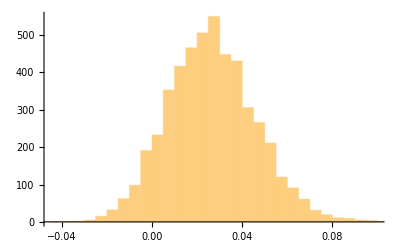

```mathematica
CCmatisto=Flatten[Table[Table[CC[st1,st2],{st2,st1+1,nstocks}],{st1,1,nstocks}],1];
Histogram[CCmatisto]
```

{-0.0413187,0.0264809,0.138975}

4950

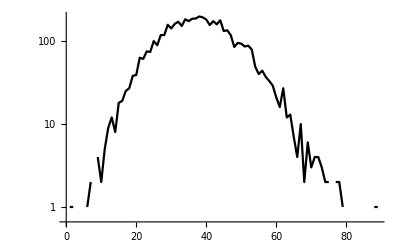

```mathematica
{Min[CCmatisto],Mean[CCmatisto],Max[CCmatisto]}
Length[CCmatisto]
nbin =100;
step=(Max[CCmatisto]-Min[CCmatisto])/nbin//N;
grid=Table[Min[CCmatisto]+g*step,{g,0,nbin}];
histoCC=BinCounts[CCmatisto,{grid}];
CCisto=ListLogPlot[histoCC,Joined->True,PlotStyle->Black,PlotRange->All]
```

### bootstrap - all elements are shuffled

```mathematica
Clear[index]
(*genero iter random samples dalla distribuzione delle copie di bootstrap*)
DateList[]
 Do[Do[index[st]=Table[RandomInteger[{1,NN}],{n,1,NN}];
          replica[i,st]=Table[data[[index[st][[n]],st]],{n,1,NN}];,
          {st,1,nstocks}];
     Do[CCb[i,st1,st1]=1;
         Do[CCb[i,st1,st2]=Correlation[replica[i,st1],replica[i,st2]];
              CCb[i,st2,st1]=CCb[i,st1,st2];,
              {st2,st1+1,nstocks}],
        {st1,1,nstocks}],
    {i,1,iter}]
DateList[]
```

{2024,6,3,10,14,19.401593}

{2024,6,3,10,15,35.30866}

```mathematica
Do[Do[CCbootstrap[st1,st2]=Sum[CCb[i,st1,st2],{i,1,iter}]/iter;
         CCbootstrapvar[st1,st2]=Sum[(CCb[i,st1,st2]-CCbootstrap[st1,st2])^2,{i,1,iter}]/iter;
          CCbootstrapsd[st1,st2]=Sqrt[CCbootstrapvar[st1,st2]];,
              {st2,1,nstocks}],
        {st1,1,nstocks}]
```

```mathematica
CCbmat=Table[Table[CCbootstrap[st1,st2],{st2,1,nstocks}],{st1,1,nstocks}];
CCbmat//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Table[CCmat[[i]],{i,1,5}]//TableForm
```

1 | 0.0166255 | 0.00779223 | 0.0645654 | 0.0544416 | 0.032731 | 0.0933749 | 0.0377621 | 0.0273507 | 0.0420462 | 0.0751041 | 0.0362033 | 0.0447494 | 0.0615503 | 0.0471428 | 0.0367137 | 0.0354722 | 0.0537173 | 0.0298782 | 0.0205642 | 0.0240264 | 0.0375051 | 0.0508979 | 0.030627 | 0.0637182 | 0.0310409 | 0.0406838 | 0.0526905 | 0.0498028 | 0.0205014 | 0.0326666 | 0.0517382 | 0.048899 | 0.0134659 | 0.0491149 | 0.0387153 | 0.0295643 | 0.041786 | 0.0242064 | 0.0290136 | 0.055961 | 0.0438646 | 0.0267051 | 0.0815654 | 0.0318267 | 0.0345152 | 0.0600274 | 0.0588956 | 0.0149804 | -0.0114398 | 0.0333768 | -0.00434774 | 0.00492653 | 0.0351036 | 0.0481351 | 0.0354389 | 0.0745177 | 0.0472334 | -0.00400398 | 0.0157591 | 0.0242765 | 0.0725047 | 0.0184247 | 0.0431207 | 0.0394856 | 0.0424013 | 0.0511274 | 0.0685839 | 0.0125245 | 0.00633337 | 0.0452085 | 0.00328186 | 0.0391413 | 0.0405237 | 0.0402656 | -0.00687425 | 0.00791835 | 0.0508823 | 0.0538783 | 0.0284832 | 0.0476879 | 0.0329155 | 0.0226228 | 0.0105557 | 0.0257379 | 0.0252142 | 0.0392813 | 0.0263633 | 0.0216241 | 0.0196367 | 0.0530004 | 0.0204482 | 0.0586849 | -0.0212698 | 0.00712405 | 0.00256688 | -0.0190311 | 0.0424924 | -0.00639595 | 0.027488
0.0166255 | 1 | 0.00990031 | 0.0504668 | 0.0522502 | 0.0369905 | 0.0463658 | 0.0215297 | 0.0307415 | 0.0126518 | 0.0700447 | 0.0382648 | 0.0236612 | 0.0235256 | 0.0205698 | 0.0542494 | 0.0203382 | 0.00633687 | 0.0458635 | 0.019241 | 0.00181299 | 0.0406515 | 0.0545265 | 0.0463285 | 0.0229789 | 0.0334965 | 0.0875902 | 0.0408313 | 0.0399403 | 0.0404897 | 0.0260122 | 0.0408169 | 0.0558377 | 0.017923 | 0.0445872 | 0.0326837 | 0.0252601 | 0.00780952 | 0.0262178 | 0.0272931 | 0.0251434 | 0.0619169 | 0.0262355 | 0.0335029 | 0.0316347 | 0.0620097 | 0.0429346 | 0.060464 | 0.0111274 | 0.00130391 | 0.00737222 | 0.0169258 | -0.00230724 | 0.0157369 | 0.0216117 | 0.0141493 | 0.0193605 | 0.0240769 | 0.00482346 | 0.0375404 | 0.0183777 | 0.0335327 | 0.0114841 | 0.0295597 | 0.0251148 | 0.0340678 | 0.037305 | 0.0654626 | 0.00600549 | 0.00940831 | 0.0220345 | 0.00818215 | 0.0380082 | 0.0212039 | 0.0410639 | 0.00606054 | 0.0428445 | 0.0330252 | 0.0282328 | 0.0539795 | 0.0488003 | 0.0338762 | 0.0526533 | 0.0126944 | 0.0245893 | 0.0284285 | 0.0389899 | 0.0152477 | 0.00991585 | 0.000750349 | 0.0192243 | 0.0409646 | 0.0113558 | 0.0293229 | 0.0154321 | 0.0176798 | 0.010413 | 0.0162509 | -0.00232849 | 0.0418358
0.00779223 | 0.00990031 | 1 | 0.0225172 | 0.0271549 | 0.00597458 | 0.0207331 | 0.0342008 | 0.0126099 | -0.000110602 | 0.0183432 | -0.00898141 | 0.0360564 | 0.018552 | 0.0475109 | 0.0294892 | 0.0291745 | 0.0284857 | 0.0233631 | 0.0285159 | 0.0296688 | 0.0034494 | 0.0262374 | 0.0008759 | 0.00051909 | -0.00603344 | -0.0080071 | 0.0104067 | 0.0181425 | 0.0406343 | -0.0132501 | 0.0330143 | 0.00647336 | 0.0239601 | 0.0110115 | 0.00400228 | 0.0437422 | -0.0129494 | -0.0153976 | 0.0298429 | 0.0277146 | 0.00647405 | 0.0276376 | 0.0133088 | 0.0194097 | 0.022885 | 0.00803161 | 0.0303605 | 0.00520794 | 0.00968172 | 0.015209 | 0.0311518 | 0.00308388 | 0.0403946 | -0.00803046 | 0.0128091 | 0.00527692 | 0.0454192 | -0.0305056 | 0.0014818 | 0.0189667 | -0.00449174 | 0.00337289 | 0.0141578 | -0.0157793 | 0.0220692 | 0.00686443 | 0.0113567 | 0.00889482 | 0.0259906 | 0.00959352 | 0.0258146 | 0.0257829 | 0.000917369 | 0.0134946 | 0.00744785 | -0.00914579 | -0.0043412 | 0.018506 | -0.0301623 | 0.0188498 | -0.00412838 | 0.0286469 | -0.025208 | 0.0191965 | -0.000175819 | 0.0133701 | 0.0272728 | 0.00814006 | 0.00264504 | 0.00155176 | -0.0063156 | 0.0152235 | -0.0130915 | 0.0154386 | 0.00450793 | 0.0180092 | -0.00718334 | 0.00169359 | -0.025197
0.0645654 | 0.0504668 | 0.0225172 | 1 | 0.0530319 | 0.0280721 | 0.0673845 | 0.0194299 | 0.0126922 | 0.0589385 | 0.0792121 | 0.0475068 | 0.0600937 | 0.0250038 | 0.011406 | 0.0452263 | 0.0470376 | 0.0177391 | 0.0236412 | 0.0046489 | 0.0210258 | 0.0344892 | 0.044122 | 0.0820177 | 0.0474155 | 0.0275597 | 0.0468015 | 0.0377052 | 0.0600511 | 0.0488519 | 0.021924 | 0.0331316 | 0.0554904 | 0.0109838 | 0.0368769 | 0.0625012 | 0.0640168 | 0.0340869 | 0.0403699 | 0.0349976 | 0.0461638 | 0.0583369 | 0.0192771 | 0.0885802 | 0.0488452 | 0.0413712 | 0.0142445 | 0.0160279 | -0.0125483 | 0.0166815 | 0.00827471 | 0.00212737 | 0.0365362 | 0.0261395 | 0.0445719 | 0.0570536 | 0.0579793 | 0.0580739 | 0.0150667 | 0.0253687 | 0.0343833 | 0.0321275 | 0.00753986 | 0.020814 | 0.0231323 | 0.02379 | 0.0701724 | 0.0662807 | 0.0142106 | 0.0170702 | 0.0428001 | 0.0199576 | 0.0379582 | 0.0313764 | 0.0494861 | 0.0325237 | 0.0339691 | 0.016509 | 0.0435835 | 0.0415187 | 0.0463594 | 0.0225189 | 0.0739059 | 0.0382312 | 0.0510864 | 0.0332816 | 0.0143082 | 0.0337671 | 0.0185549 | 0.0411841 | 0.052746 | 0.0290571 | 0.0458561 | -0.00716814 | 0.0275682 | 0.00686703 | 0.0170982 | 0.0439165 | 0.0599098 | 0.0320667
0.0544416 | 0.0522502 | 0.0271549 | 0.0530319 | 1 | 0.0343249 | 0.0694915 | 0.0390607 | 0.0539827 | 0.0589895 | 0.058896 | 0.0318716 | 0.0478752 | 0.0484731 | 0.0248112 | 0.0425916 | 0.0616229 | 0.0445605 | 0.0458745 | 0.0229265 | 0.0662342 | 0.0495597 | 0.0445814 | 0.0705264 | 0.0262729 | 0.0141604 | 0.0788191 | 0.0751516 | 0.0553781 | 0.0699763 | 0.0381027 | 0.0342654 | 0.0628348 | 0.0201297 | 0.0626539 | 0.0519062 | 0.0167387 | 0.0466296 | 0.0229245 | 0.0523952 | 0.0375398 | 0.060802 | 0.0437884 | 0.085162 | 0.055319 | 0.0643262 | 0.0259109 | 0.0536926 | -0.00957886 | -0.00875494 | 0.0505743 | -0.0000999378 | 0.0239729 | 0.03738 | 0.030543 | 0.0782425 | 0.0351332 | 0.00978236 | 0.029917 | 0.0386616 | 0.0615835 | 0.0700295 | 0.0416848 | 0.0392062 | 0.0159291 | 0.0302752 | 0.0488443 | 0.077678 | 0.0346506 | 0.0519978 | 0.0257885 | 0.0283407 | 0.079676 | 0.0240309 | 0.0842657 | 0.016129 | 0.03956 | 0.0282525 | 0.0529032 | 0.0235185 | 0.0624365 | 0.0301146 | 0.0990468 | 0.0526616 | 0.0368054 | 0.0582397 | 0.0404581 | 0.0456738 | 0.0153497 | 0.0396027 | 0.0636305 | 0.0471871 | 0.0384394 | 0.0208519 | -0.0021633 | 0.0264204 | 0.00630996 | 0.0173574 | 0.0316872 | 0.0431192

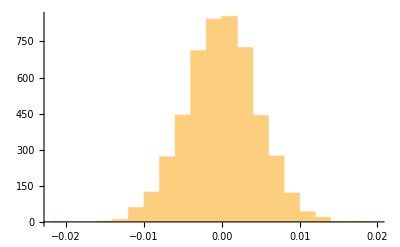

```mathematica
CCbmatisto=Flatten[Table[Table[CCbootstrap[st1,st2],{st2,st1+1,nstocks}],{st1,1,nstocks}],1];
Histogram[CCbmatisto]
```

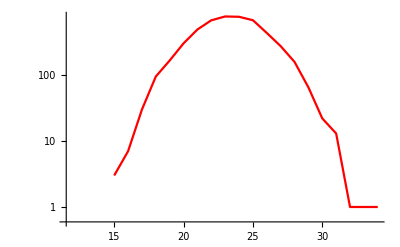

```mathematica
histoCCb=BinCounts[CCbmatisto,{grid}];
CCbisto=ListLogPlot[histoCCb,Joined->True,PlotStyle->Red,PlotRange->All]
```

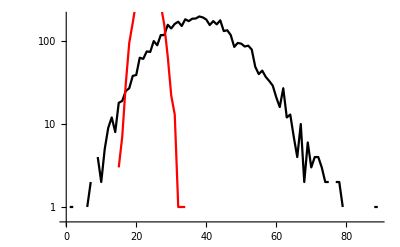

```mathematica
Show[CCisto,CCbisto]
```

```mathematica
Flatten[Table[Table[{st1,st2,CC[st1,st2],
                                              " ",CCbootstrap[st1,st2],CCbootstrapsd[st1,st2],
                                              " ",Abs[CC[st1,st2]-CCbootstrap[st1,st2]]-CCbootstrapsd[st1,st2]},{st2,st1+1,5}],{st1,1,5}],1]//TableForm
```

1 | 2 | 0.0166255 |   | -0.00330189 | 0.0133724 |   | 0.00655502
1 | 3 | 0.00779223 |   | -0.00524349 | 0.0111856 |   | 0.00185012
1 | 4 | 0.0645654 |   | 0.00365542 | 0.011195 |   | 0.0497149
1 | 5 | 0.0544416 |   | 0.00355409 | 0.0131377 |   | 0.0377498
2 | 3 | 0.00990031 |   | 0.00359779 | 0.00959068 |   | -0.00328816
2 | 4 | 0.0504668 |   | -0.00226442 | 0.0147271 |   | 0.0380041
2 | 5 | 0.0522502 |   | 0.000252189 | 0.0153 |   | 0.036698
3 | 4 | 0.0225172 |   | -0.0043922 | 0.0116009 |   | 0.0153085
3 | 5 | 0.0271549 |   | 0.000519036 | 0.0144069 |   | 0.012229
4 | 5 | 0.0530319 |   | -0.00142237 | 0.0126071 |   | 0.0418471

### bootstrap - rows are shuffled

```mathematica
(*genero iter random samples dalla distribuzione delle copie di bootstrap*)
 DateList[]
Do[indexR=Table[RandomInteger[{1,NN}],{n,1,NN}];
     Do[replica[i,st]=Table[data[[indexR[[n]],st]],{n,1,NN}];,
          {st,1,nstocks}];
     Do[CCb[i,st1,st1]=1;
         Do[CCb[i,st1,st2]=Correlation[replica[i,st1],replica[i,st2]];
              CCb[i,st2,st1]=CCb[i,st1,st2];,
              {st2,st1+1,nstocks}],
        {st1,1,nstocks}],
    {i,1,iter}]
DateList[]
```

{2024,6,3,10,21,52.006025}

{2024,6,3,10,22,29.853005}

```mathematica
Do[Do[CCbootstrapR[st1,st2]=Sum[CCb[i,st1,st2],{i,1,iter}]/iter;
         CCbootstrapRvar[st1,st2]=Sum[(CCb[i,st1,st2]-CCbootstrapR[st1,st2])^2,{i,1,iter}]/iter;
          CCbootstrapRsd[st1,st2]=Sqrt[CCbootstrapRvar[st1,st2]];,
              {st2,1,nstocks}],
        {st1,1,nstocks}]
```

```mathematica
CCbRmat=Table[Table[CCbootstrapR[st1,st2],{st2,1,nstocks}],{st1,1,nstocks}];
CCbRmat//MatrixForm
```

(1 | 0.0139396 | 0.0105297 | 0.0605562 | 0.0556777 | 0.0294305 | 0.0894313 | 0.0304919 | 0.0358072 | 0.0444249 | 0.0732939 | 0.050029 | 0.0475373 | 0.0653025 | 0.0452705 | 0.028268 | 0.037836 | 0.0482471 | 0.0337093 | 0.0260869 | 0.0163627 | 0.0420968 | 0.0486535 | 0.0252666 | 0.0595725 | 0.0412785 | 0.0437481 | 0.0479903 | 0.0515236 | 0.0207044 | 0.0248136 | 0.0509523 | 0.0409197 | 0.0138752 | 0.0521108 | 0.0489107 | 0.037096 | 0.0400583 | 0.0267634 | 0.028604 | 0.052871 | 0.0488848 | 0.0302271 | 0.0743087 | 0.0322984 | 0.0349696 | 0.0635966 | 0.052253 | 0.0154114 | -0.00162817 | 0.0334039 | -0.00775654 | 0.00334987 | 0.0448062 | 0.0464189 | 0.0413145 | 0.0706915 | 0.0494796 | -0.00705374 | 0.021829 | 0.0297256 | 0.0664744 | 0.0209143 | 0.0482304 | 0.0358156 | 0.0447904 | 0.0372002 | 0.0628478 | 0.0110578 | 0.00305653 | 0.0411117 | 0.00196636 | 0.0487704 | 0.0387162 | 0.0417204 | -0.012181 | 0.0043444 | 0.0361903 | 0.0572205 | 0.0344244 | 0.0475309 | 0.0315864 | 0.0296234 | 0.0185065 | 0.0278385 | 0.0208788 | 0.0325239 | 0.0368838 | 0.0164418 | 0.0184816 | 0.0540734 | 0.0157688 | 0.0634629 | -0.0215916 | 0.000506865 | -0.000679193 | -0.0134618 | 0.0468496 | -0.0068274 | 0.0342663
0.0139396 | 1 | 0.00601711 | 0.051539 | 0.0539836 | 0.0376985 | 0.0439763 | 0.0299705 | 0.0300981 | 0.0144813 | 0.0727705 | 0.04062 | 0.0269213 | 0.0132102 | 0.0119767 | 0.0589292 | 0.0247508 | 0.00521523 | 0.0537618 | 0.0174317 | 0.00400655 | 0.0422337 | 0.0530292 | 0.0495091 | 0.0295822 | 0.0332359 | 0.0917665 | 0.048751 | 0.0448793 | 0.0484784 | 0.0364145 | 0.0390032 | 0.0639824 | 0.0190652 | 0.0454427 | 0.0307163 | 0.0198848 | 0.000955107 | 0.0202741 | 0.0242749 | 0.0248235 | 0.0639941 | 0.0264937 | 0.0341456 | 0.0308532 | 0.0599605 | 0.0484067 | 0.0617161 | 0.00539724 | -0.00315162 | 0.0143381 | 0.016341 | 0.0045658 | 0.0209942 | 0.01634 | 0.0233258 | 0.0197182 | 0.0254143 | 0.00629536 | 0.0447995 | 0.0172693 | 0.0399525 | 0.0144127 | 0.0270046 | 0.0291108 | 0.0346383 | 0.0420426 | 0.0670478 | 0.00525191 | 0.00980502 | 0.0219607 | 0.00737546 | 0.0370767 | 0.0186591 | 0.0453998 | 0.00877337 | 0.0492308 | 0.0462298 | 0.0316795 | 0.0597307 | 0.0491149 | 0.0366077 | 0.0595 | 0.0158886 | 0.0293086 | 0.0343692 | 0.0346582 | 0.0133177 | 0.00522218 | -0.00143144 | 0.0264369 | 0.0561905 | 0.0108811 | 0.0384538 | 0.0224816 | 0.0135306 | 0.0140659 | 0.0156249 | -0.00474407 | 0.0345676
0.0105297 | 0.00601711 | 1 | 0.0218867 | 0.0361112 | 0.0110366 | 0.0144276 | 0.0375615 | 0.00719502 | -0.0056502 | 0.0151202 | -0.00698839 | 0.0367052 | 0.0209331 | 0.0506859 | 0.0330788 | 0.0344395 | 0.0277263 | 0.0225413 | 0.0311891 | 0.0314064 | 0.00383221 | 0.0281166 | 0.00152138 | -0.00339104 | -0.00845526 | -0.00358148 | 0.005363 | 0.0225667 | 0.039623 | -0.0158472 | 0.0258008 | 0.00608793 | 0.0214522 | 0.0094477 | 0.00826101 | 0.0420339 | -0.0119807 | -0.0182933 | 0.0242912 | 0.032175 | 0.0136997 | 0.0317979 | 0.0116767 | 0.0186879 | 0.0266991 | 0.00592522 | 0.0261111 | -0.0000622736 | 0.00940513 | 0.0179032 | 0.0283793 | -0.00288614 | 0.0467155 | -0.00791416 | 0.0125626 | 0.0036385 | 0.0447019 | -0.0242086 | 0.00580839 | 0.020288 | -0.000997375 | 0.00436912 | 0.0133007 | -0.0186556 | 0.0234033 | 0.000758217 | 0.0131212 | 0.00369098 | 0.0244796 | 0.00774898 | 0.0212243 | 0.030521 | 0.0031128 | 0.0126495 | 0.00762889 | -0.00655367 | -0.00524491 | 0.0304909 | -0.0313314 | 0.0168141 | 0.00232563 | 0.0280361 | -0.0258298 | 0.0151648 | -0.00312976 | 0.0219455 | 0.0215841 | 0.00903607 | 0.00194683 | 0.00679637 | -0.00985208 | 0.0106446 | -0.0180739 | 0.015953 | 0.00622039 | 0.0202167 | -0.0025286 | 0.00213976 | -0.0183408
0.0605562 | 0.051539 | 0.0218867 | 1 | 0.0590611 | 0.0305374 | 0.0713954 | 0.0223027 | 0.0111058 | 0.0578292 | 0.0870768 | 0.0530684 | 0.0659603 | 0.0327575 | 0.00751047 | 0.0452306 | 0.0470464 | 0.0105997 | 0.0223002 | 0.00526028 | 0.0228235 | 0.0324874 | 0.0501967 | 0.0786799 | 0.0454249 | 0.0268149 | 0.0482495 | 0.0320183 | 0.0632618 | 0.0490263 | 0.018117 | 0.0353053 | 0.0516635 | 0.0152697 | 0.039297 | 0.0640358 | 0.0601353 | 0.0273984 | 0.051093 | 0.0338452 | 0.0501046 | 0.052974 | 0.0306512 | 0.0869673 | 0.0451057 | 0.0460588 | 0.0155775 | 0.0155598 | -0.0156977 | 0.012019 | 0.00760853 | -0.00137489 | 0.0423974 | 0.0245109 | 0.0429397 | 0.07183 | 0.0562645 | 0.0496592 | 0.0167938 | 0.0224049 | 0.0215695 | 0.0338873 | 0.00496915 | 0.0156862 | 0.0253787 | 0.0198659 | 0.0684829 | 0.0629147 | 0.0166062 | 0.013871 | 0.0352406 | 0.0256913 | 0.0445772 | 0.0308391 | 0.0475737 | 0.0354255 | 0.0384045 | 0.00792538 | 0.0349151 | 0.0384814 | 0.0563405 | 0.0104759 | 0.0820638 | 0.0418729 | 0.0544577 | 0.0364815 | 0.00370606 | 0.0379448 | 0.016739 | 0.0366507 | 0.0489984 | 0.0354299 | 0.0487756 | 0.000362116 | 0.0302743 | 0.00662981 | 0.0112387 | 0.0479931 | 0.0548723 | 0.0315769
0.0556777 | 0.0539836 | 0.0361112 | 0.0590611 | 1 | 0.0393919 | 0.0706032 | 0.0394838 | 0.056328 | 0.048448 | 0.0633923 | 0.0351353 | 0.0387685 | 0.0539614 | 0.0275866 | 0.0396965 | 0.0690085 | 0.0390862 | 0.0542313 | 0.0216695 | 0.0626765 | 0.0489734 | 0.0361227 | 0.0727667 | 0.0241944 | 0.0191738 | 0.0772104 | 0.0623142 | 0.0539854 | 0.0725312 | 0.0377425 | 0.033323 | 0.0629281 | 0.0211471 | 0.0672723 | 0.0510284 | 0.0154824 | 0.0488267 | 0.028984 | 0.0472252 | 0.037051 | 0.0549755 | 0.0480631 | 0.0841708 | 0.054894 | 0.0672759 | 0.0236106 | 0.0503042 | -0.0139931 | -0.0124996 | 0.0592182 | -0.000340667 | 0.0189815 | 0.041395 | 0.0300893 | 0.0747928 | 0.0238692 | 0.0112811 | 0.0350508 | 0.0329739 | 0.0635784 | 0.0650306 | 0.0404388 | 0.0432647 | 0.0193604 | 0.0225735 | 0.0508603 | 0.0786269 | 0.0337498 | 0.0569856 | 0.0270762 | 0.02355 | 0.0770294 | 0.0169634 | 0.0805224 | 0.0168432 | 0.0360277 | 0.0240863 | 0.043011 | 0.018418 | 0.0653463 | 0.0280202 | 0.0992613 | 0.0498352 | 0.0452884 | 0.0617075 | 0.0332427 | 0.0556028 | 0.0121233 | 0.0374217 | 0.063 | 0.0496863 | 0.0432356 | 0.0236363 | -0.000617669 | 0.0263585 | 0.0105338 | 0.0301937 | 0.0318229 | 0.047444
0.0294305 | 0.0376985 | 0.0110366 | 0.0305374 | 0.0393919 | 1 | 0.053969 | 0.0105878 | 0.0448517 | 0.024138 | 0.036447 | 0.0032208 | 0.016945 | 0.0367398 | 0.020807 | 0.0232808 | 0.0303143 | 0.00104338 | 0.0338842 | 0.0192782 | 0.02773 | 0.010872 | 0.0121111 | 0.0289828 | 0.0157014 | 0.000762297 | 0.0219236 | 0.0120436 | 0.0102895 | 0.0144825 | 0.0346109 | 0.0213106 | 0.0207021 | -0.0207834 | 0.0141602 | -0.0131045 | 0.0151237 | 0.0344525 | 0.0139297 | 0.0275543 | 0.0115814 | 0.0157646 | 0.00836827 | 0.0177396 | 0.058823 | -0.000858317 | -0.00483608 | 0.00295687 | -0.0208681 | -0.0030129 | 0.0197276 | 0.00500731 | 0.00882836 | 0.0018123 | 0.0382061 | 0.0222798 | 0.00635721 | 0.0213581 | -0.0233721 | 0.0206716 | 0.011041 | 0.0338632 | -0.00892943 | 0.0245816 | 0.00546774 | 0.0364265 | 0.0240286 | 0.0301211 | -0.0119392 | 0.0346383 | -0.0113042 | 0.00556585 | 0.00365838 | 0.0204942 | 0.0130015 | 0.0216755 | 0.0021045 | 0.0246247 | 0.00348668 | 0.0228692 | 0.0367725 | 0.0132718 | 0.0128443 | 0.0369403 | 0.0245672 | 0.015217 | 0.0184162 | 0.00991353 | -0.0024531 | 0.0110848 | 0.0291295 | 0.00191043 | 0.0403919 | -0.0185017 | 0.0253369 | -0.0129918 | 0.024502 | 0.036772 | 0.0165167 | 0.0172513
0.0894313 | 0.0439763 | 0.0144276 | 0.0713954 | 0.0706032 | 0.053969 | 1 | 0.0312142 | 0.0593106 | 0.0557373 | 0.0860949 | 0.0394281 | 0.0393767 | 0.0404922 | 0.0358478 | 0.0261184 | 0.0318744 | 0.0053448 | 0.0762959 | 0.0191529 | 0.0489337 | 0.0599218 | 0.0266485 | 0.074789 | 0.0440099 | -0.01706 | 0.0705277 | 0.0439889 | 0.0487268 | 0.0520426 | 0.0195826 | 0.0317778 | 0.0496475 | 0.0400913 | 0.0232733 | 0.0570671 | 0.00256899 | 0.0363079 | 0.0536952 | 0.0576669 | 0.0397475 | 0.0416131 | 0.0121988 | 0.049637 | 0.0480618 | 0.0595584 | 0.0359013 | 0.0407295 | 0.00238273 | 0.0317837 | 0.00917742 | 0.0094304 | -0.00525357 | 0.00422439 | 0.0579251 | 0.0328918 | 0.00722454 | 0.0565278 | -0.00732064 | 0.0222227 | 0.00360234 | 0.0541737 | 0.0346592 | 0.0345588 | 0.00665401 | 0.015505 | 0.0518574 | 0.0858293 | -0.00263307 | 0.056153 | 0.0410252 | 0.0108514 | 0.0277104 | 0.0410954 | 0.0524557 | 0.0112161 | 0.0341307 | 0.0477306 | 0.0445443 | 0.0654865 | 0.0429903 | 0.0499615 | 0.0473327 | -0.00379022 | 0.0424252 | 0.044433 | 0.010762 | 0.0319738 | 0.0336202 | 0.0325466 | 0.0487695 | 0.0382672 | 0.0351817 | 0.0193005 | -0.00846971 | 0.000756634 | 0.0139983 | 0.0134482 | 0.0318692 | 0.00257297
0.0304919 | 0.0299705 | 0.0375615 | 0.0223027 | 0.0394838 | 0.0105878 | 0.0312142 | 1 | 0.055239 | 0.0320169 | 0.0730072 | 0.0523171 | 0.0414892 | 0.0290673 | 0.0345885 | 0.061248 | 0.0339897 | 0.0280741 | 0.05283 | 0.0425562 | 0.031193 | 0.0322879 | 0.0550401 | 0.0412931 | 0.0541606 | 0.0220387 | 0.0505718 | 0.0634493 | 0.0426448 | 0.0308508 | 0.0407087 | 0.0267471 | 0.0581745 | 0.00549235 | 0.0337187 | 0.0438316 | 0.0104102 | 0.0162471 | 0.0397776 | 0.04537 | 0.0391627 | 0.0696126 | -0.00126318 | 0.0678053 | 0.0333192 | 0.0492848 | 0.0259177 | 0.0278361 | 0.0451031 | -0.00238139 | 0.0186509 | -0.000562526 | 0.0088843 | 0.0312085 | 0.0306581 | 0.0495257 | 0.0400834 | 0.0651584 | -0.0060837 | 0.0515818 | 0.0272213 | 0.0174955 | 0.0445282 | 0.0439206 | -0.0073228 | 0.0535984 | 0.0379272 | 0.0383665 | 0.040572 | 0.0235894 | 0.0708218 | 0.0141071 | 0.00901128 | 0.0259599 | 0.0575669 | 0.00929666 | 0.00614207 | 0.0297141 | 0.0481733 | 0.0555808 | 0.0418107 | 0.0162817 | 0.0233168 | 0.00221706 | 0.0102934 | 0.0396033 | 0.0279916 | 0.0177444 | 0.0266059 | 0.0145997 | 0.0311604 | 0.0522678 | 0.0704334 | -0.000195248 | 0.0335873 | 0.0171029 | 0.02813 | 0.0592299 | 0.0219537 | 0.0346684
0.0358072 | 0.0300981 | 0.00719502 | 0.0111058 | 0.056328 | 0.0448517 | 0.0593106 | 0.055239 | 1 | 0.0205038 | 0.03252 | 0.0256818 | 0.0290522 | 0.0474674 | 0.0425759 | 0.0349851 | 0.0154187 | 0.031194 | 0.0287942 | 0.0254099 | 0.0192311 | 0.0261359 | 0.0387139 | 0.0178087 | 0.0256929 | 0.0425463 | 0.0712455 | 0.0135225 | 0.0206289 | 0.0444039 | 0.0188873 | 0.0161038 | 0.0381221 | 0.0212165 | 0.0370638 | 0.0266032 | 0.01759 | 0.0248654 | 0.0560359 | 0.0363478 | 0.026105 | 0.045157 | 0.0408631 | 0.039035 | 0.0393306 | 0.0268087 | 0.0138755 | 0.0417021 | 0.0250817 | -0.00545391 | -0.00714834 | 0.0178401 | 0.0161763 | -0.00415718 | 0.0287936 | -0.00962432 | 0.00893425 | 0.00672386 | 0.00394445 | 0.021251 | 0.0148082 | 0.00809105 | 0.0313982 | 0.0263386 | 0.0275406 | -0.00155255 | 0.0167885 | 0.0342155 | 0.00822934 | 0.0156711 | 0.0145336 | 0.0195135 | 0.0134117 | 0.0274532 | 0.0527634 | 0.0191494 | 0.0330437 | 0.00726736 | 0.051851 | 0.0163668 | 0.0174696 | 0.0398472 | 0.0159291 | 0.00457796 | 0.030112 | 0.0449016 | 0.0170692 | 0.00254235 | -0.000557472 | 0.0220445 | 0.027602 | 0.0389921 | 0.00439939 | 0.0170482 | 0.0365168 | -0.00292169 | 0.0136536 | 0.0234998 | 0.0371819 | 0.00896629
0.0444249 | 0.0144813 | -0.0056502 | 0.0578292 | 0.048448 | 0.024138 | 0.0557373 | 0.0320169 | 0.0205038 | 1 | 0.0757785 | 0.0338772 | 0.0328766 | 0.0168861 | 0.00431398 | 0.0522025 | 0.0231114 | 0.00974492 | 0.0203395 | 0.00738144 | 0.00962813 | 0.03429 | 0.0269801 | 0.0447453 | 0.0559622 | -0.00300655 | 0.0423318 | -0.0025023 | 0.0411343 | 0.024015 | 0.0464479 | 0.0340888 | 0.0405858 | 0.0319173 | 0.0461989 | 0.0632798 | 0.0460268 | 0.011915 | 0.0191596 | 0.03263 | 0.0319662 | 0.0264825 | 0.0477328 | 0.0324059 | 0.0369206 | 0.0295419 | 0.0264265 | 0.0556793 | -0.00352789 | -0.012155 | 0.0368746 | 0.00516131 | 0.0284796 | 0.0417783 | 0.0394568 | 0.00655462 | 0.0236016 | 0.0283699 | 0.00231661 | 0.01107 | 0.0191646 | 0.0394294 | 0.0130241 | -0.00389627 | -0.0134877 | 0.0520385 | 0.0338825 | 0.0412093 | 0.00698904 | 0.0511662 | 0.0420671 | 0.0143171 | 0.00815878 | 0.0316546 | 0.0829984 | -0.000652662 | 0.0268318 | 0.00881577 | 0.0214216 | 0.0387929 | 0.0697292 | 0.0457994 | 0.0276017 | -0.0025606 | 0.0532118 | 0.005207 | 0.0418979 | 0.0609526 | 0.0445242 | 0.0169511 | 0.0270105 | 0.0326304 | 0.0254103 | 0.0281729 | 0.000479588 | 0.0275644 | 0.00686602 | 0.0242885 | 0.0299756 | 0.0139716
0.0732939 | 0.0727705 | 0.0151202 | 0.0870768 | 0.0633923 | 0.036447 | 0.0860949 | 0.0730072 | 0.03252 | 0.0757785 | 1 | 0.0547746 | 0.0427632 | 0.0529376 | 0.0211122 | 0.0958381 | 0.0614558 | 0.0258088 | 0.0247555 | 0.0234028 | 0.0680349 | 0.0607933 | 0.0574637 | 0.0658939 | 0.0468612 | 0.0297761 | 0.0706058 | 0.0475609 | 0.0451324 | 0.0543073 | 0.0511442 | 0.023225 | 0.101578 | 0.0199923 | 0.0694489 | 0.0757966 | 0.00221523 | 0.014991 | 0.0727024 | 0.0342425 | 0.0636015 | 0.0591228 | 0.0369599 | 0.0871337 | 0.0580951 | 0.0287421 | 0.0413706 | 0.0792052 | 0.00715172 | -0.0116064 | 0.0621192 | 0.0154456 | 0.0168807 | 0.0377063 | 0.0582335 | 0.0664893 | 0.0797749 | 0.0784463 | 0.0167415 | 0.0612324 | 0.010488 | 0.0421306 | 0.012326 | 0.0562211 | 0.0301189 | 0.0421795 | 0.0711064 | 0.0737982 | 0.0283235 | 0.0316117 | 0.0270249 | 0.0242811 | 0.0419964 | 0.0603422 | 0.103085 | 0.0243419 | 0.0553078 | 0.0231837 | 0.0263195 | 0.0293165 | 0.119675 | 0.0202771 | 0.0981175 | -0.0110708 | 0.0311381 | 0.0238579 | 0.0259227 | 0.0613051 | 0.023156 | 0.0506172 | 0.0606142 | 0.0636948 | 0.0973653 | 0.00965667 | 0.005219 | 0.0145626 | 0.00712057 | 0.0417739 | 0.0378651 | 0.0286435
0.050029 | 0.04062 | -0.00698839 | 0.0530684 | 0.0351353 | 0.0032208 | 0.0394281 | 0.0523171 | 0.0256818 | 0.0338772 | 0.0547746 | 1 | 0.0329076 | 0.0106314 | -0.0022816 | 0.0447349 | 0.0122306 | 0.0218651 | 0.040046 | 0.0075449 | 0.0197588 | 0.0365077 | 0.0511749 | 0.0539518 | 0.0331446 | 0.0176179 | 0.0153246 | 0.0318988 | 0.0282744 | 0.0406983 | 0.0217409 | 0.0161208 | 0.066243 | 0.0139491 | 0.00612096 | 0.0341369 | -0.00207823 | 0.0115951 | 0.0297592 | 0.0274145 | 0.046381 | 0.0124511 | 0.0111187 | 0.0426176 | 0.0348996 | 0.0369699 | 0.0103772 | 0.0410249 | 0.0149366 | 0.00568293 | 0.0341413 | -0.00760176 | 0.0388828 | 0.0313309 | 0.00172639 | 0.0440462 | 0.0411364 | 0.0314082 | 0.0192963 | 0.0307882 | -0.00578831 | 0.0362788 | 0.00193753 | 0.0432795 | 0.0367606 | 0.0574853 | 0.0335805 | 0.058311 | 0.002185 | 0.0446366 | 0.0241936 | 0.030456 | 0.0371244 | 0.027263 | 0.0387824 | 0.0304384 | 0.0623594 | 0.0562456 | 0.0299441 | 0.0522079 | 0.0388459 | 0.0334311 | 0.0515185 | 0.0161963 | 0.02566 | -0.00892712 | 0.010834 | 0.015624 | 0.0266724 | 0.0315175 | 0.00234731 | 0.0237191 | 0.0310494 | -0.00252596 | 0.00717505 | 0.043765 | -0.00841326 | 0.015014 | 0.0240928 | 0.0374826
0.0475373 | 0.0269213 | 0.0367052 | 0.0659603 | 0.0387685 | 0.016945 | 0.0393767 | 0.0414892 | 0.0290522 | 0.0328766 | 0.0427632 | 0.0329076 | 1 | 0.0439481 | 0.0192702 | 0.0672399 | 0.0570056 | 0.027276 | 0.0459046 | 0.0479489 | 0.0284439 | 0.0542704 | 0.0490617 | 0.0401429 | 0.0178828 | 0.00642738 | 0.0864223 | 0.0466251 | 0.0371205 | 0.0183283 | 0.0422022 | 0.056641 | 0.127471 | 0.0118162 | 0.047836 | 0.0410245 | 0.0359931 | 0.00823311 | 0.0232494 | 0.0325039 | 0.0459879 | 0.0346866 | 0.0199711 | 0.0598177 | 0.000852012 | 0.0426809 | 0.0148127 | 0.0228342 | 0.0223319 | 0.0115871 | 0.00576682 | -0.00768877 | 0.0105928 | 0.0230007 | -0.00132597 | 0.0396087 | 0.0663203 | 0.034463 | 0.0217105 | 0.04544 | 0.0202345 | 0.0259661 | 0.0263942 | 0.02534 | 0.0367059 | 0.0525399 | 0.0753574 | 0.0555172 | 0.00393829 | 0.037723 | 0.0144682 | 0.0230508 | 0.00985359 | 0.0244175 | 0.0709941 | 0.0271307 | 0.0390539 | 0.0289478 | 0.0280248 | 0.0469227 | 0.0590691 | 0.0187403 | 0.0339467 | 0.00928198 | 0.0255518 | 0.0511657 | 0.0190537 | 0.0394684 | -0.00555812 | 0.0236551 | 0.021092 | 0.0369578 | 0.0376587 | -0.0104531 | 0.0186386 | 0.0416789 | 0.00401278 | -0.00105975 | 0.0405294 | 0.0134724
0.0653025 | 0.0132102 | 0.0209331 | 0.0327575 | 0.0539614 | 0.0367398 | 0.0404922 | 0.0290673 | 0.0474674 | 0.0168861 | 0.0529376 | 0.0106314 | 0.0439481 | 1 | 0.0361576 | 0.0179381 | 0.037306 | 0.0356578 | 0.0397097 | 0.00725921 | 0.0468639 | 0.0480577 | 0.0257078 | 0.0271899 | 0.0336669 | 0.046757 | 0.0551801 | 0.0425565 | 0.0548692 | 0.0166067 | 0.0166628 | 0.0400498 | 0.054696 | 0.0018111 | 0.0417229 | 0.0225666 | 0.0202959 | 0.0123815 | 0.0421788 | 0.0128916 | 0.0242183 | 0.0121813 | 0.0109907 | 0.0263702 | 0.0152606 | 0.044405 | 0.0188776 | 0.0195347 | 0.0123439 | 0.00711487 | 0.0321453 | -0.0216419 | -0.0115164 | 0.0234538 | 0.032196 | 0.0454197 | 0.0174167 | 0.0353792 | 0.0246852 | 0.0279348 | 0.00192027 | 0.0357065 | 0.0358636 | 0.0374332 | 0.00340708 | 0.00104187 | 0.024659 | 0.0475633 | -0.00978633 | -0.00298731 | 0.011141 | 0.0155468 | 0.0225384 | 0.0246637 | 0.0117858 | -0.00330497 | 0.00380098 | 0.0487224 | 0.039652 | 0.0258057 | 0.0123051 | -0.011255 | 0.0374442 | 0.0249459 | 0.00131263 | 0.0314656 | 0.0225968 | 0.0256884 | -0.0176451 | 0.0220681 | 0.0192956 | 0.0145875 | 0.044435 | 0.0255832 | -0.00122406 | -0.000509469 | 0.00123987 | 0.0194436 | 0.0173191 | 0.0217153
0.0452705 | 0.0119767 | 0.0506859 | 0.00751047 | 0.0275866 | 0.020807 | 0.0358478 | 0.0345885 | 0.0425759 | 0.00431398 | 0.0211122 | -0.0022816 | 0.0192702 | 0.0361576 | 1 | 0.00726511 | 0.00530088 | 0.0222925 | 0.0367533 | 0.0262636 | 0.0368217 | -0.00656885 | 0.032503 | 0.0462879 | -0.0000546495 | 0.022362 | 0.0315802 | 0.0202501 | 0.0137052 | 0.0241493 | -0.00216398 | 0.0359194 | 0.0386503 | 0.0201518 | 0.0467158 | 0.0433744 | 0.000281965 | 0.0392042 | 0.00227824 | 0.0138193 | 0.00658743 | 0.0290113 | 0.0134528 | 0.0535009 | 0.045116 | 0.0677722 | 0.040678 | 0.0284756 | 0.0290562 | 0.00227596 | -0.00149262 | 0.0366789 | 0.0291718 | -0.00626428 | 0.0102624 | 0.00229265 | 0.00418146 | -0.0096915 | -0.00775749 | 0.0183534 | 0.0110978 | 0.0530401 | -0.00289555 | 0.0184725 | 0.00806621 | 0.0327766 | 0.0523092 | 0.0103667 | 0.00144427 | 0.0258074 | -0.012244 | 0.0103666 | 0.019899 | -0.00686866 | 0.019144 | 0.0203085 | -0.0128655 | 0.00573654 | 0.0242325 | 0.0297697 | 0.00243111 | 0.0361384 | 0.0243468 | -0.0052115 | 0.037809 | 0.0221291 | -0.0140471 | 0.0272372 | 0.0130478 | 0.0373652 | 0.0303972 | 0.0259095 | 0.0298673 | -0.0026036 | 0.0155952 | 0.0108571 | 0.0235977 | 0.00834899 | -0.0040845 | 0.00389937
0.028268 | 0.0589292 | 0.0330788 | 0.0452306 | 0.0396965 | 0.0232808 | 0.0261184 | 0.061248 | 0.0349851 | 0.0522025 | 0.0958381 | 0.0447349 | 0.0672399 | 0.0179381 | 0.00726511 | 1 | 0.022957 | 0.0354699 | 0.061258 | 0.047602 | 0.0369538 | 0.0615162 | 0.0258125 | 0.0568991 | 0.0600753 | 0.00958233 | 0.071573 | 0.0619686 | 0.021433 | 0.0375003 | 0.0339748 | 0.0337223 | 0.064262 | 0.00932537 | 0.0265448 | 0.0493618 | 0.000227671 | 0.0458517 | 0.0375936 | 0.055324 | 0.0323358 | 0.0371643 | 0.0440421 | 0.0713046 | 0.0254928 | 0.0422537 | 0.0271784 | 0.0307416 | 0.0284101 | 0.0015217 | 0.00286491 | 0.0428481 | 0.0302995 | 0.0259145 | 0.0360103 | 0.0326893 | 0.0193785 | 0.0498718 | -0.0181319 | 0.0331497 | 0.0450909 | 0.0308108 | 0.0416905 | 0.0343191 | -0.00283418 | 0.0354458 | 0.0364783 | 0.0372505 | 0.0133385 | 0.00756517 | 0.0187775 | 0.0268462 | 0.0255702 | 0.0095076 | 0.0592262 | 0.0385981 | 0.0471397 | 0.0328811 | 0.0385037 | 0.0581913 | 0.052284 | 0.0276 | 0.052183 | 0.0250199 | 0.0160177 | 0.0237318 | 0.036651 | 0.0224103 | 0.0226192 | 0.0340689 | 0.0294099 | 0.0304101 | 0.023904 | 0.0126958 | 0.00715702 | 0.021311 | 0.0262725 | 0.0631252 | 0.0194012 | 0.0400139
0.037836 | 0.0247508 | 0.0344395 | 0.0470464 | 0.0690085 | 0.0303143 | 0.0318744 | 0.0339897 | 0.0154187 | 0.0231114 | 0.0614558 | 0.0122306 | 0.0570056 | 0.037306 | 0.00530088 | 0.022957 | 1 | 0.0109646 | 0.0537636 | 0.00912416 | 0.0484856 | 0.0363219 | 0.0358297 | 0.0265649 | 0.0273139 | 0.0248356 | 0.0390622 | 0.0437137 | 0.0357807 | 0.0284113 | 0.0250941 | 0.0357779 | 0.05242 | -0.000476723 | 0.023223 | 0.0234006 | 0.0317757 | 0.0350261 | 0.0326246 | 0.0322865 | 0.0275895 | 0.0362842 | 0.0181404 | 0.0555041 | 0.019973 | 0.00725885 | 0.0247966 | 0.0248292 | 0.0331613 | 0.00304234 | 0.0255063 | 0.0308398 | 0.0233725 | 0.0188586 | 0.0394866 | 0.0375749 | 0.0381809 | 0.0595426 | 0.0166409 | 0.0374714 | 0.0617001 | 0.0504452 | 0.0169778 | 0.0433901 | 0.0158771 | 0.0522106 | 0.0794871 | 0.0288976 | 0.0236126 | 0.0418512 | 0.0283498 | 0.00903373 | 0.0359415 | 0.00777606 | 0.0558667 | 0.00790089 | 0.0167536 | 0.0446873 | 0.0565522 | 0.0142715 | 0.0579203 | 0.0291626 | 0.0503591 | 0.0157666 | 0.0527326 | 0.0478567 | 0.00446168 | 0.0205567 | 0.0336278 | 0.0250657 | 0.00384999 | 0.0362303 | 0.0493243 | 0.0324797 | -0.00899 | -0.000778525 | 0.0312087 | 0.039827 | 0.0274674 | 0.021754
0.0482471 | 0.00521523 | 0.0277263 | 0.0105997 | 0.0390862 | 0.00104338 | 0.0053448 | 0.0280741 | 0.031194 | 0.00974492 | 0.0258088 | 0.0218651 | 0.027276 | 0.0356578 | 0.0222925 | 0.0354699 | 0.0109646 | 1 | 0.0127797 | 0.0166602 | 0.0214019 | 0.0158053 | 0.0323122 | 0.0186997 | 0.0470185 | 0.0151929 | 0.0135675 | 0.0358137 | 0.0260673 | -0.0058193 | 0.0122979 | 0.00347216 | 0.0313057 | 0.0244721 | 0.011892 | 0.0261046 | 0.0201898 | 0.0202765 | 0.0209854 | 0.0197329 | 0.0237889 | 0.0625178 | 0.00534582 | 0.0374634 | 0.0278907 | 0.00199175 | 0.00930374 | 0.0185814 | 0.0437264 | 0.0271484 | 0.0274875 | -0.0108853 | 0.00969211 | 0.00546312 | 0.0258156 | 0.0276192 | 0.0367699 | 0.0058524 | -0.00497587 | -0.011209 | 0.0295902 | 0.0409857 | -0.0145496 | 0.0328643 | 0.0149873 | 0.028615 | 0.028874 | 0.0196187 | -0.00527301 | 0.0156185 | 0.0227057 | 0.0245584 | 0.0282944 | 0.0208555 | -0.00535106 | -0.0042146 | 0.0101653 | 0.0360807 | 0.0177827 | 0.0223257 | 0.0273877 | 0.0172486 | 0.00333052 | 0.00950573 | -0.0131261 | 0.0313804 | 0.0260155 | 0.0266903 | 0.00460006 | 0.0359924 | 0.023223 | -0.00700414 | 0.0498246 | 0.000380926 | 0.00689483 | 0.054287 | -0.0109946 | 0.0100543 | 0.0091954 | 0.0253153
0.0337093 | 0.0537618 | 0.0225413 | 0.0223002 | 0.0542313 | 0.0338842 | 0.0762959 | 0.05283 | 0.0287942 | 0.0203395 | 0.0247555 | 0.040046 | 0.0459046 | 0.0397097 | 0.0367533 | 0.061258 | 0.0537636 | 0.0127797 | 1 | 0.0306171 | 0.0265147 | 0.0374053 | 0.0412164 | 0.0356893 | 0.0139707 | 0.00850319 | 0.0447248 | 0.0774905 | 0.0394986 | 0.0255482 | 0.0382777 | 0.0431071 | 0.0349688 | 0.00454293 | 0.0245772 | 0.0314465 | -0.0062674 | 0.0234349 | 0.031839 | 0.0148846 | 0.0164725 | 0.0354346 | 0.0452596 | 0.0571332 | 0.0413617 | 0.0541403 | 0.0402694 | 0.0623742 | 0.0223193 | -0.0118473 | 0.0121817 | 0.0376003 | 0.0148239 | 0.0526437 | 0.0327551 | 0.0255243 | 0.0350237 | 0.0262733 | -0.0106866 | 0.0147246 | 0.0110906 | 0.000555377 | 0.0366793 | 0.0331761 | 0.0106318 | 0.0496059 | 0.0304566 | 0.0667444 | -0.00895738 | 0.0265124 | 0.016088 | 0.0284697 | 0.0399752 | 0.00915988 | 0.0397867 | 0.014187 | 0.0580624 | 0.0111148 | 0.0271183 | 0.0399184 | 0.0359485 | 0.0367872 | 0.0480824 | 0.00249329 | 0.0361939 | 0.0409939 | 0.0210335 | 0.0342774 | 0.0105219 | 0.00644424 | 0.0148074 | 0.00957905 | 0.0598024 | 0.023767 | 0.0135659 | -0.00204727 | 0.0268658 | 0.017421 | -0.0324716 | 0.0474874
0.0260869 | 0.0174317 | 0.0311891 | 0.00526028 | 0.0216695 | 0.0192782 | 0.0191529 | 0.0425562 | 0.0254099 | 0.00738144 | 0.0234028 | 0.0075449 | 0.0479489 | 0.00725921 | 0.0262636 | 0.047602 | 0.00912416 | 0.0166602 | 0.0306171 | 1 | 0.0109482 | 0.0317012 | 0.0504076 | 0.0321805 | 0.0397422 | 0.0179683 | 0.0174032 | 0.0367831 | 0.0174304 | 0.0142215 | 0.026987 | 0.0113595 | -0.00237844 | 0.00910559 | 0.00449386 | 0.035703 | 0.00431819 | 0.0492188 | 0.0398105 | 0.013891 | 0.0223045 | 0.0125057 | 0.0120038 | 0.0137749 | 0.00914899 | 0.0302733 | 0.0265976 | 0.00311484 | 0.0413978 | 0.0150107 | -0.000973633 | 0.0155801 | 0.0283872 | -0.0012743 | 0.0243165 | 0.0323477 | 0.000970116 | 0.0194274 | 0.00541058 | 0.0393577 | 0.0211582 | 0.0201256 | 0.00565541 | 0.0258335 | 0.0302367 | 0.0159944 | 0.0426365 | 0.00672264 | -0.0147785 | 0.0209677 | 0.0156197 | 0.0275161 | 0.0125604 | 0.00160854 | 0.0364712 | 0.00581337 | 0.0451986 | 0.0102719 | 0.00902925 | 0.0296447 | 0.0210603 | -0.00140028 | 0.0225964 | 0.0159559 | 0.0144154 | 0.0178127 | 0.00500034 | 0.0246004 | 0.0378022 | -0.00958142 | 0.023831 | 0.00498163 | 0.0169856 | -0.000192332 | -0.0154614 | -0.0269969 | 0.0447095 | 0.0488465 | 0.0205063 | 0.0307687
0.0163627 | 0.00400655 | 0.0314064 | 0.0228235 | 0.0626765 | 0.02773 | 0.0489337 | 0.031193 | 0.0192311 | 0.00962813 | 0.0680349 | 0.0197588 | 0.0284439 | 0.0468639 | 0.0368217 | 0.0369538 | 0.0484856 | 0.0214019 | 0.0265147 | 0.0109482 | 1 | 0.0139936 | 0.0307503 | 0.0240865 | 0.0496621 | 0.00580252 | 0.0519477 | 0.0404128 | 0.0353311 | 0.053949 | 0.00265617 | 0.0281426 | 0.029539 | 0.00695829 | 0.039733 | 0.0298734 | 0.0307718 | -0.000503115 | 0.0200238 | 0.063767 | 0.0344464 | 0.0382765 | 0.00427014 | 0.0287151 | 0.0391077 | 0.042068 | 0.015451 | 0.0217122 | 0.0179555 | -0.00624305 | 0.0407366 | 0.0109174 | -0.0224453 | 0.00201526 | 0.023314 | 0.0454132 | 0.0194404 | 0.0281188 | -0.00349047 | 0.0205536 | 0.0205353 | 0.0147723 | 0.0449868 | 0.019165 | 0.021727 | 0.0432708 | 0.0162929 | 0.0273784 | 0.0235777 | 0.0344242 | 0.0123067 | -0.00512083 | 0.0251026 | 0.00973074 | 0.0326408 | 0.0164537 | 0.0378454 | 0.00456632 | 0.0486481 | 0.0328555 | 0.0520923 | 0.0227909 | 0.0419089 | 0.0213321 | 0.0275282 | 0.0337122 | 0.0346025 | 0.0828795 | -0.00943717 | 0.00982718 | 0.0120213 | 0.0116163 | 0.050461 | 0.0353234 | 0.0544407 | 0.0134797 | -0.00239213 | 0.0378721 | 0.017213 | 0.0283023
0.0420968 | 0.0422337 | 0.00383221 | 0.0324874 | 0.0489734 | 0.010872 | 0.0599218 | 0.0322879 | 0.0261359 | 0.03429 | 0.0607933 | 0.0365077 | 0.0542704 | 0.0480577 | -0.00656885 | 0.0615162 | 0.0363219 | 0.0158053 | 0.0374053 | 0.0317012 | 0.0139936 | 1 | 0.0553033 | 0.0566928 | 0.046486 | 0.0289627 | 0.0294568 | 0.0348741 | 0.0126798 | 0.0236435 | 0.0294029 | 0.0296536 | 0.0607131 | 0.016643 | 0.0370475 | 0.0239947 | 0.00803847 | 0.0371791 | 0.0337795 | 0.0482169 | 0.042873 | 0.013885 | 0.03895 | 0.0475095 | 0.0548874 | 0.0350174 | 0.0153322 | 0.0390891 | 0.0201999 | -0.00307844 | 0.0282517 | 0.0522285 | 0.0270134 | 0.0406511 | 0.0380455 | 0.0277535 | 0.0909212 | 0.0627112 | 0.0246636 | 0.0519811 | 0.0181662 | 0.0246212 | 0.0439296 | 0.045968 | 0.0485134 | 0.0208842 | 0.0497324 | 0.0563878 | -0.00177913 | 0.0410386 | 0.0328124 | 0.040161 | 0.021247 | 0.0302162 | 0.0595054 | 0.0231547 | 0.0425376 | 0.0338343 | 0.034118 | 0.0342232 | 0.0598612 | 0.0302568 | 0.0375478 | 0.0182973 | 0.0359787 | 0.0183625 | 0.0465024 | 0.0249221 | -0.00140387 | 0.022303 | 0.0315543 | 0.0582293 | 0.0235217 | 0.0212529 | 0.00878441 | 0.0220107 | 0.0486952 | 0.0166757 | 0.0119402 | 0.0224109
0.0486535 | 0.0530292 | 0.0281166 | 0.0501967 | 0.0361227 | 0.0121111 | 0.0266485 | 0.0550401 | 0.0387139 | 0.0269801 | 0.0574637 | 0.0511749 | 0.0490617 | 0.0257078 | 0.032503 | 0.0258125 | 0.0358297 | 0.0323122 | 0.0412164 | 0.0504076 | 0.0307503 | 0.0553033 | 1 | 0.0357647 | 0.029921 | 0.0354125 | 0.0673264 | 0.0449148 | -0.00120203 | -0.00105365 | 0.0304133 | 0.024344 | 0.0335095 | 0.0105956 | 0.043323 | 0.0102444 | -0.00168091 | 0.019876 | 0.036661 | 0.0478903 | 0.0334783 | 0.0606953 | 0.00788465 | 0.0500659 | 0.0507998 | 0.0474631 | 0.0459608 | 0.0190479 | 0.0555313 | 0.0349791 | -0.00483254 | 0.0575668 | 0.0475555 | 0.0457441 | 0.0299119 | 0.0398705 | 0.0313289 | 0.0652251 | 0.00234909 | 0.01702 | 0.00822544 | 0.0331166 | 0.0228449 | 0.0538142 | 0.0248946 | 0.0296202 | 0.0320351 | 0.0459462 | -0.00321298 | 0.0356936 | 0.0190921 | 0.0159832 | 0.0208433 | 0.0471502 | 0.0247334 | 0.017423 | 0.0369394 | 0.0196382 | 0.037983 | 0.0574216 | 0.0646648 | -0.0017926 | 0.01594 | 0.0100906 | 0.0382741 | 0.0224935 | 0.0230358 | 0.0100956 | 0.0163778 | 0.014947 | 0.00755674 | 0.039585 | 0.0549016 | 0.0452423 | -0.0102774 | -0.0205099 | 0.0248311 | 0.0178942 | 0.0219065 | 0.0317887
0.0252666 | 0.0495091 | 0.00152138 | 0.0786799 | 0.0727667 | 0.0289828 | 0.074789 | 0.0412931 | 0.0178087 | 0.0447453 | 0.0658939 | 0.0539518 | 0.0401429 | 0.0271899 | 0.0462879 | 0.0568991 | 0.0265649 | 0.0186997 | 0.0356893 | 0.0321805 | 0.0240865 | 0.0566928 | 0.0357647 | 1 | 0.0665502 | 0.0234074 | 0.0642809 | 0.0476619 | 0.0548439 | 0.0513982 | 0.0569276 | 0.0314803 | 0.0865736 | 0.0385214 | 0.0565552 | 0.070204 | 0.0220345 | 0.0261411 | 0.0705671 | 0.0517908 | 0.0267631 | 0.0752233 | 0.0369842 | 0.055418 | 0.039605 | 0.0633163 | 0.0421868 | 0.0658713 | 0.00855669 | 0.0101371 | 0.0132718 | 0.0231394 | 0.0321366 | 0.0392133 | 0.00968816 | 0.0736481 | 0.0681002 | 0.0685799 | -0.009246 | 0.0461125 | 0.0288802 | 0.033046 | 0.0354348 | 0.0576749 | 0.0352674 | 0.0540097 | 0.0793048 | 0.0718595 | 0.0153944 | 0.0318678 | 0.0372232 | 0.0332399 | 0.0321496 | 0.0319946 | 0.04948 | 0.00278017 | 0.052226 | 0.0632212 | 0.0532696 | 0.0363054 | 0.0671503 | 0.0262472 | 0.030159 | 0.0132932 | 0.0290878 | 0.0380726 | 0.0256436 | 0.0279212 | 0.0299453 | 0.0517538 | 0.0593364 | 0.0103387 | 0.0575672 | 0.0355686 | 0.0300409 | 0.0234556 | 0.0334544 | 0.0283923 | 0.0291739 | 0.0316077
0.0595725 | 0.0295822 | -0.00339104 | 0.0454249 | 0.0241944 | 0.0157014 | 0.0440099 | 0.0541606 | 0.0256929 | 0.0559622 | 0.0468612 | 0.0331446 | 0.0178828 | 0.0336669 | -0.0000546495 | 0.0600753 | 0.0273139 | 0.0470185 | 0.0139707 | 0.0397422 | 0.0496621 | 0.046486 | 0.029921 | 0.0665502 | 1 | 0.0323364 | 0.0179207 | 0.0372728 | 0.0374365 | 0.0495868 | 0.037615 | 0.0359774 | 0.0618905 | 0.00918487 | 0.0243424 | 0.0455305 | 0.00415672 | 0.021392 | 0.0412394 | 0.0324099 | 0.0431825 | 0.0365922 | -0.00403543 | 0.0591086 | 0.0373306 | 0.0194514 | 0.0447808 | 0.0261934 | -0.00457977 | 0.00770473 | 0.0092059 | -0.00415406 | 0.0145969 | 0.0319443 | 0.0422552 | 0.0353883 | 0.0297345 | 0.0659021 | 0.0120318 | 0.0365514 | 0.0264138 | 0.046909 | 0.0296677 | 0.0315533 | 0.047884 | 0.0406558 | 0.0417058 | 0.0395314 | 0.0183724 | 0.0275653 | -0.00390182 | 0.0274364 | 0.00435061 | 0.0342828 | 0.0487312 | -0.00475453 | 0.0557348 | 0.0261186 | 0.0328371 | 0.037648 | 0.0322474 | 0.00703154 | 0.0396696 | 0.0230044 | 0.03517 | 0.00811573 | 0.0310074 | 0.0108143 | 0.0204237 | 0.0148496 | 0.0259031 | 0.0278056 | 0.0424785 | 0.0127527 | 0.0357477 | 0.0191542 | 0.0249721 | 0.0282307 | 0.0106109 | 0.0188525
0.0412785 | 0.0332359 | -0.00845526 | 0.0268149 | 0.0191738 | 0.000762297 | -0.01706 | 0.0220387 | 0.0425463 | -0.00300655 | 0.0297761 | 0.0176179 | 0.00642738 | 0.046757 | 0.022362 | 0.00958233 | 0.0248356 | 0.0151929 | 0.00850319 | 0.0179683 | 0.00580252 | 0.0289627 | 0.0354125 | 0.0234074 | 0.0323364 | 1 | 0.0402583 | 0.0254296 | 0.0421928 | 0.0149233 | 0.00650754 | 0.0114899 | 0.0343122 | -0.0151897 | 0.0257132 | 0.0222881 | 0.00912043 | 0.0303607 | 0.0144198 | 0.0295337 | 0.0296176 | 0.0459545 | 0.00881588 | 0.0254692 | -0.0104311 | 0.0220113 | 0.0442447 | -0.00110917 | 0.0299019 | 0.0279951 | 0.0150637 | 0.0204034 | -0.00132735 | 0.0413664 | 0.0407352 | 0.0220269 | 0.046453 | 0.00999624 | 0.0233955 | 0.0315471 | -0.00726488 | 0.0321757 | 0.0145433 | 0.0244528 | -0.00113066 | 0.0325872 | 0.047745 | 0.0232483 | -0.0184385 | 0.0089236 | 0.0550042 | 0.0238622 | 0.0274784 | 0.0196158 | 0.0318092 | 0.0238918 | 0.0192616 | 0.0290696 | 0.0436935 | 0.0645818 | 0.032596 | 0.0138876 | 0.0207086 | 0.0197188 | 0.00501072 | 0.0457394 | 0.00860805 | 0.0179149 | 0.00958635 | 0.0363733 | 0.0442057 | 0.0544448 | 0.0417717 | 0.0463217 | 0.0170142 | 0.0259272 | 0.0194652 | 0.0200297 | 0.0403042 | 0.0233062
0.0437481 | 0.0917665 | -0.00358148 | 0.0482495 | 0.0772104 | 0.0219236 | 0.0705277 | 0.0505718 | 0.0712455 | 0.0423318 | 0.0706058 | 0.0153246 | 0.0864223 | 0.0551801 | 0.0315802 | 0.071573 | 0.0390622 | 0.0135675 | 0.0447248 | 0.0174032 | 0.0519477 | 0.0294568 | 0.0673264 | 0.0642809 | 0.0179207 | 0.0402583 | 1 | 0.0648108 | 0.0303905 | 0.0530391 | 0.0419122 | 0.067437 | 0.0214573 | 0.0184093 | 0.0657013 | 0.0650973 | 0.0150879 | 0.0197521 | 0.0527262 | 0.0214403 | 0.0492228 | 0.0644209 | 0.0164831 | 0.0738885 | 0.0129325 | 0.114539 | 0.0161179 | 0.0612086 | 0.0309282 | 0.0364261 | 0.0317275 | 0.00554877 | 0.0178648 | 0.0359911 | 0.0563878 | 0.0493522 | 0.059481 | 0.0369097 | -0.0145921 | 0.0359012 | 0.0347065 | 0.0231611 | 0.0618012 | 0.0489105 | 0.0183502 | 0.0232474 | 0.0552539 | 0.0713181 | 0.0328849 | 0.0189788 | 0.0560846 | 0.0356096 | 0.0160913 | 0.0345951 | 0.0699603 | 0.0284344 | 0.0546021 | 0.0389802 | 0.0662491 | 0.0288071 | 0.0599167 | 0.0203374 | 0.0525621 | 0.0256596 | 0.0608478 | 0.0496996 | 0.0274402 | 0.0488444 | 0.0211031 | -0.00674997 | 0.0431294 | 0.044264 | 0.0336948 | 0.0228644 | -0.0158881 | 0.0334787 | 0.0294099 | 0.0724625 | 0.0338209 | -0.00167425
0.0479903 | 0.048751 | 0.005363 | 0.0320183 | 0.0623142 | 0.0120436 | 0.0439889 | 0.0634493 | 0.0135225 | -0.0025023 | 0.0475609 | 0.0318988 | 0.0466251 | 0.0425565 | 0.0202501 | 0.0619686 | 0.0437137 | 0.0358137 | 0.0774905 | 0.0367831 | 0.0404128 | 0.0348741 | 0.0449148 | 0.0476619 | 0.0372728 | 0.0254296 | 0.0648108 | 1 | 0.057464 | 0.0333728 | 0.0356013 | 0.0489919 | 0.0464876 | 0.0327034 | 0.0812963 | 0.0359819 | 0.0133155 | 0.0548192 | 0.0259705 | 0.0484763 | 0.021714 | 0.0677283 | 0.0128182 | 0.0477348 | 0.0344858 | 0.0527676 | 0.0153472 | 0.039537 | 0.0499876 | 0.0276662 | 0.0606827 | -0.0173589 | -0.00694085 | 0.0340174 | 0.0364501 | 0.0481409 | 0.0216196 | 0.0649081 | 0.00328677 | 0.0370045 | 0.0523066 | 0.0357123 | 0.0205974 | 0.0329266 | 0.00759852 | 0.0222837 | 0.0439545 | 0.0675349 | 0.0133894 | 0.00848749 | 0.00660383 | 0.0157057 | 0.0411422 | 0.0263929 | 0.0542326 | 0.0278774 | 0.0426513 | 0.0393395 | 0.00445162 | 0.0513069 | 0.0426152 | 0.00282325 | 0.0399662 | -0.00880155 | 0.0532678 | 0.0574414 | 0.00241063 | 0.0168468 | -0.00159881 | 0.0301945 | 0.0491342 | 0.0223879 | 0.0495752 | 0.0178313 | 0.000436955 | 0.00125989 | 0.0255196 | 0.0442552 | -0.00747173 | 0.000525131
0.0515236 | 0.0448793 | 0.0225667 | 0.0632618 | 0.0539854 | 0.0102895 | 0.0487268 | 0.0426448 | 0.0206289 | 0.0411343 | 0.0451324 | 0.0282744 | 0.0371205 | 0.0548692 | 0.0137052 | 0.021433 | 0.0357807 | 0.0260673 | 0.0394986 | 0.0174304 | 0.0353311 | 0.0126798 | -0.00120203 | 0.0548439 | 0.0374365 | 0.0421928 | 0.0303905 | 0.057464 | 1 | 0.0285382 | 0.0313935 | 0.0380217 | 0.0618818 | -0.00280371 | 0.0496384 | 0.0444815 | -0.0104413 | 0.0129053 | 0.00827567 | 0.0345024 | 0.0363145 | 0.0312191 | 0.00262581 | 0.0488814 | 0.046016 | 0.0359867 | 0.0239168 | 0.0313363 | 0.0193918 | 0.00596366 | 0.0160379 | -0.00243763 | -0.00904521 | 0.0123364 | 0.0426961 | 0.0313223 | 0.022143 | 0.0312453 | 0.00938968 | 0.00664655 | -0.0216947 | 0.0543938 | 0.042044 | 0.0173285 | 0.00675309 | 0.0469198 | 0.0496356 | 0.0405206 | -0.0239598 | 0.019424 | 0.0251642 | 0.0496625 | 0.00920721 | 0.0184904 | 0.0460318 | 0.0209085 | 0.00858599 | 0.0275561 | 0.0455162 | 0.0225507 | 0.028088 | 0.0219919 | 0.0341029 | 0.0229626 | 0.0256233 | 0.0511912 | 0.0193338 | 0.0142851 | 0.0384097 | 0.00669248 | 0.0159536 | 0.0219107 | 0.0507365 | 0.0178557 | 0.00241097 | 0.00479585 | 0.0162582 | 0.0205087 | 0.025353 | 0.00437547
0.0207044 | 0.0484784 | 0.039623 | 0.0490263 | 0.0725312 | 0.0144825 | 0.0520426 | 0.0308508 | 0.0444039 | 0.024015 | 0.0543073 | 0.0406983 | 0.0183283 | 0.0166067 | 0.0241493 | 0.0375003 | 0.0284113 | -0.0058193 | 0.0255482 | 0.0142215 | 0.053949 | 0.0236435 | -0.00105365 | 0.0513982 | 0.0495868 | 0.0149233 | 0.0530391 | 0.0333728 | 0.0285382 | 1 | 0.022783 | -0.0301097 | 0.051108 | 0.0325953 | 0.0676821 | 0.0577901 | -0.00945608 | 0.0292918 | 0.0584461 | 0.0408529 | 0.0583967 | 0.0426669 | 0.00756 | 0.0281892 | 0.0244846 | 0.0357841 | 0.0288207 | 0.0336511 | -0.020783 | -0.0063717 | 0.0158898 | -0.00102396 | 0.0337976 | 0.0409196 | 0.0494266 | 0.0415904 | 0.0307821 | 0.0286615 | 0.0105202 | 0.0254324 | 0.0328719 | 0.0324902 | 0.0109105 | 0.0476466 | 0.016835 | 0.0315893 | 0.0582613 | 0.0521855 | 0.020502 | 0.0216654 | -0.00198046 | 0.0153485 | 0.0272801 | 0.0397772 | 0.0463099 | 0.00592317 | 0.0488587 | 0.0431177 | 0.0338888 | 0.039063 | 0.0409326 | 0.00781545 | 0.0400173 | 0.0345955 | 0.0304916 | 0.0197275 | 0.020154 | 0.046378 | 0.0219644 | 0.0339339 | 0.026038 | 0.0544876 | 0.0518345 | 0.00669694 | 0.0245619 | 0.0364856 | 0.0166287 | 0.0240137 | 0.00153242 | 0.0101119
0.0248136 | 0.0364145 | -0.0158472 | 0.018117 | 0.0377425 | 0.0346109 | 0.0195826 | 0.0407087 | 0.0188873 | 0.0464479 | 0.0511442 | 0.0217409 | 0.0422022 | 0.0166628 | -0.00216398 | 0.0339748 | 0.0250941 | 0.0122979 | 0.0382777 | 0.026987 | 0.00265617 | 0.0294029 | 0.0304133 | 0.0569276 | 0.037615 | 0.00650754 | 0.0419122 | 0.0356013 | 0.0313935 | 0.022783 | 1 | 0.0295129 | 0.0194086 | 0.0145225 | 0.0256717 | 0.0577245 | 0.010034 | 0.0110406 | 0.0337735 | 0.0274033 | 0.0312853 | 0.0376476 | 0.0176706 | 0.0617862 | 0.0364531 | 0.00880776 | 0.0199508 | 0.0452974 | 0.0105578 | -0.0122622 | 0.0370319 | 0.015031 | 0.0254708 | 0.0317574 | 0.0148906 | 0.0301622 | 0.0408109 | 0.0267848 | 0.0313748 | 0.0389624 | 0.0355756 | 0.0295612 | 0.0497522 | 0.0175581 | 0.0598324 | 0.0253002 | 0.0473234 | 0.052261 | 0.015666 | 0.033423 | 0.0477778 | 0.034239 | 0.043719 | 0.00466288 | 0.0203833 | 0.0243385 | 0.00273925 | 0.0448377 | 0.0312144 | 0.0191628 | 0.0249093 | 0.0422119 | 0.0213543 | 0.00187087 | 0.046038 | 0.052699 | 0.0309878 | 0.0243025 | 0.00115645 | 0.0157003 | 0.0456244 | 0.0590476 | 0.0410509 | 0.00467438 | 0.0154019 | 0.0166215 | 0.0400837 | 0.0233016 | 0.0364015 | 0.0318679
0.0509523 | 0.0390032 | 0.0258008 | 0.0353053 | 0.033323 | 0.0213106 | 0.0317778 | 0.0267471 | 0.0161038 | 0.0340888 | 0.023225 | 0.0161208 | 0.056641 | 0.0400498 | 0.0359194 | 0.0337223 | 0.0357779 | 0.00347216 | 0.0431071 | 0.0113595 | 0.0281426 | 0.0296536 | 0.024344 | 0.0314803 | 0.0359774 | 0.0114899 | 0.067437 | 0.0489919 | 0.0380217 | -0.0301097 | 0.0295129 | 1 | 0.0525935 | -0.00422251 | 0.0161353 | 0.0310544 | 0.0268185 | -0.00806828 | 0.0122413 | -0.00330889 | 0.0218415 | 0.0319741 | 0.0084901 | 0.0311041 | 0.020741 | 0.0516387 | 0.0269266 | 0.0240795 | 0.0106556 | 0.0139423 | 0.0332034 | 0.0000867601 | -0.00929343 | 0.0320283 | 0.0439445 | 0.0370976 | 0.0437328 | 0.0411417 | -0.0128131 | 0.00247619 | 0.0113072 | 0.0228893 | 0.0117682 | 0.0223966 | 0.000180969 | 0.0324008 | 0.0182432 | 0.0456129 | -0.00121607 | 0.0178267 | 0.0303696 | 0.00358572 | 0.00716216 | -0.00194197 | 0.0368255 | -0.0115113 | 0.0276642 | -0.0107525 | 0.0122827 | 0.0156404 | 0.0427922 | 0.00841475 | 0.0501359 | 0.00976912 | 0.0153847 | 0.0122116 | 0.0165182 | 0.0231526 | 0.0395199 | 0.0385088 | 0.0161157 | 0.0180243 | 0.0145591 | 0.0117199 | -0.0153441 | -0.0157373 | 0.0142202 | 0.0265026 | 0.0202438 | 0.0277025
0.0409197 | 0.0639824 | 0.00608793 | 0.0516635 | 0.0629281 | 0.0207021 | 0.0496475 | 0.0581745 | 0.0381221 | 0.0405858 | 0.101578 | 0.066243 | 0.127471 | 0.054696 | 0.0386503 | 0.064262 | 0.05242 | 0.0313057 | 0.0349688 | -0.00237844 | 0.029539 | 0.0607131 | 0.0335095 | 0.0865736 | 0.0618905 | 0.0343122 | 0.0214573 | 0.0464876 | 0.0618818 | 0.051108 | 0.0194086 | 0.0525935 | 1 | 0.0280411 | 0.036564 | 0.0282248 | 0.0109586 | 0.0640693 | 0.065982 | 0.0196116 | 0.0316478 | 0.050532 | 0.0380455 | 0.0570962 | 0.0281868 | 0.0529448 | 0.0105182 | 0.048931 | 0.0218803 | 0.0216466 | 0.0288074 | -0.00698234 | 0.0136583 | 0.0134255 | 0.0306425 | 0.058077 | 0.0593328 | 0.0790656 | 0.0263461 | 0.0555299 | 0.0484876 | 0.0566791 | 0.0190917 | 0.0618624 | 0.0147867 | 0.0328505 | 0.0603774 | 0.0613106 | 0.0103792 | 0.0299665 | 0.0232226 | -0.00426087 | 0.0242295 | 0.0345445 | 0.0414241 | 0.0223035 | 0.0619177 | 0.0358634 | 0.0263834 | 0.0228757 | 0.0503664 | 0.0238068 | 0.0665999 | -0.000529358 | 0.0242441 | 0.0161104 | 0.018928 | 0.0369433 | 0.0390667 | 0.0133279 | 0.0260069 | 0.0401766 | 0.0274918 | 0.00877587 | 0.0110481 | 0.0181775 | 0.0264354 | 0.0103754 | 0.0244766 | -0.00220591
0.0138752 | 0.0190652 | 0.0214522 | 0.0152697 | 0.0211471 | -0.0207834 | 0.0400913 | 0.00549235 | 0.0212165 | 0.0319173 | 0.0199923 | 0.0139491 | 0.0118162 | 0.0018111 | 0.0201518 | 0.00932537 | -0.000476723 | 0.0244721 | 0.00454293 | 0.00910559 | 0.00695829 | 0.016643 | 0.0105956 | 0.0385214 | 0.00918487 | -0.0151897 | 0.0184093 | 0.0327034 | -0.00280371 | 0.0325953 | 0.0145225 | -0.00422251 | 0.0280411 | 1 | 0.0312649 | 0.0236401 | 0.0190229 | 0.00260811 | 0.00322295 | 0.00450958 | 0.00650965 | 0.00961157 | 0.0226278 | 0.0194975 | 0.0115809 | 0.00833602 | 0.00195486 | 0.0166038 | 0.0142298 | -0.000199554 | 0.0341109 | 0.00480131 | 0.0356001 | -0.00359038 | 0.0120965 | 0.0298133 | 0.0271157 | 0.0302529 | 0.0299147 | 0.00644306 | -0.00269889 | -0.00878368 | -0.0221551 | 0.0287109 | 0.0156302 | 0.0000834219 | 0.00867298 | 0.0322148 | -0.00597875 | 0.00935326 | -0.00543825 | 0.0140291 | 0.0248389 | 0.00438696 | 0.0145438 | 0.00630868 | 0.00636674 | 0.0260334 | -0.000872388 | -0.00351426 | 0.0268053 | 0.000413733 | -0.00134493 | 0.0118644 | 0.00624526 | 0.0469747 | -0.0159663 | 0.0130418 | 0.00512865 | 0.00204787 | 0.000583697 | 0.00488963 | 0.0125015 | 0.00818405 | 0.00246189 | 0.0299386 | 0.00704623 | -0.00210663 | -0.00127411 | 0.0192331
0.0521108 | 0.0454427 | 0.0094477 | 0.039297 | 0.0672723 | 0.0141602 | 0.0232733 | 0.0337187 | 0.0370638 | 0.0461989 | 0.0694489 | 0.00612096 | 0.047836 | 0.0417229 | 0.0467158 | 0.0265448 | 0.023223 | 0.011892 | 0.0245772 | 0.00449386 | 0.039733 | 0.0370475 | 0.043323 | 0.0565552 | 0.0243424 | 0.0257132 | 0.0657013 | 0.0812963 | 0.0496384 | 0.0676821 | 0.0256717 | 0.0161353 | 0.036564 | 0.0312649 | 1 | 0.0614412 | 0.0151577 | 0.033618 | 0.0249968 | 0.0331705 | 0.0185151 | 0.0426676 | 0.0368968 | 0.0558125 | 0.046808 | 0.0502607 | 0.027312 | 0.0138192 | 0.020756 | 0.00103654 | 0.0321227 | 0.00641166 | -0.01833 | 0.0514976 | 0.0427307 | 0.0358764 | 0.0558292 | 0.0428984 | -0.00481467 | 0.0515514 | 0.0246255 | 0.0534089 | 0.0192141 | 0.0320919 | 0.0217679 | 0.0339497 | 0.0214041 | 0.0778661 | 0.0383817 | 0.0239166 | 0.040112 | 0.0244859 | 0.0388369 | 0.0258902 | 0.047818 | -0.00856715 | 0.0197298 | 0.0114318 | -0.00410036 | 0.0354178 | 0.0588558 | 0.0287759 | 0.024411 | 0.0477506 | 0.0229088 | 0.013162 | 0.00701812 | 0.0361496 | -0.00490777 | 0.0166533 | 0.0434157 | 0.0284104 | 0.05091 | 0.0207895 | 0.0135561 | -0.00507339 | 0.0213154 | 0.0533927 | 0.0280578 | 0.0293667
0.0489107 | 0.0307163 | 0.00826101 | 0.0640358 | 0.0510284 | -0.0131045 | 0.0570671 | 0.0438316 | 0.0266032 | 0.0632798 | 0.0757966 | 0.0341369 | 0.0410245 | 0.0225666 | 0.0433744 | 0.0493618 | 0.0234006 | 0.0261046 | 0.0314465 | 0.035703 | 0.0298734 | 0.0239947 | 0.0102444 | 0.070204 | 0.0455305 | 0.0222881 | 0.0650973 | 0.0359819 | 0.0444815 | 0.0577901 | 0.0577245 | 0.0310544 | 0.0282248 | 0.0236401 | 0.0614412 | 1 | 0.0465991 | 0.0329643 | 0.0253903 | 0.0327314 | 0.0405626 | 0.0487488 | 0.020887 | 0.0693508 | 0.0258255 | 0.0375745 | 0.0476772 | 0.0405244 | 0.00883644 | 0.0109552 | 0.0262199 | 0.0385853 | 0.034142 | 0.0203706 | 0.0324865 | 0.04367 | 0.0377174 | 0.0454634 | 0.0153467 | 0.00831254 | 0.0550609 | 0.0317338 | 0.0206725 | 0.0536384 | 0.011849 | 0.0152133 | 0.0538534 | 0.0895567 | 0.0236328 | 0.0324615 | 0.0480987 | 0.0297068 | 0.040794 | 0.0378777 | 0.0435759 | 0.00435019 | 0.0230596 | 0.0245802 | 0.0515616 | 0.0372322 | 0.0524886 | 0.0325497 | 0.0744205 | 0.00908976 | 0.0506427 | 0.024994 | 0.0353615 | 0.0716682 | 0.00855307 | 0.0190964 | 0.0566668 | 0.0205223 | 0.0522576 | 0.0248086 | -0.000850282 | 0.00795753 | 0.0103427 | 0.0344477 | -0.00363816 | 0.0642791
0.037096 | 0.0198848 | 0.0420339 | 0.0601353 | 0.0154824 | 0.0151237 | 0.00256899 | 0.0104102 | 0.01759 | 0.0460268 | 0.00221523 | -0.00207823 | 0.0359931 | 0.0202959 | 0.000281965 | 0.000227671 | 0.0317757 | 0.0201898 | -0.0062674 | 0.00431819 | 0.0307718 | 0.00803847 | -0.00168091 | 0.0220345 | 0.00415672 | 0.00912043 | 0.0150879 | 0.0133155 | -0.0104413 | -0.00945608 | 0.010034 | 0.0268185 | 0.0109586 | 0.0190229 | 0.0151577 | 0.0465991 | 1 | 0.0313376 | 0.015323 | 0.0170726 | 0.0269977 | -0.00743751 | 0.049045 | 0.00910326 | -0.0181616 | 0.033386 | -0.01234 | 0.0187633 | 0.00419876 | -0.0212613 | 0.0173901 | 0.0119695 | 0.0097753 | 0.0250731 | 0.0278523 | -0.00528892 | 0.0114114 | 0.0263836 | -0.0151654 | 0.0130437 | 0.00499136 | 0.0152681 | 0.0111152 | 0.0256544 | 0.00520441 | 0.0172031 | 0.03377 | 0.0170622 | -0.00322614 | 0.0263292 | 0.0299276 | 0.00296679 | -0.000722036 | 0.0128794 | 0.0152446 | 0.0125505 | 0.034598 | 0.0250181 | 0.0293888 | 0.040427 | 0.0337386 | 0.027591 | 0.0120778 | 0.0293384 | 0.0132192 | 0.0214717 | -0.0119666 | 0.0454274 | 0.0224605 | 0.00735364 | 0.0187324 | 0.0300629 | 0.0313617 | 0.00799602 | 0.0339349 | 0.0478102 | 0.0393953 | 0.0133219 | 0.00630806 | 0.0335819
0.0400583 | 0.000955107 | -0.0119807 | 0.0273984 | 0.0488267 | 0.0344525 | 0.0363079 | 0.0162471 | 0.0248654 | 0.011915 | 0.014991 | 0.0115951 | 0.00823311 | 0.0123815 | 0.0392042 | 0.0458517 | 0.0350261 | 0.0202765 | 0.0234349 | 0.0492188 | -0.000503115 | 0.0371791 | 0.019876 | 0.0261411 | 0.021392 | 0.0303607 | 0.0197521 | 0.0548192 | 0.0129053 | 0.0292918 | 0.0110406 | -0.00806828 | 0.0640693 | 0.00260811 | 0.033618 | 0.0329643 | 0.0313376 | 1 | 0.0291228 | 0.00513599 | 0.0216934 | 0.0367238 | 0.00168757 | 0.0166761 | 0.0172399 | 0.0414567 | 0.0214892 | 0.00571186 | 0.0164146 | 0.000608833 | 0.0251783 | -0.0036775 | 0.0238876 | 0.0178057 | 0.0342643 | -0.000412791 | 0.0104635 | 0.0364624 | -0.00377724 | 0.0216899 | 0.027072 | 0.0221808 | 0.0147429 | 0.0425777 | 0.0401042 | 0.0252275 | 0.0314139 | 0.0466115 | 0.0276149 | 0.0158858 | 0.031497 | 0.0392065 | 0.0221596 | 0.0314571 | 0.00485716 | 0.00565047 | 0.0414813 | 0.0316227 | 0.054453 | 0.0221572 | 0.0191069 | 0.0316765 | 0.0380954 | 0.00629025 | 0.00195221 | -0.00214171 | -0.00162192 | 0.0315989 | 0.0158978 | 0.0090878 | 0.0165903 | -0.00697694 | 0.0277458 | 0.00407002 | 0.000412078 | -0.00584025 | 0.0078349 | 0.0373792 | 0.0170466 | 0.0110422
0.0267634 | 0.0202741 | -0.0182933 | 0.051093 | 0.028984 | 0.0139297 | 0.0536952 | 0.0397776 | 0.0560359 | 0.0191596 | 0.0727024 | 0.0297592 | 0.0232494 | 0.0421788 | 0.00227824 | 0.0375936 | 0.0326246 | 0.0209854 | 0.031839 | 0.0398105 | 0.0200238 | 0.0337795 | 0.036661 | 0.0705671 | 0.0412394 | 0.0144198 | 0.0527262 | 0.0259705 | 0.00827567 | 0.0584461 | 0.0337735 | 0.0122413 | 0.065982 | 0.00322295 | 0.0249968 | 0.0253903 | 0.015323 | 0.0291228 | 1 | 0.0291344 | 0.0418595 | 0.0534364 | 0.0146481 | 0.0440507 | 0.052252 | 0.0536113 | 0.0148572 | 0.0186473 | -0.00914336 | -0.0119129 | 0.00431159 | -0.00549061 | -0.00523117 | 0.0397104 | 0.0576938 | 0.0375757 | 0.0360009 | 0.0575464 | 0.0138367 | 0.00190801 | 0.0322839 | 0.0413085 | 0.0137804 | 0.0345272 | 0.0370005 | 0.0519035 | 0.03278 | 0.0310845 | -0.0109281 | 0.0591802 | 0.0561151 | 0.0176768 | 0.00970146 | 0.0482784 | 0.0320185 | 0.0032144 | 0.0516508 | 0.0179796 | 0.064203 | 0.0335159 | 0.00734529 | 0.00944422 | 0.0527927 | 0.00996663 | 0.0245694 | 0.0154953 | 0.00277585 | 0.0183679 | 0.0110014 | 0.0201821 | 0.0500936 | 0.017908 | 0.0338318 | 0.0164382 | 0.0130552 | -0.00895411 | 0.0486634 | 0.0533481 | 0.0453624 | 0.015197
0.028604 | 0.0242749 | 0.0242912 | 0.0338452 | 0.0472252 | 0.0275543 | 0.0576669 | 0.04537 | 0.0363478 | 0.03263 | 0.0342425 | 0.0274145 | 0.0325039 | 0.0128916 | 0.0138193 | 0.055324 | 0.0322865 | 0.0197329 | 0.0148846 | 0.013891 | 0.063767 | 0.0482169 | 0.0478903 | 0.0517908 | 0.0324099 | 0.0295337 | 0.0214403 | 0.0484763 | 0.0345024 | 0.0408529 | 0.0274033 | -0.00330889 | 0.0196116 | 0.00450958 | 0.0331705 | 0.0327314 | 0.0170726 | 0.00513599 | 0.0291344 | 1 | 0.0154642 | 0.0228124 | 0.0380204 | 0.0401467 | 0.03024 | 0.0315753 | 0.0311096 | 0.0341589 | -0.00271603 | 0.0196764 | 0.0366617 | 0.0120837 | 0.0214854 | -0.00126166 | 0.0106678 | 0.0311877 | 0.0457856 | 0.0548344 | 0.0205008 | 0.0380858 | 0.0233264 | 0.0121045 | 0.0122971 | 0.0516079 | -0.000164786 | 0.0227068 | 0.0293516 | 0.0291235 | 0.00201117 | 0.0296376 | 0.0454396 | 0.0494416 | 0.0307783 | 0.0314513 | 0.0628608 | 0.0380887 | 0.0436339 | 0.0213995 | 0.0135874 | 0.0534149 | 0.038335 | 0.03171 | 0.0164319 | 0.00431598 | 0.0405224 | 0.0310044 | 0.0140285 | 0.0169734 | 0.0145129 | 0.0612444 | 0.041425 | 0.0521114 | 0.0380542 | 0.0254097 | 0.0455308 | 0.0213617 | -0.00758628 | -0.00731231 | 0.0487981 | 0.0373194
0.052871 | 0.0248235 | 0.032175 | 0.0501046 | 0.037051 | 0.0115814 | 0.0397475 | 0.0391627 | 0.026105 | 0.0319662 | 0.0636015 | 0.046381 | 0.0459879 | 0.0242183 | 0.00658743 | 0.0323358 | 0.0275895 | 0.0237889 | 0.0164725 | 0.0223045 | 0.0344464 | 0.042873 | 0.0334783 | 0.0267631 | 0.0431825 | 0.0296176 | 0.0492228 | 0.021714 | 0.0363145 | 0.0583967 | 0.0312853 | 0.0218415 | 0.0316478 | 0.00650965 | 0.0185151 | 0.0405626 | 0.0269977 | 0.0216934 | 0.0418595 | 0.0154642 | 1 | 0.0675398 | 0.0224759 | 0.0410843 | 0.0378369 | 0.0435745 | -0.00173916 | 0.00907276 | 0.0182418 | 0.00141081 | 0.0225604 | 0.00334842 | -0.00334507 | 0.0169252 | 0.0581655 | 0.0417938 | 0.0522133 | 0.0397387 | 0.0151332 | 0.045109 | 0.0574003 | 0.03013 | 0.0124527 | 0.0239831 | 0.0282815 | 0.0520901 | 0.0469785 | 0.0347569 | 0.0295195 | 0.0475211 | 0.0238261 | 0.0232843 | 0.026259 | 0.0169079 | 0.0316766 | -0.00353794 | 0.0126359 | 0.0219998 | 0.0310221 | 0.0189125 | 0.0281172 | 0.00697064 | 0.0410594 | 0.00162649 | 0.0272721 | 0.0243837 | 0.0355477 | 0.0265743 | 0.0178377 | -0.00110896 | 0.0357918 | 0.0359626 | 0.0421549 | 0.0428331 | 0.0140385 | 0.0501868 | 0.00553293 | 0.0220473 | 0.0238681 | 0.033669
0.0488848 | 0.0639941 | 0.0136997 | 0.052974 | 0.0549755 | 0.0157646 | 0.0416131 | 0.0696126 | 0.045157 | 0.0264825 | 0.0591228 | 0.0124511 | 0.0346866 | 0.0121813 | 0.0290113 | 0.0371643 | 0.0362842 | 0.0625178 | 0.0354346 | 0.0125057 | 0.0382765 | 0.013885 | 0.0606953 | 0.0752233 | 0.0365922 | 0.0459545 | 0.0644209 | 0.0677283 | 0.0312191 | 0.0426669 | 0.0376476 | 0.0319741 | 0.050532 | 0.00961157 | 0.0426676 | 0.0487488 | -0.00743751 | 0.0367238 | 0.0534364 | 0.0228124 | 0.0675398 | 1 | -0.00195498 | 0.0339846 | 0.0456174 | 0.0407758 | 0.0217651 | 0.0349504 | 0.00901689 | 0.0185042 | 0.0306673 | -0.00953871 | 0.00644872 | 0.0350133 | 0.0500573 | 0.0585292 | 0.0421845 | 0.0386001 | 0.0172481 | 0.0134923 | 0.0416405 | 0.0118406 | 0.0207671 | 0.0193936 | 0.0446787 | 0.0362192 | 0.0334333 | 0.0632386 | 0.0141859 | 0.0387448 | 0.0179704 | 0.0232376 | 0.0133101 | 0.0403049 | 0.0660132 | 0.00788429 | 0.027637 | 0.0223842 | 0.0606618 | 0.0208348 | 0.0421824 | 0.0223901 | 0.0475864 | 0.0180342 | 0.0404802 | 0.0333115 | 0.0422268 | 0.0340991 | 0.0153407 | 0.0328377 | 0.05031 | 0.0352305 | 0.024824 | 0.0285147 | 0.0218211 | 0.0167931 | 0.0313998 | 0.0199736 | -0.000600407 | 0.0128215
0.0302271 | 0.0264937 | 0.0317979 | 0.0306512 | 0.0480631 | 0.00836827 | 0.0121988 | -0.00126318 | 0.0408631 | 0.0477328 | 0.0369599 | 0.0111187 | 0.0199711 | 0.0109907 | 0.0134528 | 0.0440421 | 0.0181404 | 0.00534582 | 0.0452596 | 0.0120038 | 0.00427014 | 0.03895 | 0.00788465 | 0.0369842 | -0.00403543 | 0.00881588 | 0.0164831 | 0.0128182 | 0.00262581 | 0.00756 | 0.0176706 | 0.0084901 | 0.0380455 | 0.0226278 | 0.0368968 | 0.020887 | 0.049045 | 0.00168757 | 0.0146481 | 0.0380204 | 0.0224759 | -0.00195498 | 1 | 0.0254255 | 0.0218818 | 0.0173321 | 0.0178965 | 0.00812793 | 0.00832606 | -0.00489172 | 0.0214118 | 0.0286809 | 0.0333388 | 0.0130323 | 0.00734118 | 0.0323609 | 0.0592744 | 0.0159494 | 0.018564 | 0.0173954 | 0.0204305 | 0.0194115 | 0.0121826 | 0.029791 | 0.0158175 | 0.0418047 | 0.0462762 | 0.0258946 | -0.0118368 | 0.0201293 | -0.00317164 | 0.0265892 | 0.066912 | 0.0279588 | 0.0443142 | 0.0109989 | 0.00897579 | 0.0118556 | 0.017684 | 0.034279 | 0.0668817 | -0.0135344 | -0.000242122 | 0.0105483 | 0.0196547 | 0.00375585 | 0.00093171 | 0.0639857 | 0.0291164 | 0.0315232 | -0.000239188 | 0.0198776 | 0.0109845 | 0.0103252 | 0.0255452 | 0.00590573 | 0.0137151 | 0.0284498 | -0.0204993 | 0.062988
0.0743087 | 0.0341456 | 0.0116767 | 0.0869673 | 0.0841708 | 0.0177396 | 0.049637 | 0.0678053 | 0.039035 | 0.0324059 | 0.0871337 | 0.0426176 | 0.0598177 | 0.0263702 | 0.0535009 | 0.0713046 | 0.0555041 | 0.0374634 | 0.0571332 | 0.0137749 | 0.0287151 | 0.0475095 | 0.0500659 | 0.055418 | 0.0591086 | 0.0254692 | 0.0738885 | 0.0477348 | 0.0488814 | 0.0281892 | 0.0617862 | 0.0311041 | 0.0570962 | 0.0194975 | 0.0558125 | 0.0693508 | 0.00910326 | 0.0166761 | 0.0440507 | 0.0401467 | 0.0410843 | 0.0339846 | 0.0254255 | 1 | 0.0387595 | 0.0318396 | 0.0249327 | 0.0398031 | 0.0489402 | 0.023967 | 0.0374512 | 0.0347153 | 0.0296987 | 0.0182518 | 0.0448609 | 0.0426263 | 0.0624271 | 0.0283468 | 0.00189132 | 0.0514811 | 0.0317105 | 0.0476104 | 0.0290554 | 0.0399401 | 0.00404703 | 0.0308118 | 0.0491472 | 0.0685186 | 0.00512455 | 0.0190374 | 0.0315725 | 0.0462283 | 0.047075 | 0.034254 | 0.0508461 | 0.0242559 | 0.0521467 | 0.0217903 | 0.0314507 | 0.0216785 | 0.083927 | 0.00982839 | 0.0643241 | 0.0197191 | 0.0376244 | 0.0222624 | 0.0435112 | 0.0212789 | -0.000857115 | 0.0149413 | 0.0535135 | 0.0548783 | 0.0634688 | 0.0155975 | 0.0018599 | 0.0388951 | 0.0298542 | 0.018982 | 0.00591074 | 0.0475366
0.0322984 | 0.0308532 | 0.0186879 | 0.0451057 | 0.054894 | 0.058823 | 0.0480618 | 0.0333192 | 0.0393306 | 0.0369206 | 0.0580951 | 0.0348996 | 0.000852012 | 0.0152606 | 0.045116 | 0.0254928 | 0.019973 | 0.0278907 | 0.0413617 | 0.00914899 | 0.0391077 | 0.0548874 | 0.0507998 | 0.039605 | 0.0373306 | -0.0104311 | 0.0129325 | 0.0344858 | 0.046016 | 0.0244846 | 0.0364531 | 0.020741 | 0.0281868 | 0.0115809 | 0.046808 | 0.0258255 | -0.0181616 | 0.0172399 | 0.052252 | 0.03024 | 0.0378369 | 0.0456174 | 0.0218818 | 0.0387595 | 1 | 0.0484101 | 0.0331271 | 0.0523067 | 0.0305067 | 0.0180802 | 0.0329159 | 0.0478528 | 0.0227214 | 0.017799 | 0.0642507 | 0.0440217 | 0.0161585 | 0.0485807 | -0.0123421 | 0.0366672 | 0.0289894 | 0.0538116 | 0.0325066 | 0.0705327 | 0.0506908 | 0.0187655 | 0.00798403 | 0.069929 | 0.0122074 | 0.0434413 | 0.0386693 | 0.0227878 | 0.00673185 | 0.0304629 | 0.0327623 | 0.00703769 | 0.0103146 | 0.0185983 | 0.0266575 | 0.0443241 | 0.0384733 | 0.034196 | 0.0274434 | 0.00580885 | 0.0420853 | -0.00988854 | 0.0534379 | 0.0284023 | 0.0303181 | 0.0394205 | 0.0551874 | 0.0276457 | 0.0365663 | 0.0177689 | 0.01424 | -0.00408856 | 0.0102565 | 0.0174901 | 0.0190149 | 0.0286984
0.0349696 | 0.0599605 | 0.0266991 | 0.0460588 | 0.0672759 | -0.000858317 | 0.0595584 | 0.0492848 | 0.0268087 | 0.0295419 | 0.0287421 | 0.0369699 | 0.0426809 | 0.044405 | 0.0677722 | 0.0422537 | 0.00725885 | 0.00199175 | 0.0541403 | 0.0302733 | 0.042068 | 0.0350174 | 0.0474631 | 0.0633163 | 0.0194514 | 0.0220113 | 0.114539 | 0.0527676 | 0.0359867 | 0.0357841 | 0.00880776 | 0.0516387 | 0.0529448 | 0.00833602 | 0.0502607 | 0.0375745 | 0.033386 | 0.0414567 | 0.0536113 | 0.0315753 | 0.0435745 | 0.0407758 | 0.0173321 | 0.0318396 | 0.0484101 | 1 | 0.0173265 | 0.0586414 | 0.0626234 | 0.0290302 | 0.0398388 | 0.0158747 | 0.0219328 | 0.0045653 | 0.0359222 | 0.0315109 | 0.0417671 | 0.0163042 | 0.0218477 | 0.0475914 | 0.0294879 | 0.027158 | 0.0426358 | 0.0474643 | 0.0371969 | 0.0234277 | 0.0280074 | 0.0769991 | 0.03551 | 0.0454625 | 0.00668158 | 0.0419076 | 0.035135 | 0.0302424 | 0.0370282 | 0.0282413 | 0.033914 | 0.0303654 | 0.0448167 | 0.0444939 | 0.0869646 | 0.0167785 | 0.0278234 | 0.0472112 | 0.064432 | 0.0272334 | 0.035113 | 0.0321431 | 0.0160378 | 0.00802451 | 0.058232 | 0.0759274 | 0.051897 | 0.0410427 | 0.00216266 | 0.0051625 | -0.00714552 | 0.0421704 | 0.013526 | 0.0383136
0.0635966 | 0.0484067 | 0.00592522 | 0.0155775 | 0.0236106 | -0.00483608 | 0.0359013 | 0.0259177 | 0.0138755 | 0.0264265 | 0.0413706 | 0.0103772 | 0.0148127 | 0.0188776 | 0.040678 | 0.0271784 | 0.0247966 | 0.00930374 | 0.0402694 | 0.0265976 | 0.015451 | 0.0153322 | 0.0459608 | 0.0421868 | 0.0447808 | 0.0442447 | 0.0161179 | 0.0153472 | 0.0239168 | 0.0288207 | 0.0199508 | 0.0269266 | 0.0105182 | 0.00195486 | 0.027312 | 0.0476772 | -0.01234 | 0.0214892 | 0.0148572 | 0.0311096 | -0.00173916 | 0.0217651 | 0.0178965 | 0.0249327 | 0.0331271 | 0.0173265 | 1 | 0.051047 | 0.022802 | 0.0107953 | 0.0422468 | 0.0147399 | 0.0302892 | 0.0261159 | 0.045301 | 0.0280587 | 0.0319126 | 0.0284131 | -0.0105601 | -0.00658723 | 0.0149825 | 0.0261265 | 0.04105 | 0.0449246 | 0.0363955 | 0.0520698 | 0.0241173 | 0.0334809 | -0.00432161 | 0.00224993 | 0.00945528 | -0.00287407 | 0.0277233 | 0.0172523 | 0.0137264 | 0.0278097 | 0.00950764 | 0.0269421 | 0.00453563 | 0.0116659 | 0.00557346 | 0.038179 | 0.0466189 | -0.0167056 | 0.0125026 | 0.0143308 | 0.00956466 | 0.0327431 | 0.00895448 | 0.0171501 | 0.0318933 | 0.0226462 | 0.0209 | 0.00839005 | 0.00966674 | 0.00830767 | 0.00371805 | 0.013874 | 0.00701067 | 0.0421527
0.052253 | 0.0617161 | 0.0261111 | 0.0155598 | 0.0503042 | 0.00295687 | 0.0407295 | 0.0278361 | 0.0417021 | 0.0556793 | 0.0792052 | 0.0410249 | 0.0228342 | 0.0195347 | 0.0284756 | 0.0307416 | 0.0248292 | 0.0185814 | 0.0623742 | 0.00311484 | 0.0217122 | 0.0390891 | 0.0190479 | 0.0658713 | 0.0261934 | -0.00110917 | 0.0612086 | 0.039537 | 0.0313363 | 0.0336511 | 0.0452974 | 0.0240795 | 0.048931 | 0.0166038 | 0.0138192 | 0.0405244 | 0.0187633 | 0.00571186 | 0.0186473 | 0.0341589 | 0.00907276 | 0.0349504 | 0.00812793 | 0.0398031 | 0.0523067 | 0.0586414 | 0.051047 | 1 | -0.00101073 | 0.0327598 | 0.0168241 | 0.0388527 | 0.0182332 | 0.0327255 | 0.0319543 | 0.0486877 | 0.0255119 | 0.050745 | 0.0139515 | 0.0307188 | 0.020934 | 0.0437617 | -0.00526021 | 0.0352056 | 0.0306796 | 0.0270855 | 0.035416 | 0.0496247 | 0.010271 | 0.0220167 | 0.00637092 | 0.00252355 | 0.034535 | 0.0133025 | 0.0311401 | 0.016884 | 0.0251503 | 0.0239001 | 0.0114886 | 0.028857 | 0.0582557 | 0.0319818 | 0.0338922 | 0.0119481 | 0.0542497 | 0.021333 | 0.0314658 | 0.0332395 | 0.0368161 | 0.0274721 | 0.0406507 | 0.0264992 | 0.0716929 | 0.0253284 | 0.00711428 | -0.0103537 | 0.00914689 | 0.0227885 | 0.0283631 | 0.045168
0.0154114 | 0.00539724 | -0.0000622736 | -0.0156977 | -0.0139931 | -0.0208681 | 0.00238273 | 0.0451031 | 0.0250817 | -0.00352789 | 0.00715172 | 0.0149366 | 0.0223319 | 0.0123439 | 0.0290562 | 0.0284101 | 0.0331613 | 0.0437264 | 0.0223193 | 0.0413978 | 0.0179555 | 0.0201999 | 0.0555313 | 0.00855669 | -0.00457977 | 0.0299019 | 0.0309282 | 0.0499876 | 0.0193918 | -0.020783 | 0.0105578 | 0.0106556 | 0.0218803 | 0.0142298 | 0.020756 | 0.00883644 | 0.00419876 | 0.0164146 | -0.00914336 | -0.00271603 | 0.0182418 | 0.00901689 | 0.00832606 | 0.0489402 | 0.0305067 | 0.0626234 | 0.022802 | -0.00101073 | 1 | 0.0329159 | 0.0207038 | 0.0310644 | 0.0191996 | -0.00692947 | 0.0268056 | 0.023765 | 0.00345526 | 0.0266502 | 0.011332 | 0.00174777 | 0.00955858 | 0.0233104 | 0.0309205 | 0.0289405 | 0.0394891 | -0.00495387 | 0.00135875 | 0.0348445 | 0.00127927 | 0.0073019 | 0.0313429 | 0.00227567 | 0.0282125 | 0.0313236 | -0.0113123 | -0.00222027 | 0.0103878 | 0.0334635 | 0.0275402 | 0.0226225 | 0.0255917 | -0.00413214 | 0.0215832 | 0.0263828 | 0.0237699 | 0.0336307 | -0.00396039 | 0.0219222 | 0.0218206 | 0.0138619 | 0.0128428 | 0.00872339 | -0.00132768 | 0.0126527 | 0.00828491 | 0.0235156 | 0.0109673 | 0.011437 | 0.051071 | -0.00210664
-0.00162817 | -0.00315162 | 0.00940513 | 0.012019 | -0.0124996 | -0.0030129 | 0.0317837 | -0.00238139 | -0.00545391 | -0.012155 | -0.0116064 | 0.00568293 | 0.0115871 | 0.00711487 | 0.00227596 | 0.0015217 | 0.00304234 | 0.0271484 | -0.0118473 | 0.0150107 | -0.00624305 | -0.00307844 | 0.0349791 | 0.0101371 | 0.00770473 | 0.0279951 | 0.0364261 | 0.0276662 | 0.00596366 | -0.0063717 | -0.0122622 | 0.0139423 | 0.0216466 | -0.000199554 | 0.00103654 | 0.0109552 | -0.0212613 | 0.000608833 | -0.0119129 | 0.0196764 | 0.00141081 | 0.0185042 | -0.00489172 | 0.023967 | 0.0180802 | 0.0290302 | 0.0107953 | 0.0327598 | 0.0329159 | 1 | 0.0124129 | 0.00998857 | 0.00156346 | 0.00854018 | -0.00250744 | 0.0488443 | -0.000820715 | 0.0275957 | -0.0242551 | 0.0110381 | 0.00712518 | -0.00633539 | 0.0370015 | 0.0132417 | -0.017869 | 0.00235656 | -0.0144938 | 0.035688 | 0.00584593 | -0.0182957 | 0.0273063 | 0.0215193 | 0.0277318 | -0.0128474 | 0.0234709 | -0.00110938 | 0.00389373 | 0.00957719 | 0.0471299 | -0.0048076 | -0.00790673 | 0.0109736 | 0.0352144 | -0.0119307 | 0.0293308 | 0.0120361 | 0.0153639 | -0.0254041 | 0.0221344 | 0.0245927 | 0.00451567 | -0.0211131 | -0.0117606 | 0.0253258 | 0.0278036 | -0.0145203 | -0.0176206 | 0.0107301 | 0.00396942 | 0.0346014
0.0334039 | 0.0143381 | 0.0179032 | 0.00760853 | 0.0592182 | 0.0197276 | 0.00917742 | 0.0186509 | -0.00714834 | 0.0368746 | 0.0621192 | 0.0341413 | 0.00576682 | 0.0321453 | -0.00149262 | 0.00286491 | 0.0255063 | 0.0274875 | 0.0121817 | -0.000973633 | 0.0407366 | 0.0282517 | -0.00483254 | 0.0132718 | 0.0092059 | 0.0150637 | 0.0317275 | 0.0606827 | 0.0160379 | 0.0158898 | 0.0370319 | 0.0332034 | 0.0288074 | 0.0341109 | 0.0321227 | 0.0262199 | 0.0173901 | 0.0251783 | 0.00431159 | 0.0366617 | 0.0225604 | 0.0306673 | 0.0214118 | 0.0374512 | 0.0329159 | 0.0398388 | 0.0422468 | 0.0168241 | 0.0207038 | 0.0124129 | 1 | 0.0162584 | 0.0189839 | 0.000319416 | 0.0293715 | 0.0122845 | 0.0299557 | 0.0181025 | -0.000811506 | 0.00918656 | 0.0279555 | 0.016972 | 0.0388232 | 0.0105321 | 0.00775256 | 0.00716886 | 0.0353719 | 0.0413367 | 0.0154196 | 0.0195609 | 0.0279712 | 0.00783236 | 0.0445323 | -0.00132258 | 0.030254 | -0.00591096 | 0.0195168 | 0.0209749 | 0.00713141 | 0.0126601 | 0.0251219 | 0.0319719 | 0.0311424 | -0.00561807 | 0.0249637 | 0.0143493 | 0.0358741 | 0.0345853 | 0.0153442 | 0.0339 | 0.0285622 | 0.0323745 | 0.0286194 | 0.0373198 | 0.00263695 | 0.0204004 | 0.0283697 | 0.0158841 | 0.0495282 | 0.0389207
-0.00775654 | 0.016341 | 0.0283793 | -0.00137489 | -0.000340667 | 0.00500731 | 0.0094304 | -0.000562526 | 0.0178401 | 0.00516131 | 0.0154456 | -0.00760176 | -0.00768877 | -0.0216419 | 0.0366789 | 0.0428481 | 0.0308398 | -0.0108853 | 0.0376003 | 0.0155801 | 0.0109174 | 0.0522285 | 0.0575668 | 0.0231394 | -0.00415406 | 0.0204034 | 0.00554877 | -0.0173589 | -0.00243763 | -0.00102396 | 0.015031 | 0.0000867601 | -0.00698234 | 0.00480131 | 0.00641166 | 0.0385853 | 0.0119695 | -0.0036775 | -0.00549061 | 0.0120837 | 0.00334842 | -0.00953871 | 0.0286809 | 0.0347153 | 0.0478528 | 0.0158747 | 0.0147399 | 0.0388527 | 0.0310644 | 0.00998857 | 0.0162584 | 1 | 0.0291226 | -0.0247827 | 0.0262599 | 0.00788064 | 0.00686654 | 9.96993×10^-6 | -0.0052585 | -0.00461907 | 0.00359185 | 0.016732 | 0.0121888 | 0.0259424 | 0.00682438 | 0.0137142 | 0.0154591 | 0.00715327 | 0.0200104 | -0.00730655 | 0.0280745 | 0.000479591 | 0.0121833 | 0.0228657 | 0.00852301 | 0.00996701 | 0.021871 | -0.000629807 | 0.0333794 | 0.0148516 | 0.0399665 | 0.0280492 | -0.00359822 | 0.0129198 | 0.0423217 | -0.00976319 | -0.00654163 | 0.0214966 | -0.00294803 | 0.00752715 | 0.0212131 | 0.00218172 | 0.0169636 | 0.00948097 | 0.0166379 | -0.00754757 | 0.00501279 | 0.00443213 | 0.00230431 | 0.0265512
0.00334987 | 0.0045658 | -0.00288614 | 0.0423974 | 0.0189815 | 0.00882836 | -0.00525357 | 0.0088843 | 0.0161763 | 0.0284796 | 0.0168807 | 0.0388828 | 0.0105928 | -0.0115164 | 0.0291718 | 0.0302995 | 0.0233725 | 0.00969211 | 0.0148239 | 0.0283872 | -0.0224453 | 0.0270134 | 0.0475555 | 0.0321366 | 0.0145969 | -0.00132735 | 0.0178648 | -0.00694085 | -0.00904521 | 0.0337976 | 0.0254708 | -0.00929343 | 0.0136583 | 0.0356001 | -0.01833 | 0.034142 | 0.0097753 | 0.0238876 | -0.00523117 | 0.0214854 | -0.00334507 | 0.00644872 | 0.0333388 | 0.0296987 | 0.0227214 | 0.0219328 | 0.0302892 | 0.0182332 | 0.0191996 | 0.00156346 | 0.0189839 | 0.0291226 | 1 | 0.0283595 | 0.024936 | 0.0369846 | 0.00196676 | 0.0602907 | 0.0500573 | 0.0108331 | 0.0183776 | 0.025524 | 0.01303 | 0.00167564 | -0.0126442 | 0.0126907 | -0.00309762 | 0.00552658 | 0.0214056 | 0.00254736 | 0.0296135 | 0.0624732 | 0.0711963 | 0.0154486 | 0.0460754 | 0.0417975 | 0.0436029 | 0.0245104 | 0.0201502 | 0.0152188 | 0.0234835 | 0.0342678 | -0.0123517 | 0.00131537 | 0.0212072 | 0.00161171 | 0.0157239 | 0.0112046 | 0.0325817 | 0.00954239 | 0.0229213 | 0.0160437 | 0.0288323 | -0.00828534 | 0.0292961 | 0.0447484 | 0.0407935 | 0.0289632 | 0.0219029 | 0.0495457
0.0448062 | 0.0209942 | 0.0467155 | 0.0245109 | 0.041395 | 0.0018123 | 0.00422439 | 0.0312085 | -0.00415718 | 0.0417783 | 0.0377063 | 0.0313309 | 0.0230007 | 0.0234538 | -0.00626428 | 0.0259145 | 0.0188586 | 0.00546312 | 0.0526437 | -0.0012743 | 0.00201526 | 0.0406511 | 0.0457441 | 0.0392133 | 0.0319443 | 0.0413664 | 0.0359911 | 0.0340174 | 0.0123364 | 0.0409196 | 0.0317574 | 0.0320283 | 0.0134255 | -0.00359038 | 0.0514976 | 0.0203706 | 0.0250731 | 0.0178057 | 0.0397104 | -0.00126166 | 0.0169252 | 0.0350133 | 0.0130323 | 0.0182518 | 0.017799 | 0.0045653 | 0.0261159 | 0.0327255 | -0.00692947 | 0.00854018 | 0.000319416 | -0.0247827 | 0.0283595 | 1 | 0.0151248 | 0.036967 | 0.0346666 | 0.0284613 | 0.0218836 | 0.0334306 | 0.0537242 | 0.0511779 | 0.0114915 | 0.0517356 | 0.00282012 | 0.0236504 | 0.0144926 | 0.0344425 | -0.0228188 | 0.0349958 | -0.0138222 | 0.00969075 | 0.00903744 | 0.0234546 | 0.0112041 | 0.0289656 | 0.0146035 | 0.0338424 | 0.0188103 | 0.0306236 | 0.0337168 | 0.0233276 | 0.0100232 | 0.013781 | 0.00622092 | 0.0373361 | 0.0431416 | 0.0108569 | 0.00063345 | 0.0262861 | 0.0407802 | 0.00755342 | 0.0415542 | -0.00568216 | 0.0260803 | 0.0143678 | 0.0243617 | 0.0212786 | 0.0249189 | 0.0345171
0.0464189 | 0.01634 | -0.00791416 | 0.0429397 | 0.0300893 | 0.0382061 | 0.0579251 | 0.0306581 | 0.0287936 | 0.0394568 | 0.0582335 | 0.00172639 | -0.00132597 | 0.032196 | 0.0102624 | 0.0360103 | 0.0394866 | 0.0258156 | 0.0327551 | 0.0243165 | 0.023314 | 0.0380455 | 0.0299119 | 0.00968816 | 0.0422552 | 0.0407352 | 0.0563878 | 0.0364501 | 0.0426961 | 0.0494266 | 0.0148906 | 0.0439445 | 0.0306425 | 0.0120965 | 0.0427307 | 0.0324865 | 0.0278523 | 0.0342643 | 0.0576938 | 0.0106678 | 0.0581655 | 0.0500573 | 0.00734118 | 0.0448609 | 0.0642507 | 0.0359222 | 0.045301 | 0.0319543 | 0.0268056 | -0.00250744 | 0.0293715 | 0.0262599 | 0.024936 | 0.0151248 | 1 | 0.0420379 | 0.0406439 | 0.0540882 | 0.0114366 | 0.0548039 | 0.040355 | 0.0437379 | 0.00610557 | 0.0728658 | 0.0152032 | 0.0461826 | 0.0540426 | 0.0225244 | -0.00312508 | 0.0446165 | 0.036082 | -0.0121737 | 0.064722 | 0.0247439 | 0.0311048 | 0.000525092 | 0.0150942 | 0.00951014 | 0.0273705 | 0.0187959 | 0.0839003 | 0.0199376 | 0.0476977 | 0.0194532 | 0.0127649 | 0.0151973 | -0.00143067 | 0.048319 | 0.0300795 | 0.0169646 | 0.0376723 | 0.0368095 | 0.0488309 | 0.0358826 | 0.0327503 | 0.00672185 | 0.0183046 | 0.0230906 | 0.0240953 | 0.0198059
0.0413145 | 0.0233258 | 0.0125626 | 0.07183 | 0.0747928 | 0.0222798 | 0.0328918 | 0.0495257 | -0.00962432 | 0.00655462 | 0.0664893 | 0.0440462 | 0.0396087 | 0.0454197 | 0.00229265 | 0.0326893 | 0.0375749 | 0.0276192 | 0.0255243 | 0.0323477 | 0.0454132 | 0.0277535 | 0.0398705 | 0.0736481 | 0.0353883 | 0.0220269 | 0.0493522 | 0.0481409 | 0.0313223 | 0.0415904 | 0.0301622 | 0.0370976 | 0.058077 | 0.0298133 | 0.0358764 | 0.04367 | -0.00528892 | -0.000412791 | 0.0375757 | 0.0311877 | 0.0417938 | 0.0585292 | 0.0323609 | 0.0426263 | 0.0440217 | 0.0315109 | 0.0280587 | 0.0486877 | 0.023765 | 0.0488443 | 0.0122845 | 0.00788064 | 0.0369846 | 0.036967 | 0.0420379 | 1 | 0.0335887 | 0.0521565 | 0.0237935 | 0.00722163 | 0.0315962 | 0.00925217 | 0.0133435 | 0.0568696 | 0.0301874 | 0.0550796 | 0.0654257 | 0.0341859 | -0.000172946 | 0.0200436 | -0.0116704 | 0.0368721 | 0.0560706 | 0.053469 | 0.0327542 | 0.0173956 | 0.0445145 | 0.0250582 | 0.0720466 | 0.0354913 | 0.0343511 | 0.0209731 | 0.0457304 | 0.0367544 | 0.0307895 | 0.0293892 | 0.0384622 | 0.0367764 | 0.0243126 | 0.0284003 | 0.054134 | 0.0457556 | 0.054449 | 0.0233169 | 0.021013 | 0.0155855 | 0.0360502 | 0.0376257 | 0.0122955 | 0.0157532
0.0706915 | 0.0197182 | 0.0036385 | 0.0562645 | 0.0238692 | 0.00635721 | 0.00722454 | 0.0400834 | 0.00893425 | 0.0236016 | 0.0797749 | 0.0411364 | 0.0663203 | 0.0174167 | 0.00418146 | 0.0193785 | 0.0381809 | 0.0367699 | 0.0350237 | 0.000970116 | 0.0194404 | 0.0909212 | 0.0313289 | 0.0681002 | 0.0297345 | 0.046453 | 0.059481 | 0.0216196 | 0.022143 | 0.0307821 | 0.0408109 | 0.0437328 | 0.0593328 | 0.0271157 | 0.0558292 | 0.0377174 | 0.0114114 | 0.0104635 | 0.0360009 | 0.0457856 | 0.0522133 | 0.0421845 | 0.0592744 | 0.0624271 | 0.0161585 | 0.0417671 | 0.0319126 | 0.0255119 | 0.00345526 | -0.000820715 | 0.0299557 | 0.00686654 | 0.00196676 | 0.0346666 | 0.0406439 | 0.0335887 | 1 | 0.0492815 | 0.0172185 | 0.0245554 | 0.0136176 | 0.0259853 | 0.020978 | 0.0216299 | 0.0239787 | 0.0244824 | 0.0279909 | 0.0654891 | 0.00312151 | 0.024045 | 0.011366 | 0.0192216 | 0.0496663 | 0.0379405 | 0.0436594 | -0.00592157 | 0.0227023 | 0.0493484 | 0.0392036 | 0.0659858 | 0.0252223 | 0.00549737 | 0.0314859 | 0.0365498 | 0.00230045 | 0.0190656 | 0.03574 | 0.0251341 | 0.0260229 | 0.0198294 | 0.0640051 | 0.0400943 | 0.0436752 | 0.00666933 | 0.00838018 | -0.0137724 | 0.00549976 | 0.031914 | 0.0132845 | 0.0103668
0.0494796 | 0.0254143 | 0.0447019 | 0.0496592 | 0.0112811 | 0.0213581 | 0.0565278 | 0.0651584 | 0.00672386 | 0.0283699 | 0.0784463 | 0.0314082 | 0.034463 | 0.0353792 | -0.0096915 | 0.0498718 | 0.0595426 | 0.0058524 | 0.0262733 | 0.0194274 | 0.0281188 | 0.0627112 | 0.0652251 | 0.0685799 | 0.0659021 | 0.00999624 | 0.0369097 | 0.0649081 | 0.0312453 | 0.0286615 | 0.0267848 | 0.0411417 | 0.0790656 | 0.0302529 | 0.0428984 | 0.0454634 | 0.0263836 | 0.0364624 | 0.0575464 | 0.0548344 | 0.0397387 | 0.0386001 | 0.0159494 | 0.0283468 | 0.0485807 | 0.0163042 | 0.0284131 | 0.050745 | 0.0266502 | 0.0275957 | 0.0181025 | 9.96993×10^-6 | 0.0602907 | 0.0284613 | 0.0540882 | 0.0521565 | 0.0492815 | 1 | -0.00222925 | 0.0373125 | 0.0378816 | 0.0386092 | 0.0428191 | 0.0372031 | 0.000848158 | 0.0497674 | 0.0706054 | 0.0373215 | 0.0061052 | 0.0201081 | 0.0282459 | 0.0586619 | 0.0432315 | 0.0515397 | 0.0456488 | 0.0133636 | 0.0393032 | 0.0395432 | 0.017894 | 0.0265777 | 0.0308664 | 0.0350519 | 0.0474685 | 0.032396 | 0.0128841 | 0.0128402 | 3.96333×10^-6 | -0.0000484043 | 0.0126211 | 0.0185704 | 0.0387131 | 0.0420798 | 0.0405738 | 0.00611669 | 0.0372301 | 0.0210831 | 0.0208615 | 0.0660436 | 0.0322139 | 0.00375776
-0.00705374 | 0.00629536 | -0.0242086 | 0.0167938 | 0.0350508 | -0.0233721 | -0.00732064 | -0.0060837 | 0.00394445 | 0.00231661 | 0.0167415 | 0.0192963 | 0.0217105 | 0.0246852 | -0.00775749 | -0.0181319 | 0.0166409 | -0.00497587 | -0.0106866 | 0.00541058 | -0.00349047 | 0.0246636 | 0.00234909 | -0.009246 | 0.0120318 | 0.0233955 | -0.0145921 | 0.00328677 | 0.00938968 | 0.0105202 | 0.0313748 | -0.0128131 | 0.0263461 | 0.0299147 | -0.00481467 | 0.0153467 | -0.0151654 | -0.00377724 | 0.0138367 | 0.0205008 | 0.0151332 | 0.0172481 | 0.018564 | 0.00189132 | -0.0123421 | 0.0218477 | -0.0105601 | 0.0139515 | 0.011332 | -0.0242551 | -0.000811506 | -0.0052585 | 0.0500573 | 0.0218836 | 0.0114366 | 0.0237935 | 0.0172185 | -0.00222925 | 1 | -0.0113061 | -0.019301 | 0.0111302 | -0.00753959 | -0.015698 | 0.015794 | 0.0194111 | 0.00157621 | 0.00991367 | -0.0108488 | -0.0250063 | 0.0274897 | 0.0119622 | 0.0222333 | -0.0133676 | 0.0300414 | 0.00992189 | 0.0024219 | -0.0378969 | 0.0114648 | 0.00521773 | -0.00271485 | 0.00310278 | 0.0116586 | -0.00800816 | 0.0166851 | 0.00525524 | -0.00937585 | -0.00166211 | -0.00684013 | 0.00572217 | 0.0157595 | 0.0274395 | 0.00724414 | 0.0110689 | 0.0154829 | 0.0328862 | 0.0249824 | 0.00149925 | -0.0126186 | 0.0110444
0.021829 | 0.0447995 | 0.00580839 | 0.0224049 | 0.0329739 | 0.0206716 | 0.0222227 | 0.0515818 | 0.021251 | 0.01107 | 0.0612324 | 0.0307882 | 0.04544 | 0.0279348 | 0.0183534 | 0.0331497 | 0.0374714 | -0.011209 | 0.0147246 | 0.0393577 | 0.0205536 | 0.0519811 | 0.01702 | 0.0461125 | 0.0365514 | 0.0315471 | 0.0359012 | 0.0370045 | 0.00664655 | 0.0254324 | 0.0389624 | 0.00247619 | 0.0555299 | 0.00644306 | 0.0515514 | 0.00831254 | 0.0130437 | 0.0216899 | 0.00190801 | 0.0380858 | 0.045109 | 0.0134923 | 0.0173954 | 0.0514811 | 0.0366672 | 0.0475914 | -0.00658723 | 0.0307188 | 0.00174777 | 0.0110381 | 0.00918656 | -0.00461907 | 0.0108331 | 0.0334306 | 0.0548039 | 0.00722163 | 0.0245554 | 0.0373125 | -0.0113061 | 1 | 0.0363795 | 0.0455513 | 0.0144343 | 0.0405072 | 0.0028028 | 0.0249226 | 0.0537785 | 0.0381082 | 0.0141985 | 0.0125681 | 0.0109688 | 0.00711326 | 0.0253676 | 0.0175761 | 0.0355609 | 0.0134706 | 0.0168158 | 0.00194144 | 0.0551874 | 0.0420145 | 0.0480901 | 0.0136159 | 0.0408248 | 0.0374823 | 0.0106553 | 0.03152 | 0.031808 | 0.00128618 | 0.00512027 | 0.0163376 | 0.0242798 | 0.0206409 | 0.038463 | -0.0030236 | 0.0155674 | 0.02728 | 0.0189672 | 0.0000999863 | -0.0104338 | 0.0321418
0.0297256 | 0.0172693 | 0.020288 | 0.0215695 | 0.0635784 | 0.011041 | 0.00360234 | 0.0272213 | 0.0148082 | 0.0191646 | 0.010488 | -0.00578831 | 0.0202345 | 0.00192027 | 0.0110978 | 0.0450909 | 0.0617001 | 0.0295902 | 0.0110906 | 0.0211582 | 0.0205353 | 0.0181662 | 0.00822544 | 0.0288802 | 0.0264138 | -0.00726488 | 0.0347065 | 0.0523066 | -0.0216947 | 0.0328719 | 0.0355756 | 0.0113072 | 0.0484876 | -0.00269889 | 0.0246255 | 0.0550609 | 0.00499136 | 0.027072 | 0.0322839 | 0.0233264 | 0.0574003 | 0.0416405 | 0.0204305 | 0.0317105 | 0.0289894 | 0.0294879 | 0.0149825 | 0.020934 | 0.00955858 | 0.00712518 | 0.0279555 | 0.00359185 | 0.0183776 | 0.0537242 | 0.040355 | 0.0315962 | 0.0136176 | 0.0378816 | -0.019301 | 0.0363795 | 1 | 0.0218207 | 0.0400043 | 0.0429489 | 0.0337638 | 0.071234 | 0.0553645 | 0.0261836 | 0.0372617 | 0.0209309 | 0.0177768 | 0.000442431 | 0.0715029 | 0.0189965 | 0.0221654 | 0.0235576 | 0.0469738 | 0.0116356 | -0.00924411 | 0.00411075 | 0.0297528 | 0.0292887 | 0.00757247 | 0.00634901 | 0.0271084 | 0.012787 | 0.0217175 | 0.014942 | 0.0307809 | 0.0175449 | 0.018664 | 0.0132483 | 0.0166915 | 0.0338264 | 0.0387592 | -0.007239 | 0.0280007 | 0.0422242 | 0.0310513 | 0.0355017
0.0664744 | 0.0399525 | -0.000997375 | 0.0338873 | 0.0650306 | 0.0338632 | 0.0541737 | 0.0174955 | 0.00809105 | 0.0394294 | 0.0421306 | 0.0362788 | 0.0259661 | 0.0357065 | 0.0530401 | 0.0308108 | 0.0504452 | 0.0409857 | 0.000555377 | 0.0201256 | 0.0147723 | 0.0246212 | 0.0331166 | 0.033046 | 0.046909 | 0.0321757 | 0.0231611 | 0.0357123 | 0.0543938 | 0.0324902 | 0.0295612 | 0.0228893 | 0.0566791 | -0.00878368 | 0.0534089 | 0.0317338 | 0.0152681 | 0.0221808 | 0.0413085 | 0.0121045 | 0.03013 | 0.0118406 | 0.0194115 | 0.0476104 | 0.0538116 | 0.027158 | 0.0261265 | 0.0437617 | 0.0233104 | -0.00633539 | 0.016972 | 0.016732 | 0.025524 | 0.0511779 | 0.0437379 | 0.00925217 | 0.0259853 | 0.0386092 | 0.0111302 | 0.0455513 | 0.0218207 | 1 | 0.0121039 | 0.0374188 | -0.0135023 | 0.0333774 | 0.0394825 | 0.0418985 | 0.00152982 | 0.0229323 | 0.0530919 | -0.000756915 | 0.0358249 | 0.0355766 | 0.0325101 | 0.0347919 | 0.0277508 | 0.0292389 | 0.0253429 | 0.0427347 | 0.0716459 | 0.0211766 | 0.0513174 | 0.000765675 | 0.0150484 | 0.0381049 | -0.00166476 | 0.0394972 | -0.000274531 | 0.0410896 | 0.0738023 | 0.0253327 | 0.0329538 | 0.0495551 | 0.00537306 | 0.0326947 | 0.010068 | 0.0186988 | 0.00645451 | 0.0179833
0.0209143 | 0.0144127 | 0.00436912 | 0.00496915 | 0.0404388 | -0.00892943 | 0.0346592 | 0.0445282 | 0.0313982 | 0.0130241 | 0.012326 | 0.00193753 | 0.0263942 | 0.0358636 | -0.00289555 | 0.0416905 | 0.0169778 | -0.0145496 | 0.0366793 | 0.00565541 | 0.0449868 | 0.0439296 | 0.0228449 | 0.0354348 | 0.0296677 | 0.0145433 | 0.0618012 | 0.0205974 | 0.042044 | 0.0109105 | 0.0497522 | 0.0117682 | 0.0190917 | -0.0221551 | 0.0192141 | 0.0206725 | 0.0111152 | 0.0147429 | 0.0137804 | 0.0122971 | 0.0124527 | 0.0207671 | 0.0121826 | 0.0290554 | 0.0325066 | 0.0426358 | 0.04105 | -0.00526021 | 0.0309205 | 0.0370015 | 0.0388232 | 0.0121888 | 0.01303 | 0.0114915 | 0.00610557 | 0.0133435 | 0.020978 | 0.0428191 | -0.00753959 | 0.0144343 | 0.0400043 | 0.0121039 | 1 | 0.0242766 | -0.00445331 | 0.0390086 | 0.046845 | 0.0632358 | -0.00397135 | 0.0101908 | -0.00274496 | 0.0182734 | -0.0089976 | 0.0242105 | 0.0450642 | 0.0141986 | 0.0131556 | 0.0261505 | 0.0271269 | 0.0203752 | 0.0332176 | 0.0160037 | 0.0258432 | 0.000632326 | 0.00381432 | 0.0622148 | 0.0423656 | 0.0119568 | 0.0126945 | -0.0206263 | 0.0326392 | 0.00852004 | 0.0364075 | 0.0200933 | -0.0153455 | 0.0221028 | 0.0201872 | 0.0362277 | 0.0173902 | 0.0186721
0.0482304 | 0.0270046 | 0.0133007 | 0.0156862 | 0.0432647 | 0.0245816 | 0.0345588 | 0.0439206 | 0.0263386 | -0.00389627 | 0.0562211 | 0.0432795 | 0.02534 | 0.0374332 | 0.0184725 | 0.0343191 | 0.0433901 | 0.0328643 | 0.0331761 | 0.0258335 | 0.019165 | 0.045968 | 0.0538142 | 0.0576749 | 0.0315533 | 0.0244528 | 0.0489105 | 0.0329266 | 0.0173285 | 0.0476466 | 0.0175581 | 0.0223966 | 0.0618624 | 0.0287109 | 0.0320919 | 0.0536384 | 0.0256544 | 0.0425777 | 0.0345272 | 0.0516079 | 0.0239831 | 0.0193936 | 0.029791 | 0.0399401 | 0.0705327 | 0.0474643 | 0.0449246 | 0.0352056 | 0.0289405 | 0.0132417 | 0.0105321 | 0.0259424 | 0.00167564 | 0.0517356 | 0.0728658 | 0.0568696 | 0.0216299 | 0.0372031 | -0.015698 | 0.0405072 | 0.0429489 | 0.0374188 | 0.0242766 | 1 | 0.00108768 | 0.0288767 | 0.0438909 | 0.0519051 | 0.00314276 | 0.0328715 | 0.0352729 | 0.00524922 | 0.0197867 | 0.053712 | 0.035763 | 0.0223261 | 0.047094 | 0.0456951 | 0.048243 | 0.021354 | 0.0638399 | 0.0146392 | 0.0251503 | 0.00994951 | 0.0428678 | 0.0408317 | 0.0486845 | 0.0492307 | 0.0117186 | 0.0221559 | 0.0240972 | 0.0109668 | 0.0307195 | 0.0306934 | 0.0236952 | 0.0284017 | 0.0258322 | 0.0504132 | 0.0162142 | 0.00290425
0.0358156 | 0.0291108 | -0.0186556 | 0.0253787 | 0.0193604 | 0.00546774 | 0.00665401 | -0.0073228 | 0.0275406 | -0.0134877 | 0.0301189 | 0.0367606 | 0.0367059 | 0.00340708 | 0.00806621 | -0.00283418 | 0.0158771 | 0.0149873 | 0.0106318 | 0.0302367 | 0.021727 | 0.0485134 | 0.0248946 | 0.0352674 | 0.047884 | -0.00113066 | 0.0183502 | 0.00759852 | 0.00675309 | 0.016835 | 0.0598324 | 0.000180969 | 0.0147867 | 0.0156302 | 0.0217679 | 0.011849 | 0.00520441 | 0.0401042 | 0.0370005 | -0.000164786 | 0.0282815 | 0.0446787 | 0.0158175 | 0.00404703 | 0.0506908 | 0.0371969 | 0.0363955 | 0.0306796 | 0.0394891 | -0.017869 | 0.00775256 | 0.00682438 | -0.0126442 | 0.00282012 | 0.0152032 | 0.0301874 | 0.0239787 | 0.000848158 | 0.015794 | 0.0028028 | 0.0337638 | -0.0135023 | -0.00445331 | 0.00108768 | 1 | -0.00789013 | 0.0150051 | 0.0112814 | 0.0332068 | 0.0241848 | 0.00435226 | 0.0117783 | 0.0288537 | 0.0127871 | 0.00540394 | 0.00415575 | 0.0114774 | 0.0223916 | 0.017779 | -0.0153239 | 0.0299934 | -0.00588476 | 0.0304721 | 0.0190454 | 0.00449093 | 0.0190915 | 0.000882805 | 0.00201752 | 0.037129 | -0.0119862 | 0.0143013 | -0.000691461 | 0.0202426 | 0.0040724 | 0.0204179 | 0.0116313 | -0.0210838 | 0.0266822 | 0.0289659 | 0.0213704
0.0447904 | 0.0346383 | 0.0234033 | 0.0198659 | 0.0225735 | 0.0364265 | 0.015505 | 0.0535984 | -0.00155255 | 0.0520385 | 0.0421795 | 0.0574853 | 0.0525399 | 0.00104187 | 0.0327766 | 0.0354458 | 0.0522106 | 0.028615 | 0.0496059 | 0.0159944 | 0.0432708 | 0.0208842 | 0.0296202 | 0.0540097 | 0.0406558 | 0.0325872 | 0.0232474 | 0.0222837 | 0.0469198 | 0.0315893 | 0.0253002 | 0.0324008 | 0.0328505 | 0.0000834219 | 0.0339497 | 0.0152133 | 0.0172031 | 0.0252275 | 0.0519035 | 0.0227068 | 0.0520901 | 0.0362192 | 0.0418047 | 0.0308118 | 0.0187655 | 0.0234277 | 0.0520698 | 0.0270855 | -0.00495387 | 0.00235656 | 0.00716886 | 0.0137142 | 0.0126907 | 0.0236504 | 0.0461826 | 0.0550796 | 0.0244824 | 0.0497674 | 0.0194111 | 0.0249226 | 0.071234 | 0.0333774 | 0.0390086 | 0.0288767 | -0.00789013 | 1 | 0.0531945 | 0.0141978 | 0.00977154 | 0.0224574 | 0.0310963 | 0.0178796 | 0.0146311 | 0.0453281 | 0.0506268 | 0.00547219 | 0.0322687 | 0.0167519 | 0.0144522 | 0.051997 | 0.0353609 | 0.0187813 | 0.0441936 | 0.0100002 | 0.00388566 | 0.00724427 | 0.0165107 | 0.0000712117 | 0.018722 | 0.0433523 | 0.0328167 | 0.0315919 | 0.0250351 | 0.0176385 | 0.0244798 | 0.0239351 | 0.0132356 | 0.0359295 | 0.00636956 | 0.00987559
0.0372002 | 0.0420426 | 0.000758217 | 0.0684829 | 0.0508603 | 0.0240286 | 0.0518574 | 0.0379272 | 0.0167885 | 0.0338825 | 0.0711064 | 0.0335805 | 0.0753574 | 0.024659 | 0.0523092 | 0.0364783 | 0.0794871 | 0.028874 | 0.0304566 | 0.0426365 | 0.0162929 | 0.0497324 | 0.0320351 | 0.0793048 | 0.0417058 | 0.047745 | 0.0552539 | 0.0439545 | 0.0496356 | 0.0582613 | 0.0473234 | 0.0182432 | 0.0603774 | 0.00867298 | 0.0214041 | 0.0538534 | 0.03377 | 0.0314139 | 0.03278 | 0.0293516 | 0.0469785 | 0.0334333 | 0.0462762 | 0.0491472 | 0.00798403 | 0.0280074 | 0.0241173 | 0.035416 | 0.00135875 | -0.0144938 | 0.0353719 | 0.0154591 | -0.00309762 | 0.0144926 | 0.0540426 | 0.0654257 | 0.0279909 | 0.0706054 | 0.00157621 | 0.0537785 | 0.0553645 | 0.0394825 | 0.046845 | 0.0438909 | 0.0150051 | 0.0531945 | 1 | 0.0589913 | 0.0171395 | 0.0410974 | 0.0258663 | 0.0184642 | 0.0535394 | 0.0134403 | 0.0660262 | 0.0283693 | 0.0383713 | 0.0624967 | 0.0327575 | 0.0552339 | 0.0583055 | 0.00507637 | 0.019082 | 0.0116896 | 0.0208798 | 0.0266941 | 0.0233735 | 0.033116 | 0.0459361 | 0.0125272 | 0.0561919 | 0.0482746 | 0.0435808 | 0.011439 | 0.0428071 | 0.0125588 | 0.0188643 | 0.0456737 | 0.0269318 | 0.0581776
0.0628478 | 0.0670478 | 0.0131212 | 0.0629147 | 0.0786269 | 0.0301211 | 0.0858293 | 0.0383665 | 0.0342155 | 0.0412093 | 0.0737982 | 0.058311 | 0.0555172 | 0.0475633 | 0.0103667 | 0.0372505 | 0.0288976 | 0.0196187 | 0.0667444 | 0.00672264 | 0.0273784 | 0.0563878 | 0.0459462 | 0.0718595 | 0.0395314 | 0.0232483 | 0.0713181 | 0.0675349 | 0.0405206 | 0.0521855 | 0.052261 | 0.0456129 | 0.0613106 | 0.0322148 | 0.0778661 | 0.0895567 | 0.0170622 | 0.0466115 | 0.0310845 | 0.0291235 | 0.0347569 | 0.0632386 | 0.0258946 | 0.0685186 | 0.069929 | 0.0769991 | 0.0334809 | 0.0496247 | 0.0348445 | 0.035688 | 0.0413367 | 0.00715327 | 0.00552658 | 0.0344425 | 0.0225244 | 0.0341859 | 0.0654891 | 0.0373215 | 0.00991367 | 0.0381082 | 0.0261836 | 0.0418985 | 0.0632358 | 0.0519051 | 0.0112814 | 0.0141978 | 0.0589913 | 1 | 0.0274246 | 0.0436483 | 0.0546761 | 0.0515364 | 0.0463927 | 0.0284598 | 0.071289 | 0.0166648 | 0.0564237 | 0.0467156 | 0.0393225 | 0.0640284 | 0.0306953 | 0.0114722 | 0.0598448 | 0.0252547 | 0.0551246 | 0.0348156 | 0.0623957 | 0.0480788 | 0.0148837 | 0.0312098 | 0.0400529 | 0.0445066 | 0.0378715 | 0.0383802 | 0.0146732 | 0.017289 | 0.030482 | 0.0459706 | 0.0320118 | 0.0402013
0.0110578 | 0.00525191 | 0.00369098 | 0.0166062 | 0.0337498 | -0.0119392 | -0.00263307 | 0.040572 | 0.00822934 | 0.00698904 | 0.0283235 | 0.002185 | 0.00393829 | -0.00978633 | 0.00144427 | 0.0133385 | 0.0236126 | -0.00527301 | -0.00895738 | -0.0147785 | 0.0235777 | -0.00177913 | -0.00321298 | 0.0153944 | 0.0183724 | -0.0184385 | 0.0328849 | 0.0133894 | -0.0239598 | 0.020502 | 0.015666 | -0.00121607 | 0.0103792 | -0.00597875 | 0.0383817 | 0.0236328 | -0.00322614 | 0.0276149 | -0.0109281 | 0.00201117 | 0.0295195 | 0.0141859 | -0.0118368 | 0.00512455 | 0.0122074 | 0.03551 | -0.00432161 | 0.010271 | 0.00127927 | 0.00584593 | 0.0154196 | 0.0200104 | 0.0214056 | -0.0228188 | -0.00312508 | -0.000172946 | 0.00312151 | 0.0061052 | -0.0108488 | 0.0141985 | 0.0372617 | 0.00152982 | -0.00397135 | 0.00314276 | 0.0332068 | 0.00977154 | 0.0171395 | 0.0274246 | 1 | 0.0169238 | 0.0262583 | 0.0186806 | 0.0133057 | 0.0294485 | 0.0109642 | 0.0209981 | 0.00369213 | -0.000451689 | 0.00627497 | -0.0114623 | 0.028734 | 0.0337213 | -0.00215271 | -0.00502202 | 0.0155055 | -0.0115432 | 0.0157442 | 0.0316199 | 0.00991285 | 0.0167213 | 0.021717 | 0.00579201 | 0.0132476 | 0.00585683 | 0.010334 | 0.0151201 | 0.0215938 | 0.0122433 | -0.00215913 | 0.0370856
0.00305653 | 0.00980502 | 0.0244796 | 0.013871 | 0.0569856 | 0.0346383 | 0.056153 | 0.0235894 | 0.0156711 | 0.0511662 | 0.0316117 | 0.0446366 | 0.037723 | -0.00298731 | 0.0258074 | 0.00756517 | 0.0418512 | 0.0156185 | 0.0265124 | 0.0209677 | 0.0344242 | 0.0410386 | 0.0356936 | 0.0318678 | 0.0275653 | 0.0089236 | 0.0189788 | 0.00848749 | 0.019424 | 0.0216654 | 0.033423 | 0.0178267 | 0.0299665 | 0.00935326 | 0.0239166 | 0.0324615 | 0.0263292 | 0.0158858 | 0.0591802 | 0.0296376 | 0.0475211 | 0.0387448 | 0.0201293 | 0.0190374 | 0.0434413 | 0.0454625 | 0.00224993 | 0.0220167 | 0.0073019 | -0.0182957 | 0.0195609 | -0.00730655 | 0.00254736 | 0.0349958 | 0.0446165 | 0.0200436 | 0.024045 | 0.0201081 | -0.0250063 | 0.0125681 | 0.0209309 | 0.0229323 | 0.0101908 | 0.0328715 | 0.0241848 | 0.0224574 | 0.0410974 | 0.0436483 | 0.0169238 | 1 | 0.00868466 | 0.0383762 | 0.0149606 | -0.00271147 | 0.0450008 | 0.0188364 | 0.0507847 | 0.0166407 | 0.0369882 | 0.0493906 | 0.040635 | 0.0200812 | 0.0138797 | 0.0333507 | 0.00678188 | 0.0112726 | 0.0239161 | 0.0309423 | 0.0285292 | 0.00704837 | 0.0284226 | 0.0262578 | 0.0372522 | 0.0109294 | 0.0490668 | 0.0177647 | 0.0238447 | 0.0179263 | 0.022285 | 0.0172077
0.0411117 | 0.0219607 | 0.00774898 | 0.0352406 | 0.0270762 | -0.0113042 | 0.0410252 | 0.0708218 | 0.0145336 | 0.0420671 | 0.0270249 | 0.0241936 | 0.0144682 | 0.011141 | -0.012244 | 0.0187775 | 0.0283498 | 0.0227057 | 0.016088 | 0.0156197 | 0.0123067 | 0.0328124 | 0.0190921 | 0.0372232 | -0.00390182 | 0.0550042 | 0.0560846 | 0.00660383 | 0.0251642 | -0.00198046 | 0.0477778 | 0.0303696 | 0.0232226 | -0.00543825 | 0.040112 | 0.0480987 | 0.0299276 | 0.031497 | 0.0561151 | 0.0454396 | 0.0238261 | 0.0179704 | -0.00317164 | 0.0315725 | 0.0386693 | 0.00668158 | 0.00945528 | 0.00637092 | 0.0313429 | 0.0273063 | 0.0279712 | 0.0280745 | 0.0296135 | -0.0138222 | 0.036082 | -0.0116704 | 0.011366 | 0.0282459 | 0.0274897 | 0.0109688 | 0.0177768 | 0.0530919 | -0.00274496 | 0.0352729 | 0.00435226 | 0.0310963 | 0.0258663 | 0.0546761 | 0.0262583 | 0.00868466 | 1 | 0.0189702 | 0.0223749 | 0.0371684 | 0.0308647 | 0.00571104 | 0.00895926 | 0.0272491 | 0.016755 | 0.0221738 | 0.035673 | 0.023313 | 0.0360049 | -0.0207132 | 0.0334929 | 0.00630484 | 0.0147041 | 0.00384923 | 0.0108832 | 0.0328935 | 0.018795 | 0.0108108 | 0.0290469 | 0.00627164 | 0.0274892 | -0.00498042 | 0.0362277 | 0.0390589 | 0.000536581 | 0.0100476
0.00196636 | 0.00737546 | 0.0212243 | 0.0256913 | 0.02355 | 0.00556585 | 0.0108514 | 0.0141071 | 0.0195135 | 0.0143171 | 0.0242811 | 0.030456 | 0.0230508 | 0.0155468 | 0.0103666 | 0.0268462 | 0.00903373 | 0.0245584 | 0.0284697 | 0.0275161 | -0.00512083 | 0.040161 | 0.0159832 | 0.0332399 | 0.0274364 | 0.0238622 | 0.0356096 | 0.0157057 | 0.0496625 | 0.0153485 | 0.034239 | 0.00358572 | -0.00426087 | 0.0140291 | 0.0244859 | 0.0297068 | 0.00296679 | 0.0392065 | 0.0176768 | 0.0494416 | 0.0232843 | 0.0232376 | 0.0265892 | 0.0462283 | 0.0227878 | 0.0419076 | -0.00287407 | 0.00252355 | 0.00227567 | 0.0215193 | 0.00783236 | 0.000479591 | 0.0624732 | 0.00969075 | -0.0121737 | 0.0368721 | 0.0192216 | 0.0586619 | 0.0119622 | 0.00711326 | 0.000442431 | -0.000756915 | 0.0182734 | 0.00524922 | 0.0117783 | 0.0178796 | 0.0184642 | 0.0515364 | 0.0186806 | 0.0383762 | 0.0189702 | 1 | 0.0358084 | 0.0117217 | 0.0566608 | 0.0197297 | 0.0481626 | 0.00809921 | 0.0184315 | 0.024791 | 0.0350911 | 0.0254802 | 0.0219121 | 0.0160161 | 0.00550772 | 0.0185057 | 0.0272302 | 0.0241864 | 0.0260938 | 0.0376123 | 0.038419 | 0.0467376 | 0.00422564 | 0.0181375 | -0.0146653 | 0.0148906 | -0.00660249 | 0.0509934 | 0.00761088 | 0.0329886
0.0487704 | 0.0370767 | 0.030521 | 0.0445772 | 0.0770294 | 0.00365838 | 0.0277104 | 0.00901128 | 0.0134117 | 0.00815878 | 0.0419964 | 0.0371244 | 0.00985359 | 0.0225384 | 0.019899 | 0.0255702 | 0.0359415 | 0.0282944 | 0.0399752 | 0.0125604 | 0.0251026 | 0.021247 | 0.0208433 | 0.0321496 | 0.00435061 | 0.0274784 | 0.0160913 | 0.0411422 | 0.00920721 | 0.0272801 | 0.043719 | 0.00716216 | 0.0242295 | 0.0248389 | 0.0388369 | 0.040794 | -0.000722036 | 0.0221596 | 0.00970146 | 0.0307783 | 0.026259 | 0.0133101 | 0.066912 | 0.047075 | 0.00673185 | 0.035135 | 0.0277233 | 0.034535 | 0.0282125 | 0.0277318 | 0.0445323 | 0.0121833 | 0.0711963 | 0.00903744 | 0.064722 | 0.0560706 | 0.0496663 | 0.0432315 | 0.0222333 | 0.0253676 | 0.0715029 | 0.0358249 | -0.0089976 | 0.0197867 | 0.0288537 | 0.0146311 | 0.0535394 | 0.0463927 | 0.0133057 | 0.0149606 | 0.0223749 | 0.0358084 | 1 | 0.0236264 | 0.0510829 | 0.0210722 | 0.0396962 | 0.0291151 | 0.0171389 | 0.0371554 | 0.0349256 | 0.0318118 | 0.0612527 | 0.00564063 | 0.0213089 | 0.0159128 | -0.00465904 | 0.0290492 | 0.0178172 | 0.0065607 | 0.0253242 | 0.003175 | 0.0292432 | 0.00412951 | 0.0531094 | 0.0280981 | 0.0209629 | 0.0339228 | 0.0229448 | 0.0682377
0.0387162 | 0.0186591 | 0.0031128 | 0.0308391 | 0.0169634 | 0.0204942 | 0.0410954 | 0.0259599 | 0.0274532 | 0.0316546 | 0.0603422 | 0.027263 | 0.0244175 | 0.0246637 | -0.00686866 | 0.0095076 | 0.00777606 | 0.0208555 | 0.00915988 | 0.00160854 | 0.00973074 | 0.0302162 | 0.0471502 | 0.0319946 | 0.0342828 | 0.0196158 | 0.0345951 | 0.0263929 | 0.0184904 | 0.0397772 | 0.00466288 | -0.00194197 | 0.0345445 | 0.00438696 | 0.0258902 | 0.0378777 | 0.0128794 | 0.0314571 | 0.0482784 | 0.0314513 | 0.0169079 | 0.0403049 | 0.0279588 | 0.034254 | 0.0304629 | 0.0302424 | 0.0172523 | 0.0133025 | 0.0313236 | -0.0128474 | -0.00132258 | 0.0228657 | 0.0154486 | 0.0234546 | 0.0247439 | 0.053469 | 0.0379405 | 0.0515397 | -0.0133676 | 0.0175761 | 0.0189965 | 0.0355766 | 0.0242105 | 0.053712 | 0.0127871 | 0.0453281 | 0.0134403 | 0.0284598 | 0.0294485 | -0.00271147 | 0.0371684 | 0.0117217 | 0.0236264 | 1 | 0.0238202 | 0.0259796 | 0.00380559 | 0.0261124 | 0.00338382 | 0.0320219 | 0.0389115 | 0.0243636 | 0.0267187 | 0.0284056 | 0.01943 | 0.00571527 | 0.0144682 | 0.0240702 | 0.0159938 | 0.0302923 | 0.00388006 | 0.0164826 | 0.0282521 | 0.0376686 | 0.0225646 | 0.0273739 | 0.0132577 | 0.034654 | 0.0200123 | 0.016195
0.0417204 | 0.0453998 | 0.0126495 | 0.0475737 | 0.0805224 | 0.0130015 | 0.0524557 | 0.0575669 | 0.0527634 | 0.0829984 | 0.103085 | 0.0387824 | 0.0709941 | 0.0117858 | 0.019144 | 0.0592262 | 0.0558667 | -0.00535106 | 0.0397867 | 0.0364712 | 0.0326408 | 0.0595054 | 0.0247334 | 0.04948 | 0.0487312 | 0.0318092 | 0.0699603 | 0.0542326 | 0.0460318 | 0.0463099 | 0.0203833 | 0.0368255 | 0.0414241 | 0.0145438 | 0.047818 | 0.0435759 | 0.0152446 | 0.00485716 | 0.0320185 | 0.0628608 | 0.0316766 | 0.0660132 | 0.0443142 | 0.0508461 | 0.0327623 | 0.0370282 | 0.0137264 | 0.0311401 | -0.0113123 | 0.0234709 | 0.030254 | 0.00852301 | 0.0460754 | 0.0112041 | 0.0311048 | 0.0327542 | 0.0436594 | 0.0456488 | 0.0300414 | 0.0355609 | 0.0221654 | 0.0325101 | 0.0450642 | 0.035763 | 0.00540394 | 0.0506268 | 0.0660262 | 0.071289 | 0.0109642 | 0.0450008 | 0.0308647 | 0.0566608 | 0.0510829 | 0.0238202 | 1 | 0.0170141 | 0.0370186 | 0.00912121 | 0.0422823 | 0.0276195 | 0.104825 | 0.0179832 | 0.0429337 | 0.0342457 | 0.0268915 | 0.0221276 | 0.0108519 | 0.0611476 | 0.0493936 | 0.0254333 | 0.0567121 | 0.0622189 | 0.0305478 | 0.0319951 | 0.0184955 | 0.0477358 | 0.0231163 | 0.0451638 | 0.0328883 | 0.0268347
-0.012181 | 0.00877337 | 0.00762889 | 0.0354255 | 0.0168432 | 0.0216755 | 0.0112161 | 0.00929666 | 0.0191494 | -0.000652662 | 0.0243419 | 0.0304384 | 0.0271307 | -0.00330497 | 0.0203085 | 0.0385981 | 0.00790089 | -0.0042146 | 0.014187 | 0.00581337 | 0.0164537 | 0.0231547 | 0.017423 | 0.00278017 | -0.00475453 | 0.0238918 | 0.0284344 | 0.0278774 | 0.0209085 | 0.00592317 | 0.0243385 | -0.0115113 | 0.0223035 | 0.00630868 | -0.00856715 | 0.00435019 | 0.0125505 | 0.00565047 | 0.0032144 | 0.0380887 | -0.00353794 | 0.00788429 | 0.0109989 | 0.0242559 | 0.00703769 | 0.0282413 | 0.0278097 | 0.016884 | -0.00222027 | -0.00110938 | -0.00591096 | 0.00996701 | 0.0417975 | 0.0289656 | 0.000525092 | 0.0173956 | -0.00592157 | 0.0133636 | 0.00992189 | 0.0134706 | 0.0235576 | 0.0347919 | 0.0141986 | 0.0223261 | 0.00415575 | 0.00547219 | 0.0283693 | 0.0166648 | 0.0209981 | 0.0188364 | 0.00571104 | 0.0197297 | 0.0210722 | 0.0259796 | 0.0170141 | 1 | 0.0395413 | 0.0178594 | 0.0232382 | 0.00451352 | 0.0265699 | -0.000939193 | 0.00182244 | -0.00766681 | 0.02959 | 0.00190886 | -0.0138495 | 0.013387 | 0.0054519 | 0.0405338 | 0.065449 | 0.0362081 | 0.0157369 | 0.00521125 | 0.00318543 | 0.0136206 | -0.0037315 | 0.0263383 | 0.0180445 | 0.0443799
0.0043444 | 0.0492308 | -0.00655367 | 0.0384045 | 0.0360277 | 0.0021045 | 0.0341307 | 0.00614207 | 0.0330437 | 0.0268318 | 0.0553078 | 0.0623594 | 0.0390539 | 0.00380098 | -0.0128655 | 0.0471397 | 0.0167536 | 0.0101653 | 0.0580624 | 0.0451986 | 0.0378454 | 0.0425376 | 0.0369394 | 0.052226 | 0.0557348 | 0.0192616 | 0.0546021 | 0.0426513 | 0.00858599 | 0.0488587 | 0.00273925 | 0.0276642 | 0.0619177 | 0.00636674 | 0.0197298 | 0.0230596 | 0.034598 | 0.0414813 | 0.0516508 | 0.0436339 | 0.0126359 | 0.027637 | 0.00897579 | 0.0521467 | 0.0103146 | 0.033914 | 0.00950764 | 0.0251503 | 0.0103878 | 0.00389373 | 0.0195168 | 0.021871 | 0.0436029 | 0.0146035 | 0.0150942 | 0.0445145 | 0.0227023 | 0.0393032 | 0.0024219 | 0.0168158 | 0.0469738 | 0.0277508 | 0.0131556 | 0.047094 | 0.0114774 | 0.0322687 | 0.0383713 | 0.0564237 | 0.00369213 | 0.0507847 | 0.00895926 | 0.0481626 | 0.0396962 | 0.00380559 | 0.0370186 | 0.0395413 | 1 | 0.022494 | 0.041887 | 0.0233483 | 0.068034 | 0.014296 | 0.0203561 | 0.0267205 | 0.027411 | 0.0190958 | 0.0141557 | 0.0174269 | 0.00675148 | 0.0401193 | 0.0292029 | 0.0464182 | 0.041066 | 0.0190874 | 0.034455 | 0.00800123 | 0.0513602 | 0.0145465 | 0.0342642 | 0.0228764
0.0361903 | 0.0462298 | -0.00524491 | 0.00792538 | 0.0240863 | 0.0246247 | 0.0477306 | 0.0297141 | 0.00726736 | 0.00881577 | 0.0231837 | 0.0562456 | 0.0289478 | 0.0487224 | 0.00573654 | 0.0328811 | 0.0446873 | 0.0360807 | 0.0111148 | 0.0102719 | 0.00456632 | 0.0338343 | 0.0196382 | 0.0632212 | 0.0261186 | 0.0290696 | 0.0389802 | 0.0393395 | 0.0275561 | 0.0431177 | 0.0448377 | -0.0107525 | 0.0358634 | 0.0260334 | 0.0114318 | 0.0245802 | 0.0250181 | 0.0316227 | 0.0179796 | 0.0213995 | 0.0219998 | 0.0223842 | 0.0118556 | 0.0217903 | 0.0185983 | 0.0303654 | 0.0269421 | 0.0239001 | 0.0334635 | 0.00957719 | 0.0209749 | -0.000629807 | 0.0245104 | 0.0338424 | 0.00951014 | 0.0250582 | 0.0493484 | 0.0395432 | -0.0378969 | 0.00194144 | 0.0116356 | 0.0292389 | 0.0261505 | 0.0456951 | 0.0223916 | 0.0167519 | 0.0624967 | 0.0467156 | -0.000451689 | 0.0166407 | 0.0272491 | 0.00809921 | 0.0291151 | 0.0261124 | 0.00912121 | 0.0178594 | 0.022494 | 1 | -0.000985601 | 0.0190031 | 0.0255786 | -0.0143518 | 0.00660008 | 0.0161398 | 0.0143134 | 0.0061823 | 0.020787 | 0.0298388 | -0.00055545 | 0.00735372 | 0.0270228 | 0.0276707 | 0.0429833 | 0.0193931 | 0.034243 | 0.0112106 | 0.00209535 | 0.0177119 | 0.0412754 | 0.0143373
0.0572205 | 0.0316795 | 0.0304909 | 0.0349151 | 0.043011 | 0.00348668 | 0.0445443 | 0.0481733 | 0.051851 | 0.0214216 | 0.0263195 | 0.0299441 | 0.0280248 | 0.039652 | 0.0242325 | 0.0385037 | 0.0565522 | 0.0177827 | 0.0271183 | 0.00902925 | 0.0486481 | 0.034118 | 0.037983 | 0.0532696 | 0.0328371 | 0.0436935 | 0.0662491 | 0.00445162 | 0.0455162 | 0.0338888 | 0.0312144 | 0.0122827 | 0.0263834 | -0.000872388 | -0.00410036 | 0.0515616 | 0.0293888 | 0.054453 | 0.064203 | 0.0135874 | 0.0310221 | 0.0606618 | 0.017684 | 0.0314507 | 0.0266575 | 0.0448167 | 0.00453563 | 0.0114886 | 0.0275402 | 0.0471299 | 0.00713141 | 0.0333794 | 0.0201502 | 0.0188103 | 0.0273705 | 0.0720466 | 0.0392036 | 0.017894 | 0.0114648 | 0.0551874 | -0.00924411 | 0.0253429 | 0.0271269 | 0.048243 | 0.017779 | 0.0144522 | 0.0327575 | 0.0393225 | 0.00627497 | 0.0369882 | 0.016755 | 0.0184315 | 0.0171389 | 0.00338382 | 0.0422823 | 0.0232382 | 0.041887 | -0.000985601 | 1 | 0.0298482 | 0.0462004 | 0.00273373 | 0.0282211 | 0.0264664 | 0.0208724 | 0.0305438 | 0.0385249 | 0.0291451 | 0.0341729 | 0.00694364 | 0.0407823 | 0.0461758 | 0.03212 | -0.00251777 | 0.0266733 | 0.00989972 | -0.0151678 | 0.0247394 | 0.025808 | 0.0218755
0.0344244 | 0.0597307 | -0.0313314 | 0.0384814 | 0.018418 | 0.0228692 | 0.0654865 | 0.0555808 | 0.0163668 | 0.0387929 | 0.0293165 | 0.0522079 | 0.0469227 | 0.0258057 | 0.0297697 | 0.0581913 | 0.0142715 | 0.0223257 | 0.0399184 | 0.0296447 | 0.0328555 | 0.0342232 | 0.0574216 | 0.0363054 | 0.037648 | 0.0645818 | 0.0288071 | 0.0513069 | 0.0225507 | 0.039063 | 0.0191628 | 0.0156404 | 0.0228757 | -0.00351426 | 0.0354178 | 0.0372322 | 0.040427 | 0.0221572 | 0.0335159 | 0.0534149 | 0.0189125 | 0.0208348 | 0.034279 | 0.0216785 | 0.0443241 | 0.0444939 | 0.0116659 | 0.028857 | 0.0226225 | -0.0048076 | 0.0126601 | 0.0148516 | 0.0152188 | 0.0306236 | 0.0187959 | 0.0354913 | 0.0659858 | 0.0265777 | 0.00521773 | 0.0420145 | 0.00411075 | 0.0427347 | 0.0203752 | 0.021354 | -0.0153239 | 0.051997 | 0.0552339 | 0.0640284 | -0.0114623 | 0.0493906 | 0.0221738 | 0.024791 | 0.0371554 | 0.0320219 | 0.0276195 | 0.00451352 | 0.0233483 | 0.0190031 | 0.0298482 | 1 | 0.0389356 | 0.0646894 | 0.0128156 | 0.0209519 | 0.010981 | -0.00658738 | -0.00575206 | 0.00229809 | 0.0124097 | 0.00817584 | 0.047981 | 0.0403859 | 0.0549707 | 0.0127585 | 0.0280682 | 0.0000680383 | 0.0596622 | 0.0487346 | 0.00576743 | -0.00283495
0.0475309 | 0.0491149 | 0.0168141 | 0.0563405 | 0.0653463 | 0.0367725 | 0.0429903 | 0.0418107 | 0.0174696 | 0.0697292 | 0.119675 | 0.0388459 | 0.0590691 | 0.0123051 | 0.00243111 | 0.052284 | 0.0579203 | 0.0273877 | 0.0359485 | 0.0210603 | 0.0520923 | 0.0598612 | 0.0646648 | 0.0671503 | 0.0322474 | 0.032596 | 0.0599167 | 0.0426152 | 0.028088 | 0.0409326 | 0.0249093 | 0.0427922 | 0.0503664 | 0.0268053 | 0.0588558 | 0.0524886 | 0.0337386 | 0.0191069 | 0.00734529 | 0.038335 | 0.0281172 | 0.0421824 | 0.0668817 | 0.083927 | 0.0384733 | 0.0869646 | 0.00557346 | 0.0582557 | 0.0255917 | -0.00790673 | 0.0251219 | 0.0399665 | 0.0234835 | 0.0337168 | 0.0839003 | 0.0343511 | 0.0252223 | 0.0308664 | -0.00271485 | 0.0480901 | 0.0297528 | 0.0716459 | 0.0332176 | 0.0638399 | 0.0299934 | 0.0353609 | 0.0583055 | 0.0306953 | 0.028734 | 0.040635 | 0.035673 | 0.0350911 | 0.0349256 | 0.0389115 | 0.104825 | 0.0265699 | 0.068034 | 0.0255786 | 0.0462004 | 0.0389356 | 1 | 0.0283823 | 0.0464422 | 0.0173569 | 0.0276337 | 0.0272326 | 0.0127485 | 0.0627503 | 0.0386959 | 0.0406337 | 0.0614787 | 0.0579498 | 0.0754639 | -0.00283025 | 0.0369948 | 0.0359651 | -0.021566 | 0.0426642 | 0.017143 | 0.034556
0.0315864 | 0.0366077 | 0.00232563 | 0.0104759 | 0.0280202 | 0.0132718 | 0.0499615 | 0.0162817 | 0.0398472 | 0.0457994 | 0.0202771 | 0.0334311 | 0.0187403 | -0.011255 | 0.0361384 | 0.0276 | 0.0291626 | 0.0172486 | 0.0367872 | -0.00140028 | 0.0227909 | 0.0302568 | -0.0017926 | 0.0262472 | 0.00703154 | 0.0138876 | 0.0203374 | 0.00282325 | 0.0219919 | 0.00781545 | 0.0422119 | 0.00841475 | 0.0238068 | 0.000413733 | 0.0287759 | 0.0325497 | 0.027591 | 0.0316765 | 0.00944422 | 0.03171 | 0.00697064 | 0.0223901 | -0.0135344 | 0.00982839 | 0.034196 | 0.0167785 | 0.038179 | 0.0319818 | -0.00413214 | 0.0109736 | 0.0319719 | 0.0280492 | 0.0342678 | 0.0233276 | 0.0199376 | 0.0209731 | 0.00549737 | 0.0350519 | 0.00310278 | 0.0136159 | 0.0292887 | 0.0211766 | 0.0160037 | 0.0146392 | -0.00588476 | 0.0187813 | 0.00507637 | 0.0114722 | 0.0337213 | 0.0200812 | 0.023313 | 0.0254802 | 0.0318118 | 0.0243636 | 0.0179832 | -0.000939193 | 0.014296 | -0.0143518 | 0.00273373 | 0.0646894 | 0.0283823 | 1 | 0.0313036 | 0.0244041 | 0.00887946 | -0.00579783 | 0.0155509 | 0.00319723 | 0.0170621 | -0.0115106 | 0.0178881 | 0.00133708 | 0.0404354 | 0.00813882 | 0.0286432 | 0.0131028 | 0.0188416 | 0.00560253 | 0.00854669 | 0.0440555
0.0296234 | 0.0595 | 0.0280361 | 0.0820638 | 0.0992613 | 0.0128443 | 0.0473327 | 0.0233168 | 0.0159291 | 0.0276017 | 0.0981175 | 0.0515185 | 0.0339467 | 0.0374442 | 0.0243468 | 0.052183 | 0.0503591 | 0.00333052 | 0.0480824 | 0.0225964 | 0.0419089 | 0.0375478 | 0.01594 | 0.030159 | 0.0396696 | 0.0207086 | 0.0525621 | 0.0399662 | 0.0341029 | 0.0400173 | 0.0213543 | 0.0501359 | 0.0665999 | -0.00134493 | 0.024411 | 0.0744205 | 0.0120778 | 0.0380954 | 0.0527927 | 0.0164319 | 0.0410594 | 0.0475864 | -0.000242122 | 0.0643241 | 0.0274434 | 0.0278234 | 0.0466189 | 0.0338922 | 0.0215832 | 0.0352144 | 0.0311424 | -0.00359822 | -0.0123517 | 0.0100232 | 0.0476977 | 0.0457304 | 0.0314859 | 0.0474685 | 0.0116586 | 0.0408248 | 0.00757247 | 0.0513174 | 0.0258432 | 0.0251503 | 0.0304721 | 0.0441936 | 0.019082 | 0.0598448 | -0.00215271 | 0.0138797 | 0.0360049 | 0.0219121 | 0.0612527 | 0.0267187 | 0.0429337 | 0.00182244 | 0.0203561 | 0.00660008 | 0.0282211 | 0.0128156 | 0.0464422 | 0.0313036 | 1 | 0.000424969 | 0.0349184 | 0.0494894 | 0.0251798 | 0.0315542 | 0.0343533 | -0.00677104 | 0.0219205 | 0.0184336 | 0.0329689 | 0.031093 | 0.017451 | 0.00635632 | -0.0207401 | 0.0348685 | 0.0279347 | 0.0154914
0.0185065 | 0.0158886 | -0.0258298 | 0.0418729 | 0.0498352 | 0.0369403 | -0.00379022 | 0.00221706 | 0.00457796 | -0.0025606 | -0.0110708 | 0.0161963 | 0.00928198 | 0.0249459 | -0.0052115 | 0.0250199 | 0.0157666 | 0.00950573 | 0.00249329 | 0.0159559 | 0.0213321 | 0.0182973 | 0.0100906 | 0.0132932 | 0.0230044 | 0.0197188 | 0.0256596 | -0.00880155 | 0.0229626 | 0.0345955 | 0.00187087 | 0.00976912 | -0.000529358 | 0.0118644 | 0.0477506 | 0.00908976 | 0.0293384 | 0.00629025 | 0.00996663 | 0.00431598 | 0.00162649 | 0.0180342 | 0.0105483 | 0.0197191 | 0.00580885 | 0.0472112 | -0.0167056 | 0.0119481 | 0.0263828 | -0.0119307 | -0.00561807 | 0.0129198 | 0.00131537 | 0.013781 | 0.0194532 | 0.0367544 | 0.0365498 | 0.032396 | -0.00800816 | 0.0374823 | 0.00634901 | 0.000765675 | 0.000632326 | 0.00994951 | 0.0190454 | 0.0100002 | 0.0116896 | 0.0252547 | -0.00502202 | 0.0333507 | -0.0207132 | 0.0160161 | 0.00564063 | 0.0284056 | 0.0342457 | -0.00766681 | 0.0267205 | 0.0161398 | 0.0264664 | 0.0209519 | 0.0173569 | 0.0244041 | 0.000424969 | 1 | 0.00968445 | 0.0240185 | 0.0327994 | -0.0267899 | 0.0305003 | 0.0115689 | 0.00835706 | 0.0124331 | -0.000177046 | 0.0208626 | 0.000798461 | -0.00838961 | 0.0174925 | 0.0385151 | -0.00381245 | 0.0485582
0.0278385 | 0.0293086 | 0.0151648 | 0.0544577 | 0.0452884 | 0.0245672 | 0.0424252 | 0.0102934 | 0.030112 | 0.0532118 | 0.0311381 | 0.02566 | 0.0255518 | 0.00131263 | 0.037809 | 0.0160177 | 0.0527326 | -0.0131261 | 0.0361939 | 0.0144154 | 0.0275282 | 0.0359787 | 0.0382741 | 0.0290878 | 0.03517 | 0.00501072 | 0.0608478 | 0.0532678 | 0.0256233 | 0.0304916 | 0.046038 | 0.0153847 | 0.0242441 | 0.00624526 | 0.0229088 | 0.0506427 | 0.0132192 | 0.00195221 | 0.0245694 | 0.0405224 | 0.0272721 | 0.0404802 | 0.0196547 | 0.0376244 | 0.0420853 | 0.064432 | 0.0125026 | 0.0542497 | 0.0237699 | 0.0293308 | 0.0249637 | 0.0423217 | 0.0212072 | 0.00622092 | 0.0127649 | 0.0307895 | 0.00230045 | 0.0128841 | 0.0166851 | 0.0106553 | 0.0271084 | 0.0150484 | 0.00381432 | 0.0428678 | 0.00449093 | 0.00388566 | 0.0208798 | 0.0551246 | 0.0155055 | 0.00678188 | 0.0334929 | 0.00550772 | 0.0213089 | 0.01943 | 0.0268915 | 0.02959 | 0.027411 | 0.0143134 | 0.0208724 | 0.010981 | 0.0276337 | 0.00887946 | 0.0349184 | 0.00968445 | 1 | 0.0286865 | -0.00171476 | 0.0476416 | 0.0208118 | 0.0134358 | 0.0363887 | 0.0293806 | 0.048726 | 0.0233972 | 0.00599517 | -0.00674607 | 0.00220533 | 0.0205775 | 0.00753593 | 0.0115772
0.0208788 | 0.0343692 | -0.00312976 | 0.0364815 | 0.0617075 | 0.015217 | 0.044433 | 0.0396033 | 0.0449016 | 0.005207 | 0.0238579 | -0.00892712 | 0.0511657 | 0.0314656 | 0.0221291 | 0.0237318 | 0.0478567 | 0.0313804 | 0.0409939 | 0.0178127 | 0.0337122 | 0.0183625 | 0.0224935 | 0.0380726 | 0.00811573 | 0.0457394 | 0.0496996 | 0.0574414 | 0.0511912 | 0.0197275 | 0.052699 | 0.0122116 | 0.0161104 | 0.0469747 | 0.013162 | 0.024994 | 0.0214717 | -0.00214171 | 0.0154953 | 0.0310044 | 0.0243837 | 0.0333115 | 0.00375585 | 0.0222624 | -0.00988854 | 0.0272334 | 0.0143308 | 0.021333 | 0.0336307 | 0.0120361 | 0.0143493 | -0.00976319 | 0.00161171 | 0.0373361 | 0.0151973 | 0.0293892 | 0.0190656 | 0.0128402 | 0.00525524 | 0.03152 | 0.012787 | 0.0381049 | 0.0622148 | 0.0408317 | 0.0190915 | 0.00724427 | 0.0266941 | 0.0348156 | -0.0115432 | 0.0112726 | 0.00630484 | 0.0185057 | 0.0159128 | 0.00571527 | 0.0221276 | 0.00190886 | 0.0190958 | 0.0061823 | 0.0305438 | -0.00658738 | 0.0272326 | -0.00579783 | 0.0494894 | 0.0240185 | 0.0286865 | 1 | -0.00232643 | 0.0273184 | -0.00353808 | -0.0161414 | 0.0274638 | 0.0248288 | 0.0429369 | 0.00676239 | 0.030167 | 0.0469516 | 0.0153946 | 0.00338077 | 0.0223049 | 0.0241131
0.0325239 | 0.0346582 | 0.0219455 | 0.00370606 | 0.0332427 | 0.0184162 | 0.010762 | 0.0279916 | 0.0170692 | 0.0418979 | 0.0259227 | 0.010834 | 0.0190537 | 0.0225968 | -0.0140471 | 0.036651 | 0.00446168 | 0.0260155 | 0.0210335 | 0.00500034 | 0.0346025 | 0.0465024 | 0.0230358 | 0.0256436 | 0.0310074 | 0.00860805 | 0.0274402 | 0.00241063 | 0.0193338 | 0.020154 | 0.0309878 | 0.0165182 | 0.018928 | -0.0159663 | 0.00701812 | 0.0353615 | -0.0119666 | -0.00162192 | 0.00277585 | 0.0140285 | 0.0355477 | 0.0422268 | 0.00093171 | 0.0435112 | 0.0534379 | 0.035113 | 0.00956466 | 0.0314658 | -0.00396039 | 0.0153639 | 0.0358741 | -0.00654163 | 0.0157239 | 0.0431416 | -0.00143067 | 0.0384622 | 0.03574 | 3.96333×10^-6 | -0.00937585 | 0.031808 | 0.0217175 | -0.00166476 | 0.0423656 | 0.0486845 | 0.000882805 | 0.0165107 | 0.0233735 | 0.0623957 | 0.0157442 | 0.0239161 | 0.0147041 | 0.0272302 | -0.00465904 | 0.0144682 | 0.0108519 | -0.0138495 | 0.0141557 | 0.020787 | 0.0385249 | -0.00575206 | 0.0127485 | 0.0155509 | 0.0251798 | 0.0327994 | -0.00171476 | -0.00232643 | 1 | 0.014449 | 0.013315 | 0.0374785 | 0.0196652 | 0.0330317 | 0.0231746 | 0.0111594 | 0.0275437 | 0.0121259 | 0.013576 | 0.0234186 | 0.0616504 | 0.0252885
0.0368838 | 0.0133177 | 0.0215841 | 0.0379448 | 0.0556028 | 0.00991353 | 0.0319738 | 0.0177444 | 0.00254235 | 0.0609526 | 0.0613051 | 0.015624 | 0.0394684 | 0.0256884 | 0.0272372 | 0.0224103 | 0.0205567 | 0.0266903 | 0.0342774 | 0.0246004 | 0.0828795 | 0.0249221 | 0.0100956 | 0.0279212 | 0.0108143 | 0.0179149 | 0.0488444 | 0.0168468 | 0.0142851 | 0.046378 | 0.0243025 | 0.0231526 | 0.0369433 | 0.0130418 | 0.0361496 | 0.0716682 | 0.0454274 | 0.0315989 | 0.0183679 | 0.0169734 | 0.0265743 | 0.0340991 | 0.0639857 | 0.0212789 | 0.0284023 | 0.0321431 | 0.0327431 | 0.0332395 | 0.0219222 | -0.0254041 | 0.0345853 | 0.0214966 | 0.0112046 | 0.0108569 | 0.048319 | 0.0367764 | 0.0251341 | -0.0000484043 | -0.00166211 | 0.00128618 | 0.014942 | 0.0394972 | 0.0119568 | 0.0492307 | 0.00201752 | 0.0000712117 | 0.033116 | 0.0480788 | 0.0316199 | 0.0309423 | 0.00384923 | 0.0241864 | 0.0290492 | 0.0240702 | 0.0611476 | 0.013387 | 0.0174269 | 0.0298388 | 0.0291451 | 0.00229809 | 0.0627503 | 0.00319723 | 0.0315542 | -0.0267899 | 0.0476416 | 0.0273184 | 0.014449 | 1 | 0.0193764 | -0.0024238 | 0.052262 | 0.0117412 | 0.0302423 | 0.0277692 | -0.0018922 | 0.028499 | 0.0324837 | 0.036362 | 0.0045542 | 0.0370679
0.0164418 | 0.00522218 | 0.00903607 | 0.016739 | 0.0121233 | -0.0024531 | 0.0336202 | 0.0266059 | -0.000557472 | 0.0445242 | 0.023156 | 0.0266724 | -0.00555812 | -0.0176451 | 0.0130478 | 0.0226192 | 0.0336278 | 0.00460006 | 0.0105219 | 0.0378022 | -0.00943717 | -0.00140387 | 0.0163778 | 0.0299453 | 0.0204237 | 0.00958635 | 0.0211031 | -0.00159881 | 0.0384097 | 0.0219644 | 0.00115645 | 0.0395199 | 0.0390667 | 0.00512865 | -0.00490777 | 0.00855307 | 0.0224605 | 0.0158978 | 0.0110014 | 0.0145129 | 0.0178377 | 0.0153407 | 0.0291164 | -0.000857115 | 0.0303181 | 0.0160378 | 0.00895448 | 0.0368161 | 0.0218206 | 0.0221344 | 0.0153442 | -0.00294803 | 0.0325817 | 0.00063345 | 0.0300795 | 0.0243126 | 0.0260229 | 0.0126211 | -0.00684013 | 0.00512027 | 0.0307809 | -0.000274531 | 0.0126945 | 0.0117186 | 0.037129 | 0.018722 | 0.0459361 | 0.0148837 | 0.00991285 | 0.0285292 | 0.0108832 | 0.0260938 | 0.0178172 | 0.0159938 | 0.0493936 | 0.0054519 | 0.00675148 | -0.00055545 | 0.0341729 | 0.0124097 | 0.0386959 | 0.0170621 | 0.0343533 | 0.0305003 | 0.0208118 | -0.00353808 | 0.013315 | 0.0193764 | 1 | 0.0424503 | 0.0334786 | 0.0505927 | 0.0436664 | 0.0125574 | 0.0250578 | -0.000590927 | -0.00183416 | 0.0241329 | 0.0109336 | 0.0406484
0.0184816 | -0.00143144 | 0.00194683 | 0.0366507 | 0.0374217 | 0.0110848 | 0.0325466 | 0.0145997 | 0.0220445 | 0.0169511 | 0.0506172 | 0.0315175 | 0.0236551 | 0.0220681 | 0.0373652 | 0.0340689 | 0.0250657 | 0.0359924 | 0.00644424 | -0.00958142 | 0.00982718 | 0.022303 | 0.014947 | 0.0517538 | 0.0148496 | 0.0363733 | -0.00674997 | 0.0301945 | 0.00669248 | 0.0339339 | 0.0157003 | 0.0385088 | 0.0133279 | 0.00204787 | 0.0166533 | 0.0190964 | 0.00735364 | 0.0090878 | 0.0201821 | 0.0612444 | -0.00110896 | 0.0328377 | 0.0315232 | 0.0149413 | 0.0394205 | 0.00802451 | 0.0171501 | 0.0274721 | 0.0138619 | 0.0245927 | 0.0339 | 0.00752715 | 0.00954239 | 0.0262861 | 0.0169646 | 0.0284003 | 0.0198294 | 0.0185704 | 0.00572217 | 0.0163376 | 0.0175449 | 0.0410896 | -0.0206263 | 0.0221559 | -0.0119862 | 0.0433523 | 0.0125272 | 0.0312098 | 0.0167213 | 0.00704837 | 0.0328935 | 0.0376123 | 0.0065607 | 0.0302923 | 0.0254333 | 0.0405338 | 0.0401193 | 0.00735372 | 0.00694364 | 0.00817584 | 0.0406337 | -0.0115106 | -0.00677104 | 0.0115689 | 0.0134358 | -0.0161414 | 0.0374785 | -0.0024238 | 0.0424503 | 1 | 0.0365406 | 0.0405894 | 0.0263809 | 0.0102497 | 0.0413942 | -0.00490171 | 0.0228605 | 0.0190289 | 0.00746983 | 0.0144467
0.0540734 | 0.0264369 | 0.00679637 | 0.0489984 | 0.063 | 0.0291295 | 0.0487695 | 0.0311604 | 0.027602 | 0.0270105 | 0.0606142 | 0.00234731 | 0.021092 | 0.0192956 | 0.0303972 | 0.0294099 | 0.00384999 | 0.023223 | 0.0148074 | 0.023831 | 0.0120213 | 0.0315543 | 0.00755674 | 0.0593364 | 0.0259031 | 0.0442057 | 0.0431294 | 0.0491342 | 0.0159536 | 0.026038 | 0.0456244 | 0.0161157 | 0.0260069 | 0.000583697 | 0.0434157 | 0.0566668 | 0.0187324 | 0.0165903 | 0.0500936 | 0.041425 | 0.0357918 | 0.05031 | -0.000239188 | 0.0535135 | 0.0551874 | 0.058232 | 0.0318933 | 0.0406507 | 0.0128428 | 0.00451567 | 0.0285622 | 0.0212131 | 0.0229213 | 0.0407802 | 0.0376723 | 0.054134 | 0.0640051 | 0.0387131 | 0.0157595 | 0.0242798 | 0.018664 | 0.0738023 | 0.0326392 | 0.0240972 | 0.0143013 | 0.0328167 | 0.0561919 | 0.0400529 | 0.021717 | 0.0284226 | 0.018795 | 0.038419 | 0.0253242 | 0.00388006 | 0.0567121 | 0.065449 | 0.0292029 | 0.0270228 | 0.0407823 | 0.047981 | 0.0614787 | 0.0178881 | 0.0219205 | 0.00835706 | 0.0363887 | 0.0274638 | 0.0196652 | 0.052262 | 0.0334786 | 0.0365406 | 1 | 0.0328701 | 0.0459636 | 0.0150096 | 0.0412218 | -0.00677201 | 0.0229606 | 0.0371273 | 0.0310734 | 0.0156504
0.0157688 | 0.0561905 | -0.00985208 | 0.0354299 | 0.0496863 | 0.00191043 | 0.0382672 | 0.0522678 | 0.0389921 | 0.0326304 | 0.0636948 | 0.0237191 | 0.0369578 | 0.0145875 | 0.0259095 | 0.0304101 | 0.0362303 | -0.00700414 | 0.00957905 | 0.00498163 | 0.0116163 | 0.0582293 | 0.039585 | 0.0103387 | 0.0278056 | 0.0544448 | 0.044264 | 0.0223879 | 0.0219107 | 0.0544876 | 0.0590476 | 0.0180243 | 0.0401766 | 0.00488963 | 0.0284104 | 0.0205223 | 0.0300629 | -0.00697694 | 0.017908 | 0.0521114 | 0.0359626 | 0.0352305 | 0.0198776 | 0.0548783 | 0.0276457 | 0.0759274 | 0.0226462 | 0.0264992 | 0.00872339 | -0.0211131 | 0.0323745 | 0.00218172 | 0.0160437 | 0.00755342 | 0.0368095 | 0.0457556 | 0.0400943 | 0.0420798 | 0.0274395 | 0.0206409 | 0.0132483 | 0.0253327 | 0.00852004 | 0.0109668 | -0.000691461 | 0.0315919 | 0.0482746 | 0.0445066 | 0.00579201 | 0.0262578 | 0.0108108 | 0.0467376 | 0.003175 | 0.0164826 | 0.0622189 | 0.0362081 | 0.0464182 | 0.0276707 | 0.0461758 | 0.0403859 | 0.0579498 | 0.00133708 | 0.0184336 | 0.0124331 | 0.0293806 | 0.0248288 | 0.0330317 | 0.0117412 | 0.0505927 | 0.0405894 | 0.0328701 | 1 | 0.0288776 | 0.0382149 | 0.0381229 | 0.0204987 | 0.026392 | 0.0548877 | 0.0140988 | 0.0258686
0.0634629 | 0.0108811 | 0.0106446 | 0.0487756 | 0.0432356 | 0.0403919 | 0.0351817 | 0.0704334 | 0.00439939 | 0.0254103 | 0.0973653 | 0.0310494 | 0.0376587 | 0.044435 | 0.0298673 | 0.023904 | 0.0493243 | 0.0498246 | 0.0598024 | 0.0169856 | 0.050461 | 0.0235217 | 0.0549016 | 0.0575672 | 0.0424785 | 0.0417717 | 0.0336948 | 0.0495752 | 0.0507365 | 0.0518345 | 0.0410509 | 0.0145591 | 0.0274918 | 0.0125015 | 0.05091 | 0.0522576 | 0.0313617 | 0.0277458 | 0.0338318 | 0.0380542 | 0.0421549 | 0.024824 | 0.0109845 | 0.0634688 | 0.0365663 | 0.051897 | 0.0209 | 0.0716929 | -0.00132768 | -0.0117606 | 0.0286194 | 0.0169636 | 0.0288323 | 0.0415542 | 0.0488309 | 0.054449 | 0.0436752 | 0.0405738 | 0.00724414 | 0.038463 | 0.0166915 | 0.0329538 | 0.0364075 | 0.0307195 | 0.0202426 | 0.0250351 | 0.0435808 | 0.0378715 | 0.0132476 | 0.0372522 | 0.0290469 | 0.00422564 | 0.0292432 | 0.0282521 | 0.0305478 | 0.0157369 | 0.041066 | 0.0429833 | 0.03212 | 0.0549707 | 0.0754639 | 0.0404354 | 0.0329689 | -0.000177046 | 0.048726 | 0.0429369 | 0.0231746 | 0.0302423 | 0.0436664 | 0.0263809 | 0.0459636 | 0.0288776 | 1 | 0.0337756 | 0.0442918 | 0.0194505 | 0.0013466 | 0.0298925 | 0.0311978 | 0.0326926
-0.0215916 | 0.0384538 | -0.0180739 | 0.000362116 | 0.0236363 | -0.0185017 | 0.0193005 | -0.000195248 | 0.0170482 | 0.0281729 | 0.00965667 | -0.00252596 | -0.0104531 | 0.0255832 | -0.0026036 | 0.0126958 | 0.0324797 | 0.000380926 | 0.023767 | -0.000192332 | 0.0353234 | 0.0212529 | 0.0452423 | 0.0355686 | 0.0127527 | 0.0463217 | 0.0228644 | 0.0178313 | 0.0178557 | 0.00669694 | 0.00467438 | 0.0117199 | 0.00877587 | 0.00818405 | 0.0207895 | 0.0248086 | 0.00799602 | 0.00407002 | 0.0164382 | 0.0254097 | 0.0428331 | 0.0285147 | 0.0103252 | 0.0155975 | 0.0177689 | 0.0410427 | 0.00839005 | 0.0253284 | 0.0126527 | 0.0253258 | 0.0373198 | 0.00948097 | -0.00828534 | -0.00568216 | 0.0358826 | 0.0233169 | 0.00666933 | 0.00611669 | 0.0110689 | -0.0030236 | 0.0338264 | 0.0495551 | 0.0200933 | 0.0306934 | 0.0040724 | 0.0176385 | 0.011439 | 0.0383802 | 0.00585683 | 0.0109294 | 0.00627164 | 0.0181375 | 0.00412951 | 0.0376686 | 0.0319951 | 0.00521125 | 0.0190874 | 0.0193931 | -0.00251777 | 0.0127585 | -0.00283025 | 0.00813882 | 0.031093 | 0.0208626 | 0.0233972 | 0.00676239 | 0.0111594 | 0.0277692 | 0.0125574 | 0.0102497 | 0.0150096 | 0.0382149 | 0.0337756 | 1 | 0.035626 | -0.0123981 | 0.0390621 | 0.00447853 | 0.0205343 | 0.0468465
0.000506865 | 0.0224816 | 0.015953 | 0.0302743 | -0.000617669 | 0.0253369 | -0.00846971 | 0.0335873 | 0.0365168 | 0.000479588 | 0.005219 | 0.00717505 | 0.0186386 | -0.00122406 | 0.0155952 | 0.00715702 | -0.00899 | 0.00689483 | 0.0135659 | -0.0154614 | 0.0544407 | 0.00878441 | -0.0102774 | 0.0300409 | 0.0357477 | 0.0170142 | -0.0158881 | 0.000436955 | 0.00241097 | 0.0245619 | 0.0154019 | -0.0153441 | 0.0110481 | 0.00246189 | 0.0135561 | -0.000850282 | 0.0339349 | 0.000412078 | 0.0130552 | 0.0455308 | 0.0140385 | 0.0218211 | 0.0255452 | 0.0018599 | 0.01424 | 0.00216266 | 0.00966674 | 0.00711428 | 0.00828491 | 0.0278036 | 0.00263695 | 0.0166379 | 0.0292961 | 0.0260803 | 0.0327503 | 0.021013 | 0.00838018 | 0.0372301 | 0.0154829 | 0.0155674 | 0.0387592 | 0.00537306 | -0.0153455 | 0.0236952 | 0.0204179 | 0.0244798 | 0.0428071 | 0.0146732 | 0.010334 | 0.0490668 | 0.0274892 | -0.0146653 | 0.0531094 | 0.0225646 | 0.0184955 | 0.00318543 | 0.034455 | 0.034243 | 0.0266733 | 0.0280682 | 0.0369948 | 0.0286432 | 0.017451 | 0.000798461 | 0.00599517 | 0.030167 | 0.0275437 | -0.0018922 | 0.0250578 | 0.0413942 | 0.0412218 | 0.0381229 | 0.0442918 | 0.035626 | 1 | 0.0509275 | 0.0137567 | 0.00725089 | 0.0343831 | 0.0403658
-0.000679193 | 0.0135306 | 0.00622039 | 0.00662981 | 0.0263585 | -0.0129918 | 0.000756634 | 0.0171029 | -0.00292169 | 0.0275644 | 0.0145626 | 0.043765 | 0.0416789 | -0.000509469 | 0.0108571 | 0.021311 | -0.000778525 | 0.054287 | -0.00204727 | -0.0269969 | 0.0134797 | 0.0220107 | -0.0205099 | 0.0234556 | 0.0191542 | 0.0259272 | 0.0334787 | 0.00125989 | 0.00479585 | 0.0364856 | 0.0166215 | -0.0157373 | 0.0181775 | 0.0299386 | -0.00507339 | 0.00795753 | 0.0478102 | -0.00584025 | -0.00895411 | 0.0213617 | 0.0501868 | 0.0167931 | 0.00590573 | 0.0388951 | -0.00408856 | 0.0051625 | 0.00830767 | -0.0103537 | 0.0235156 | -0.0145203 | 0.0204004 | -0.00754757 | 0.0447484 | 0.0143678 | 0.00672185 | 0.0155855 | -0.0137724 | 0.0210831 | 0.0328862 | 0.02728 | -0.007239 | 0.0326947 | 0.0221028 | 0.0284017 | 0.0116313 | 0.0239351 | 0.0125588 | 0.017289 | 0.0151201 | 0.0177647 | -0.00498042 | 0.0148906 | 0.0280981 | 0.0273739 | 0.0477358 | 0.0136206 | 0.00800123 | 0.0112106 | 0.00989972 | 0.0000680383 | 0.0359651 | 0.0131028 | 0.00635632 | -0.00838961 | -0.00674607 | 0.0469516 | 0.0121259 | 0.028499 | -0.000590927 | -0.00490171 | -0.00677201 | 0.0204987 | 0.0194505 | -0.0123981 | 0.0509275 | 1 | -0.00485736 | 0.0131924 | -0.00960713 | 0.0127357
-0.0134618 | 0.0140659 | 0.0202167 | 0.0112387 | 0.0105338 | 0.024502 | 0.0139983 | 0.02813 | 0.0136536 | 0.00686602 | 0.00712057 | -0.00841326 | 0.00401278 | 0.00123987 | 0.0235977 | 0.0262725 | 0.0312087 | -0.0109946 | 0.0268658 | 0.0447095 | -0.00239213 | 0.0486952 | 0.0248311 | 0.0334544 | 0.0249721 | 0.0194652 | 0.0294099 | 0.0255196 | 0.0162582 | 0.0166287 | 0.0400837 | 0.0142202 | 0.0264354 | 0.00704623 | 0.0213154 | 0.0103427 | 0.0393953 | 0.0078349 | 0.0486634 | -0.00758628 | 0.00553293 | 0.0313998 | 0.0137151 | 0.0298542 | 0.0102565 | -0.00714552 | 0.00371805 | 0.00914689 | 0.0109673 | -0.0176206 | 0.0283697 | 0.00501279 | 0.0407935 | 0.0243617 | 0.0183046 | 0.0360502 | 0.00549976 | 0.0208615 | 0.0249824 | 0.0189672 | 0.0280007 | 0.010068 | 0.0201872 | 0.0258322 | -0.0210838 | 0.0132356 | 0.0188643 | 0.030482 | 0.0215938 | 0.0238447 | 0.0362277 | -0.00660249 | 0.0209629 | 0.0132577 | 0.0231163 | -0.0037315 | 0.0513602 | 0.00209535 | -0.0151678 | 0.0596622 | -0.021566 | 0.0188416 | -0.0207401 | 0.0174925 | 0.00220533 | 0.0153946 | 0.013576 | 0.0324837 | -0.00183416 | 0.0228605 | 0.0229606 | 0.026392 | 0.0013466 | 0.0390621 | 0.0137567 | -0.00485736 | 1 | 0.0220855 | 0.0123362 | 0.00769376
0.0468496 | 0.0156249 | -0.0025286 | 0.0479931 | 0.0301937 | 0.036772 | 0.0134482 | 0.0592299 | 0.0234998 | 0.0242885 | 0.0417739 | 0.015014 | -0.00105975 | 0.0194436 | 0.00834899 | 0.0631252 | 0.039827 | 0.0100543 | 0.017421 | 0.0488465 | 0.0378721 | 0.0166757 | 0.0178942 | 0.0283923 | 0.0282307 | 0.0200297 | 0.0724625 | 0.0442552 | 0.0205087 | 0.0240137 | 0.0233016 | 0.0265026 | 0.0103754 | -0.00210663 | 0.0533927 | 0.0344477 | 0.0133219 | 0.0373792 | 0.0533481 | -0.00731231 | 0.0220473 | 0.0199736 | 0.0284498 | 0.018982 | 0.0174901 | 0.0421704 | 0.013874 | 0.0227885 | 0.011437 | 0.0107301 | 0.0158841 | 0.00443213 | 0.0289632 | 0.0212786 | 0.0230906 | 0.0376257 | 0.031914 | 0.0660436 | 0.00149925 | 0.0000999863 | 0.0422242 | 0.0186988 | 0.0362277 | 0.0504132 | 0.0266822 | 0.0359295 | 0.0456737 | 0.0459706 | 0.0122433 | 0.0179263 | 0.0390589 | 0.0509934 | 0.0339228 | 0.034654 | 0.0451638 | 0.0263383 | 0.0145465 | 0.0177119 | 0.0247394 | 0.0487346 | 0.0426642 | 0.00560253 | 0.0348685 | 0.0385151 | 0.0205775 | 0.00338077 | 0.0234186 | 0.036362 | 0.0241329 | 0.0190289 | 0.0371273 | 0.0548877 | 0.0298925 | 0.00447853 | 0.00725089 | 0.0131924 | 0.0220855 | 1 | 0.0242578 | -0.00997563
-0.0068274 | -0.00474407 | 0.00213976 | 0.0548723 | 0.0318229 | 0.0165167 | 0.0318692 | 0.0219537 | 0.0371819 | 0.0299756 | 0.0378651 | 0.0240928 | 0.0405294 | 0.0173191 | -0.0040845 | 0.0194012 | 0.0274674 | 0.0091954 | -0.0324716 | 0.0205063 | 0.017213 | 0.0119402 | 0.0219065 | 0.0291739 | 0.0106109 | 0.0403042 | 0.0338209 | -0.00747173 | 0.025353 | 0.00153242 | 0.0364015 | 0.0202438 | 0.0244766 | -0.00127411 | 0.0280578 | -0.00363816 | 0.00630806 | 0.0170466 | 0.0453624 | 0.0487981 | 0.0238681 | -0.000600407 | -0.0204993 | 0.00591074 | 0.0190149 | 0.013526 | 0.00701067 | 0.0283631 | 0.051071 | 0.00396942 | 0.0495282 | 0.00230431 | 0.0219029 | 0.0249189 | 0.0240953 | 0.0122955 | 0.0132845 | 0.0322139 | -0.0126186 | -0.0104338 | 0.0310513 | 0.00645451 | 0.0173902 | 0.0162142 | 0.0289659 | 0.00636956 | 0.0269318 | 0.0320118 | -0.00215913 | 0.022285 | 0.000536581 | 0.00761088 | 0.0229448 | 0.0200123 | 0.0328883 | 0.0180445 | 0.0342642 | 0.0412754 | 0.025808 | 0.00576743 | 0.017143 | 0.00854669 | 0.0279347 | -0.00381245 | 0.00753593 | 0.0223049 | 0.0616504 | 0.0045542 | 0.0109336 | 0.00746983 | 0.0310734 | 0.0140988 | 0.0311978 | 0.0205343 | 0.0343831 | -0.00960713 | 0.0123362 | 0.0242578 | 1 | -0.012211
0.0342663 | 0.0345676 | -0.0183408 | 0.0315769 | 0.047444 | 0.0172513 | 0.00257297 | 0.0346684 | 0.00896629 | 0.0139716 | 0.0286435 | 0.0374826 | 0.0134724 | 0.0217153 | 0.00389937 | 0.0400139 | 0.021754 | 0.0253153 | 0.0474874 | 0.0307687 | 0.0283023 | 0.0224109 | 0.0317887 | 0.0316077 | 0.0188525 | 0.0233062 | -0.00167425 | 0.000525131 | 0.00437547 | 0.0101119 | 0.0318679 | 0.0277025 | -0.00220591 | 0.0192331 | 0.0293667 | 0.0642791 | 0.0335819 | 0.0110422 | 0.015197 | 0.0373194 | 0.033669 | 0.0128215 | 0.062988 | 0.0475366 | 0.0286984 | 0.0383136 | 0.0421527 | 0.045168 | -0.00210664 | 0.0346014 | 0.0389207 | 0.0265512 | 0.0495457 | 0.0345171 | 0.0198059 | 0.0157532 | 0.0103668 | 0.00375776 | 0.0110444 | 0.0321418 | 0.0355017 | 0.0179833 | 0.0186721 | 0.00290425 | 0.0213704 | 0.00987559 | 0.0581776 | 0.0402013 | 0.0370856 | 0.0172077 | 0.0100476 | 0.0329886 | 0.0682377 | 0.016195 | 0.0268347 | 0.0443799 | 0.0228764 | 0.0143373 | 0.0218755 | -0.00283495 | 0.034556 | 0.0440555 | 0.0154914 | 0.0485582 | 0.0115772 | 0.0241131 | 0.0252885 | 0.0370679 | 0.0406484 | 0.0144467 | 0.0156504 | 0.0258686 | 0.0326926 | 0.0468465 | 0.0403658 | 0.0127357 | 0.00769376 | -0.00997563 | -0.012211 | 1)

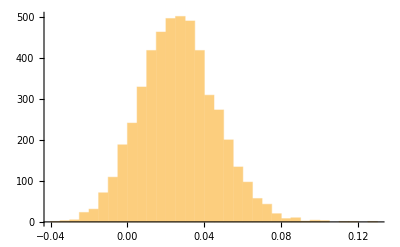

```mathematica
CCbRmatisto=Flatten[Table[Table[CCbootstrapR[st1,st2],{st2,st1+1,nstocks}],{st1,1,nstocks}],1];
Histogram[CCbRmatisto]
```

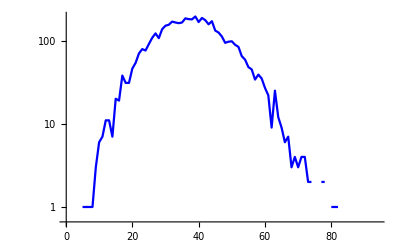

```mathematica
histoCCbR=BinCounts[CCbRmatisto,{grid}];
CCbRisto=ListLogPlot[histoCCbR,Joined->True,PlotStyle->Blue,PlotRange->All]
```

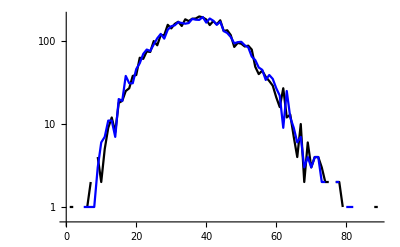

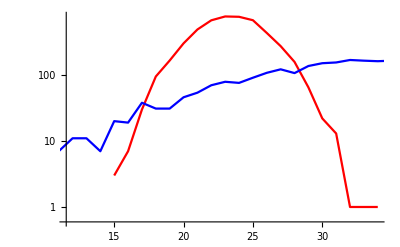

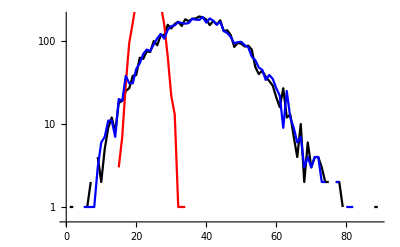

```mathematica
Show[CCisto,CCbRisto]
Show[CCbisto,CCbRisto]
Show[CCisto,CCbisto,CCbRisto]
```

```mathematica
Flatten[Table[Table[{st1,st2,CC[st1,st2],
                                              " ",CCbootstrap[st1,st2],CCbootstrapsd[st1,st2], 
                                              " ",Abs[CC[st1,st2]-CCbootstrap[st1,st2]]-CCbootstrapsd[st1,st2],
                                              " ",CCbootstrapR[st1,st2],CCbootstrapRsd[st1,st2],
                                              " ",Abs[CC[st1,st2]-CCbootstrapR[st1,st2]]-CCbootstrapRsd[st1,st2]},{st2,st1+1,5}],{st1,1,5}],1]//TableForm
```

1 | 2 | 0.0166255 |   | -0.00330189 | 0.0133724 |   | 0.00655502 |   | 0.0139396 | 0.0167414 |   | -0.0140555
1 | 3 | 0.00779223 |   | -0.00524349 | 0.0111856 |   | 0.00185012 |   | 0.0105297 | 0.0103935 |   | -0.00765606
1 | 4 | 0.0645654 |   | 0.00365542 | 0.011195 |   | 0.0497149 |   | 0.0605562 | 0.0165755 |   | -0.0125662
1 | 5 | 0.0544416 |   | 0.00355409 | 0.0131377 |   | 0.0377498 |   | 0.0556777 | 0.0142469 |   | -0.0130107
2 | 3 | 0.00990031 |   | 0.00359779 | 0.00959068 |   | -0.00328816 |   | 0.00601711 | 0.0130917 |   | -0.00920845
2 | 4 | 0.0504668 |   | -0.00226442 | 0.0147271 |   | 0.0380041 |   | 0.051539 | 0.0103728 |   | -0.00930056
2 | 5 | 0.0522502 |   | 0.000252189 | 0.0153 |   | 0.036698 |   | 0.0539836 | 0.0164656 |   | -0.0147321
3 | 4 | 0.0225172 |   | -0.0043922 | 0.0116009 |   | 0.0153085 |   | 0.0218867 | 0.018138 |   | -0.0175076
3 | 5 | 0.0271549 |   | 0.000519036 | 0.0144069 |   | 0.012229 |   | 0.0361112 | 0.012386 |   | -0.00342983
4 | 5 | 0.0530319 |   | -0.00142237 | 0.0126071 |   | 0.0418471 |   | 0.0590611 | 0.0133014 |   | -0.00727218

### bootstrap - pairs are shuffled

```mathematica
(*genero iter random samples dalla distribuzione delle copie di bootstrap*)
 Clear[index]
DateList[]
Do[Print[i," ",DateList[]];
     Do[Print[i," ",st1];
         CCb[i,st1,st1]=1;
         Do[index=Table[RandomInteger[{1,NN}],{n,1,NN}];
              uno=Table[data[[index[[n]],st1]],{n,1,NN}];
              due=Table[data[[index[[n]],st2]],{n,1,NN}];
              CCb[i,st1,st2]=Correlation[uno,due];
              CCb[i,st2,st1]=CCb[i,st1,st2];,
             {st2,st1+1,nstocks}],
        {st1,1,nstocks}],
    {i,1,iter}]
DateList[]
```

{2024,6,2,18,51,43.020901}

1 {2024,6,2,18,51,43.023931}

1 1

1 2

1 3

1 4

1 5

1 6

1 7

1 8

1 9

1 10

1 11

1 12

1 13

1 14

1 15

1 16

1 17

1 18

1 19

1 20

1 21

1 22

1 23

1 24

1 25

1 26

1 27

1 28

1 29

1 30

1 31

1 32

1 33

1 34

1 35

1 36

1 37

1 38

1 39

1 40

1 41

1 42

1 43

1 44

1 45

1 46

1 47

1 48

1 49

1 50

1 51

1 52

1 53

1 54

1 55

1 56

1 57

1 58

1 59

1 60

1 61

1 62

1 63

1 64

1 65

1 66

1 67

1 68

1 69

1 70

1 71

1 72

1 73

1 74

1 75

1 76

1 77

1 78

1 79

1 80

1 81

1 82

1 83

1 84

1 85

1 86

1 87

1 88

1 89

1 90

1 91

1 92

1 93

1 94

1 95

1 96

1 97

1 98

1 99

1 100

2 {2024,6,2,18,59,37.707633}

2 1

2 2

2 3

2 4

2 5

2 6

2 7

2 8

2 9

2 10

2 11

2 12

2 13

2 14

2 15

2 16

2 17

2 18

2 19

2 20

2 21

2 22

2 23

2 24

2 25

2 26

2 27

2 28

2 29

2 30

2 31

2 32

2 33

2 34

2 35

2 36

2 37

2 38

2 39

2 40

2 41

2 42

2 43

2 44

2 45

2 46

2 47

2 48

2 49

2 50

2 51

2 52

2 53

2 54

2 55

2 56

2 57

2 58

2 59

2 60

2 61

2 62

2 63

2 64

2 65

2 66

2 67

2 68

2 69

2 70

2 71

2 72

2 73

2 74

2 75

2 76

2 77

2 78

2 79

2 80

2 81

2 82

2 83

2 84

2 85

2 86

2 87

2 88

2 89

2 90

2 91

2 92

2 93

2 94

2 95

2 96

2 97

2 98

2 99

2 100

3 {2024,6,2,19,7,5.716271}

3 1

3 2

3 3

3 4

3 5

3 6

3 7

3 8

3 9

3 10

3 11

3 12

3 13

3 14

3 15

3 16

3 17

3 18

3 19

3 20

3 21

3 22

3 23

3 24

3 25

3 26

3 27

3 28

3 29

3 30

3 31

3 32

3 33

3 34

3 35

3 36

3 37

3 38

3 39

3 40

3 41

3 42

3 43

3 44

3 45

3 46

3 47

3 48

3 49

3 50

3 51

3 52

3 53

3 54

3 55

3 56

3 57

3 58

3 59

3 60

3 61

3 62

3 63

3 64

3 65

3 66

3 67

3 68

3 69

3 70

3 71

3 72

3 73

3 74

3 75

3 76

3 77

3 78

3 79

3 80

3 81

3 82

3 83

3 84

3 85

3 86

3 87

3 88

3 89

3 90

3 91

3 92

3 93

3 94

3 95

3 96

3 97

3 98

3 99

3 100

4 {2024,6,2,19,14,33.31534}

4 1

4 2

4 3

4 4

4 5

4 6

4 7

4 8

4 9

4 10

4 11

4 12

4 13

4 14

4 15

4 16

4 17

4 18

4 19

4 20

4 21

4 22

4 23

4 24

4 25

4 26

4 27

4 28

4 29

4 30

4 31

4 32

4 33

4 34

4 35

4 36

4 37

4 38

4 39

4 40

4 41

4 42

4 43

4 44

4 45

4 46

4 47

4 48

4 49

4 50

4 51

4 52

4 53

4 54

4 55

4 56

4 57

4 58

4 59

4 60

4 61

4 62

4 63

4 64

4 65

4 66

4 67

4 68

4 69

4 70

4 71

4 72

4 73

4 74

4 75

4 76

4 77

4 78

4 79

4 80

4 81

4 82

4 83

4 84

4 85

4 86

4 87

4 88

4 89

4 90

4 91

4 92

4 93

4 94

4 95

4 96

4 97

4 98

4 99

4 100

5 {2024,6,2,19,21,54.489909}

5 1

5 2

5 3

5 4

5 5

5 6

5 7

5 8

5 9

5 10

5 11

5 12

5 13

5 14

5 15

5 16

5 17

5 18

5 19

5 20

5 21

5 22

5 23

5 24

5 25

5 26

5 27

5 28

5 29

5 30

5 31

5 32

5 33

5 34

5 35

5 36

5 37

5 38

5 39

5 40

5 41

5 42

5 43

5 44

5 45

5 46

5 47

5 48

5 49

5 50

5 51

5 52

5 53

5 54

5 55

5 56

5 57

5 58

5 59

5 60

5 61

5 62

5 63

5 64

5 65

5 66

5 67

5 68

5 69

5 70

5 71

5 72

5 73

5 74

5 75

5 76

5 77

5 78

5 79

5 80

5 81

5 82

5 83

5 84

5 85

5 86

5 87

5 88

5 89

5 90

5 91

5 92

5 93

5 94

5 95

5 96

5 97

5 98

5 99

5 100

6 {2024,6,2,19,29,19.915747}

6 1

6 2

6 3

6 4

6 5

6 6

6 7

6 8

6 9

6 10

6 11

6 12

6 13

6 14

6 15

6 16

6 17

6 18

6 19

6 20

6 21

6 22

6 23

6 24

6 25

6 26

6 27

6 28

6 29

6 30

6 31

6 32

6 33

6 34

6 35

6 36

6 37

6 38

6 39

6 40

6 41

6 42

6 43

6 44

6 45

6 46

6 47

6 48

6 49

6 50

6 51

6 52

6 53

6 54

6 55

6 56

6 57

6 58

6 59

6 60

6 61

6 62

6 63

6 64

6 65

6 66

6 67

6 68

6 69

6 70

6 71

6 72

6 73

6 74

6 75

6 76

6 77

6 78

6 79

6 80

6 81

6 82

6 83

6 84

6 85

6 86

6 87

6 88

6 89

6 90

6 91

6 92

6 93

6 94

6 95

6 96

6 97

6 98

6 99

6 100

7 {2024,6,2,19,36,48.296097}

7 1

7 2

7 3

7 4

7 5

7 6

7 7

7 8

7 9

7 10

7 11

7 12

7 13

7 14

7 15

7 16

7 17

7 18

7 19

7 20

7 21

7 22

7 23

7 24

7 25

7 26

7 27

7 28

7 29

7 30

7 31

7 32

7 33

7 34

7 35

7 36

7 37

7 38

7 39

7 40

7 41

7 42

7 43

7 44

7 45

7 46

7 47

7 48

7 49

7 50

7 51

7 52

7 53

7 54

7 55

7 56

7 57

7 58

7 59

7 60

7 61

7 62

7 63

7 64

7 65

7 66

7 67

7 68

7 69

7 70

7 71

7 72

7 73

7 74

7 75

7 76

7 77

7 78

7 79

7 80

7 81

7 82

7 83

7 84

7 85

7 86

7 87

7 88

7 89

7 90

7 91

7 92

7 93

7 94

7 95

7 96

7 97

7 98

7 99

7 100

8 {2024,6,2,19,44,25.44638}

8 1

8 2

8 3

8 4

8 5

8 6

8 7

8 8

8 9

8 10

8 11

8 12

8 13

8 14

8 15

8 16

8 17

8 18

8 19

8 20

8 21

8 22

8 23

8 24

8 25

8 26

8 27

8 28

8 29

8 30

8 31

8 32

8 33

8 34

8 35

8 36

8 37

8 38

8 39

8 40

8 41

8 42

8 43

8 44

8 45

8 46

8 47

8 48

8 49

8 50

8 51

8 52

8 53

8 54

8 55

8 56

8 57

8 58

8 59

8 60

8 61

8 62

8 63

8 64

8 65

8 66

8 67

8 68

8 69

8 70

8 71

8 72

8 73

8 74

8 75

8 76

8 77

8 78

8 79

8 80

8 81

8 82

8 83

8 84

8 85

8 86

8 87

8 88

8 89

8 90

8 91

8 92

8 93

8 94

8 95

8 96

8 97

8 98

8 99

8 100

9 {2024,6,2,19,52,8.822648}

9 1

9 2

9 3

9 4

9 5

9 6

9 7

9 8

9 9

9 10

9 11

9 12

9 13

9 14

9 15

9 16

9 17

9 18

9 19

9 20

9 21

9 22

9 23

9 24

9 25

9 26

9 27

9 28

9 29

9 30

9 31

9 32

9 33

9 34

9 35

9 36

9 37

9 38

9 39

9 40

9 41

9 42

9 43

9 44

9 45

9 46

9 47

9 48

9 49

9 50

9 51

9 52

9 53

9 54

9 55

9 56

9 57

9 58

9 59

9 60

9 61

9 62

9 63

9 64

9 65

9 66

9 67

9 68

9 69

9 70

9 71

9 72

9 73

9 74

9 75

9 76

9 77

9 78

9 79

9 80

9 81

9 82

9 83

9 84

9 85

9 86

9 87

9 88

9 89

9 90

9 91

9 92

9 93

9 94

9 95

9 96

9 97

9 98

9 99

9 100

10 {2024,6,2,19,59,45.207174}

10 1

10 2

10 3

10 4

10 5

10 6

10 7

10 8

10 9

10 10

10 11

10 12

10 13

10 14

10 15

10 16

10 17

10 18

10 19

10 20

10 21

10 22

10 23

10 24

10 25

10 26

10 27

10 28

10 29

10 30

10 31

10 32

10 33

10 34

10 35

10 36

10 37

10 38

10 39

10 40

10 41

10 42

10 43

10 44

10 45

10 46

10 47

10 48

10 49

10 50

10 51

10 52

10 53

10 54

10 55

10 56

10 57

10 58

10 59

10 60

10 61

10 62

10 63

10 64

10 65

10 66

10 67

10 68

10 69

10 70

10 71

10 72

10 73

10 74

10 75

10 76

10 77

10 78

10 79

10 80

10 81

10 82

10 83

10 84

10 85

10 86

10 87

10 88

10 89

10 90

10 91

10 92

10 93

10 94

10 95

10 96

10 97

10 98

10 99

10 100

{2024,6,2,20,7,9.71285}

```mathematica
Do[Do[CCbootstrapP[st1,st2]=Sum[CCb[i,st1,st2],{i,1,iter}]/iter;
         CCbootstrapPvar[st1,st2]=Sum[(CCb[i,st1,st2]-CCbootstrapP[st1,st2])^2,{i,1,iter}]/iter;
         CCbootstrapPsd[st1,st2]=Sqrt[CCbootstrapPvar[st1,st2]];,
        {st2,1,nstocks}],
        {st1,1,nstocks}]
```

```mathematica
CCbPmat=Table[Table[CCbootstrapP[st1,st2],{st2,1,nstocks}],{st1,1,nstocks}];
CCbPmat//MatrixForm
```

(1 | 0.0139396 | 0.0105297 | 0.0605562 | 0.0556777 | 0.0294305 | 0.0894313 | 0.0304919 | 0.0358072 | 0.0444249 | 0.0732939 | 0.050029 | 0.0475373 | 0.0653025 | 0.0452705 | 0.028268 | 0.037836 | 0.0482471 | 0.0337093 | 0.0260869 | 0.0163627 | 0.0420968 | 0.0486535 | 0.0252666 | 0.0595725 | 0.0412785 | 0.0437481 | 0.0479903 | 0.0515236 | 0.0207044 | 0.0248136 | 0.0509523 | 0.0409197 | 0.0138752 | 0.0521108 | 0.0489107 | 0.037096 | 0.0400583 | 0.0267634 | 0.028604 | 0.052871 | 0.0488848 | 0.0302271 | 0.0743087 | 0.0322984 | 0.0349696 | 0.0635966 | 0.052253 | 0.0154114 | -0.00162817 | 0.0334039 | -0.00775654 | 0.00334987 | 0.0448062 | 0.0464189 | 0.0413145 | 0.0706915 | 0.0494796 | -0.00705374 | 0.021829 | 0.0297256 | 0.0664744 | 0.0209143 | 0.0482304 | 0.0358156 | 0.0447904 | 0.0372002 | 0.0628478 | 0.0110578 | 0.00305653 | 0.0411117 | 0.00196636 | 0.0487704 | 0.0387162 | 0.0417204 | -0.012181 | 0.0043444 | 0.0361903 | 0.0572205 | 0.0344244 | 0.0475309 | 0.0315864 | 0.0296234 | 0.0185065 | 0.0278385 | 0.0208788 | 0.0325239 | 0.0368838 | 0.0164418 | 0.0184816 | 0.0540734 | 0.0157688 | 0.0634629 | -0.0215916 | 0.000506865 | -0.000679193 | -0.0134618 | 0.0468496 | -0.0068274 | 0.0342663
0.0139396 | 1 | 0.00601711 | 0.051539 | 0.0539836 | 0.0376985 | 0.0439763 | 0.0299705 | 0.0300981 | 0.0144813 | 0.0727705 | 0.04062 | 0.0269213 | 0.0132102 | 0.0119767 | 0.0589292 | 0.0247508 | 0.00521523 | 0.0537618 | 0.0174317 | 0.00400655 | 0.0422337 | 0.0530292 | 0.0495091 | 0.0295822 | 0.0332359 | 0.0917665 | 0.048751 | 0.0448793 | 0.0484784 | 0.0364145 | 0.0390032 | 0.0639824 | 0.0190652 | 0.0454427 | 0.0307163 | 0.0198848 | 0.000955107 | 0.0202741 | 0.0242749 | 0.0248235 | 0.0639941 | 0.0264937 | 0.0341456 | 0.0308532 | 0.0599605 | 0.0484067 | 0.0617161 | 0.00539724 | -0.00315162 | 0.0143381 | 0.016341 | 0.0045658 | 0.0209942 | 0.01634 | 0.0233258 | 0.0197182 | 0.0254143 | 0.00629536 | 0.0447995 | 0.0172693 | 0.0399525 | 0.0144127 | 0.0270046 | 0.0291108 | 0.0346383 | 0.0420426 | 0.0670478 | 0.00525191 | 0.00980502 | 0.0219607 | 0.00737546 | 0.0370767 | 0.0186591 | 0.0453998 | 0.00877337 | 0.0492308 | 0.0462298 | 0.0316795 | 0.0597307 | 0.0491149 | 0.0366077 | 0.0595 | 0.0158886 | 0.0293086 | 0.0343692 | 0.0346582 | 0.0133177 | 0.00522218 | -0.00143144 | 0.0264369 | 0.0561905 | 0.0108811 | 0.0384538 | 0.0224816 | 0.0135306 | 0.0140659 | 0.0156249 | -0.00474407 | 0.0345676
0.0105297 | 0.00601711 | 1 | 0.0218867 | 0.0361112 | 0.0110366 | 0.0144276 | 0.0375615 | 0.00719502 | -0.0056502 | 0.0151202 | -0.00698839 | 0.0367052 | 0.0209331 | 0.0506859 | 0.0330788 | 0.0344395 | 0.0277263 | 0.0225413 | 0.0311891 | 0.0314064 | 0.00383221 | 0.0281166 | 0.00152138 | -0.00339104 | -0.00845526 | -0.00358148 | 0.005363 | 0.0225667 | 0.039623 | -0.0158472 | 0.0258008 | 0.00608793 | 0.0214522 | 0.0094477 | 0.00826101 | 0.0420339 | -0.0119807 | -0.0182933 | 0.0242912 | 0.032175 | 0.0136997 | 0.0317979 | 0.0116767 | 0.0186879 | 0.0266991 | 0.00592522 | 0.0261111 | -0.0000622736 | 0.00940513 | 0.0179032 | 0.0283793 | -0.00288614 | 0.0467155 | -0.00791416 | 0.0125626 | 0.0036385 | 0.0447019 | -0.0242086 | 0.00580839 | 0.020288 | -0.000997375 | 0.00436912 | 0.0133007 | -0.0186556 | 0.0234033 | 0.000758217 | 0.0131212 | 0.00369098 | 0.0244796 | 0.00774898 | 0.0212243 | 0.030521 | 0.0031128 | 0.0126495 | 0.00762889 | -0.00655367 | -0.00524491 | 0.0304909 | -0.0313314 | 0.0168141 | 0.00232563 | 0.0280361 | -0.0258298 | 0.0151648 | -0.00312976 | 0.0219455 | 0.0215841 | 0.00903607 | 0.00194683 | 0.00679637 | -0.00985208 | 0.0106446 | -0.0180739 | 0.015953 | 0.00622039 | 0.0202167 | -0.0025286 | 0.00213976 | -0.0183408
0.0605562 | 0.051539 | 0.0218867 | 1 | 0.0590611 | 0.0305374 | 0.0713954 | 0.0223027 | 0.0111058 | 0.0578292 | 0.0870768 | 0.0530684 | 0.0659603 | 0.0327575 | 0.00751047 | 0.0452306 | 0.0470464 | 0.0105997 | 0.0223002 | 0.00526028 | 0.0228235 | 0.0324874 | 0.0501967 | 0.0786799 | 0.0454249 | 0.0268149 | 0.0482495 | 0.0320183 | 0.0632618 | 0.0490263 | 0.018117 | 0.0353053 | 0.0516635 | 0.0152697 | 0.039297 | 0.0640358 | 0.0601353 | 0.0273984 | 0.051093 | 0.0338452 | 0.0501046 | 0.052974 | 0.0306512 | 0.0869673 | 0.0451057 | 0.0460588 | 0.0155775 | 0.0155598 | -0.0156977 | 0.012019 | 0.00760853 | -0.00137489 | 0.0423974 | 0.0245109 | 0.0429397 | 0.07183 | 0.0562645 | 0.0496592 | 0.0167938 | 0.0224049 | 0.0215695 | 0.0338873 | 0.00496915 | 0.0156862 | 0.0253787 | 0.0198659 | 0.0684829 | 0.0629147 | 0.0166062 | 0.013871 | 0.0352406 | 0.0256913 | 0.0445772 | 0.0308391 | 0.0475737 | 0.0354255 | 0.0384045 | 0.00792538 | 0.0349151 | 0.0384814 | 0.0563405 | 0.0104759 | 0.0820638 | 0.0418729 | 0.0544577 | 0.0364815 | 0.00370606 | 0.0379448 | 0.016739 | 0.0366507 | 0.0489984 | 0.0354299 | 0.0487756 | 0.000362116 | 0.0302743 | 0.00662981 | 0.0112387 | 0.0479931 | 0.0548723 | 0.0315769
0.0556777 | 0.0539836 | 0.0361112 | 0.0590611 | 1 | 0.0393919 | 0.0706032 | 0.0394838 | 0.056328 | 0.048448 | 0.0633923 | 0.0351353 | 0.0387685 | 0.0539614 | 0.0275866 | 0.0396965 | 0.0690085 | 0.0390862 | 0.0542313 | 0.0216695 | 0.0626765 | 0.0489734 | 0.0361227 | 0.0727667 | 0.0241944 | 0.0191738 | 0.0772104 | 0.0623142 | 0.0539854 | 0.0725312 | 0.0377425 | 0.033323 | 0.0629281 | 0.0211471 | 0.0672723 | 0.0510284 | 0.0154824 | 0.0488267 | 0.028984 | 0.0472252 | 0.037051 | 0.0549755 | 0.0480631 | 0.0841708 | 0.054894 | 0.0672759 | 0.0236106 | 0.0503042 | -0.0139931 | -0.0124996 | 0.0592182 | -0.000340667 | 0.0189815 | 0.041395 | 0.0300893 | 0.0747928 | 0.0238692 | 0.0112811 | 0.0350508 | 0.0329739 | 0.0635784 | 0.0650306 | 0.0404388 | 0.0432647 | 0.0193604 | 0.0225735 | 0.0508603 | 0.0786269 | 0.0337498 | 0.0569856 | 0.0270762 | 0.02355 | 0.0770294 | 0.0169634 | 0.0805224 | 0.0168432 | 0.0360277 | 0.0240863 | 0.043011 | 0.018418 | 0.0653463 | 0.0280202 | 0.0992613 | 0.0498352 | 0.0452884 | 0.0617075 | 0.0332427 | 0.0556028 | 0.0121233 | 0.0374217 | 0.063 | 0.0496863 | 0.0432356 | 0.0236363 | -0.000617669 | 0.0263585 | 0.0105338 | 0.0301937 | 0.0318229 | 0.047444
0.0294305 | 0.0376985 | 0.0110366 | 0.0305374 | 0.0393919 | 1 | 0.053969 | 0.0105878 | 0.0448517 | 0.024138 | 0.036447 | 0.0032208 | 0.016945 | 0.0367398 | 0.020807 | 0.0232808 | 0.0303143 | 0.00104338 | 0.0338842 | 0.0192782 | 0.02773 | 0.010872 | 0.0121111 | 0.0289828 | 0.0157014 | 0.000762297 | 0.0219236 | 0.0120436 | 0.0102895 | 0.0144825 | 0.0346109 | 0.0213106 | 0.0207021 | -0.0207834 | 0.0141602 | -0.0131045 | 0.0151237 | 0.0344525 | 0.0139297 | 0.0275543 | 0.0115814 | 0.0157646 | 0.00836827 | 0.0177396 | 0.058823 | -0.000858317 | -0.00483608 | 0.00295687 | -0.0208681 | -0.0030129 | 0.0197276 | 0.00500731 | 0.00882836 | 0.0018123 | 0.0382061 | 0.0222798 | 0.00635721 | 0.0213581 | -0.0233721 | 0.0206716 | 0.011041 | 0.0338632 | -0.00892943 | 0.0245816 | 0.00546774 | 0.0364265 | 0.0240286 | 0.0301211 | -0.0119392 | 0.0346383 | -0.0113042 | 0.00556585 | 0.00365838 | 0.0204942 | 0.0130015 | 0.0216755 | 0.0021045 | 0.0246247 | 0.00348668 | 0.0228692 | 0.0367725 | 0.0132718 | 0.0128443 | 0.0369403 | 0.0245672 | 0.015217 | 0.0184162 | 0.00991353 | -0.0024531 | 0.0110848 | 0.0291295 | 0.00191043 | 0.0403919 | -0.0185017 | 0.0253369 | -0.0129918 | 0.024502 | 0.036772 | 0.0165167 | 0.0172513
0.0894313 | 0.0439763 | 0.0144276 | 0.0713954 | 0.0706032 | 0.053969 | 1 | 0.0312142 | 0.0593106 | 0.0557373 | 0.0860949 | 0.0394281 | 0.0393767 | 0.0404922 | 0.0358478 | 0.0261184 | 0.0318744 | 0.0053448 | 0.0762959 | 0.0191529 | 0.0489337 | 0.0599218 | 0.0266485 | 0.074789 | 0.0440099 | -0.01706 | 0.0705277 | 0.0439889 | 0.0487268 | 0.0520426 | 0.0195826 | 0.0317778 | 0.0496475 | 0.0400913 | 0.0232733 | 0.0570671 | 0.00256899 | 0.0363079 | 0.0536952 | 0.0576669 | 0.0397475 | 0.0416131 | 0.0121988 | 0.049637 | 0.0480618 | 0.0595584 | 0.0359013 | 0.0407295 | 0.00238273 | 0.0317837 | 0.00917742 | 0.0094304 | -0.00525357 | 0.00422439 | 0.0579251 | 0.0328918 | 0.00722454 | 0.0565278 | -0.00732064 | 0.0222227 | 0.00360234 | 0.0541737 | 0.0346592 | 0.0345588 | 0.00665401 | 0.015505 | 0.0518574 | 0.0858293 | -0.00263307 | 0.056153 | 0.0410252 | 0.0108514 | 0.0277104 | 0.0410954 | 0.0524557 | 0.0112161 | 0.0341307 | 0.0477306 | 0.0445443 | 0.0654865 | 0.0429903 | 0.0499615 | 0.0473327 | -0.00379022 | 0.0424252 | 0.044433 | 0.010762 | 0.0319738 | 0.0336202 | 0.0325466 | 0.0487695 | 0.0382672 | 0.0351817 | 0.0193005 | -0.00846971 | 0.000756634 | 0.0139983 | 0.0134482 | 0.0318692 | 0.00257297
0.0304919 | 0.0299705 | 0.0375615 | 0.0223027 | 0.0394838 | 0.0105878 | 0.0312142 | 1 | 0.055239 | 0.0320169 | 0.0730072 | 0.0523171 | 0.0414892 | 0.0290673 | 0.0345885 | 0.061248 | 0.0339897 | 0.0280741 | 0.05283 | 0.0425562 | 0.031193 | 0.0322879 | 0.0550401 | 0.0412931 | 0.0541606 | 0.0220387 | 0.0505718 | 0.0634493 | 0.0426448 | 0.0308508 | 0.0407087 | 0.0267471 | 0.0581745 | 0.00549235 | 0.0337187 | 0.0438316 | 0.0104102 | 0.0162471 | 0.0397776 | 0.04537 | 0.0391627 | 0.0696126 | -0.00126318 | 0.0678053 | 0.0333192 | 0.0492848 | 0.0259177 | 0.0278361 | 0.0451031 | -0.00238139 | 0.0186509 | -0.000562526 | 0.0088843 | 0.0312085 | 0.0306581 | 0.0495257 | 0.0400834 | 0.0651584 | -0.0060837 | 0.0515818 | 0.0272213 | 0.0174955 | 0.0445282 | 0.0439206 | -0.0073228 | 0.0535984 | 0.0379272 | 0.0383665 | 0.040572 | 0.0235894 | 0.0708218 | 0.0141071 | 0.00901128 | 0.0259599 | 0.0575669 | 0.00929666 | 0.00614207 | 0.0297141 | 0.0481733 | 0.0555808 | 0.0418107 | 0.0162817 | 0.0233168 | 0.00221706 | 0.0102934 | 0.0396033 | 0.0279916 | 0.0177444 | 0.0266059 | 0.0145997 | 0.0311604 | 0.0522678 | 0.0704334 | -0.000195248 | 0.0335873 | 0.0171029 | 0.02813 | 0.0592299 | 0.0219537 | 0.0346684
0.0358072 | 0.0300981 | 0.00719502 | 0.0111058 | 0.056328 | 0.0448517 | 0.0593106 | 0.055239 | 1 | 0.0205038 | 0.03252 | 0.0256818 | 0.0290522 | 0.0474674 | 0.0425759 | 0.0349851 | 0.0154187 | 0.031194 | 0.0287942 | 0.0254099 | 0.0192311 | 0.0261359 | 0.0387139 | 0.0178087 | 0.0256929 | 0.0425463 | 0.0712455 | 0.0135225 | 0.0206289 | 0.0444039 | 0.0188873 | 0.0161038 | 0.0381221 | 0.0212165 | 0.0370638 | 0.0266032 | 0.01759 | 0.0248654 | 0.0560359 | 0.0363478 | 0.026105 | 0.045157 | 0.0408631 | 0.039035 | 0.0393306 | 0.0268087 | 0.0138755 | 0.0417021 | 0.0250817 | -0.00545391 | -0.00714834 | 0.0178401 | 0.0161763 | -0.00415718 | 0.0287936 | -0.00962432 | 0.00893425 | 0.00672386 | 0.00394445 | 0.021251 | 0.0148082 | 0.00809105 | 0.0313982 | 0.0263386 | 0.0275406 | -0.00155255 | 0.0167885 | 0.0342155 | 0.00822934 | 0.0156711 | 0.0145336 | 0.0195135 | 0.0134117 | 0.0274532 | 0.0527634 | 0.0191494 | 0.0330437 | 0.00726736 | 0.051851 | 0.0163668 | 0.0174696 | 0.0398472 | 0.0159291 | 0.00457796 | 0.030112 | 0.0449016 | 0.0170692 | 0.00254235 | -0.000557472 | 0.0220445 | 0.027602 | 0.0389921 | 0.00439939 | 0.0170482 | 0.0365168 | -0.00292169 | 0.0136536 | 0.0234998 | 0.0371819 | 0.00896629
0.0444249 | 0.0144813 | -0.0056502 | 0.0578292 | 0.048448 | 0.024138 | 0.0557373 | 0.0320169 | 0.0205038 | 1 | 0.0757785 | 0.0338772 | 0.0328766 | 0.0168861 | 0.00431398 | 0.0522025 | 0.0231114 | 0.00974492 | 0.0203395 | 0.00738144 | 0.00962813 | 0.03429 | 0.0269801 | 0.0447453 | 0.0559622 | -0.00300655 | 0.0423318 | -0.0025023 | 0.0411343 | 0.024015 | 0.0464479 | 0.0340888 | 0.0405858 | 0.0319173 | 0.0461989 | 0.0632798 | 0.0460268 | 0.011915 | 0.0191596 | 0.03263 | 0.0319662 | 0.0264825 | 0.0477328 | 0.0324059 | 0.0369206 | 0.0295419 | 0.0264265 | 0.0556793 | -0.00352789 | -0.012155 | 0.0368746 | 0.00516131 | 0.0284796 | 0.0417783 | 0.0394568 | 0.00655462 | 0.0236016 | 0.0283699 | 0.00231661 | 0.01107 | 0.0191646 | 0.0394294 | 0.0130241 | -0.00389627 | -0.0134877 | 0.0520385 | 0.0338825 | 0.0412093 | 0.00698904 | 0.0511662 | 0.0420671 | 0.0143171 | 0.00815878 | 0.0316546 | 0.0829984 | -0.000652662 | 0.0268318 | 0.00881577 | 0.0214216 | 0.0387929 | 0.0697292 | 0.0457994 | 0.0276017 | -0.0025606 | 0.0532118 | 0.005207 | 0.0418979 | 0.0609526 | 0.0445242 | 0.0169511 | 0.0270105 | 0.0326304 | 0.0254103 | 0.0281729 | 0.000479588 | 0.0275644 | 0.00686602 | 0.0242885 | 0.0299756 | 0.0139716
0.0732939 | 0.0727705 | 0.0151202 | 0.0870768 | 0.0633923 | 0.036447 | 0.0860949 | 0.0730072 | 0.03252 | 0.0757785 | 1 | 0.0547746 | 0.0427632 | 0.0529376 | 0.0211122 | 0.0958381 | 0.0614558 | 0.0258088 | 0.0247555 | 0.0234028 | 0.0680349 | 0.0607933 | 0.0574637 | 0.0658939 | 0.0468612 | 0.0297761 | 0.0706058 | 0.0475609 | 0.0451324 | 0.0543073 | 0.0511442 | 0.023225 | 0.101578 | 0.0199923 | 0.0694489 | 0.0757966 | 0.00221523 | 0.014991 | 0.0727024 | 0.0342425 | 0.0636015 | 0.0591228 | 0.0369599 | 0.0871337 | 0.0580951 | 0.0287421 | 0.0413706 | 0.0792052 | 0.00715172 | -0.0116064 | 0.0621192 | 0.0154456 | 0.0168807 | 0.0377063 | 0.0582335 | 0.0664893 | 0.0797749 | 0.0784463 | 0.0167415 | 0.0612324 | 0.010488 | 0.0421306 | 0.012326 | 0.0562211 | 0.0301189 | 0.0421795 | 0.0711064 | 0.0737982 | 0.0283235 | 0.0316117 | 0.0270249 | 0.0242811 | 0.0419964 | 0.0603422 | 0.103085 | 0.0243419 | 0.0553078 | 0.0231837 | 0.0263195 | 0.0293165 | 0.119675 | 0.0202771 | 0.0981175 | -0.0110708 | 0.0311381 | 0.0238579 | 0.0259227 | 0.0613051 | 0.023156 | 0.0506172 | 0.0606142 | 0.0636948 | 0.0973653 | 0.00965667 | 0.005219 | 0.0145626 | 0.00712057 | 0.0417739 | 0.0378651 | 0.0286435
0.050029 | 0.04062 | -0.00698839 | 0.0530684 | 0.0351353 | 0.0032208 | 0.0394281 | 0.0523171 | 0.0256818 | 0.0338772 | 0.0547746 | 1 | 0.0329076 | 0.0106314 | -0.0022816 | 0.0447349 | 0.0122306 | 0.0218651 | 0.040046 | 0.0075449 | 0.0197588 | 0.0365077 | 0.0511749 | 0.0539518 | 0.0331446 | 0.0176179 | 0.0153246 | 0.0318988 | 0.0282744 | 0.0406983 | 0.0217409 | 0.0161208 | 0.066243 | 0.0139491 | 0.00612096 | 0.0341369 | -0.00207823 | 0.0115951 | 0.0297592 | 0.0274145 | 0.046381 | 0.0124511 | 0.0111187 | 0.0426176 | 0.0348996 | 0.0369699 | 0.0103772 | 0.0410249 | 0.0149366 | 0.00568293 | 0.0341413 | -0.00760176 | 0.0388828 | 0.0313309 | 0.00172639 | 0.0440462 | 0.0411364 | 0.0314082 | 0.0192963 | 0.0307882 | -0.00578831 | 0.0362788 | 0.00193753 | 0.0432795 | 0.0367606 | 0.0574853 | 0.0335805 | 0.058311 | 0.002185 | 0.0446366 | 0.0241936 | 0.030456 | 0.0371244 | 0.027263 | 0.0387824 | 0.0304384 | 0.0623594 | 0.0562456 | 0.0299441 | 0.0522079 | 0.0388459 | 0.0334311 | 0.0515185 | 0.0161963 | 0.02566 | -0.00892712 | 0.010834 | 0.015624 | 0.0266724 | 0.0315175 | 0.00234731 | 0.0237191 | 0.0310494 | -0.00252596 | 0.00717505 | 0.043765 | -0.00841326 | 0.015014 | 0.0240928 | 0.0374826
0.0475373 | 0.0269213 | 0.0367052 | 0.0659603 | 0.0387685 | 0.016945 | 0.0393767 | 0.0414892 | 0.0290522 | 0.0328766 | 0.0427632 | 0.0329076 | 1 | 0.0439481 | 0.0192702 | 0.0672399 | 0.0570056 | 0.027276 | 0.0459046 | 0.0479489 | 0.0284439 | 0.0542704 | 0.0490617 | 0.0401429 | 0.0178828 | 0.00642738 | 0.0864223 | 0.0466251 | 0.0371205 | 0.0183283 | 0.0422022 | 0.056641 | 0.127471 | 0.0118162 | 0.047836 | 0.0410245 | 0.0359931 | 0.00823311 | 0.0232494 | 0.0325039 | 0.0459879 | 0.0346866 | 0.0199711 | 0.0598177 | 0.000852012 | 0.0426809 | 0.0148127 | 0.0228342 | 0.0223319 | 0.0115871 | 0.00576682 | -0.00768877 | 0.0105928 | 0.0230007 | -0.00132597 | 0.0396087 | 0.0663203 | 0.034463 | 0.0217105 | 0.04544 | 0.0202345 | 0.0259661 | 0.0263942 | 0.02534 | 0.0367059 | 0.0525399 | 0.0753574 | 0.0555172 | 0.00393829 | 0.037723 | 0.0144682 | 0.0230508 | 0.00985359 | 0.0244175 | 0.0709941 | 0.0271307 | 0.0390539 | 0.0289478 | 0.0280248 | 0.0469227 | 0.0590691 | 0.0187403 | 0.0339467 | 0.00928198 | 0.0255518 | 0.0511657 | 0.0190537 | 0.0394684 | -0.00555812 | 0.0236551 | 0.021092 | 0.0369578 | 0.0376587 | -0.0104531 | 0.0186386 | 0.0416789 | 0.00401278 | -0.00105975 | 0.0405294 | 0.0134724
0.0653025 | 0.0132102 | 0.0209331 | 0.0327575 | 0.0539614 | 0.0367398 | 0.0404922 | 0.0290673 | 0.0474674 | 0.0168861 | 0.0529376 | 0.0106314 | 0.0439481 | 1 | 0.0361576 | 0.0179381 | 0.037306 | 0.0356578 | 0.0397097 | 0.00725921 | 0.0468639 | 0.0480577 | 0.0257078 | 0.0271899 | 0.0336669 | 0.046757 | 0.0551801 | 0.0425565 | 0.0548692 | 0.0166067 | 0.0166628 | 0.0400498 | 0.054696 | 0.0018111 | 0.0417229 | 0.0225666 | 0.0202959 | 0.0123815 | 0.0421788 | 0.0128916 | 0.0242183 | 0.0121813 | 0.0109907 | 0.0263702 | 0.0152606 | 0.044405 | 0.0188776 | 0.0195347 | 0.0123439 | 0.00711487 | 0.0321453 | -0.0216419 | -0.0115164 | 0.0234538 | 0.032196 | 0.0454197 | 0.0174167 | 0.0353792 | 0.0246852 | 0.0279348 | 0.00192027 | 0.0357065 | 0.0358636 | 0.0374332 | 0.00340708 | 0.00104187 | 0.024659 | 0.0475633 | -0.00978633 | -0.00298731 | 0.011141 | 0.0155468 | 0.0225384 | 0.0246637 | 0.0117858 | -0.00330497 | 0.00380098 | 0.0487224 | 0.039652 | 0.0258057 | 0.0123051 | -0.011255 | 0.0374442 | 0.0249459 | 0.00131263 | 0.0314656 | 0.0225968 | 0.0256884 | -0.0176451 | 0.0220681 | 0.0192956 | 0.0145875 | 0.044435 | 0.0255832 | -0.00122406 | -0.000509469 | 0.00123987 | 0.0194436 | 0.0173191 | 0.0217153
0.0452705 | 0.0119767 | 0.0506859 | 0.00751047 | 0.0275866 | 0.020807 | 0.0358478 | 0.0345885 | 0.0425759 | 0.00431398 | 0.0211122 | -0.0022816 | 0.0192702 | 0.0361576 | 1 | 0.00726511 | 0.00530088 | 0.0222925 | 0.0367533 | 0.0262636 | 0.0368217 | -0.00656885 | 0.032503 | 0.0462879 | -0.0000546495 | 0.022362 | 0.0315802 | 0.0202501 | 0.0137052 | 0.0241493 | -0.00216398 | 0.0359194 | 0.0386503 | 0.0201518 | 0.0467158 | 0.0433744 | 0.000281965 | 0.0392042 | 0.00227824 | 0.0138193 | 0.00658743 | 0.0290113 | 0.0134528 | 0.0535009 | 0.045116 | 0.0677722 | 0.040678 | 0.0284756 | 0.0290562 | 0.00227596 | -0.00149262 | 0.0366789 | 0.0291718 | -0.00626428 | 0.0102624 | 0.00229265 | 0.00418146 | -0.0096915 | -0.00775749 | 0.0183534 | 0.0110978 | 0.0530401 | -0.00289555 | 0.0184725 | 0.00806621 | 0.0327766 | 0.0523092 | 0.0103667 | 0.00144427 | 0.0258074 | -0.012244 | 0.0103666 | 0.019899 | -0.00686866 | 0.019144 | 0.0203085 | -0.0128655 | 0.00573654 | 0.0242325 | 0.0297697 | 0.00243111 | 0.0361384 | 0.0243468 | -0.0052115 | 0.037809 | 0.0221291 | -0.0140471 | 0.0272372 | 0.0130478 | 0.0373652 | 0.0303972 | 0.0259095 | 0.0298673 | -0.0026036 | 0.0155952 | 0.0108571 | 0.0235977 | 0.00834899 | -0.0040845 | 0.00389937
0.028268 | 0.0589292 | 0.0330788 | 0.0452306 | 0.0396965 | 0.0232808 | 0.0261184 | 0.061248 | 0.0349851 | 0.0522025 | 0.0958381 | 0.0447349 | 0.0672399 | 0.0179381 | 0.00726511 | 1 | 0.022957 | 0.0354699 | 0.061258 | 0.047602 | 0.0369538 | 0.0615162 | 0.0258125 | 0.0568991 | 0.0600753 | 0.00958233 | 0.071573 | 0.0619686 | 0.021433 | 0.0375003 | 0.0339748 | 0.0337223 | 0.064262 | 0.00932537 | 0.0265448 | 0.0493618 | 0.000227671 | 0.0458517 | 0.0375936 | 0.055324 | 0.0323358 | 0.0371643 | 0.0440421 | 0.0713046 | 0.0254928 | 0.0422537 | 0.0271784 | 0.0307416 | 0.0284101 | 0.0015217 | 0.00286491 | 0.0428481 | 0.0302995 | 0.0259145 | 0.0360103 | 0.0326893 | 0.0193785 | 0.0498718 | -0.0181319 | 0.0331497 | 0.0450909 | 0.0308108 | 0.0416905 | 0.0343191 | -0.00283418 | 0.0354458 | 0.0364783 | 0.0372505 | 0.0133385 | 0.00756517 | 0.0187775 | 0.0268462 | 0.0255702 | 0.0095076 | 0.0592262 | 0.0385981 | 0.0471397 | 0.0328811 | 0.0385037 | 0.0581913 | 0.052284 | 0.0276 | 0.052183 | 0.0250199 | 0.0160177 | 0.0237318 | 0.036651 | 0.0224103 | 0.0226192 | 0.0340689 | 0.0294099 | 0.0304101 | 0.023904 | 0.0126958 | 0.00715702 | 0.021311 | 0.0262725 | 0.0631252 | 0.0194012 | 0.0400139
0.037836 | 0.0247508 | 0.0344395 | 0.0470464 | 0.0690085 | 0.0303143 | 0.0318744 | 0.0339897 | 0.0154187 | 0.0231114 | 0.0614558 | 0.0122306 | 0.0570056 | 0.037306 | 0.00530088 | 0.022957 | 1 | 0.0109646 | 0.0537636 | 0.00912416 | 0.0484856 | 0.0363219 | 0.0358297 | 0.0265649 | 0.0273139 | 0.0248356 | 0.0390622 | 0.0437137 | 0.0357807 | 0.0284113 | 0.0250941 | 0.0357779 | 0.05242 | -0.000476723 | 0.023223 | 0.0234006 | 0.0317757 | 0.0350261 | 0.0326246 | 0.0322865 | 0.0275895 | 0.0362842 | 0.0181404 | 0.0555041 | 0.019973 | 0.00725885 | 0.0247966 | 0.0248292 | 0.0331613 | 0.00304234 | 0.0255063 | 0.0308398 | 0.0233725 | 0.0188586 | 0.0394866 | 0.0375749 | 0.0381809 | 0.0595426 | 0.0166409 | 0.0374714 | 0.0617001 | 0.0504452 | 0.0169778 | 0.0433901 | 0.0158771 | 0.0522106 | 0.0794871 | 0.0288976 | 0.0236126 | 0.0418512 | 0.0283498 | 0.00903373 | 0.0359415 | 0.00777606 | 0.0558667 | 0.00790089 | 0.0167536 | 0.0446873 | 0.0565522 | 0.0142715 | 0.0579203 | 0.0291626 | 0.0503591 | 0.0157666 | 0.0527326 | 0.0478567 | 0.00446168 | 0.0205567 | 0.0336278 | 0.0250657 | 0.00384999 | 0.0362303 | 0.0493243 | 0.0324797 | -0.00899 | -0.000778525 | 0.0312087 | 0.039827 | 0.0274674 | 0.021754
0.0482471 | 0.00521523 | 0.0277263 | 0.0105997 | 0.0390862 | 0.00104338 | 0.0053448 | 0.0280741 | 0.031194 | 0.00974492 | 0.0258088 | 0.0218651 | 0.027276 | 0.0356578 | 0.0222925 | 0.0354699 | 0.0109646 | 1 | 0.0127797 | 0.0166602 | 0.0214019 | 0.0158053 | 0.0323122 | 0.0186997 | 0.0470185 | 0.0151929 | 0.0135675 | 0.0358137 | 0.0260673 | -0.0058193 | 0.0122979 | 0.00347216 | 0.0313057 | 0.0244721 | 0.011892 | 0.0261046 | 0.0201898 | 0.0202765 | 0.0209854 | 0.0197329 | 0.0237889 | 0.0625178 | 0.00534582 | 0.0374634 | 0.0278907 | 0.00199175 | 0.00930374 | 0.0185814 | 0.0437264 | 0.0271484 | 0.0274875 | -0.0108853 | 0.00969211 | 0.00546312 | 0.0258156 | 0.0276192 | 0.0367699 | 0.0058524 | -0.00497587 | -0.011209 | 0.0295902 | 0.0409857 | -0.0145496 | 0.0328643 | 0.0149873 | 0.028615 | 0.028874 | 0.0196187 | -0.00527301 | 0.0156185 | 0.0227057 | 0.0245584 | 0.0282944 | 0.0208555 | -0.00535106 | -0.0042146 | 0.0101653 | 0.0360807 | 0.0177827 | 0.0223257 | 0.0273877 | 0.0172486 | 0.00333052 | 0.00950573 | -0.0131261 | 0.0313804 | 0.0260155 | 0.0266903 | 0.00460006 | 0.0359924 | 0.023223 | -0.00700414 | 0.0498246 | 0.000380926 | 0.00689483 | 0.054287 | -0.0109946 | 0.0100543 | 0.0091954 | 0.0253153
0.0337093 | 0.0537618 | 0.0225413 | 0.0223002 | 0.0542313 | 0.0338842 | 0.0762959 | 0.05283 | 0.0287942 | 0.0203395 | 0.0247555 | 0.040046 | 0.0459046 | 0.0397097 | 0.0367533 | 0.061258 | 0.0537636 | 0.0127797 | 1 | 0.0306171 | 0.0265147 | 0.0374053 | 0.0412164 | 0.0356893 | 0.0139707 | 0.00850319 | 0.0447248 | 0.0774905 | 0.0394986 | 0.0255482 | 0.0382777 | 0.0431071 | 0.0349688 | 0.00454293 | 0.0245772 | 0.0314465 | -0.0062674 | 0.0234349 | 0.031839 | 0.0148846 | 0.0164725 | 0.0354346 | 0.0452596 | 0.0571332 | 0.0413617 | 0.0541403 | 0.0402694 | 0.0623742 | 0.0223193 | -0.0118473 | 0.0121817 | 0.0376003 | 0.0148239 | 0.0526437 | 0.0327551 | 0.0255243 | 0.0350237 | 0.0262733 | -0.0106866 | 0.0147246 | 0.0110906 | 0.000555377 | 0.0366793 | 0.0331761 | 0.0106318 | 0.0496059 | 0.0304566 | 0.0667444 | -0.00895738 | 0.0265124 | 0.016088 | 0.0284697 | 0.0399752 | 0.00915988 | 0.0397867 | 0.014187 | 0.0580624 | 0.0111148 | 0.0271183 | 0.0399184 | 0.0359485 | 0.0367872 | 0.0480824 | 0.00249329 | 0.0361939 | 0.0409939 | 0.0210335 | 0.0342774 | 0.0105219 | 0.00644424 | 0.0148074 | 0.00957905 | 0.0598024 | 0.023767 | 0.0135659 | -0.00204727 | 0.0268658 | 0.017421 | -0.0324716 | 0.0474874
0.0260869 | 0.0174317 | 0.0311891 | 0.00526028 | 0.0216695 | 0.0192782 | 0.0191529 | 0.0425562 | 0.0254099 | 0.00738144 | 0.0234028 | 0.0075449 | 0.0479489 | 0.00725921 | 0.0262636 | 0.047602 | 0.00912416 | 0.0166602 | 0.0306171 | 1 | 0.0109482 | 0.0317012 | 0.0504076 | 0.0321805 | 0.0397422 | 0.0179683 | 0.0174032 | 0.0367831 | 0.0174304 | 0.0142215 | 0.026987 | 0.0113595 | -0.00237844 | 0.00910559 | 0.00449386 | 0.035703 | 0.00431819 | 0.0492188 | 0.0398105 | 0.013891 | 0.0223045 | 0.0125057 | 0.0120038 | 0.0137749 | 0.00914899 | 0.0302733 | 0.0265976 | 0.00311484 | 0.0413978 | 0.0150107 | -0.000973633 | 0.0155801 | 0.0283872 | -0.0012743 | 0.0243165 | 0.0323477 | 0.000970116 | 0.0194274 | 0.00541058 | 0.0393577 | 0.0211582 | 0.0201256 | 0.00565541 | 0.0258335 | 0.0302367 | 0.0159944 | 0.0426365 | 0.00672264 | -0.0147785 | 0.0209677 | 0.0156197 | 0.0275161 | 0.0125604 | 0.00160854 | 0.0364712 | 0.00581337 | 0.0451986 | 0.0102719 | 0.00902925 | 0.0296447 | 0.0210603 | -0.00140028 | 0.0225964 | 0.0159559 | 0.0144154 | 0.0178127 | 0.00500034 | 0.0246004 | 0.0378022 | -0.00958142 | 0.023831 | 0.00498163 | 0.0169856 | -0.000192332 | -0.0154614 | -0.0269969 | 0.0447095 | 0.0488465 | 0.0205063 | 0.0307687
0.0163627 | 0.00400655 | 0.0314064 | 0.0228235 | 0.0626765 | 0.02773 | 0.0489337 | 0.031193 | 0.0192311 | 0.00962813 | 0.0680349 | 0.0197588 | 0.0284439 | 0.0468639 | 0.0368217 | 0.0369538 | 0.0484856 | 0.0214019 | 0.0265147 | 0.0109482 | 1 | 0.0139936 | 0.0307503 | 0.0240865 | 0.0496621 | 0.00580252 | 0.0519477 | 0.0404128 | 0.0353311 | 0.053949 | 0.00265617 | 0.0281426 | 0.029539 | 0.00695829 | 0.039733 | 0.0298734 | 0.0307718 | -0.000503115 | 0.0200238 | 0.063767 | 0.0344464 | 0.0382765 | 0.00427014 | 0.0287151 | 0.0391077 | 0.042068 | 0.015451 | 0.0217122 | 0.0179555 | -0.00624305 | 0.0407366 | 0.0109174 | -0.0224453 | 0.00201526 | 0.023314 | 0.0454132 | 0.0194404 | 0.0281188 | -0.00349047 | 0.0205536 | 0.0205353 | 0.0147723 | 0.0449868 | 0.019165 | 0.021727 | 0.0432708 | 0.0162929 | 0.0273784 | 0.0235777 | 0.0344242 | 0.0123067 | -0.00512083 | 0.0251026 | 0.00973074 | 0.0326408 | 0.0164537 | 0.0378454 | 0.00456632 | 0.0486481 | 0.0328555 | 0.0520923 | 0.0227909 | 0.0419089 | 0.0213321 | 0.0275282 | 0.0337122 | 0.0346025 | 0.0828795 | -0.00943717 | 0.00982718 | 0.0120213 | 0.0116163 | 0.050461 | 0.0353234 | 0.0544407 | 0.0134797 | -0.00239213 | 0.0378721 | 0.017213 | 0.0283023
0.0420968 | 0.0422337 | 0.00383221 | 0.0324874 | 0.0489734 | 0.010872 | 0.0599218 | 0.0322879 | 0.0261359 | 0.03429 | 0.0607933 | 0.0365077 | 0.0542704 | 0.0480577 | -0.00656885 | 0.0615162 | 0.0363219 | 0.0158053 | 0.0374053 | 0.0317012 | 0.0139936 | 1 | 0.0553033 | 0.0566928 | 0.046486 | 0.0289627 | 0.0294568 | 0.0348741 | 0.0126798 | 0.0236435 | 0.0294029 | 0.0296536 | 0.0607131 | 0.016643 | 0.0370475 | 0.0239947 | 0.00803847 | 0.0371791 | 0.0337795 | 0.0482169 | 0.042873 | 0.013885 | 0.03895 | 0.0475095 | 0.0548874 | 0.0350174 | 0.0153322 | 0.0390891 | 0.0201999 | -0.00307844 | 0.0282517 | 0.0522285 | 0.0270134 | 0.0406511 | 0.0380455 | 0.0277535 | 0.0909212 | 0.0627112 | 0.0246636 | 0.0519811 | 0.0181662 | 0.0246212 | 0.0439296 | 0.045968 | 0.0485134 | 0.0208842 | 0.0497324 | 0.0563878 | -0.00177913 | 0.0410386 | 0.0328124 | 0.040161 | 0.021247 | 0.0302162 | 0.0595054 | 0.0231547 | 0.0425376 | 0.0338343 | 0.034118 | 0.0342232 | 0.0598612 | 0.0302568 | 0.0375478 | 0.0182973 | 0.0359787 | 0.0183625 | 0.0465024 | 0.0249221 | -0.00140387 | 0.022303 | 0.0315543 | 0.0582293 | 0.0235217 | 0.0212529 | 0.00878441 | 0.0220107 | 0.0486952 | 0.0166757 | 0.0119402 | 0.0224109
0.0486535 | 0.0530292 | 0.0281166 | 0.0501967 | 0.0361227 | 0.0121111 | 0.0266485 | 0.0550401 | 0.0387139 | 0.0269801 | 0.0574637 | 0.0511749 | 0.0490617 | 0.0257078 | 0.032503 | 0.0258125 | 0.0358297 | 0.0323122 | 0.0412164 | 0.0504076 | 0.0307503 | 0.0553033 | 1 | 0.0357647 | 0.029921 | 0.0354125 | 0.0673264 | 0.0449148 | -0.00120203 | -0.00105365 | 0.0304133 | 0.024344 | 0.0335095 | 0.0105956 | 0.043323 | 0.0102444 | -0.00168091 | 0.019876 | 0.036661 | 0.0478903 | 0.0334783 | 0.0606953 | 0.00788465 | 0.0500659 | 0.0507998 | 0.0474631 | 0.0459608 | 0.0190479 | 0.0555313 | 0.0349791 | -0.00483254 | 0.0575668 | 0.0475555 | 0.0457441 | 0.0299119 | 0.0398705 | 0.0313289 | 0.0652251 | 0.00234909 | 0.01702 | 0.00822544 | 0.0331166 | 0.0228449 | 0.0538142 | 0.0248946 | 0.0296202 | 0.0320351 | 0.0459462 | -0.00321298 | 0.0356936 | 0.0190921 | 0.0159832 | 0.0208433 | 0.0471502 | 0.0247334 | 0.017423 | 0.0369394 | 0.0196382 | 0.037983 | 0.0574216 | 0.0646648 | -0.0017926 | 0.01594 | 0.0100906 | 0.0382741 | 0.0224935 | 0.0230358 | 0.0100956 | 0.0163778 | 0.014947 | 0.00755674 | 0.039585 | 0.0549016 | 0.0452423 | -0.0102774 | -0.0205099 | 0.0248311 | 0.0178942 | 0.0219065 | 0.0317887
0.0252666 | 0.0495091 | 0.00152138 | 0.0786799 | 0.0727667 | 0.0289828 | 0.074789 | 0.0412931 | 0.0178087 | 0.0447453 | 0.0658939 | 0.0539518 | 0.0401429 | 0.0271899 | 0.0462879 | 0.0568991 | 0.0265649 | 0.0186997 | 0.0356893 | 0.0321805 | 0.0240865 | 0.0566928 | 0.0357647 | 1 | 0.0665502 | 0.0234074 | 0.0642809 | 0.0476619 | 0.0548439 | 0.0513982 | 0.0569276 | 0.0314803 | 0.0865736 | 0.0385214 | 0.0565552 | 0.070204 | 0.0220345 | 0.0261411 | 0.0705671 | 0.0517908 | 0.0267631 | 0.0752233 | 0.0369842 | 0.055418 | 0.039605 | 0.0633163 | 0.0421868 | 0.0658713 | 0.00855669 | 0.0101371 | 0.0132718 | 0.0231394 | 0.0321366 | 0.0392133 | 0.00968816 | 0.0736481 | 0.0681002 | 0.0685799 | -0.009246 | 0.0461125 | 0.0288802 | 0.033046 | 0.0354348 | 0.0576749 | 0.0352674 | 0.0540097 | 0.0793048 | 0.0718595 | 0.0153944 | 0.0318678 | 0.0372232 | 0.0332399 | 0.0321496 | 0.0319946 | 0.04948 | 0.00278017 | 0.052226 | 0.0632212 | 0.0532696 | 0.0363054 | 0.0671503 | 0.0262472 | 0.030159 | 0.0132932 | 0.0290878 | 0.0380726 | 0.0256436 | 0.0279212 | 0.0299453 | 0.0517538 | 0.0593364 | 0.0103387 | 0.0575672 | 0.0355686 | 0.0300409 | 0.0234556 | 0.0334544 | 0.0283923 | 0.0291739 | 0.0316077
0.0595725 | 0.0295822 | -0.00339104 | 0.0454249 | 0.0241944 | 0.0157014 | 0.0440099 | 0.0541606 | 0.0256929 | 0.0559622 | 0.0468612 | 0.0331446 | 0.0178828 | 0.0336669 | -0.0000546495 | 0.0600753 | 0.0273139 | 0.0470185 | 0.0139707 | 0.0397422 | 0.0496621 | 0.046486 | 0.029921 | 0.0665502 | 1 | 0.0323364 | 0.0179207 | 0.0372728 | 0.0374365 | 0.0495868 | 0.037615 | 0.0359774 | 0.0618905 | 0.00918487 | 0.0243424 | 0.0455305 | 0.00415672 | 0.021392 | 0.0412394 | 0.0324099 | 0.0431825 | 0.0365922 | -0.00403543 | 0.0591086 | 0.0373306 | 0.0194514 | 0.0447808 | 0.0261934 | -0.00457977 | 0.00770473 | 0.0092059 | -0.00415406 | 0.0145969 | 0.0319443 | 0.0422552 | 0.0353883 | 0.0297345 | 0.0659021 | 0.0120318 | 0.0365514 | 0.0264138 | 0.046909 | 0.0296677 | 0.0315533 | 0.047884 | 0.0406558 | 0.0417058 | 0.0395314 | 0.0183724 | 0.0275653 | -0.00390182 | 0.0274364 | 0.00435061 | 0.0342828 | 0.0487312 | -0.00475453 | 0.0557348 | 0.0261186 | 0.0328371 | 0.037648 | 0.0322474 | 0.00703154 | 0.0396696 | 0.0230044 | 0.03517 | 0.00811573 | 0.0310074 | 0.0108143 | 0.0204237 | 0.0148496 | 0.0259031 | 0.0278056 | 0.0424785 | 0.0127527 | 0.0357477 | 0.0191542 | 0.0249721 | 0.0282307 | 0.0106109 | 0.0188525
0.0412785 | 0.0332359 | -0.00845526 | 0.0268149 | 0.0191738 | 0.000762297 | -0.01706 | 0.0220387 | 0.0425463 | -0.00300655 | 0.0297761 | 0.0176179 | 0.00642738 | 0.046757 | 0.022362 | 0.00958233 | 0.0248356 | 0.0151929 | 0.00850319 | 0.0179683 | 0.00580252 | 0.0289627 | 0.0354125 | 0.0234074 | 0.0323364 | 1 | 0.0402583 | 0.0254296 | 0.0421928 | 0.0149233 | 0.00650754 | 0.0114899 | 0.0343122 | -0.0151897 | 0.0257132 | 0.0222881 | 0.00912043 | 0.0303607 | 0.0144198 | 0.0295337 | 0.0296176 | 0.0459545 | 0.00881588 | 0.0254692 | -0.0104311 | 0.0220113 | 0.0442447 | -0.00110917 | 0.0299019 | 0.0279951 | 0.0150637 | 0.0204034 | -0.00132735 | 0.0413664 | 0.0407352 | 0.0220269 | 0.046453 | 0.00999624 | 0.0233955 | 0.0315471 | -0.00726488 | 0.0321757 | 0.0145433 | 0.0244528 | -0.00113066 | 0.0325872 | 0.047745 | 0.0232483 | -0.0184385 | 0.0089236 | 0.0550042 | 0.0238622 | 0.0274784 | 0.0196158 | 0.0318092 | 0.0238918 | 0.0192616 | 0.0290696 | 0.0436935 | 0.0645818 | 0.032596 | 0.0138876 | 0.0207086 | 0.0197188 | 0.00501072 | 0.0457394 | 0.00860805 | 0.0179149 | 0.00958635 | 0.0363733 | 0.0442057 | 0.0544448 | 0.0417717 | 0.0463217 | 0.0170142 | 0.0259272 | 0.0194652 | 0.0200297 | 0.0403042 | 0.0233062
0.0437481 | 0.0917665 | -0.00358148 | 0.0482495 | 0.0772104 | 0.0219236 | 0.0705277 | 0.0505718 | 0.0712455 | 0.0423318 | 0.0706058 | 0.0153246 | 0.0864223 | 0.0551801 | 0.0315802 | 0.071573 | 0.0390622 | 0.0135675 | 0.0447248 | 0.0174032 | 0.0519477 | 0.0294568 | 0.0673264 | 0.0642809 | 0.0179207 | 0.0402583 | 1 | 0.0648108 | 0.0303905 | 0.0530391 | 0.0419122 | 0.067437 | 0.0214573 | 0.0184093 | 0.0657013 | 0.0650973 | 0.0150879 | 0.0197521 | 0.0527262 | 0.0214403 | 0.0492228 | 0.0644209 | 0.0164831 | 0.0738885 | 0.0129325 | 0.114539 | 0.0161179 | 0.0612086 | 0.0309282 | 0.0364261 | 0.0317275 | 0.00554877 | 0.0178648 | 0.0359911 | 0.0563878 | 0.0493522 | 0.059481 | 0.0369097 | -0.0145921 | 0.0359012 | 0.0347065 | 0.0231611 | 0.0618012 | 0.0489105 | 0.0183502 | 0.0232474 | 0.0552539 | 0.0713181 | 0.0328849 | 0.0189788 | 0.0560846 | 0.0356096 | 0.0160913 | 0.0345951 | 0.0699603 | 0.0284344 | 0.0546021 | 0.0389802 | 0.0662491 | 0.0288071 | 0.0599167 | 0.0203374 | 0.0525621 | 0.0256596 | 0.0608478 | 0.0496996 | 0.0274402 | 0.0488444 | 0.0211031 | -0.00674997 | 0.0431294 | 0.044264 | 0.0336948 | 0.0228644 | -0.0158881 | 0.0334787 | 0.0294099 | 0.0724625 | 0.0338209 | -0.00167425
0.0479903 | 0.048751 | 0.005363 | 0.0320183 | 0.0623142 | 0.0120436 | 0.0439889 | 0.0634493 | 0.0135225 | -0.0025023 | 0.0475609 | 0.0318988 | 0.0466251 | 0.0425565 | 0.0202501 | 0.0619686 | 0.0437137 | 0.0358137 | 0.0774905 | 0.0367831 | 0.0404128 | 0.0348741 | 0.0449148 | 0.0476619 | 0.0372728 | 0.0254296 | 0.0648108 | 1 | 0.057464 | 0.0333728 | 0.0356013 | 0.0489919 | 0.0464876 | 0.0327034 | 0.0812963 | 0.0359819 | 0.0133155 | 0.0548192 | 0.0259705 | 0.0484763 | 0.021714 | 0.0677283 | 0.0128182 | 0.0477348 | 0.0344858 | 0.0527676 | 0.0153472 | 0.039537 | 0.0499876 | 0.0276662 | 0.0606827 | -0.0173589 | -0.00694085 | 0.0340174 | 0.0364501 | 0.0481409 | 0.0216196 | 0.0649081 | 0.00328677 | 0.0370045 | 0.0523066 | 0.0357123 | 0.0205974 | 0.0329266 | 0.00759852 | 0.0222837 | 0.0439545 | 0.0675349 | 0.0133894 | 0.00848749 | 0.00660383 | 0.0157057 | 0.0411422 | 0.0263929 | 0.0542326 | 0.0278774 | 0.0426513 | 0.0393395 | 0.00445162 | 0.0513069 | 0.0426152 | 0.00282325 | 0.0399662 | -0.00880155 | 0.0532678 | 0.0574414 | 0.00241063 | 0.0168468 | -0.00159881 | 0.0301945 | 0.0491342 | 0.0223879 | 0.0495752 | 0.0178313 | 0.000436955 | 0.00125989 | 0.0255196 | 0.0442552 | -0.00747173 | 0.000525131
0.0515236 | 0.0448793 | 0.0225667 | 0.0632618 | 0.0539854 | 0.0102895 | 0.0487268 | 0.0426448 | 0.0206289 | 0.0411343 | 0.0451324 | 0.0282744 | 0.0371205 | 0.0548692 | 0.0137052 | 0.021433 | 0.0357807 | 0.0260673 | 0.0394986 | 0.0174304 | 0.0353311 | 0.0126798 | -0.00120203 | 0.0548439 | 0.0374365 | 0.0421928 | 0.0303905 | 0.057464 | 1 | 0.0285382 | 0.0313935 | 0.0380217 | 0.0618818 | -0.00280371 | 0.0496384 | 0.0444815 | -0.0104413 | 0.0129053 | 0.00827567 | 0.0345024 | 0.0363145 | 0.0312191 | 0.00262581 | 0.0488814 | 0.046016 | 0.0359867 | 0.0239168 | 0.0313363 | 0.0193918 | 0.00596366 | 0.0160379 | -0.00243763 | -0.00904521 | 0.0123364 | 0.0426961 | 0.0313223 | 0.022143 | 0.0312453 | 0.00938968 | 0.00664655 | -0.0216947 | 0.0543938 | 0.042044 | 0.0173285 | 0.00675309 | 0.0469198 | 0.0496356 | 0.0405206 | -0.0239598 | 0.019424 | 0.0251642 | 0.0496625 | 0.00920721 | 0.0184904 | 0.0460318 | 0.0209085 | 0.00858599 | 0.0275561 | 0.0455162 | 0.0225507 | 0.028088 | 0.0219919 | 0.0341029 | 0.0229626 | 0.0256233 | 0.0511912 | 0.0193338 | 0.0142851 | 0.0384097 | 0.00669248 | 0.0159536 | 0.0219107 | 0.0507365 | 0.0178557 | 0.00241097 | 0.00479585 | 0.0162582 | 0.0205087 | 0.025353 | 0.00437547
0.0207044 | 0.0484784 | 0.039623 | 0.0490263 | 0.0725312 | 0.0144825 | 0.0520426 | 0.0308508 | 0.0444039 | 0.024015 | 0.0543073 | 0.0406983 | 0.0183283 | 0.0166067 | 0.0241493 | 0.0375003 | 0.0284113 | -0.0058193 | 0.0255482 | 0.0142215 | 0.053949 | 0.0236435 | -0.00105365 | 0.0513982 | 0.0495868 | 0.0149233 | 0.0530391 | 0.0333728 | 0.0285382 | 1 | 0.022783 | -0.0301097 | 0.051108 | 0.0325953 | 0.0676821 | 0.0577901 | -0.00945608 | 0.0292918 | 0.0584461 | 0.0408529 | 0.0583967 | 0.0426669 | 0.00756 | 0.0281892 | 0.0244846 | 0.0357841 | 0.0288207 | 0.0336511 | -0.020783 | -0.0063717 | 0.0158898 | -0.00102396 | 0.0337976 | 0.0409196 | 0.0494266 | 0.0415904 | 0.0307821 | 0.0286615 | 0.0105202 | 0.0254324 | 0.0328719 | 0.0324902 | 0.0109105 | 0.0476466 | 0.016835 | 0.0315893 | 0.0582613 | 0.0521855 | 0.020502 | 0.0216654 | -0.00198046 | 0.0153485 | 0.0272801 | 0.0397772 | 0.0463099 | 0.00592317 | 0.0488587 | 0.0431177 | 0.0338888 | 0.039063 | 0.0409326 | 0.00781545 | 0.0400173 | 0.0345955 | 0.0304916 | 0.0197275 | 0.020154 | 0.046378 | 0.0219644 | 0.0339339 | 0.026038 | 0.0544876 | 0.0518345 | 0.00669694 | 0.0245619 | 0.0364856 | 0.0166287 | 0.0240137 | 0.00153242 | 0.0101119
0.0248136 | 0.0364145 | -0.0158472 | 0.018117 | 0.0377425 | 0.0346109 | 0.0195826 | 0.0407087 | 0.0188873 | 0.0464479 | 0.0511442 | 0.0217409 | 0.0422022 | 0.0166628 | -0.00216398 | 0.0339748 | 0.0250941 | 0.0122979 | 0.0382777 | 0.026987 | 0.00265617 | 0.0294029 | 0.0304133 | 0.0569276 | 0.037615 | 0.00650754 | 0.0419122 | 0.0356013 | 0.0313935 | 0.022783 | 1 | 0.0295129 | 0.0194086 | 0.0145225 | 0.0256717 | 0.0577245 | 0.010034 | 0.0110406 | 0.0337735 | 0.0274033 | 0.0312853 | 0.0376476 | 0.0176706 | 0.0617862 | 0.0364531 | 0.00880776 | 0.0199508 | 0.0452974 | 0.0105578 | -0.0122622 | 0.0370319 | 0.015031 | 0.0254708 | 0.0317574 | 0.0148906 | 0.0301622 | 0.0408109 | 0.0267848 | 0.0313748 | 0.0389624 | 0.0355756 | 0.0295612 | 0.0497522 | 0.0175581 | 0.0598324 | 0.0253002 | 0.0473234 | 0.052261 | 0.015666 | 0.033423 | 0.0477778 | 0.034239 | 0.043719 | 0.00466288 | 0.0203833 | 0.0243385 | 0.00273925 | 0.0448377 | 0.0312144 | 0.0191628 | 0.0249093 | 0.0422119 | 0.0213543 | 0.00187087 | 0.046038 | 0.052699 | 0.0309878 | 0.0243025 | 0.00115645 | 0.0157003 | 0.0456244 | 0.0590476 | 0.0410509 | 0.00467438 | 0.0154019 | 0.0166215 | 0.0400837 | 0.0233016 | 0.0364015 | 0.0318679
0.0509523 | 0.0390032 | 0.0258008 | 0.0353053 | 0.033323 | 0.0213106 | 0.0317778 | 0.0267471 | 0.0161038 | 0.0340888 | 0.023225 | 0.0161208 | 0.056641 | 0.0400498 | 0.0359194 | 0.0337223 | 0.0357779 | 0.00347216 | 0.0431071 | 0.0113595 | 0.0281426 | 0.0296536 | 0.024344 | 0.0314803 | 0.0359774 | 0.0114899 | 0.067437 | 0.0489919 | 0.0380217 | -0.0301097 | 0.0295129 | 1 | 0.0525935 | -0.00422251 | 0.0161353 | 0.0310544 | 0.0268185 | -0.00806828 | 0.0122413 | -0.00330889 | 0.0218415 | 0.0319741 | 0.0084901 | 0.0311041 | 0.020741 | 0.0516387 | 0.0269266 | 0.0240795 | 0.0106556 | 0.0139423 | 0.0332034 | 0.0000867601 | -0.00929343 | 0.0320283 | 0.0439445 | 0.0370976 | 0.0437328 | 0.0411417 | -0.0128131 | 0.00247619 | 0.0113072 | 0.0228893 | 0.0117682 | 0.0223966 | 0.000180969 | 0.0324008 | 0.0182432 | 0.0456129 | -0.00121607 | 0.0178267 | 0.0303696 | 0.00358572 | 0.00716216 | -0.00194197 | 0.0368255 | -0.0115113 | 0.0276642 | -0.0107525 | 0.0122827 | 0.0156404 | 0.0427922 | 0.00841475 | 0.0501359 | 0.00976912 | 0.0153847 | 0.0122116 | 0.0165182 | 0.0231526 | 0.0395199 | 0.0385088 | 0.0161157 | 0.0180243 | 0.0145591 | 0.0117199 | -0.0153441 | -0.0157373 | 0.0142202 | 0.0265026 | 0.0202438 | 0.0277025
0.0409197 | 0.0639824 | 0.00608793 | 0.0516635 | 0.0629281 | 0.0207021 | 0.0496475 | 0.0581745 | 0.0381221 | 0.0405858 | 0.101578 | 0.066243 | 0.127471 | 0.054696 | 0.0386503 | 0.064262 | 0.05242 | 0.0313057 | 0.0349688 | -0.00237844 | 0.029539 | 0.0607131 | 0.0335095 | 0.0865736 | 0.0618905 | 0.0343122 | 0.0214573 | 0.0464876 | 0.0618818 | 0.051108 | 0.0194086 | 0.0525935 | 1 | 0.0280411 | 0.036564 | 0.0282248 | 0.0109586 | 0.0640693 | 0.065982 | 0.0196116 | 0.0316478 | 0.050532 | 0.0380455 | 0.0570962 | 0.0281868 | 0.0529448 | 0.0105182 | 0.048931 | 0.0218803 | 0.0216466 | 0.0288074 | -0.00698234 | 0.0136583 | 0.0134255 | 0.0306425 | 0.058077 | 0.0593328 | 0.0790656 | 0.0263461 | 0.0555299 | 0.0484876 | 0.0566791 | 0.0190917 | 0.0618624 | 0.0147867 | 0.0328505 | 0.0603774 | 0.0613106 | 0.0103792 | 0.0299665 | 0.0232226 | -0.00426087 | 0.0242295 | 0.0345445 | 0.0414241 | 0.0223035 | 0.0619177 | 0.0358634 | 0.0263834 | 0.0228757 | 0.0503664 | 0.0238068 | 0.0665999 | -0.000529358 | 0.0242441 | 0.0161104 | 0.018928 | 0.0369433 | 0.0390667 | 0.0133279 | 0.0260069 | 0.0401766 | 0.0274918 | 0.00877587 | 0.0110481 | 0.0181775 | 0.0264354 | 0.0103754 | 0.0244766 | -0.00220591
0.0138752 | 0.0190652 | 0.0214522 | 0.0152697 | 0.0211471 | -0.0207834 | 0.0400913 | 0.00549235 | 0.0212165 | 0.0319173 | 0.0199923 | 0.0139491 | 0.0118162 | 0.0018111 | 0.0201518 | 0.00932537 | -0.000476723 | 0.0244721 | 0.00454293 | 0.00910559 | 0.00695829 | 0.016643 | 0.0105956 | 0.0385214 | 0.00918487 | -0.0151897 | 0.0184093 | 0.0327034 | -0.00280371 | 0.0325953 | 0.0145225 | -0.00422251 | 0.0280411 | 1 | 0.0312649 | 0.0236401 | 0.0190229 | 0.00260811 | 0.00322295 | 0.00450958 | 0.00650965 | 0.00961157 | 0.0226278 | 0.0194975 | 0.0115809 | 0.00833602 | 0.00195486 | 0.0166038 | 0.0142298 | -0.000199554 | 0.0341109 | 0.00480131 | 0.0356001 | -0.00359038 | 0.0120965 | 0.0298133 | 0.0271157 | 0.0302529 | 0.0299147 | 0.00644306 | -0.00269889 | -0.00878368 | -0.0221551 | 0.0287109 | 0.0156302 | 0.0000834219 | 0.00867298 | 0.0322148 | -0.00597875 | 0.00935326 | -0.00543825 | 0.0140291 | 0.0248389 | 0.00438696 | 0.0145438 | 0.00630868 | 0.00636674 | 0.0260334 | -0.000872388 | -0.00351426 | 0.0268053 | 0.000413733 | -0.00134493 | 0.0118644 | 0.00624526 | 0.0469747 | -0.0159663 | 0.0130418 | 0.00512865 | 0.00204787 | 0.000583697 | 0.00488963 | 0.0125015 | 0.00818405 | 0.00246189 | 0.0299386 | 0.00704623 | -0.00210663 | -0.00127411 | 0.0192331
0.0521108 | 0.0454427 | 0.0094477 | 0.039297 | 0.0672723 | 0.0141602 | 0.0232733 | 0.0337187 | 0.0370638 | 0.0461989 | 0.0694489 | 0.00612096 | 0.047836 | 0.0417229 | 0.0467158 | 0.0265448 | 0.023223 | 0.011892 | 0.0245772 | 0.00449386 | 0.039733 | 0.0370475 | 0.043323 | 0.0565552 | 0.0243424 | 0.0257132 | 0.0657013 | 0.0812963 | 0.0496384 | 0.0676821 | 0.0256717 | 0.0161353 | 0.036564 | 0.0312649 | 1 | 0.0614412 | 0.0151577 | 0.033618 | 0.0249968 | 0.0331705 | 0.0185151 | 0.0426676 | 0.0368968 | 0.0558125 | 0.046808 | 0.0502607 | 0.027312 | 0.0138192 | 0.020756 | 0.00103654 | 0.0321227 | 0.00641166 | -0.01833 | 0.0514976 | 0.0427307 | 0.0358764 | 0.0558292 | 0.0428984 | -0.00481467 | 0.0515514 | 0.0246255 | 0.0534089 | 0.0192141 | 0.0320919 | 0.0217679 | 0.0339497 | 0.0214041 | 0.0778661 | 0.0383817 | 0.0239166 | 0.040112 | 0.0244859 | 0.0388369 | 0.0258902 | 0.047818 | -0.00856715 | 0.0197298 | 0.0114318 | -0.00410036 | 0.0354178 | 0.0588558 | 0.0287759 | 0.024411 | 0.0477506 | 0.0229088 | 0.013162 | 0.00701812 | 0.0361496 | -0.00490777 | 0.0166533 | 0.0434157 | 0.0284104 | 0.05091 | 0.0207895 | 0.0135561 | -0.00507339 | 0.0213154 | 0.0533927 | 0.0280578 | 0.0293667
0.0489107 | 0.0307163 | 0.00826101 | 0.0640358 | 0.0510284 | -0.0131045 | 0.0570671 | 0.0438316 | 0.0266032 | 0.0632798 | 0.0757966 | 0.0341369 | 0.0410245 | 0.0225666 | 0.0433744 | 0.0493618 | 0.0234006 | 0.0261046 | 0.0314465 | 0.035703 | 0.0298734 | 0.0239947 | 0.0102444 | 0.070204 | 0.0455305 | 0.0222881 | 0.0650973 | 0.0359819 | 0.0444815 | 0.0577901 | 0.0577245 | 0.0310544 | 0.0282248 | 0.0236401 | 0.0614412 | 1 | 0.0465991 | 0.0329643 | 0.0253903 | 0.0327314 | 0.0405626 | 0.0487488 | 0.020887 | 0.0693508 | 0.0258255 | 0.0375745 | 0.0476772 | 0.0405244 | 0.00883644 | 0.0109552 | 0.0262199 | 0.0385853 | 0.034142 | 0.0203706 | 0.0324865 | 0.04367 | 0.0377174 | 0.0454634 | 0.0153467 | 0.00831254 | 0.0550609 | 0.0317338 | 0.0206725 | 0.0536384 | 0.011849 | 0.0152133 | 0.0538534 | 0.0895567 | 0.0236328 | 0.0324615 | 0.0480987 | 0.0297068 | 0.040794 | 0.0378777 | 0.0435759 | 0.00435019 | 0.0230596 | 0.0245802 | 0.0515616 | 0.0372322 | 0.0524886 | 0.0325497 | 0.0744205 | 0.00908976 | 0.0506427 | 0.024994 | 0.0353615 | 0.0716682 | 0.00855307 | 0.0190964 | 0.0566668 | 0.0205223 | 0.0522576 | 0.0248086 | -0.000850282 | 0.00795753 | 0.0103427 | 0.0344477 | -0.00363816 | 0.0642791
0.037096 | 0.0198848 | 0.0420339 | 0.0601353 | 0.0154824 | 0.0151237 | 0.00256899 | 0.0104102 | 0.01759 | 0.0460268 | 0.00221523 | -0.00207823 | 0.0359931 | 0.0202959 | 0.000281965 | 0.000227671 | 0.0317757 | 0.0201898 | -0.0062674 | 0.00431819 | 0.0307718 | 0.00803847 | -0.00168091 | 0.0220345 | 0.00415672 | 0.00912043 | 0.0150879 | 0.0133155 | -0.0104413 | -0.00945608 | 0.010034 | 0.0268185 | 0.0109586 | 0.0190229 | 0.0151577 | 0.0465991 | 1 | 0.0313376 | 0.015323 | 0.0170726 | 0.0269977 | -0.00743751 | 0.049045 | 0.00910326 | -0.0181616 | 0.033386 | -0.01234 | 0.0187633 | 0.00419876 | -0.0212613 | 0.0173901 | 0.0119695 | 0.0097753 | 0.0250731 | 0.0278523 | -0.00528892 | 0.0114114 | 0.0263836 | -0.0151654 | 0.0130437 | 0.00499136 | 0.0152681 | 0.0111152 | 0.0256544 | 0.00520441 | 0.0172031 | 0.03377 | 0.0170622 | -0.00322614 | 0.0263292 | 0.0299276 | 0.00296679 | -0.000722036 | 0.0128794 | 0.0152446 | 0.0125505 | 0.034598 | 0.0250181 | 0.0293888 | 0.040427 | 0.0337386 | 0.027591 | 0.0120778 | 0.0293384 | 0.0132192 | 0.0214717 | -0.0119666 | 0.0454274 | 0.0224605 | 0.00735364 | 0.0187324 | 0.0300629 | 0.0313617 | 0.00799602 | 0.0339349 | 0.0478102 | 0.0393953 | 0.0133219 | 0.00630806 | 0.0335819
0.0400583 | 0.000955107 | -0.0119807 | 0.0273984 | 0.0488267 | 0.0344525 | 0.0363079 | 0.0162471 | 0.0248654 | 0.011915 | 0.014991 | 0.0115951 | 0.00823311 | 0.0123815 | 0.0392042 | 0.0458517 | 0.0350261 | 0.0202765 | 0.0234349 | 0.0492188 | -0.000503115 | 0.0371791 | 0.019876 | 0.0261411 | 0.021392 | 0.0303607 | 0.0197521 | 0.0548192 | 0.0129053 | 0.0292918 | 0.0110406 | -0.00806828 | 0.0640693 | 0.00260811 | 0.033618 | 0.0329643 | 0.0313376 | 1 | 0.0291228 | 0.00513599 | 0.0216934 | 0.0367238 | 0.00168757 | 0.0166761 | 0.0172399 | 0.0414567 | 0.0214892 | 0.00571186 | 0.0164146 | 0.000608833 | 0.0251783 | -0.0036775 | 0.0238876 | 0.0178057 | 0.0342643 | -0.000412791 | 0.0104635 | 0.0364624 | -0.00377724 | 0.0216899 | 0.027072 | 0.0221808 | 0.0147429 | 0.0425777 | 0.0401042 | 0.0252275 | 0.0314139 | 0.0466115 | 0.0276149 | 0.0158858 | 0.031497 | 0.0392065 | 0.0221596 | 0.0314571 | 0.00485716 | 0.00565047 | 0.0414813 | 0.0316227 | 0.054453 | 0.0221572 | 0.0191069 | 0.0316765 | 0.0380954 | 0.00629025 | 0.00195221 | -0.00214171 | -0.00162192 | 0.0315989 | 0.0158978 | 0.0090878 | 0.0165903 | -0.00697694 | 0.0277458 | 0.00407002 | 0.000412078 | -0.00584025 | 0.0078349 | 0.0373792 | 0.0170466 | 0.0110422
0.0267634 | 0.0202741 | -0.0182933 | 0.051093 | 0.028984 | 0.0139297 | 0.0536952 | 0.0397776 | 0.0560359 | 0.0191596 | 0.0727024 | 0.0297592 | 0.0232494 | 0.0421788 | 0.00227824 | 0.0375936 | 0.0326246 | 0.0209854 | 0.031839 | 0.0398105 | 0.0200238 | 0.0337795 | 0.036661 | 0.0705671 | 0.0412394 | 0.0144198 | 0.0527262 | 0.0259705 | 0.00827567 | 0.0584461 | 0.0337735 | 0.0122413 | 0.065982 | 0.00322295 | 0.0249968 | 0.0253903 | 0.015323 | 0.0291228 | 1 | 0.0291344 | 0.0418595 | 0.0534364 | 0.0146481 | 0.0440507 | 0.052252 | 0.0536113 | 0.0148572 | 0.0186473 | -0.00914336 | -0.0119129 | 0.00431159 | -0.00549061 | -0.00523117 | 0.0397104 | 0.0576938 | 0.0375757 | 0.0360009 | 0.0575464 | 0.0138367 | 0.00190801 | 0.0322839 | 0.0413085 | 0.0137804 | 0.0345272 | 0.0370005 | 0.0519035 | 0.03278 | 0.0310845 | -0.0109281 | 0.0591802 | 0.0561151 | 0.0176768 | 0.00970146 | 0.0482784 | 0.0320185 | 0.0032144 | 0.0516508 | 0.0179796 | 0.064203 | 0.0335159 | 0.00734529 | 0.00944422 | 0.0527927 | 0.00996663 | 0.0245694 | 0.0154953 | 0.00277585 | 0.0183679 | 0.0110014 | 0.0201821 | 0.0500936 | 0.017908 | 0.0338318 | 0.0164382 | 0.0130552 | -0.00895411 | 0.0486634 | 0.0533481 | 0.0453624 | 0.015197
0.028604 | 0.0242749 | 0.0242912 | 0.0338452 | 0.0472252 | 0.0275543 | 0.0576669 | 0.04537 | 0.0363478 | 0.03263 | 0.0342425 | 0.0274145 | 0.0325039 | 0.0128916 | 0.0138193 | 0.055324 | 0.0322865 | 0.0197329 | 0.0148846 | 0.013891 | 0.063767 | 0.0482169 | 0.0478903 | 0.0517908 | 0.0324099 | 0.0295337 | 0.0214403 | 0.0484763 | 0.0345024 | 0.0408529 | 0.0274033 | -0.00330889 | 0.0196116 | 0.00450958 | 0.0331705 | 0.0327314 | 0.0170726 | 0.00513599 | 0.0291344 | 1 | 0.0154642 | 0.0228124 | 0.0380204 | 0.0401467 | 0.03024 | 0.0315753 | 0.0311096 | 0.0341589 | -0.00271603 | 0.0196764 | 0.0366617 | 0.0120837 | 0.0214854 | -0.00126166 | 0.0106678 | 0.0311877 | 0.0457856 | 0.0548344 | 0.0205008 | 0.0380858 | 0.0233264 | 0.0121045 | 0.0122971 | 0.0516079 | -0.000164786 | 0.0227068 | 0.0293516 | 0.0291235 | 0.00201117 | 0.0296376 | 0.0454396 | 0.0494416 | 0.0307783 | 0.0314513 | 0.0628608 | 0.0380887 | 0.0436339 | 0.0213995 | 0.0135874 | 0.0534149 | 0.038335 | 0.03171 | 0.0164319 | 0.00431598 | 0.0405224 | 0.0310044 | 0.0140285 | 0.0169734 | 0.0145129 | 0.0612444 | 0.041425 | 0.0521114 | 0.0380542 | 0.0254097 | 0.0455308 | 0.0213617 | -0.00758628 | -0.00731231 | 0.0487981 | 0.0373194
0.052871 | 0.0248235 | 0.032175 | 0.0501046 | 0.037051 | 0.0115814 | 0.0397475 | 0.0391627 | 0.026105 | 0.0319662 | 0.0636015 | 0.046381 | 0.0459879 | 0.0242183 | 0.00658743 | 0.0323358 | 0.0275895 | 0.0237889 | 0.0164725 | 0.0223045 | 0.0344464 | 0.042873 | 0.0334783 | 0.0267631 | 0.0431825 | 0.0296176 | 0.0492228 | 0.021714 | 0.0363145 | 0.0583967 | 0.0312853 | 0.0218415 | 0.0316478 | 0.00650965 | 0.0185151 | 0.0405626 | 0.0269977 | 0.0216934 | 0.0418595 | 0.0154642 | 1 | 0.0675398 | 0.0224759 | 0.0410843 | 0.0378369 | 0.0435745 | -0.00173916 | 0.00907276 | 0.0182418 | 0.00141081 | 0.0225604 | 0.00334842 | -0.00334507 | 0.0169252 | 0.0581655 | 0.0417938 | 0.0522133 | 0.0397387 | 0.0151332 | 0.045109 | 0.0574003 | 0.03013 | 0.0124527 | 0.0239831 | 0.0282815 | 0.0520901 | 0.0469785 | 0.0347569 | 0.0295195 | 0.0475211 | 0.0238261 | 0.0232843 | 0.026259 | 0.0169079 | 0.0316766 | -0.00353794 | 0.0126359 | 0.0219998 | 0.0310221 | 0.0189125 | 0.0281172 | 0.00697064 | 0.0410594 | 0.00162649 | 0.0272721 | 0.0243837 | 0.0355477 | 0.0265743 | 0.0178377 | -0.00110896 | 0.0357918 | 0.0359626 | 0.0421549 | 0.0428331 | 0.0140385 | 0.0501868 | 0.00553293 | 0.0220473 | 0.0238681 | 0.033669
0.0488848 | 0.0639941 | 0.0136997 | 0.052974 | 0.0549755 | 0.0157646 | 0.0416131 | 0.0696126 | 0.045157 | 0.0264825 | 0.0591228 | 0.0124511 | 0.0346866 | 0.0121813 | 0.0290113 | 0.0371643 | 0.0362842 | 0.0625178 | 0.0354346 | 0.0125057 | 0.0382765 | 0.013885 | 0.0606953 | 0.0752233 | 0.0365922 | 0.0459545 | 0.0644209 | 0.0677283 | 0.0312191 | 0.0426669 | 0.0376476 | 0.0319741 | 0.050532 | 0.00961157 | 0.0426676 | 0.0487488 | -0.00743751 | 0.0367238 | 0.0534364 | 0.0228124 | 0.0675398 | 1 | -0.00195498 | 0.0339846 | 0.0456174 | 0.0407758 | 0.0217651 | 0.0349504 | 0.00901689 | 0.0185042 | 0.0306673 | -0.00953871 | 0.00644872 | 0.0350133 | 0.0500573 | 0.0585292 | 0.0421845 | 0.0386001 | 0.0172481 | 0.0134923 | 0.0416405 | 0.0118406 | 0.0207671 | 0.0193936 | 0.0446787 | 0.0362192 | 0.0334333 | 0.0632386 | 0.0141859 | 0.0387448 | 0.0179704 | 0.0232376 | 0.0133101 | 0.0403049 | 0.0660132 | 0.00788429 | 0.027637 | 0.0223842 | 0.0606618 | 0.0208348 | 0.0421824 | 0.0223901 | 0.0475864 | 0.0180342 | 0.0404802 | 0.0333115 | 0.0422268 | 0.0340991 | 0.0153407 | 0.0328377 | 0.05031 | 0.0352305 | 0.024824 | 0.0285147 | 0.0218211 | 0.0167931 | 0.0313998 | 0.0199736 | -0.000600407 | 0.0128215
0.0302271 | 0.0264937 | 0.0317979 | 0.0306512 | 0.0480631 | 0.00836827 | 0.0121988 | -0.00126318 | 0.0408631 | 0.0477328 | 0.0369599 | 0.0111187 | 0.0199711 | 0.0109907 | 0.0134528 | 0.0440421 | 0.0181404 | 0.00534582 | 0.0452596 | 0.0120038 | 0.00427014 | 0.03895 | 0.00788465 | 0.0369842 | -0.00403543 | 0.00881588 | 0.0164831 | 0.0128182 | 0.00262581 | 0.00756 | 0.0176706 | 0.0084901 | 0.0380455 | 0.0226278 | 0.0368968 | 0.020887 | 0.049045 | 0.00168757 | 0.0146481 | 0.0380204 | 0.0224759 | -0.00195498 | 1 | 0.0254255 | 0.0218818 | 0.0173321 | 0.0178965 | 0.00812793 | 0.00832606 | -0.00489172 | 0.0214118 | 0.0286809 | 0.0333388 | 0.0130323 | 0.00734118 | 0.0323609 | 0.0592744 | 0.0159494 | 0.018564 | 0.0173954 | 0.0204305 | 0.0194115 | 0.0121826 | 0.029791 | 0.0158175 | 0.0418047 | 0.0462762 | 0.0258946 | -0.0118368 | 0.0201293 | -0.00317164 | 0.0265892 | 0.066912 | 0.0279588 | 0.0443142 | 0.0109989 | 0.00897579 | 0.0118556 | 0.017684 | 0.034279 | 0.0668817 | -0.0135344 | -0.000242122 | 0.0105483 | 0.0196547 | 0.00375585 | 0.00093171 | 0.0639857 | 0.0291164 | 0.0315232 | -0.000239188 | 0.0198776 | 0.0109845 | 0.0103252 | 0.0255452 | 0.00590573 | 0.0137151 | 0.0284498 | -0.0204993 | 0.062988
0.0743087 | 0.0341456 | 0.0116767 | 0.0869673 | 0.0841708 | 0.0177396 | 0.049637 | 0.0678053 | 0.039035 | 0.0324059 | 0.0871337 | 0.0426176 | 0.0598177 | 0.0263702 | 0.0535009 | 0.0713046 | 0.0555041 | 0.0374634 | 0.0571332 | 0.0137749 | 0.0287151 | 0.0475095 | 0.0500659 | 0.055418 | 0.0591086 | 0.0254692 | 0.0738885 | 0.0477348 | 0.0488814 | 0.0281892 | 0.0617862 | 0.0311041 | 0.0570962 | 0.0194975 | 0.0558125 | 0.0693508 | 0.00910326 | 0.0166761 | 0.0440507 | 0.0401467 | 0.0410843 | 0.0339846 | 0.0254255 | 1 | 0.0387595 | 0.0318396 | 0.0249327 | 0.0398031 | 0.0489402 | 0.023967 | 0.0374512 | 0.0347153 | 0.0296987 | 0.0182518 | 0.0448609 | 0.0426263 | 0.0624271 | 0.0283468 | 0.00189132 | 0.0514811 | 0.0317105 | 0.0476104 | 0.0290554 | 0.0399401 | 0.00404703 | 0.0308118 | 0.0491472 | 0.0685186 | 0.00512455 | 0.0190374 | 0.0315725 | 0.0462283 | 0.047075 | 0.034254 | 0.0508461 | 0.0242559 | 0.0521467 | 0.0217903 | 0.0314507 | 0.0216785 | 0.083927 | 0.00982839 | 0.0643241 | 0.0197191 | 0.0376244 | 0.0222624 | 0.0435112 | 0.0212789 | -0.000857115 | 0.0149413 | 0.0535135 | 0.0548783 | 0.0634688 | 0.0155975 | 0.0018599 | 0.0388951 | 0.0298542 | 0.018982 | 0.00591074 | 0.0475366
0.0322984 | 0.0308532 | 0.0186879 | 0.0451057 | 0.054894 | 0.058823 | 0.0480618 | 0.0333192 | 0.0393306 | 0.0369206 | 0.0580951 | 0.0348996 | 0.000852012 | 0.0152606 | 0.045116 | 0.0254928 | 0.019973 | 0.0278907 | 0.0413617 | 0.00914899 | 0.0391077 | 0.0548874 | 0.0507998 | 0.039605 | 0.0373306 | -0.0104311 | 0.0129325 | 0.0344858 | 0.046016 | 0.0244846 | 0.0364531 | 0.020741 | 0.0281868 | 0.0115809 | 0.046808 | 0.0258255 | -0.0181616 | 0.0172399 | 0.052252 | 0.03024 | 0.0378369 | 0.0456174 | 0.0218818 | 0.0387595 | 1 | 0.0484101 | 0.0331271 | 0.0523067 | 0.0305067 | 0.0180802 | 0.0329159 | 0.0478528 | 0.0227214 | 0.017799 | 0.0642507 | 0.0440217 | 0.0161585 | 0.0485807 | -0.0123421 | 0.0366672 | 0.0289894 | 0.0538116 | 0.0325066 | 0.0705327 | 0.0506908 | 0.0187655 | 0.00798403 | 0.069929 | 0.0122074 | 0.0434413 | 0.0386693 | 0.0227878 | 0.00673185 | 0.0304629 | 0.0327623 | 0.00703769 | 0.0103146 | 0.0185983 | 0.0266575 | 0.0443241 | 0.0384733 | 0.034196 | 0.0274434 | 0.00580885 | 0.0420853 | -0.00988854 | 0.0534379 | 0.0284023 | 0.0303181 | 0.0394205 | 0.0551874 | 0.0276457 | 0.0365663 | 0.0177689 | 0.01424 | -0.00408856 | 0.0102565 | 0.0174901 | 0.0190149 | 0.0286984
0.0349696 | 0.0599605 | 0.0266991 | 0.0460588 | 0.0672759 | -0.000858317 | 0.0595584 | 0.0492848 | 0.0268087 | 0.0295419 | 0.0287421 | 0.0369699 | 0.0426809 | 0.044405 | 0.0677722 | 0.0422537 | 0.00725885 | 0.00199175 | 0.0541403 | 0.0302733 | 0.042068 | 0.0350174 | 0.0474631 | 0.0633163 | 0.0194514 | 0.0220113 | 0.114539 | 0.0527676 | 0.0359867 | 0.0357841 | 0.00880776 | 0.0516387 | 0.0529448 | 0.00833602 | 0.0502607 | 0.0375745 | 0.033386 | 0.0414567 | 0.0536113 | 0.0315753 | 0.0435745 | 0.0407758 | 0.0173321 | 0.0318396 | 0.0484101 | 1 | 0.0173265 | 0.0586414 | 0.0626234 | 0.0290302 | 0.0398388 | 0.0158747 | 0.0219328 | 0.0045653 | 0.0359222 | 0.0315109 | 0.0417671 | 0.0163042 | 0.0218477 | 0.0475914 | 0.0294879 | 0.027158 | 0.0426358 | 0.0474643 | 0.0371969 | 0.0234277 | 0.0280074 | 0.0769991 | 0.03551 | 0.0454625 | 0.00668158 | 0.0419076 | 0.035135 | 0.0302424 | 0.0370282 | 0.0282413 | 0.033914 | 0.0303654 | 0.0448167 | 0.0444939 | 0.0869646 | 0.0167785 | 0.0278234 | 0.0472112 | 0.064432 | 0.0272334 | 0.035113 | 0.0321431 | 0.0160378 | 0.00802451 | 0.058232 | 0.0759274 | 0.051897 | 0.0410427 | 0.00216266 | 0.0051625 | -0.00714552 | 0.0421704 | 0.013526 | 0.0383136
0.0635966 | 0.0484067 | 0.00592522 | 0.0155775 | 0.0236106 | -0.00483608 | 0.0359013 | 0.0259177 | 0.0138755 | 0.0264265 | 0.0413706 | 0.0103772 | 0.0148127 | 0.0188776 | 0.040678 | 0.0271784 | 0.0247966 | 0.00930374 | 0.0402694 | 0.0265976 | 0.015451 | 0.0153322 | 0.0459608 | 0.0421868 | 0.0447808 | 0.0442447 | 0.0161179 | 0.0153472 | 0.0239168 | 0.0288207 | 0.0199508 | 0.0269266 | 0.0105182 | 0.00195486 | 0.027312 | 0.0476772 | -0.01234 | 0.0214892 | 0.0148572 | 0.0311096 | -0.00173916 | 0.0217651 | 0.0178965 | 0.0249327 | 0.0331271 | 0.0173265 | 1 | 0.051047 | 0.022802 | 0.0107953 | 0.0422468 | 0.0147399 | 0.0302892 | 0.0261159 | 0.045301 | 0.0280587 | 0.0319126 | 0.0284131 | -0.0105601 | -0.00658723 | 0.0149825 | 0.0261265 | 0.04105 | 0.0449246 | 0.0363955 | 0.0520698 | 0.0241173 | 0.0334809 | -0.00432161 | 0.00224993 | 0.00945528 | -0.00287407 | 0.0277233 | 0.0172523 | 0.0137264 | 0.0278097 | 0.00950764 | 0.0269421 | 0.00453563 | 0.0116659 | 0.00557346 | 0.038179 | 0.0466189 | -0.0167056 | 0.0125026 | 0.0143308 | 0.00956466 | 0.0327431 | 0.00895448 | 0.0171501 | 0.0318933 | 0.0226462 | 0.0209 | 0.00839005 | 0.00966674 | 0.00830767 | 0.00371805 | 0.013874 | 0.00701067 | 0.0421527
0.052253 | 0.0617161 | 0.0261111 | 0.0155598 | 0.0503042 | 0.00295687 | 0.0407295 | 0.0278361 | 0.0417021 | 0.0556793 | 0.0792052 | 0.0410249 | 0.0228342 | 0.0195347 | 0.0284756 | 0.0307416 | 0.0248292 | 0.0185814 | 0.0623742 | 0.00311484 | 0.0217122 | 0.0390891 | 0.0190479 | 0.0658713 | 0.0261934 | -0.00110917 | 0.0612086 | 0.039537 | 0.0313363 | 0.0336511 | 0.0452974 | 0.0240795 | 0.048931 | 0.0166038 | 0.0138192 | 0.0405244 | 0.0187633 | 0.00571186 | 0.0186473 | 0.0341589 | 0.00907276 | 0.0349504 | 0.00812793 | 0.0398031 | 0.0523067 | 0.0586414 | 0.051047 | 1 | -0.00101073 | 0.0327598 | 0.0168241 | 0.0388527 | 0.0182332 | 0.0327255 | 0.0319543 | 0.0486877 | 0.0255119 | 0.050745 | 0.0139515 | 0.0307188 | 0.020934 | 0.0437617 | -0.00526021 | 0.0352056 | 0.0306796 | 0.0270855 | 0.035416 | 0.0496247 | 0.010271 | 0.0220167 | 0.00637092 | 0.00252355 | 0.034535 | 0.0133025 | 0.0311401 | 0.016884 | 0.0251503 | 0.0239001 | 0.0114886 | 0.028857 | 0.0582557 | 0.0319818 | 0.0338922 | 0.0119481 | 0.0542497 | 0.021333 | 0.0314658 | 0.0332395 | 0.0368161 | 0.0274721 | 0.0406507 | 0.0264992 | 0.0716929 | 0.0253284 | 0.00711428 | -0.0103537 | 0.00914689 | 0.0227885 | 0.0283631 | 0.045168
0.0154114 | 0.00539724 | -0.0000622736 | -0.0156977 | -0.0139931 | -0.0208681 | 0.00238273 | 0.0451031 | 0.0250817 | -0.00352789 | 0.00715172 | 0.0149366 | 0.0223319 | 0.0123439 | 0.0290562 | 0.0284101 | 0.0331613 | 0.0437264 | 0.0223193 | 0.0413978 | 0.0179555 | 0.0201999 | 0.0555313 | 0.00855669 | -0.00457977 | 0.0299019 | 0.0309282 | 0.0499876 | 0.0193918 | -0.020783 | 0.0105578 | 0.0106556 | 0.0218803 | 0.0142298 | 0.020756 | 0.00883644 | 0.00419876 | 0.0164146 | -0.00914336 | -0.00271603 | 0.0182418 | 0.00901689 | 0.00832606 | 0.0489402 | 0.0305067 | 0.0626234 | 0.022802 | -0.00101073 | 1 | 0.0329159 | 0.0207038 | 0.0310644 | 0.0191996 | -0.00692947 | 0.0268056 | 0.023765 | 0.00345526 | 0.0266502 | 0.011332 | 0.00174777 | 0.00955858 | 0.0233104 | 0.0309205 | 0.0289405 | 0.0394891 | -0.00495387 | 0.00135875 | 0.0348445 | 0.00127927 | 0.0073019 | 0.0313429 | 0.00227567 | 0.0282125 | 0.0313236 | -0.0113123 | -0.00222027 | 0.0103878 | 0.0334635 | 0.0275402 | 0.0226225 | 0.0255917 | -0.00413214 | 0.0215832 | 0.0263828 | 0.0237699 | 0.0336307 | -0.00396039 | 0.0219222 | 0.0218206 | 0.0138619 | 0.0128428 | 0.00872339 | -0.00132768 | 0.0126527 | 0.00828491 | 0.0235156 | 0.0109673 | 0.011437 | 0.051071 | -0.00210664
-0.00162817 | -0.00315162 | 0.00940513 | 0.012019 | -0.0124996 | -0.0030129 | 0.0317837 | -0.00238139 | -0.00545391 | -0.012155 | -0.0116064 | 0.00568293 | 0.0115871 | 0.00711487 | 0.00227596 | 0.0015217 | 0.00304234 | 0.0271484 | -0.0118473 | 0.0150107 | -0.00624305 | -0.00307844 | 0.0349791 | 0.0101371 | 0.00770473 | 0.0279951 | 0.0364261 | 0.0276662 | 0.00596366 | -0.0063717 | -0.0122622 | 0.0139423 | 0.0216466 | -0.000199554 | 0.00103654 | 0.0109552 | -0.0212613 | 0.000608833 | -0.0119129 | 0.0196764 | 0.00141081 | 0.0185042 | -0.00489172 | 0.023967 | 0.0180802 | 0.0290302 | 0.0107953 | 0.0327598 | 0.0329159 | 1 | 0.0124129 | 0.00998857 | 0.00156346 | 0.00854018 | -0.00250744 | 0.0488443 | -0.000820715 | 0.0275957 | -0.0242551 | 0.0110381 | 0.00712518 | -0.00633539 | 0.0370015 | 0.0132417 | -0.017869 | 0.00235656 | -0.0144938 | 0.035688 | 0.00584593 | -0.0182957 | 0.0273063 | 0.0215193 | 0.0277318 | -0.0128474 | 0.0234709 | -0.00110938 | 0.00389373 | 0.00957719 | 0.0471299 | -0.0048076 | -0.00790673 | 0.0109736 | 0.0352144 | -0.0119307 | 0.0293308 | 0.0120361 | 0.0153639 | -0.0254041 | 0.0221344 | 0.0245927 | 0.00451567 | -0.0211131 | -0.0117606 | 0.0253258 | 0.0278036 | -0.0145203 | -0.0176206 | 0.0107301 | 0.00396942 | 0.0346014
0.0334039 | 0.0143381 | 0.0179032 | 0.00760853 | 0.0592182 | 0.0197276 | 0.00917742 | 0.0186509 | -0.00714834 | 0.0368746 | 0.0621192 | 0.0341413 | 0.00576682 | 0.0321453 | -0.00149262 | 0.00286491 | 0.0255063 | 0.0274875 | 0.0121817 | -0.000973633 | 0.0407366 | 0.0282517 | -0.00483254 | 0.0132718 | 0.0092059 | 0.0150637 | 0.0317275 | 0.0606827 | 0.0160379 | 0.0158898 | 0.0370319 | 0.0332034 | 0.0288074 | 0.0341109 | 0.0321227 | 0.0262199 | 0.0173901 | 0.0251783 | 0.00431159 | 0.0366617 | 0.0225604 | 0.0306673 | 0.0214118 | 0.0374512 | 0.0329159 | 0.0398388 | 0.0422468 | 0.0168241 | 0.0207038 | 0.0124129 | 1 | 0.0162584 | 0.0189839 | 0.000319416 | 0.0293715 | 0.0122845 | 0.0299557 | 0.0181025 | -0.000811506 | 0.00918656 | 0.0279555 | 0.016972 | 0.0388232 | 0.0105321 | 0.00775256 | 0.00716886 | 0.0353719 | 0.0413367 | 0.0154196 | 0.0195609 | 0.0279712 | 0.00783236 | 0.0445323 | -0.00132258 | 0.030254 | -0.00591096 | 0.0195168 | 0.0209749 | 0.00713141 | 0.0126601 | 0.0251219 | 0.0319719 | 0.0311424 | -0.00561807 | 0.0249637 | 0.0143493 | 0.0358741 | 0.0345853 | 0.0153442 | 0.0339 | 0.0285622 | 0.0323745 | 0.0286194 | 0.0373198 | 0.00263695 | 0.0204004 | 0.0283697 | 0.0158841 | 0.0495282 | 0.0389207
-0.00775654 | 0.016341 | 0.0283793 | -0.00137489 | -0.000340667 | 0.00500731 | 0.0094304 | -0.000562526 | 0.0178401 | 0.00516131 | 0.0154456 | -0.00760176 | -0.00768877 | -0.0216419 | 0.0366789 | 0.0428481 | 0.0308398 | -0.0108853 | 0.0376003 | 0.0155801 | 0.0109174 | 0.0522285 | 0.0575668 | 0.0231394 | -0.00415406 | 0.0204034 | 0.00554877 | -0.0173589 | -0.00243763 | -0.00102396 | 0.015031 | 0.0000867601 | -0.00698234 | 0.00480131 | 0.00641166 | 0.0385853 | 0.0119695 | -0.0036775 | -0.00549061 | 0.0120837 | 0.00334842 | -0.00953871 | 0.0286809 | 0.0347153 | 0.0478528 | 0.0158747 | 0.0147399 | 0.0388527 | 0.0310644 | 0.00998857 | 0.0162584 | 1 | 0.0291226 | -0.0247827 | 0.0262599 | 0.00788064 | 0.00686654 | 9.96993×10^-6 | -0.0052585 | -0.00461907 | 0.00359185 | 0.016732 | 0.0121888 | 0.0259424 | 0.00682438 | 0.0137142 | 0.0154591 | 0.00715327 | 0.0200104 | -0.00730655 | 0.0280745 | 0.000479591 | 0.0121833 | 0.0228657 | 0.00852301 | 0.00996701 | 0.021871 | -0.000629807 | 0.0333794 | 0.0148516 | 0.0399665 | 0.0280492 | -0.00359822 | 0.0129198 | 0.0423217 | -0.00976319 | -0.00654163 | 0.0214966 | -0.00294803 | 0.00752715 | 0.0212131 | 0.00218172 | 0.0169636 | 0.00948097 | 0.0166379 | -0.00754757 | 0.00501279 | 0.00443213 | 0.00230431 | 0.0265512
0.00334987 | 0.0045658 | -0.00288614 | 0.0423974 | 0.0189815 | 0.00882836 | -0.00525357 | 0.0088843 | 0.0161763 | 0.0284796 | 0.0168807 | 0.0388828 | 0.0105928 | -0.0115164 | 0.0291718 | 0.0302995 | 0.0233725 | 0.00969211 | 0.0148239 | 0.0283872 | -0.0224453 | 0.0270134 | 0.0475555 | 0.0321366 | 0.0145969 | -0.00132735 | 0.0178648 | -0.00694085 | -0.00904521 | 0.0337976 | 0.0254708 | -0.00929343 | 0.0136583 | 0.0356001 | -0.01833 | 0.034142 | 0.0097753 | 0.0238876 | -0.00523117 | 0.0214854 | -0.00334507 | 0.00644872 | 0.0333388 | 0.0296987 | 0.0227214 | 0.0219328 | 0.0302892 | 0.0182332 | 0.0191996 | 0.00156346 | 0.0189839 | 0.0291226 | 1 | 0.0283595 | 0.024936 | 0.0369846 | 0.00196676 | 0.0602907 | 0.0500573 | 0.0108331 | 0.0183776 | 0.025524 | 0.01303 | 0.00167564 | -0.0126442 | 0.0126907 | -0.00309762 | 0.00552658 | 0.0214056 | 0.00254736 | 0.0296135 | 0.0624732 | 0.0711963 | 0.0154486 | 0.0460754 | 0.0417975 | 0.0436029 | 0.0245104 | 0.0201502 | 0.0152188 | 0.0234835 | 0.0342678 | -0.0123517 | 0.00131537 | 0.0212072 | 0.00161171 | 0.0157239 | 0.0112046 | 0.0325817 | 0.00954239 | 0.0229213 | 0.0160437 | 0.0288323 | -0.00828534 | 0.0292961 | 0.0447484 | 0.0407935 | 0.0289632 | 0.0219029 | 0.0495457
0.0448062 | 0.0209942 | 0.0467155 | 0.0245109 | 0.041395 | 0.0018123 | 0.00422439 | 0.0312085 | -0.00415718 | 0.0417783 | 0.0377063 | 0.0313309 | 0.0230007 | 0.0234538 | -0.00626428 | 0.0259145 | 0.0188586 | 0.00546312 | 0.0526437 | -0.0012743 | 0.00201526 | 0.0406511 | 0.0457441 | 0.0392133 | 0.0319443 | 0.0413664 | 0.0359911 | 0.0340174 | 0.0123364 | 0.0409196 | 0.0317574 | 0.0320283 | 0.0134255 | -0.00359038 | 0.0514976 | 0.0203706 | 0.0250731 | 0.0178057 | 0.0397104 | -0.00126166 | 0.0169252 | 0.0350133 | 0.0130323 | 0.0182518 | 0.017799 | 0.0045653 | 0.0261159 | 0.0327255 | -0.00692947 | 0.00854018 | 0.000319416 | -0.0247827 | 0.0283595 | 1 | 0.0151248 | 0.036967 | 0.0346666 | 0.0284613 | 0.0218836 | 0.0334306 | 0.0537242 | 0.0511779 | 0.0114915 | 0.0517356 | 0.00282012 | 0.0236504 | 0.0144926 | 0.0344425 | -0.0228188 | 0.0349958 | -0.0138222 | 0.00969075 | 0.00903744 | 0.0234546 | 0.0112041 | 0.0289656 | 0.0146035 | 0.0338424 | 0.0188103 | 0.0306236 | 0.0337168 | 0.0233276 | 0.0100232 | 0.013781 | 0.00622092 | 0.0373361 | 0.0431416 | 0.0108569 | 0.00063345 | 0.0262861 | 0.0407802 | 0.00755342 | 0.0415542 | -0.00568216 | 0.0260803 | 0.0143678 | 0.0243617 | 0.0212786 | 0.0249189 | 0.0345171
0.0464189 | 0.01634 | -0.00791416 | 0.0429397 | 0.0300893 | 0.0382061 | 0.0579251 | 0.0306581 | 0.0287936 | 0.0394568 | 0.0582335 | 0.00172639 | -0.00132597 | 0.032196 | 0.0102624 | 0.0360103 | 0.0394866 | 0.0258156 | 0.0327551 | 0.0243165 | 0.023314 | 0.0380455 | 0.0299119 | 0.00968816 | 0.0422552 | 0.0407352 | 0.0563878 | 0.0364501 | 0.0426961 | 0.0494266 | 0.0148906 | 0.0439445 | 0.0306425 | 0.0120965 | 0.0427307 | 0.0324865 | 0.0278523 | 0.0342643 | 0.0576938 | 0.0106678 | 0.0581655 | 0.0500573 | 0.00734118 | 0.0448609 | 0.0642507 | 0.0359222 | 0.045301 | 0.0319543 | 0.0268056 | -0.00250744 | 0.0293715 | 0.0262599 | 0.024936 | 0.0151248 | 1 | 0.0420379 | 0.0406439 | 0.0540882 | 0.0114366 | 0.0548039 | 0.040355 | 0.0437379 | 0.00610557 | 0.0728658 | 0.0152032 | 0.0461826 | 0.0540426 | 0.0225244 | -0.00312508 | 0.0446165 | 0.036082 | -0.0121737 | 0.064722 | 0.0247439 | 0.0311048 | 0.000525092 | 0.0150942 | 0.00951014 | 0.0273705 | 0.0187959 | 0.0839003 | 0.0199376 | 0.0476977 | 0.0194532 | 0.0127649 | 0.0151973 | -0.00143067 | 0.048319 | 0.0300795 | 0.0169646 | 0.0376723 | 0.0368095 | 0.0488309 | 0.0358826 | 0.0327503 | 0.00672185 | 0.0183046 | 0.0230906 | 0.0240953 | 0.0198059
0.0413145 | 0.0233258 | 0.0125626 | 0.07183 | 0.0747928 | 0.0222798 | 0.0328918 | 0.0495257 | -0.00962432 | 0.00655462 | 0.0664893 | 0.0440462 | 0.0396087 | 0.0454197 | 0.00229265 | 0.0326893 | 0.0375749 | 0.0276192 | 0.0255243 | 0.0323477 | 0.0454132 | 0.0277535 | 0.0398705 | 0.0736481 | 0.0353883 | 0.0220269 | 0.0493522 | 0.0481409 | 0.0313223 | 0.0415904 | 0.0301622 | 0.0370976 | 0.058077 | 0.0298133 | 0.0358764 | 0.04367 | -0.00528892 | -0.000412791 | 0.0375757 | 0.0311877 | 0.0417938 | 0.0585292 | 0.0323609 | 0.0426263 | 0.0440217 | 0.0315109 | 0.0280587 | 0.0486877 | 0.023765 | 0.0488443 | 0.0122845 | 0.00788064 | 0.0369846 | 0.036967 | 0.0420379 | 1 | 0.0335887 | 0.0521565 | 0.0237935 | 0.00722163 | 0.0315962 | 0.00925217 | 0.0133435 | 0.0568696 | 0.0301874 | 0.0550796 | 0.0654257 | 0.0341859 | -0.000172946 | 0.0200436 | -0.0116704 | 0.0368721 | 0.0560706 | 0.053469 | 0.0327542 | 0.0173956 | 0.0445145 | 0.0250582 | 0.0720466 | 0.0354913 | 0.0343511 | 0.0209731 | 0.0457304 | 0.0367544 | 0.0307895 | 0.0293892 | 0.0384622 | 0.0367764 | 0.0243126 | 0.0284003 | 0.054134 | 0.0457556 | 0.054449 | 0.0233169 | 0.021013 | 0.0155855 | 0.0360502 | 0.0376257 | 0.0122955 | 0.0157532
0.0706915 | 0.0197182 | 0.0036385 | 0.0562645 | 0.0238692 | 0.00635721 | 0.00722454 | 0.0400834 | 0.00893425 | 0.0236016 | 0.0797749 | 0.0411364 | 0.0663203 | 0.0174167 | 0.00418146 | 0.0193785 | 0.0381809 | 0.0367699 | 0.0350237 | 0.000970116 | 0.0194404 | 0.0909212 | 0.0313289 | 0.0681002 | 0.0297345 | 0.046453 | 0.059481 | 0.0216196 | 0.022143 | 0.0307821 | 0.0408109 | 0.0437328 | 0.0593328 | 0.0271157 | 0.0558292 | 0.0377174 | 0.0114114 | 0.0104635 | 0.0360009 | 0.0457856 | 0.0522133 | 0.0421845 | 0.0592744 | 0.0624271 | 0.0161585 | 0.0417671 | 0.0319126 | 0.0255119 | 0.00345526 | -0.000820715 | 0.0299557 | 0.00686654 | 0.00196676 | 0.0346666 | 0.0406439 | 0.0335887 | 1 | 0.0492815 | 0.0172185 | 0.0245554 | 0.0136176 | 0.0259853 | 0.020978 | 0.0216299 | 0.0239787 | 0.0244824 | 0.0279909 | 0.0654891 | 0.00312151 | 0.024045 | 0.011366 | 0.0192216 | 0.0496663 | 0.0379405 | 0.0436594 | -0.00592157 | 0.0227023 | 0.0493484 | 0.0392036 | 0.0659858 | 0.0252223 | 0.00549737 | 0.0314859 | 0.0365498 | 0.00230045 | 0.0190656 | 0.03574 | 0.0251341 | 0.0260229 | 0.0198294 | 0.0640051 | 0.0400943 | 0.0436752 | 0.00666933 | 0.00838018 | -0.0137724 | 0.00549976 | 0.031914 | 0.0132845 | 0.0103668
0.0494796 | 0.0254143 | 0.0447019 | 0.0496592 | 0.0112811 | 0.0213581 | 0.0565278 | 0.0651584 | 0.00672386 | 0.0283699 | 0.0784463 | 0.0314082 | 0.034463 | 0.0353792 | -0.0096915 | 0.0498718 | 0.0595426 | 0.0058524 | 0.0262733 | 0.0194274 | 0.0281188 | 0.0627112 | 0.0652251 | 0.0685799 | 0.0659021 | 0.00999624 | 0.0369097 | 0.0649081 | 0.0312453 | 0.0286615 | 0.0267848 | 0.0411417 | 0.0790656 | 0.0302529 | 0.0428984 | 0.0454634 | 0.0263836 | 0.0364624 | 0.0575464 | 0.0548344 | 0.0397387 | 0.0386001 | 0.0159494 | 0.0283468 | 0.0485807 | 0.0163042 | 0.0284131 | 0.050745 | 0.0266502 | 0.0275957 | 0.0181025 | 9.96993×10^-6 | 0.0602907 | 0.0284613 | 0.0540882 | 0.0521565 | 0.0492815 | 1 | -0.00222925 | 0.0373125 | 0.0378816 | 0.0386092 | 0.0428191 | 0.0372031 | 0.000848158 | 0.0497674 | 0.0706054 | 0.0373215 | 0.0061052 | 0.0201081 | 0.0282459 | 0.0586619 | 0.0432315 | 0.0515397 | 0.0456488 | 0.0133636 | 0.0393032 | 0.0395432 | 0.017894 | 0.0265777 | 0.0308664 | 0.0350519 | 0.0474685 | 0.032396 | 0.0128841 | 0.0128402 | 3.96333×10^-6 | -0.0000484043 | 0.0126211 | 0.0185704 | 0.0387131 | 0.0420798 | 0.0405738 | 0.00611669 | 0.0372301 | 0.0210831 | 0.0208615 | 0.0660436 | 0.0322139 | 0.00375776
-0.00705374 | 0.00629536 | -0.0242086 | 0.0167938 | 0.0350508 | -0.0233721 | -0.00732064 | -0.0060837 | 0.00394445 | 0.00231661 | 0.0167415 | 0.0192963 | 0.0217105 | 0.0246852 | -0.00775749 | -0.0181319 | 0.0166409 | -0.00497587 | -0.0106866 | 0.00541058 | -0.00349047 | 0.0246636 | 0.00234909 | -0.009246 | 0.0120318 | 0.0233955 | -0.0145921 | 0.00328677 | 0.00938968 | 0.0105202 | 0.0313748 | -0.0128131 | 0.0263461 | 0.0299147 | -0.00481467 | 0.0153467 | -0.0151654 | -0.00377724 | 0.0138367 | 0.0205008 | 0.0151332 | 0.0172481 | 0.018564 | 0.00189132 | -0.0123421 | 0.0218477 | -0.0105601 | 0.0139515 | 0.011332 | -0.0242551 | -0.000811506 | -0.0052585 | 0.0500573 | 0.0218836 | 0.0114366 | 0.0237935 | 0.0172185 | -0.00222925 | 1 | -0.0113061 | -0.019301 | 0.0111302 | -0.00753959 | -0.015698 | 0.015794 | 0.0194111 | 0.00157621 | 0.00991367 | -0.0108488 | -0.0250063 | 0.0274897 | 0.0119622 | 0.0222333 | -0.0133676 | 0.0300414 | 0.00992189 | 0.0024219 | -0.0378969 | 0.0114648 | 0.00521773 | -0.00271485 | 0.00310278 | 0.0116586 | -0.00800816 | 0.0166851 | 0.00525524 | -0.00937585 | -0.00166211 | -0.00684013 | 0.00572217 | 0.0157595 | 0.0274395 | 0.00724414 | 0.0110689 | 0.0154829 | 0.0328862 | 0.0249824 | 0.00149925 | -0.0126186 | 0.0110444
0.021829 | 0.0447995 | 0.00580839 | 0.0224049 | 0.0329739 | 0.0206716 | 0.0222227 | 0.0515818 | 0.021251 | 0.01107 | 0.0612324 | 0.0307882 | 0.04544 | 0.0279348 | 0.0183534 | 0.0331497 | 0.0374714 | -0.011209 | 0.0147246 | 0.0393577 | 0.0205536 | 0.0519811 | 0.01702 | 0.0461125 | 0.0365514 | 0.0315471 | 0.0359012 | 0.0370045 | 0.00664655 | 0.0254324 | 0.0389624 | 0.00247619 | 0.0555299 | 0.00644306 | 0.0515514 | 0.00831254 | 0.0130437 | 0.0216899 | 0.00190801 | 0.0380858 | 0.045109 | 0.0134923 | 0.0173954 | 0.0514811 | 0.0366672 | 0.0475914 | -0.00658723 | 0.0307188 | 0.00174777 | 0.0110381 | 0.00918656 | -0.00461907 | 0.0108331 | 0.0334306 | 0.0548039 | 0.00722163 | 0.0245554 | 0.0373125 | -0.0113061 | 1 | 0.0363795 | 0.0455513 | 0.0144343 | 0.0405072 | 0.0028028 | 0.0249226 | 0.0537785 | 0.0381082 | 0.0141985 | 0.0125681 | 0.0109688 | 0.00711326 | 0.0253676 | 0.0175761 | 0.0355609 | 0.0134706 | 0.0168158 | 0.00194144 | 0.0551874 | 0.0420145 | 0.0480901 | 0.0136159 | 0.0408248 | 0.0374823 | 0.0106553 | 0.03152 | 0.031808 | 0.00128618 | 0.00512027 | 0.0163376 | 0.0242798 | 0.0206409 | 0.038463 | -0.0030236 | 0.0155674 | 0.02728 | 0.0189672 | 0.0000999863 | -0.0104338 | 0.0321418
0.0297256 | 0.0172693 | 0.020288 | 0.0215695 | 0.0635784 | 0.011041 | 0.00360234 | 0.0272213 | 0.0148082 | 0.0191646 | 0.010488 | -0.00578831 | 0.0202345 | 0.00192027 | 0.0110978 | 0.0450909 | 0.0617001 | 0.0295902 | 0.0110906 | 0.0211582 | 0.0205353 | 0.0181662 | 0.00822544 | 0.0288802 | 0.0264138 | -0.00726488 | 0.0347065 | 0.0523066 | -0.0216947 | 0.0328719 | 0.0355756 | 0.0113072 | 0.0484876 | -0.00269889 | 0.0246255 | 0.0550609 | 0.00499136 | 0.027072 | 0.0322839 | 0.0233264 | 0.0574003 | 0.0416405 | 0.0204305 | 0.0317105 | 0.0289894 | 0.0294879 | 0.0149825 | 0.020934 | 0.00955858 | 0.00712518 | 0.0279555 | 0.00359185 | 0.0183776 | 0.0537242 | 0.040355 | 0.0315962 | 0.0136176 | 0.0378816 | -0.019301 | 0.0363795 | 1 | 0.0218207 | 0.0400043 | 0.0429489 | 0.0337638 | 0.071234 | 0.0553645 | 0.0261836 | 0.0372617 | 0.0209309 | 0.0177768 | 0.000442431 | 0.0715029 | 0.0189965 | 0.0221654 | 0.0235576 | 0.0469738 | 0.0116356 | -0.00924411 | 0.00411075 | 0.0297528 | 0.0292887 | 0.00757247 | 0.00634901 | 0.0271084 | 0.012787 | 0.0217175 | 0.014942 | 0.0307809 | 0.0175449 | 0.018664 | 0.0132483 | 0.0166915 | 0.0338264 | 0.0387592 | -0.007239 | 0.0280007 | 0.0422242 | 0.0310513 | 0.0355017
0.0664744 | 0.0399525 | -0.000997375 | 0.0338873 | 0.0650306 | 0.0338632 | 0.0541737 | 0.0174955 | 0.00809105 | 0.0394294 | 0.0421306 | 0.0362788 | 0.0259661 | 0.0357065 | 0.0530401 | 0.0308108 | 0.0504452 | 0.0409857 | 0.000555377 | 0.0201256 | 0.0147723 | 0.0246212 | 0.0331166 | 0.033046 | 0.046909 | 0.0321757 | 0.0231611 | 0.0357123 | 0.0543938 | 0.0324902 | 0.0295612 | 0.0228893 | 0.0566791 | -0.00878368 | 0.0534089 | 0.0317338 | 0.0152681 | 0.0221808 | 0.0413085 | 0.0121045 | 0.03013 | 0.0118406 | 0.0194115 | 0.0476104 | 0.0538116 | 0.027158 | 0.0261265 | 0.0437617 | 0.0233104 | -0.00633539 | 0.016972 | 0.016732 | 0.025524 | 0.0511779 | 0.0437379 | 0.00925217 | 0.0259853 | 0.0386092 | 0.0111302 | 0.0455513 | 0.0218207 | 1 | 0.0121039 | 0.0374188 | -0.0135023 | 0.0333774 | 0.0394825 | 0.0418985 | 0.00152982 | 0.0229323 | 0.0530919 | -0.000756915 | 0.0358249 | 0.0355766 | 0.0325101 | 0.0347919 | 0.0277508 | 0.0292389 | 0.0253429 | 0.0427347 | 0.0716459 | 0.0211766 | 0.0513174 | 0.000765675 | 0.0150484 | 0.0381049 | -0.00166476 | 0.0394972 | -0.000274531 | 0.0410896 | 0.0738023 | 0.0253327 | 0.0329538 | 0.0495551 | 0.00537306 | 0.0326947 | 0.010068 | 0.0186988 | 0.00645451 | 0.0179833
0.0209143 | 0.0144127 | 0.00436912 | 0.00496915 | 0.0404388 | -0.00892943 | 0.0346592 | 0.0445282 | 0.0313982 | 0.0130241 | 0.012326 | 0.00193753 | 0.0263942 | 0.0358636 | -0.00289555 | 0.0416905 | 0.0169778 | -0.0145496 | 0.0366793 | 0.00565541 | 0.0449868 | 0.0439296 | 0.0228449 | 0.0354348 | 0.0296677 | 0.0145433 | 0.0618012 | 0.0205974 | 0.042044 | 0.0109105 | 0.0497522 | 0.0117682 | 0.0190917 | -0.0221551 | 0.0192141 | 0.0206725 | 0.0111152 | 0.0147429 | 0.0137804 | 0.0122971 | 0.0124527 | 0.0207671 | 0.0121826 | 0.0290554 | 0.0325066 | 0.0426358 | 0.04105 | -0.00526021 | 0.0309205 | 0.0370015 | 0.0388232 | 0.0121888 | 0.01303 | 0.0114915 | 0.00610557 | 0.0133435 | 0.020978 | 0.0428191 | -0.00753959 | 0.0144343 | 0.0400043 | 0.0121039 | 1 | 0.0242766 | -0.00445331 | 0.0390086 | 0.046845 | 0.0632358 | -0.00397135 | 0.0101908 | -0.00274496 | 0.0182734 | -0.0089976 | 0.0242105 | 0.0450642 | 0.0141986 | 0.0131556 | 0.0261505 | 0.0271269 | 0.0203752 | 0.0332176 | 0.0160037 | 0.0258432 | 0.000632326 | 0.00381432 | 0.0622148 | 0.0423656 | 0.0119568 | 0.0126945 | -0.0206263 | 0.0326392 | 0.00852004 | 0.0364075 | 0.0200933 | -0.0153455 | 0.0221028 | 0.0201872 | 0.0362277 | 0.0173902 | 0.0186721
0.0482304 | 0.0270046 | 0.0133007 | 0.0156862 | 0.0432647 | 0.0245816 | 0.0345588 | 0.0439206 | 0.0263386 | -0.00389627 | 0.0562211 | 0.0432795 | 0.02534 | 0.0374332 | 0.0184725 | 0.0343191 | 0.0433901 | 0.0328643 | 0.0331761 | 0.0258335 | 0.019165 | 0.045968 | 0.0538142 | 0.0576749 | 0.0315533 | 0.0244528 | 0.0489105 | 0.0329266 | 0.0173285 | 0.0476466 | 0.0175581 | 0.0223966 | 0.0618624 | 0.0287109 | 0.0320919 | 0.0536384 | 0.0256544 | 0.0425777 | 0.0345272 | 0.0516079 | 0.0239831 | 0.0193936 | 0.029791 | 0.0399401 | 0.0705327 | 0.0474643 | 0.0449246 | 0.0352056 | 0.0289405 | 0.0132417 | 0.0105321 | 0.0259424 | 0.00167564 | 0.0517356 | 0.0728658 | 0.0568696 | 0.0216299 | 0.0372031 | -0.015698 | 0.0405072 | 0.0429489 | 0.0374188 | 0.0242766 | 1 | 0.00108768 | 0.0288767 | 0.0438909 | 0.0519051 | 0.00314276 | 0.0328715 | 0.0352729 | 0.00524922 | 0.0197867 | 0.053712 | 0.035763 | 0.0223261 | 0.047094 | 0.0456951 | 0.048243 | 0.021354 | 0.0638399 | 0.0146392 | 0.0251503 | 0.00994951 | 0.0428678 | 0.0408317 | 0.0486845 | 0.0492307 | 0.0117186 | 0.0221559 | 0.0240972 | 0.0109668 | 0.0307195 | 0.0306934 | 0.0236952 | 0.0284017 | 0.0258322 | 0.0504132 | 0.0162142 | 0.00290425
0.0358156 | 0.0291108 | -0.0186556 | 0.0253787 | 0.0193604 | 0.00546774 | 0.00665401 | -0.0073228 | 0.0275406 | -0.0134877 | 0.0301189 | 0.0367606 | 0.0367059 | 0.00340708 | 0.00806621 | -0.00283418 | 0.0158771 | 0.0149873 | 0.0106318 | 0.0302367 | 0.021727 | 0.0485134 | 0.0248946 | 0.0352674 | 0.047884 | -0.00113066 | 0.0183502 | 0.00759852 | 0.00675309 | 0.016835 | 0.0598324 | 0.000180969 | 0.0147867 | 0.0156302 | 0.0217679 | 0.011849 | 0.00520441 | 0.0401042 | 0.0370005 | -0.000164786 | 0.0282815 | 0.0446787 | 0.0158175 | 0.00404703 | 0.0506908 | 0.0371969 | 0.0363955 | 0.0306796 | 0.0394891 | -0.017869 | 0.00775256 | 0.00682438 | -0.0126442 | 0.00282012 | 0.0152032 | 0.0301874 | 0.0239787 | 0.000848158 | 0.015794 | 0.0028028 | 0.0337638 | -0.0135023 | -0.00445331 | 0.00108768 | 1 | -0.00789013 | 0.0150051 | 0.0112814 | 0.0332068 | 0.0241848 | 0.00435226 | 0.0117783 | 0.0288537 | 0.0127871 | 0.00540394 | 0.00415575 | 0.0114774 | 0.0223916 | 0.017779 | -0.0153239 | 0.0299934 | -0.00588476 | 0.0304721 | 0.0190454 | 0.00449093 | 0.0190915 | 0.000882805 | 0.00201752 | 0.037129 | -0.0119862 | 0.0143013 | -0.000691461 | 0.0202426 | 0.0040724 | 0.0204179 | 0.0116313 | -0.0210838 | 0.0266822 | 0.0289659 | 0.0213704
0.0447904 | 0.0346383 | 0.0234033 | 0.0198659 | 0.0225735 | 0.0364265 | 0.015505 | 0.0535984 | -0.00155255 | 0.0520385 | 0.0421795 | 0.0574853 | 0.0525399 | 0.00104187 | 0.0327766 | 0.0354458 | 0.0522106 | 0.028615 | 0.0496059 | 0.0159944 | 0.0432708 | 0.0208842 | 0.0296202 | 0.0540097 | 0.0406558 | 0.0325872 | 0.0232474 | 0.0222837 | 0.0469198 | 0.0315893 | 0.0253002 | 0.0324008 | 0.0328505 | 0.0000834219 | 0.0339497 | 0.0152133 | 0.0172031 | 0.0252275 | 0.0519035 | 0.0227068 | 0.0520901 | 0.0362192 | 0.0418047 | 0.0308118 | 0.0187655 | 0.0234277 | 0.0520698 | 0.0270855 | -0.00495387 | 0.00235656 | 0.00716886 | 0.0137142 | 0.0126907 | 0.0236504 | 0.0461826 | 0.0550796 | 0.0244824 | 0.0497674 | 0.0194111 | 0.0249226 | 0.071234 | 0.0333774 | 0.0390086 | 0.0288767 | -0.00789013 | 1 | 0.0531945 | 0.0141978 | 0.00977154 | 0.0224574 | 0.0310963 | 0.0178796 | 0.0146311 | 0.0453281 | 0.0506268 | 0.00547219 | 0.0322687 | 0.0167519 | 0.0144522 | 0.051997 | 0.0353609 | 0.0187813 | 0.0441936 | 0.0100002 | 0.00388566 | 0.00724427 | 0.0165107 | 0.0000712117 | 0.018722 | 0.0433523 | 0.0328167 | 0.0315919 | 0.0250351 | 0.0176385 | 0.0244798 | 0.0239351 | 0.0132356 | 0.0359295 | 0.00636956 | 0.00987559
0.0372002 | 0.0420426 | 0.000758217 | 0.0684829 | 0.0508603 | 0.0240286 | 0.0518574 | 0.0379272 | 0.0167885 | 0.0338825 | 0.0711064 | 0.0335805 | 0.0753574 | 0.024659 | 0.0523092 | 0.0364783 | 0.0794871 | 0.028874 | 0.0304566 | 0.0426365 | 0.0162929 | 0.0497324 | 0.0320351 | 0.0793048 | 0.0417058 | 0.047745 | 0.0552539 | 0.0439545 | 0.0496356 | 0.0582613 | 0.0473234 | 0.0182432 | 0.0603774 | 0.00867298 | 0.0214041 | 0.0538534 | 0.03377 | 0.0314139 | 0.03278 | 0.0293516 | 0.0469785 | 0.0334333 | 0.0462762 | 0.0491472 | 0.00798403 | 0.0280074 | 0.0241173 | 0.035416 | 0.00135875 | -0.0144938 | 0.0353719 | 0.0154591 | -0.00309762 | 0.0144926 | 0.0540426 | 0.0654257 | 0.0279909 | 0.0706054 | 0.00157621 | 0.0537785 | 0.0553645 | 0.0394825 | 0.046845 | 0.0438909 | 0.0150051 | 0.0531945 | 1 | 0.0589913 | 0.0171395 | 0.0410974 | 0.0258663 | 0.0184642 | 0.0535394 | 0.0134403 | 0.0660262 | 0.0283693 | 0.0383713 | 0.0624967 | 0.0327575 | 0.0552339 | 0.0583055 | 0.00507637 | 0.019082 | 0.0116896 | 0.0208798 | 0.0266941 | 0.0233735 | 0.033116 | 0.0459361 | 0.0125272 | 0.0561919 | 0.0482746 | 0.0435808 | 0.011439 | 0.0428071 | 0.0125588 | 0.0188643 | 0.0456737 | 0.0269318 | 0.0581776
0.0628478 | 0.0670478 | 0.0131212 | 0.0629147 | 0.0786269 | 0.0301211 | 0.0858293 | 0.0383665 | 0.0342155 | 0.0412093 | 0.0737982 | 0.058311 | 0.0555172 | 0.0475633 | 0.0103667 | 0.0372505 | 0.0288976 | 0.0196187 | 0.0667444 | 0.00672264 | 0.0273784 | 0.0563878 | 0.0459462 | 0.0718595 | 0.0395314 | 0.0232483 | 0.0713181 | 0.0675349 | 0.0405206 | 0.0521855 | 0.052261 | 0.0456129 | 0.0613106 | 0.0322148 | 0.0778661 | 0.0895567 | 0.0170622 | 0.0466115 | 0.0310845 | 0.0291235 | 0.0347569 | 0.0632386 | 0.0258946 | 0.0685186 | 0.069929 | 0.0769991 | 0.0334809 | 0.0496247 | 0.0348445 | 0.035688 | 0.0413367 | 0.00715327 | 0.00552658 | 0.0344425 | 0.0225244 | 0.0341859 | 0.0654891 | 0.0373215 | 0.00991367 | 0.0381082 | 0.0261836 | 0.0418985 | 0.0632358 | 0.0519051 | 0.0112814 | 0.0141978 | 0.0589913 | 1 | 0.0274246 | 0.0436483 | 0.0546761 | 0.0515364 | 0.0463927 | 0.0284598 | 0.071289 | 0.0166648 | 0.0564237 | 0.0467156 | 0.0393225 | 0.0640284 | 0.0306953 | 0.0114722 | 0.0598448 | 0.0252547 | 0.0551246 | 0.0348156 | 0.0623957 | 0.0480788 | 0.0148837 | 0.0312098 | 0.0400529 | 0.0445066 | 0.0378715 | 0.0383802 | 0.0146732 | 0.017289 | 0.030482 | 0.0459706 | 0.0320118 | 0.0402013
0.0110578 | 0.00525191 | 0.00369098 | 0.0166062 | 0.0337498 | -0.0119392 | -0.00263307 | 0.040572 | 0.00822934 | 0.00698904 | 0.0283235 | 0.002185 | 0.00393829 | -0.00978633 | 0.00144427 | 0.0133385 | 0.0236126 | -0.00527301 | -0.00895738 | -0.0147785 | 0.0235777 | -0.00177913 | -0.00321298 | 0.0153944 | 0.0183724 | -0.0184385 | 0.0328849 | 0.0133894 | -0.0239598 | 0.020502 | 0.015666 | -0.00121607 | 0.0103792 | -0.00597875 | 0.0383817 | 0.0236328 | -0.00322614 | 0.0276149 | -0.0109281 | 0.00201117 | 0.0295195 | 0.0141859 | -0.0118368 | 0.00512455 | 0.0122074 | 0.03551 | -0.00432161 | 0.010271 | 0.00127927 | 0.00584593 | 0.0154196 | 0.0200104 | 0.0214056 | -0.0228188 | -0.00312508 | -0.000172946 | 0.00312151 | 0.0061052 | -0.0108488 | 0.0141985 | 0.0372617 | 0.00152982 | -0.00397135 | 0.00314276 | 0.0332068 | 0.00977154 | 0.0171395 | 0.0274246 | 1 | 0.0169238 | 0.0262583 | 0.0186806 | 0.0133057 | 0.0294485 | 0.0109642 | 0.0209981 | 0.00369213 | -0.000451689 | 0.00627497 | -0.0114623 | 0.028734 | 0.0337213 | -0.00215271 | -0.00502202 | 0.0155055 | -0.0115432 | 0.0157442 | 0.0316199 | 0.00991285 | 0.0167213 | 0.021717 | 0.00579201 | 0.0132476 | 0.00585683 | 0.010334 | 0.0151201 | 0.0215938 | 0.0122433 | -0.00215913 | 0.0370856
0.00305653 | 0.00980502 | 0.0244796 | 0.013871 | 0.0569856 | 0.0346383 | 0.056153 | 0.0235894 | 0.0156711 | 0.0511662 | 0.0316117 | 0.0446366 | 0.037723 | -0.00298731 | 0.0258074 | 0.00756517 | 0.0418512 | 0.0156185 | 0.0265124 | 0.0209677 | 0.0344242 | 0.0410386 | 0.0356936 | 0.0318678 | 0.0275653 | 0.0089236 | 0.0189788 | 0.00848749 | 0.019424 | 0.0216654 | 0.033423 | 0.0178267 | 0.0299665 | 0.00935326 | 0.0239166 | 0.0324615 | 0.0263292 | 0.0158858 | 0.0591802 | 0.0296376 | 0.0475211 | 0.0387448 | 0.0201293 | 0.0190374 | 0.0434413 | 0.0454625 | 0.00224993 | 0.0220167 | 0.0073019 | -0.0182957 | 0.0195609 | -0.00730655 | 0.00254736 | 0.0349958 | 0.0446165 | 0.0200436 | 0.024045 | 0.0201081 | -0.0250063 | 0.0125681 | 0.0209309 | 0.0229323 | 0.0101908 | 0.0328715 | 0.0241848 | 0.0224574 | 0.0410974 | 0.0436483 | 0.0169238 | 1 | 0.00868466 | 0.0383762 | 0.0149606 | -0.00271147 | 0.0450008 | 0.0188364 | 0.0507847 | 0.0166407 | 0.0369882 | 0.0493906 | 0.040635 | 0.0200812 | 0.0138797 | 0.0333507 | 0.00678188 | 0.0112726 | 0.0239161 | 0.0309423 | 0.0285292 | 0.00704837 | 0.0284226 | 0.0262578 | 0.0372522 | 0.0109294 | 0.0490668 | 0.0177647 | 0.0238447 | 0.0179263 | 0.022285 | 0.0172077
0.0411117 | 0.0219607 | 0.00774898 | 0.0352406 | 0.0270762 | -0.0113042 | 0.0410252 | 0.0708218 | 0.0145336 | 0.0420671 | 0.0270249 | 0.0241936 | 0.0144682 | 0.011141 | -0.012244 | 0.0187775 | 0.0283498 | 0.0227057 | 0.016088 | 0.0156197 | 0.0123067 | 0.0328124 | 0.0190921 | 0.0372232 | -0.00390182 | 0.0550042 | 0.0560846 | 0.00660383 | 0.0251642 | -0.00198046 | 0.0477778 | 0.0303696 | 0.0232226 | -0.00543825 | 0.040112 | 0.0480987 | 0.0299276 | 0.031497 | 0.0561151 | 0.0454396 | 0.0238261 | 0.0179704 | -0.00317164 | 0.0315725 | 0.0386693 | 0.00668158 | 0.00945528 | 0.00637092 | 0.0313429 | 0.0273063 | 0.0279712 | 0.0280745 | 0.0296135 | -0.0138222 | 0.036082 | -0.0116704 | 0.011366 | 0.0282459 | 0.0274897 | 0.0109688 | 0.0177768 | 0.0530919 | -0.00274496 | 0.0352729 | 0.00435226 | 0.0310963 | 0.0258663 | 0.0546761 | 0.0262583 | 0.00868466 | 1 | 0.0189702 | 0.0223749 | 0.0371684 | 0.0308647 | 0.00571104 | 0.00895926 | 0.0272491 | 0.016755 | 0.0221738 | 0.035673 | 0.023313 | 0.0360049 | -0.0207132 | 0.0334929 | 0.00630484 | 0.0147041 | 0.00384923 | 0.0108832 | 0.0328935 | 0.018795 | 0.0108108 | 0.0290469 | 0.00627164 | 0.0274892 | -0.00498042 | 0.0362277 | 0.0390589 | 0.000536581 | 0.0100476
0.00196636 | 0.00737546 | 0.0212243 | 0.0256913 | 0.02355 | 0.00556585 | 0.0108514 | 0.0141071 | 0.0195135 | 0.0143171 | 0.0242811 | 0.030456 | 0.0230508 | 0.0155468 | 0.0103666 | 0.0268462 | 0.00903373 | 0.0245584 | 0.0284697 | 0.0275161 | -0.00512083 | 0.040161 | 0.0159832 | 0.0332399 | 0.0274364 | 0.0238622 | 0.0356096 | 0.0157057 | 0.0496625 | 0.0153485 | 0.034239 | 0.00358572 | -0.00426087 | 0.0140291 | 0.0244859 | 0.0297068 | 0.00296679 | 0.0392065 | 0.0176768 | 0.0494416 | 0.0232843 | 0.0232376 | 0.0265892 | 0.0462283 | 0.0227878 | 0.0419076 | -0.00287407 | 0.00252355 | 0.00227567 | 0.0215193 | 0.00783236 | 0.000479591 | 0.0624732 | 0.00969075 | -0.0121737 | 0.0368721 | 0.0192216 | 0.0586619 | 0.0119622 | 0.00711326 | 0.000442431 | -0.000756915 | 0.0182734 | 0.00524922 | 0.0117783 | 0.0178796 | 0.0184642 | 0.0515364 | 0.0186806 | 0.0383762 | 0.0189702 | 1 | 0.0358084 | 0.0117217 | 0.0566608 | 0.0197297 | 0.0481626 | 0.00809921 | 0.0184315 | 0.024791 | 0.0350911 | 0.0254802 | 0.0219121 | 0.0160161 | 0.00550772 | 0.0185057 | 0.0272302 | 0.0241864 | 0.0260938 | 0.0376123 | 0.038419 | 0.0467376 | 0.00422564 | 0.0181375 | -0.0146653 | 0.0148906 | -0.00660249 | 0.0509934 | 0.00761088 | 0.0329886
0.0487704 | 0.0370767 | 0.030521 | 0.0445772 | 0.0770294 | 0.00365838 | 0.0277104 | 0.00901128 | 0.0134117 | 0.00815878 | 0.0419964 | 0.0371244 | 0.00985359 | 0.0225384 | 0.019899 | 0.0255702 | 0.0359415 | 0.0282944 | 0.0399752 | 0.0125604 | 0.0251026 | 0.021247 | 0.0208433 | 0.0321496 | 0.00435061 | 0.0274784 | 0.0160913 | 0.0411422 | 0.00920721 | 0.0272801 | 0.043719 | 0.00716216 | 0.0242295 | 0.0248389 | 0.0388369 | 0.040794 | -0.000722036 | 0.0221596 | 0.00970146 | 0.0307783 | 0.026259 | 0.0133101 | 0.066912 | 0.047075 | 0.00673185 | 0.035135 | 0.0277233 | 0.034535 | 0.0282125 | 0.0277318 | 0.0445323 | 0.0121833 | 0.0711963 | 0.00903744 | 0.064722 | 0.0560706 | 0.0496663 | 0.0432315 | 0.0222333 | 0.0253676 | 0.0715029 | 0.0358249 | -0.0089976 | 0.0197867 | 0.0288537 | 0.0146311 | 0.0535394 | 0.0463927 | 0.0133057 | 0.0149606 | 0.0223749 | 0.0358084 | 1 | 0.0236264 | 0.0510829 | 0.0210722 | 0.0396962 | 0.0291151 | 0.0171389 | 0.0371554 | 0.0349256 | 0.0318118 | 0.0612527 | 0.00564063 | 0.0213089 | 0.0159128 | -0.00465904 | 0.0290492 | 0.0178172 | 0.0065607 | 0.0253242 | 0.003175 | 0.0292432 | 0.00412951 | 0.0531094 | 0.0280981 | 0.0209629 | 0.0339228 | 0.0229448 | 0.0682377
0.0387162 | 0.0186591 | 0.0031128 | 0.0308391 | 0.0169634 | 0.0204942 | 0.0410954 | 0.0259599 | 0.0274532 | 0.0316546 | 0.0603422 | 0.027263 | 0.0244175 | 0.0246637 | -0.00686866 | 0.0095076 | 0.00777606 | 0.0208555 | 0.00915988 | 0.00160854 | 0.00973074 | 0.0302162 | 0.0471502 | 0.0319946 | 0.0342828 | 0.0196158 | 0.0345951 | 0.0263929 | 0.0184904 | 0.0397772 | 0.00466288 | -0.00194197 | 0.0345445 | 0.00438696 | 0.0258902 | 0.0378777 | 0.0128794 | 0.0314571 | 0.0482784 | 0.0314513 | 0.0169079 | 0.0403049 | 0.0279588 | 0.034254 | 0.0304629 | 0.0302424 | 0.0172523 | 0.0133025 | 0.0313236 | -0.0128474 | -0.00132258 | 0.0228657 | 0.0154486 | 0.0234546 | 0.0247439 | 0.053469 | 0.0379405 | 0.0515397 | -0.0133676 | 0.0175761 | 0.0189965 | 0.0355766 | 0.0242105 | 0.053712 | 0.0127871 | 0.0453281 | 0.0134403 | 0.0284598 | 0.0294485 | -0.00271147 | 0.0371684 | 0.0117217 | 0.0236264 | 1 | 0.0238202 | 0.0259796 | 0.00380559 | 0.0261124 | 0.00338382 | 0.0320219 | 0.0389115 | 0.0243636 | 0.0267187 | 0.0284056 | 0.01943 | 0.00571527 | 0.0144682 | 0.0240702 | 0.0159938 | 0.0302923 | 0.00388006 | 0.0164826 | 0.0282521 | 0.0376686 | 0.0225646 | 0.0273739 | 0.0132577 | 0.034654 | 0.0200123 | 0.016195
0.0417204 | 0.0453998 | 0.0126495 | 0.0475737 | 0.0805224 | 0.0130015 | 0.0524557 | 0.0575669 | 0.0527634 | 0.0829984 | 0.103085 | 0.0387824 | 0.0709941 | 0.0117858 | 0.019144 | 0.0592262 | 0.0558667 | -0.00535106 | 0.0397867 | 0.0364712 | 0.0326408 | 0.0595054 | 0.0247334 | 0.04948 | 0.0487312 | 0.0318092 | 0.0699603 | 0.0542326 | 0.0460318 | 0.0463099 | 0.0203833 | 0.0368255 | 0.0414241 | 0.0145438 | 0.047818 | 0.0435759 | 0.0152446 | 0.00485716 | 0.0320185 | 0.0628608 | 0.0316766 | 0.0660132 | 0.0443142 | 0.0508461 | 0.0327623 | 0.0370282 | 0.0137264 | 0.0311401 | -0.0113123 | 0.0234709 | 0.030254 | 0.00852301 | 0.0460754 | 0.0112041 | 0.0311048 | 0.0327542 | 0.0436594 | 0.0456488 | 0.0300414 | 0.0355609 | 0.0221654 | 0.0325101 | 0.0450642 | 0.035763 | 0.00540394 | 0.0506268 | 0.0660262 | 0.071289 | 0.0109642 | 0.0450008 | 0.0308647 | 0.0566608 | 0.0510829 | 0.0238202 | 1 | 0.0170141 | 0.0370186 | 0.00912121 | 0.0422823 | 0.0276195 | 0.104825 | 0.0179832 | 0.0429337 | 0.0342457 | 0.0268915 | 0.0221276 | 0.0108519 | 0.0611476 | 0.0493936 | 0.0254333 | 0.0567121 | 0.0622189 | 0.0305478 | 0.0319951 | 0.0184955 | 0.0477358 | 0.0231163 | 0.0451638 | 0.0328883 | 0.0268347
-0.012181 | 0.00877337 | 0.00762889 | 0.0354255 | 0.0168432 | 0.0216755 | 0.0112161 | 0.00929666 | 0.0191494 | -0.000652662 | 0.0243419 | 0.0304384 | 0.0271307 | -0.00330497 | 0.0203085 | 0.0385981 | 0.00790089 | -0.0042146 | 0.014187 | 0.00581337 | 0.0164537 | 0.0231547 | 0.017423 | 0.00278017 | -0.00475453 | 0.0238918 | 0.0284344 | 0.0278774 | 0.0209085 | 0.00592317 | 0.0243385 | -0.0115113 | 0.0223035 | 0.00630868 | -0.00856715 | 0.00435019 | 0.0125505 | 0.00565047 | 0.0032144 | 0.0380887 | -0.00353794 | 0.00788429 | 0.0109989 | 0.0242559 | 0.00703769 | 0.0282413 | 0.0278097 | 0.016884 | -0.00222027 | -0.00110938 | -0.00591096 | 0.00996701 | 0.0417975 | 0.0289656 | 0.000525092 | 0.0173956 | -0.00592157 | 0.0133636 | 0.00992189 | 0.0134706 | 0.0235576 | 0.0347919 | 0.0141986 | 0.0223261 | 0.00415575 | 0.00547219 | 0.0283693 | 0.0166648 | 0.0209981 | 0.0188364 | 0.00571104 | 0.0197297 | 0.0210722 | 0.0259796 | 0.0170141 | 1 | 0.0395413 | 0.0178594 | 0.0232382 | 0.00451352 | 0.0265699 | -0.000939193 | 0.00182244 | -0.00766681 | 0.02959 | 0.00190886 | -0.0138495 | 0.013387 | 0.0054519 | 0.0405338 | 0.065449 | 0.0362081 | 0.0157369 | 0.00521125 | 0.00318543 | 0.0136206 | -0.0037315 | 0.0263383 | 0.0180445 | 0.0443799
0.0043444 | 0.0492308 | -0.00655367 | 0.0384045 | 0.0360277 | 0.0021045 | 0.0341307 | 0.00614207 | 0.0330437 | 0.0268318 | 0.0553078 | 0.0623594 | 0.0390539 | 0.00380098 | -0.0128655 | 0.0471397 | 0.0167536 | 0.0101653 | 0.0580624 | 0.0451986 | 0.0378454 | 0.0425376 | 0.0369394 | 0.052226 | 0.0557348 | 0.0192616 | 0.0546021 | 0.0426513 | 0.00858599 | 0.0488587 | 0.00273925 | 0.0276642 | 0.0619177 | 0.00636674 | 0.0197298 | 0.0230596 | 0.034598 | 0.0414813 | 0.0516508 | 0.0436339 | 0.0126359 | 0.027637 | 0.00897579 | 0.0521467 | 0.0103146 | 0.033914 | 0.00950764 | 0.0251503 | 0.0103878 | 0.00389373 | 0.0195168 | 0.021871 | 0.0436029 | 0.0146035 | 0.0150942 | 0.0445145 | 0.0227023 | 0.0393032 | 0.0024219 | 0.0168158 | 0.0469738 | 0.0277508 | 0.0131556 | 0.047094 | 0.0114774 | 0.0322687 | 0.0383713 | 0.0564237 | 0.00369213 | 0.0507847 | 0.00895926 | 0.0481626 | 0.0396962 | 0.00380559 | 0.0370186 | 0.0395413 | 1 | 0.022494 | 0.041887 | 0.0233483 | 0.068034 | 0.014296 | 0.0203561 | 0.0267205 | 0.027411 | 0.0190958 | 0.0141557 | 0.0174269 | 0.00675148 | 0.0401193 | 0.0292029 | 0.0464182 | 0.041066 | 0.0190874 | 0.034455 | 0.00800123 | 0.0513602 | 0.0145465 | 0.0342642 | 0.0228764
0.0361903 | 0.0462298 | -0.00524491 | 0.00792538 | 0.0240863 | 0.0246247 | 0.0477306 | 0.0297141 | 0.00726736 | 0.00881577 | 0.0231837 | 0.0562456 | 0.0289478 | 0.0487224 | 0.00573654 | 0.0328811 | 0.0446873 | 0.0360807 | 0.0111148 | 0.0102719 | 0.00456632 | 0.0338343 | 0.0196382 | 0.0632212 | 0.0261186 | 0.0290696 | 0.0389802 | 0.0393395 | 0.0275561 | 0.0431177 | 0.0448377 | -0.0107525 | 0.0358634 | 0.0260334 | 0.0114318 | 0.0245802 | 0.0250181 | 0.0316227 | 0.0179796 | 0.0213995 | 0.0219998 | 0.0223842 | 0.0118556 | 0.0217903 | 0.0185983 | 0.0303654 | 0.0269421 | 0.0239001 | 0.0334635 | 0.00957719 | 0.0209749 | -0.000629807 | 0.0245104 | 0.0338424 | 0.00951014 | 0.0250582 | 0.0493484 | 0.0395432 | -0.0378969 | 0.00194144 | 0.0116356 | 0.0292389 | 0.0261505 | 0.0456951 | 0.0223916 | 0.0167519 | 0.0624967 | 0.0467156 | -0.000451689 | 0.0166407 | 0.0272491 | 0.00809921 | 0.0291151 | 0.0261124 | 0.00912121 | 0.0178594 | 0.022494 | 1 | -0.000985601 | 0.0190031 | 0.0255786 | -0.0143518 | 0.00660008 | 0.0161398 | 0.0143134 | 0.0061823 | 0.020787 | 0.0298388 | -0.00055545 | 0.00735372 | 0.0270228 | 0.0276707 | 0.0429833 | 0.0193931 | 0.034243 | 0.0112106 | 0.00209535 | 0.0177119 | 0.0412754 | 0.0143373
0.0572205 | 0.0316795 | 0.0304909 | 0.0349151 | 0.043011 | 0.00348668 | 0.0445443 | 0.0481733 | 0.051851 | 0.0214216 | 0.0263195 | 0.0299441 | 0.0280248 | 0.039652 | 0.0242325 | 0.0385037 | 0.0565522 | 0.0177827 | 0.0271183 | 0.00902925 | 0.0486481 | 0.034118 | 0.037983 | 0.0532696 | 0.0328371 | 0.0436935 | 0.0662491 | 0.00445162 | 0.0455162 | 0.0338888 | 0.0312144 | 0.0122827 | 0.0263834 | -0.000872388 | -0.00410036 | 0.0515616 | 0.0293888 | 0.054453 | 0.064203 | 0.0135874 | 0.0310221 | 0.0606618 | 0.017684 | 0.0314507 | 0.0266575 | 0.0448167 | 0.00453563 | 0.0114886 | 0.0275402 | 0.0471299 | 0.00713141 | 0.0333794 | 0.0201502 | 0.0188103 | 0.0273705 | 0.0720466 | 0.0392036 | 0.017894 | 0.0114648 | 0.0551874 | -0.00924411 | 0.0253429 | 0.0271269 | 0.048243 | 0.017779 | 0.0144522 | 0.0327575 | 0.0393225 | 0.00627497 | 0.0369882 | 0.016755 | 0.0184315 | 0.0171389 | 0.00338382 | 0.0422823 | 0.0232382 | 0.041887 | -0.000985601 | 1 | 0.0298482 | 0.0462004 | 0.00273373 | 0.0282211 | 0.0264664 | 0.0208724 | 0.0305438 | 0.0385249 | 0.0291451 | 0.0341729 | 0.00694364 | 0.0407823 | 0.0461758 | 0.03212 | -0.00251777 | 0.0266733 | 0.00989972 | -0.0151678 | 0.0247394 | 0.025808 | 0.0218755
0.0344244 | 0.0597307 | -0.0313314 | 0.0384814 | 0.018418 | 0.0228692 | 0.0654865 | 0.0555808 | 0.0163668 | 0.0387929 | 0.0293165 | 0.0522079 | 0.0469227 | 0.0258057 | 0.0297697 | 0.0581913 | 0.0142715 | 0.0223257 | 0.0399184 | 0.0296447 | 0.0328555 | 0.0342232 | 0.0574216 | 0.0363054 | 0.037648 | 0.0645818 | 0.0288071 | 0.0513069 | 0.0225507 | 0.039063 | 0.0191628 | 0.0156404 | 0.0228757 | -0.00351426 | 0.0354178 | 0.0372322 | 0.040427 | 0.0221572 | 0.0335159 | 0.0534149 | 0.0189125 | 0.0208348 | 0.034279 | 0.0216785 | 0.0443241 | 0.0444939 | 0.0116659 | 0.028857 | 0.0226225 | -0.0048076 | 0.0126601 | 0.0148516 | 0.0152188 | 0.0306236 | 0.0187959 | 0.0354913 | 0.0659858 | 0.0265777 | 0.00521773 | 0.0420145 | 0.00411075 | 0.0427347 | 0.0203752 | 0.021354 | -0.0153239 | 0.051997 | 0.0552339 | 0.0640284 | -0.0114623 | 0.0493906 | 0.0221738 | 0.024791 | 0.0371554 | 0.0320219 | 0.0276195 | 0.00451352 | 0.0233483 | 0.0190031 | 0.0298482 | 1 | 0.0389356 | 0.0646894 | 0.0128156 | 0.0209519 | 0.010981 | -0.00658738 | -0.00575206 | 0.00229809 | 0.0124097 | 0.00817584 | 0.047981 | 0.0403859 | 0.0549707 | 0.0127585 | 0.0280682 | 0.0000680383 | 0.0596622 | 0.0487346 | 0.00576743 | -0.00283495
0.0475309 | 0.0491149 | 0.0168141 | 0.0563405 | 0.0653463 | 0.0367725 | 0.0429903 | 0.0418107 | 0.0174696 | 0.0697292 | 0.119675 | 0.0388459 | 0.0590691 | 0.0123051 | 0.00243111 | 0.052284 | 0.0579203 | 0.0273877 | 0.0359485 | 0.0210603 | 0.0520923 | 0.0598612 | 0.0646648 | 0.0671503 | 0.0322474 | 0.032596 | 0.0599167 | 0.0426152 | 0.028088 | 0.0409326 | 0.0249093 | 0.0427922 | 0.0503664 | 0.0268053 | 0.0588558 | 0.0524886 | 0.0337386 | 0.0191069 | 0.00734529 | 0.038335 | 0.0281172 | 0.0421824 | 0.0668817 | 0.083927 | 0.0384733 | 0.0869646 | 0.00557346 | 0.0582557 | 0.0255917 | -0.00790673 | 0.0251219 | 0.0399665 | 0.0234835 | 0.0337168 | 0.0839003 | 0.0343511 | 0.0252223 | 0.0308664 | -0.00271485 | 0.0480901 | 0.0297528 | 0.0716459 | 0.0332176 | 0.0638399 | 0.0299934 | 0.0353609 | 0.0583055 | 0.0306953 | 0.028734 | 0.040635 | 0.035673 | 0.0350911 | 0.0349256 | 0.0389115 | 0.104825 | 0.0265699 | 0.068034 | 0.0255786 | 0.0462004 | 0.0389356 | 1 | 0.0283823 | 0.0464422 | 0.0173569 | 0.0276337 | 0.0272326 | 0.0127485 | 0.0627503 | 0.0386959 | 0.0406337 | 0.0614787 | 0.0579498 | 0.0754639 | -0.00283025 | 0.0369948 | 0.0359651 | -0.021566 | 0.0426642 | 0.017143 | 0.034556
0.0315864 | 0.0366077 | 0.00232563 | 0.0104759 | 0.0280202 | 0.0132718 | 0.0499615 | 0.0162817 | 0.0398472 | 0.0457994 | 0.0202771 | 0.0334311 | 0.0187403 | -0.011255 | 0.0361384 | 0.0276 | 0.0291626 | 0.0172486 | 0.0367872 | -0.00140028 | 0.0227909 | 0.0302568 | -0.0017926 | 0.0262472 | 0.00703154 | 0.0138876 | 0.0203374 | 0.00282325 | 0.0219919 | 0.00781545 | 0.0422119 | 0.00841475 | 0.0238068 | 0.000413733 | 0.0287759 | 0.0325497 | 0.027591 | 0.0316765 | 0.00944422 | 0.03171 | 0.00697064 | 0.0223901 | -0.0135344 | 0.00982839 | 0.034196 | 0.0167785 | 0.038179 | 0.0319818 | -0.00413214 | 0.0109736 | 0.0319719 | 0.0280492 | 0.0342678 | 0.0233276 | 0.0199376 | 0.0209731 | 0.00549737 | 0.0350519 | 0.00310278 | 0.0136159 | 0.0292887 | 0.0211766 | 0.0160037 | 0.0146392 | -0.00588476 | 0.0187813 | 0.00507637 | 0.0114722 | 0.0337213 | 0.0200812 | 0.023313 | 0.0254802 | 0.0318118 | 0.0243636 | 0.0179832 | -0.000939193 | 0.014296 | -0.0143518 | 0.00273373 | 0.0646894 | 0.0283823 | 1 | 0.0313036 | 0.0244041 | 0.00887946 | -0.00579783 | 0.0155509 | 0.00319723 | 0.0170621 | -0.0115106 | 0.0178881 | 0.00133708 | 0.0404354 | 0.00813882 | 0.0286432 | 0.0131028 | 0.0188416 | 0.00560253 | 0.00854669 | 0.0440555
0.0296234 | 0.0595 | 0.0280361 | 0.0820638 | 0.0992613 | 0.0128443 | 0.0473327 | 0.0233168 | 0.0159291 | 0.0276017 | 0.0981175 | 0.0515185 | 0.0339467 | 0.0374442 | 0.0243468 | 0.052183 | 0.0503591 | 0.00333052 | 0.0480824 | 0.0225964 | 0.0419089 | 0.0375478 | 0.01594 | 0.030159 | 0.0396696 | 0.0207086 | 0.0525621 | 0.0399662 | 0.0341029 | 0.0400173 | 0.0213543 | 0.0501359 | 0.0665999 | -0.00134493 | 0.024411 | 0.0744205 | 0.0120778 | 0.0380954 | 0.0527927 | 0.0164319 | 0.0410594 | 0.0475864 | -0.000242122 | 0.0643241 | 0.0274434 | 0.0278234 | 0.0466189 | 0.0338922 | 0.0215832 | 0.0352144 | 0.0311424 | -0.00359822 | -0.0123517 | 0.0100232 | 0.0476977 | 0.0457304 | 0.0314859 | 0.0474685 | 0.0116586 | 0.0408248 | 0.00757247 | 0.0513174 | 0.0258432 | 0.0251503 | 0.0304721 | 0.0441936 | 0.019082 | 0.0598448 | -0.00215271 | 0.0138797 | 0.0360049 | 0.0219121 | 0.0612527 | 0.0267187 | 0.0429337 | 0.00182244 | 0.0203561 | 0.00660008 | 0.0282211 | 0.0128156 | 0.0464422 | 0.0313036 | 1 | 0.000424969 | 0.0349184 | 0.0494894 | 0.0251798 | 0.0315542 | 0.0343533 | -0.00677104 | 0.0219205 | 0.0184336 | 0.0329689 | 0.031093 | 0.017451 | 0.00635632 | -0.0207401 | 0.0348685 | 0.0279347 | 0.0154914
0.0185065 | 0.0158886 | -0.0258298 | 0.0418729 | 0.0498352 | 0.0369403 | -0.00379022 | 0.00221706 | 0.00457796 | -0.0025606 | -0.0110708 | 0.0161963 | 0.00928198 | 0.0249459 | -0.0052115 | 0.0250199 | 0.0157666 | 0.00950573 | 0.00249329 | 0.0159559 | 0.0213321 | 0.0182973 | 0.0100906 | 0.0132932 | 0.0230044 | 0.0197188 | 0.0256596 | -0.00880155 | 0.0229626 | 0.0345955 | 0.00187087 | 0.00976912 | -0.000529358 | 0.0118644 | 0.0477506 | 0.00908976 | 0.0293384 | 0.00629025 | 0.00996663 | 0.00431598 | 0.00162649 | 0.0180342 | 0.0105483 | 0.0197191 | 0.00580885 | 0.0472112 | -0.0167056 | 0.0119481 | 0.0263828 | -0.0119307 | -0.00561807 | 0.0129198 | 0.00131537 | 0.013781 | 0.0194532 | 0.0367544 | 0.0365498 | 0.032396 | -0.00800816 | 0.0374823 | 0.00634901 | 0.000765675 | 0.000632326 | 0.00994951 | 0.0190454 | 0.0100002 | 0.0116896 | 0.0252547 | -0.00502202 | 0.0333507 | -0.0207132 | 0.0160161 | 0.00564063 | 0.0284056 | 0.0342457 | -0.00766681 | 0.0267205 | 0.0161398 | 0.0264664 | 0.0209519 | 0.0173569 | 0.0244041 | 0.000424969 | 1 | 0.00968445 | 0.0240185 | 0.0327994 | -0.0267899 | 0.0305003 | 0.0115689 | 0.00835706 | 0.0124331 | -0.000177046 | 0.0208626 | 0.000798461 | -0.00838961 | 0.0174925 | 0.0385151 | -0.00381245 | 0.0485582
0.0278385 | 0.0293086 | 0.0151648 | 0.0544577 | 0.0452884 | 0.0245672 | 0.0424252 | 0.0102934 | 0.030112 | 0.0532118 | 0.0311381 | 0.02566 | 0.0255518 | 0.00131263 | 0.037809 | 0.0160177 | 0.0527326 | -0.0131261 | 0.0361939 | 0.0144154 | 0.0275282 | 0.0359787 | 0.0382741 | 0.0290878 | 0.03517 | 0.00501072 | 0.0608478 | 0.0532678 | 0.0256233 | 0.0304916 | 0.046038 | 0.0153847 | 0.0242441 | 0.00624526 | 0.0229088 | 0.0506427 | 0.0132192 | 0.00195221 | 0.0245694 | 0.0405224 | 0.0272721 | 0.0404802 | 0.0196547 | 0.0376244 | 0.0420853 | 0.064432 | 0.0125026 | 0.0542497 | 0.0237699 | 0.0293308 | 0.0249637 | 0.0423217 | 0.0212072 | 0.00622092 | 0.0127649 | 0.0307895 | 0.00230045 | 0.0128841 | 0.0166851 | 0.0106553 | 0.0271084 | 0.0150484 | 0.00381432 | 0.0428678 | 0.00449093 | 0.00388566 | 0.0208798 | 0.0551246 | 0.0155055 | 0.00678188 | 0.0334929 | 0.00550772 | 0.0213089 | 0.01943 | 0.0268915 | 0.02959 | 0.027411 | 0.0143134 | 0.0208724 | 0.010981 | 0.0276337 | 0.00887946 | 0.0349184 | 0.00968445 | 1 | 0.0286865 | -0.00171476 | 0.0476416 | 0.0208118 | 0.0134358 | 0.0363887 | 0.0293806 | 0.048726 | 0.0233972 | 0.00599517 | -0.00674607 | 0.00220533 | 0.0205775 | 0.00753593 | 0.0115772
0.0208788 | 0.0343692 | -0.00312976 | 0.0364815 | 0.0617075 | 0.015217 | 0.044433 | 0.0396033 | 0.0449016 | 0.005207 | 0.0238579 | -0.00892712 | 0.0511657 | 0.0314656 | 0.0221291 | 0.0237318 | 0.0478567 | 0.0313804 | 0.0409939 | 0.0178127 | 0.0337122 | 0.0183625 | 0.0224935 | 0.0380726 | 0.00811573 | 0.0457394 | 0.0496996 | 0.0574414 | 0.0511912 | 0.0197275 | 0.052699 | 0.0122116 | 0.0161104 | 0.0469747 | 0.013162 | 0.024994 | 0.0214717 | -0.00214171 | 0.0154953 | 0.0310044 | 0.0243837 | 0.0333115 | 0.00375585 | 0.0222624 | -0.00988854 | 0.0272334 | 0.0143308 | 0.021333 | 0.0336307 | 0.0120361 | 0.0143493 | -0.00976319 | 0.00161171 | 0.0373361 | 0.0151973 | 0.0293892 | 0.0190656 | 0.0128402 | 0.00525524 | 0.03152 | 0.012787 | 0.0381049 | 0.0622148 | 0.0408317 | 0.0190915 | 0.00724427 | 0.0266941 | 0.0348156 | -0.0115432 | 0.0112726 | 0.00630484 | 0.0185057 | 0.0159128 | 0.00571527 | 0.0221276 | 0.00190886 | 0.0190958 | 0.0061823 | 0.0305438 | -0.00658738 | 0.0272326 | -0.00579783 | 0.0494894 | 0.0240185 | 0.0286865 | 1 | -0.00232643 | 0.0273184 | -0.00353808 | -0.0161414 | 0.0274638 | 0.0248288 | 0.0429369 | 0.00676239 | 0.030167 | 0.0469516 | 0.0153946 | 0.00338077 | 0.0223049 | 0.0241131
0.0325239 | 0.0346582 | 0.0219455 | 0.00370606 | 0.0332427 | 0.0184162 | 0.010762 | 0.0279916 | 0.0170692 | 0.0418979 | 0.0259227 | 0.010834 | 0.0190537 | 0.0225968 | -0.0140471 | 0.036651 | 0.00446168 | 0.0260155 | 0.0210335 | 0.00500034 | 0.0346025 | 0.0465024 | 0.0230358 | 0.0256436 | 0.0310074 | 0.00860805 | 0.0274402 | 0.00241063 | 0.0193338 | 0.020154 | 0.0309878 | 0.0165182 | 0.018928 | -0.0159663 | 0.00701812 | 0.0353615 | -0.0119666 | -0.00162192 | 0.00277585 | 0.0140285 | 0.0355477 | 0.0422268 | 0.00093171 | 0.0435112 | 0.0534379 | 0.035113 | 0.00956466 | 0.0314658 | -0.00396039 | 0.0153639 | 0.0358741 | -0.00654163 | 0.0157239 | 0.0431416 | -0.00143067 | 0.0384622 | 0.03574 | 3.96333×10^-6 | -0.00937585 | 0.031808 | 0.0217175 | -0.00166476 | 0.0423656 | 0.0486845 | 0.000882805 | 0.0165107 | 0.0233735 | 0.0623957 | 0.0157442 | 0.0239161 | 0.0147041 | 0.0272302 | -0.00465904 | 0.0144682 | 0.0108519 | -0.0138495 | 0.0141557 | 0.020787 | 0.0385249 | -0.00575206 | 0.0127485 | 0.0155509 | 0.0251798 | 0.0327994 | -0.00171476 | -0.00232643 | 1 | 0.014449 | 0.013315 | 0.0374785 | 0.0196652 | 0.0330317 | 0.0231746 | 0.0111594 | 0.0275437 | 0.0121259 | 0.013576 | 0.0234186 | 0.0616504 | 0.0252885
0.0368838 | 0.0133177 | 0.0215841 | 0.0379448 | 0.0556028 | 0.00991353 | 0.0319738 | 0.0177444 | 0.00254235 | 0.0609526 | 0.0613051 | 0.015624 | 0.0394684 | 0.0256884 | 0.0272372 | 0.0224103 | 0.0205567 | 0.0266903 | 0.0342774 | 0.0246004 | 0.0828795 | 0.0249221 | 0.0100956 | 0.0279212 | 0.0108143 | 0.0179149 | 0.0488444 | 0.0168468 | 0.0142851 | 0.046378 | 0.0243025 | 0.0231526 | 0.0369433 | 0.0130418 | 0.0361496 | 0.0716682 | 0.0454274 | 0.0315989 | 0.0183679 | 0.0169734 | 0.0265743 | 0.0340991 | 0.0639857 | 0.0212789 | 0.0284023 | 0.0321431 | 0.0327431 | 0.0332395 | 0.0219222 | -0.0254041 | 0.0345853 | 0.0214966 | 0.0112046 | 0.0108569 | 0.048319 | 0.0367764 | 0.0251341 | -0.0000484043 | -0.00166211 | 0.00128618 | 0.014942 | 0.0394972 | 0.0119568 | 0.0492307 | 0.00201752 | 0.0000712117 | 0.033116 | 0.0480788 | 0.0316199 | 0.0309423 | 0.00384923 | 0.0241864 | 0.0290492 | 0.0240702 | 0.0611476 | 0.013387 | 0.0174269 | 0.0298388 | 0.0291451 | 0.00229809 | 0.0627503 | 0.00319723 | 0.0315542 | -0.0267899 | 0.0476416 | 0.0273184 | 0.014449 | 1 | 0.0193764 | -0.0024238 | 0.052262 | 0.0117412 | 0.0302423 | 0.0277692 | -0.0018922 | 0.028499 | 0.0324837 | 0.036362 | 0.0045542 | 0.0370679
0.0164418 | 0.00522218 | 0.00903607 | 0.016739 | 0.0121233 | -0.0024531 | 0.0336202 | 0.0266059 | -0.000557472 | 0.0445242 | 0.023156 | 0.0266724 | -0.00555812 | -0.0176451 | 0.0130478 | 0.0226192 | 0.0336278 | 0.00460006 | 0.0105219 | 0.0378022 | -0.00943717 | -0.00140387 | 0.0163778 | 0.0299453 | 0.0204237 | 0.00958635 | 0.0211031 | -0.00159881 | 0.0384097 | 0.0219644 | 0.00115645 | 0.0395199 | 0.0390667 | 0.00512865 | -0.00490777 | 0.00855307 | 0.0224605 | 0.0158978 | 0.0110014 | 0.0145129 | 0.0178377 | 0.0153407 | 0.0291164 | -0.000857115 | 0.0303181 | 0.0160378 | 0.00895448 | 0.0368161 | 0.0218206 | 0.0221344 | 0.0153442 | -0.00294803 | 0.0325817 | 0.00063345 | 0.0300795 | 0.0243126 | 0.0260229 | 0.0126211 | -0.00684013 | 0.00512027 | 0.0307809 | -0.000274531 | 0.0126945 | 0.0117186 | 0.037129 | 0.018722 | 0.0459361 | 0.0148837 | 0.00991285 | 0.0285292 | 0.0108832 | 0.0260938 | 0.0178172 | 0.0159938 | 0.0493936 | 0.0054519 | 0.00675148 | -0.00055545 | 0.0341729 | 0.0124097 | 0.0386959 | 0.0170621 | 0.0343533 | 0.0305003 | 0.0208118 | -0.00353808 | 0.013315 | 0.0193764 | 1 | 0.0424503 | 0.0334786 | 0.0505927 | 0.0436664 | 0.0125574 | 0.0250578 | -0.000590927 | -0.00183416 | 0.0241329 | 0.0109336 | 0.0406484
0.0184816 | -0.00143144 | 0.00194683 | 0.0366507 | 0.0374217 | 0.0110848 | 0.0325466 | 0.0145997 | 0.0220445 | 0.0169511 | 0.0506172 | 0.0315175 | 0.0236551 | 0.0220681 | 0.0373652 | 0.0340689 | 0.0250657 | 0.0359924 | 0.00644424 | -0.00958142 | 0.00982718 | 0.022303 | 0.014947 | 0.0517538 | 0.0148496 | 0.0363733 | -0.00674997 | 0.0301945 | 0.00669248 | 0.0339339 | 0.0157003 | 0.0385088 | 0.0133279 | 0.00204787 | 0.0166533 | 0.0190964 | 0.00735364 | 0.0090878 | 0.0201821 | 0.0612444 | -0.00110896 | 0.0328377 | 0.0315232 | 0.0149413 | 0.0394205 | 0.00802451 | 0.0171501 | 0.0274721 | 0.0138619 | 0.0245927 | 0.0339 | 0.00752715 | 0.00954239 | 0.0262861 | 0.0169646 | 0.0284003 | 0.0198294 | 0.0185704 | 0.00572217 | 0.0163376 | 0.0175449 | 0.0410896 | -0.0206263 | 0.0221559 | -0.0119862 | 0.0433523 | 0.0125272 | 0.0312098 | 0.0167213 | 0.00704837 | 0.0328935 | 0.0376123 | 0.0065607 | 0.0302923 | 0.0254333 | 0.0405338 | 0.0401193 | 0.00735372 | 0.00694364 | 0.00817584 | 0.0406337 | -0.0115106 | -0.00677104 | 0.0115689 | 0.0134358 | -0.0161414 | 0.0374785 | -0.0024238 | 0.0424503 | 1 | 0.0365406 | 0.0405894 | 0.0263809 | 0.0102497 | 0.0413942 | -0.00490171 | 0.0228605 | 0.0190289 | 0.00746983 | 0.0144467
0.0540734 | 0.0264369 | 0.00679637 | 0.0489984 | 0.063 | 0.0291295 | 0.0487695 | 0.0311604 | 0.027602 | 0.0270105 | 0.0606142 | 0.00234731 | 0.021092 | 0.0192956 | 0.0303972 | 0.0294099 | 0.00384999 | 0.023223 | 0.0148074 | 0.023831 | 0.0120213 | 0.0315543 | 0.00755674 | 0.0593364 | 0.0259031 | 0.0442057 | 0.0431294 | 0.0491342 | 0.0159536 | 0.026038 | 0.0456244 | 0.0161157 | 0.0260069 | 0.000583697 | 0.0434157 | 0.0566668 | 0.0187324 | 0.0165903 | 0.0500936 | 0.041425 | 0.0357918 | 0.05031 | -0.000239188 | 0.0535135 | 0.0551874 | 0.058232 | 0.0318933 | 0.0406507 | 0.0128428 | 0.00451567 | 0.0285622 | 0.0212131 | 0.0229213 | 0.0407802 | 0.0376723 | 0.054134 | 0.0640051 | 0.0387131 | 0.0157595 | 0.0242798 | 0.018664 | 0.0738023 | 0.0326392 | 0.0240972 | 0.0143013 | 0.0328167 | 0.0561919 | 0.0400529 | 0.021717 | 0.0284226 | 0.018795 | 0.038419 | 0.0253242 | 0.00388006 | 0.0567121 | 0.065449 | 0.0292029 | 0.0270228 | 0.0407823 | 0.047981 | 0.0614787 | 0.0178881 | 0.0219205 | 0.00835706 | 0.0363887 | 0.0274638 | 0.0196652 | 0.052262 | 0.0334786 | 0.0365406 | 1 | 0.0328701 | 0.0459636 | 0.0150096 | 0.0412218 | -0.00677201 | 0.0229606 | 0.0371273 | 0.0310734 | 0.0156504
0.0157688 | 0.0561905 | -0.00985208 | 0.0354299 | 0.0496863 | 0.00191043 | 0.0382672 | 0.0522678 | 0.0389921 | 0.0326304 | 0.0636948 | 0.0237191 | 0.0369578 | 0.0145875 | 0.0259095 | 0.0304101 | 0.0362303 | -0.00700414 | 0.00957905 | 0.00498163 | 0.0116163 | 0.0582293 | 0.039585 | 0.0103387 | 0.0278056 | 0.0544448 | 0.044264 | 0.0223879 | 0.0219107 | 0.0544876 | 0.0590476 | 0.0180243 | 0.0401766 | 0.00488963 | 0.0284104 | 0.0205223 | 0.0300629 | -0.00697694 | 0.017908 | 0.0521114 | 0.0359626 | 0.0352305 | 0.0198776 | 0.0548783 | 0.0276457 | 0.0759274 | 0.0226462 | 0.0264992 | 0.00872339 | -0.0211131 | 0.0323745 | 0.00218172 | 0.0160437 | 0.00755342 | 0.0368095 | 0.0457556 | 0.0400943 | 0.0420798 | 0.0274395 | 0.0206409 | 0.0132483 | 0.0253327 | 0.00852004 | 0.0109668 | -0.000691461 | 0.0315919 | 0.0482746 | 0.0445066 | 0.00579201 | 0.0262578 | 0.0108108 | 0.0467376 | 0.003175 | 0.0164826 | 0.0622189 | 0.0362081 | 0.0464182 | 0.0276707 | 0.0461758 | 0.0403859 | 0.0579498 | 0.00133708 | 0.0184336 | 0.0124331 | 0.0293806 | 0.0248288 | 0.0330317 | 0.0117412 | 0.0505927 | 0.0405894 | 0.0328701 | 1 | 0.0288776 | 0.0382149 | 0.0381229 | 0.0204987 | 0.026392 | 0.0548877 | 0.0140988 | 0.0258686
0.0634629 | 0.0108811 | 0.0106446 | 0.0487756 | 0.0432356 | 0.0403919 | 0.0351817 | 0.0704334 | 0.00439939 | 0.0254103 | 0.0973653 | 0.0310494 | 0.0376587 | 0.044435 | 0.0298673 | 0.023904 | 0.0493243 | 0.0498246 | 0.0598024 | 0.0169856 | 0.050461 | 0.0235217 | 0.0549016 | 0.0575672 | 0.0424785 | 0.0417717 | 0.0336948 | 0.0495752 | 0.0507365 | 0.0518345 | 0.0410509 | 0.0145591 | 0.0274918 | 0.0125015 | 0.05091 | 0.0522576 | 0.0313617 | 0.0277458 | 0.0338318 | 0.0380542 | 0.0421549 | 0.024824 | 0.0109845 | 0.0634688 | 0.0365663 | 0.051897 | 0.0209 | 0.0716929 | -0.00132768 | -0.0117606 | 0.0286194 | 0.0169636 | 0.0288323 | 0.0415542 | 0.0488309 | 0.054449 | 0.0436752 | 0.0405738 | 0.00724414 | 0.038463 | 0.0166915 | 0.0329538 | 0.0364075 | 0.0307195 | 0.0202426 | 0.0250351 | 0.0435808 | 0.0378715 | 0.0132476 | 0.0372522 | 0.0290469 | 0.00422564 | 0.0292432 | 0.0282521 | 0.0305478 | 0.0157369 | 0.041066 | 0.0429833 | 0.03212 | 0.0549707 | 0.0754639 | 0.0404354 | 0.0329689 | -0.000177046 | 0.048726 | 0.0429369 | 0.0231746 | 0.0302423 | 0.0436664 | 0.0263809 | 0.0459636 | 0.0288776 | 1 | 0.0337756 | 0.0442918 | 0.0194505 | 0.0013466 | 0.0298925 | 0.0311978 | 0.0326926
-0.0215916 | 0.0384538 | -0.0180739 | 0.000362116 | 0.0236363 | -0.0185017 | 0.0193005 | -0.000195248 | 0.0170482 | 0.0281729 | 0.00965667 | -0.00252596 | -0.0104531 | 0.0255832 | -0.0026036 | 0.0126958 | 0.0324797 | 0.000380926 | 0.023767 | -0.000192332 | 0.0353234 | 0.0212529 | 0.0452423 | 0.0355686 | 0.0127527 | 0.0463217 | 0.0228644 | 0.0178313 | 0.0178557 | 0.00669694 | 0.00467438 | 0.0117199 | 0.00877587 | 0.00818405 | 0.0207895 | 0.0248086 | 0.00799602 | 0.00407002 | 0.0164382 | 0.0254097 | 0.0428331 | 0.0285147 | 0.0103252 | 0.0155975 | 0.0177689 | 0.0410427 | 0.00839005 | 0.0253284 | 0.0126527 | 0.0253258 | 0.0373198 | 0.00948097 | -0.00828534 | -0.00568216 | 0.0358826 | 0.0233169 | 0.00666933 | 0.00611669 | 0.0110689 | -0.0030236 | 0.0338264 | 0.0495551 | 0.0200933 | 0.0306934 | 0.0040724 | 0.0176385 | 0.011439 | 0.0383802 | 0.00585683 | 0.0109294 | 0.00627164 | 0.0181375 | 0.00412951 | 0.0376686 | 0.0319951 | 0.00521125 | 0.0190874 | 0.0193931 | -0.00251777 | 0.0127585 | -0.00283025 | 0.00813882 | 0.031093 | 0.0208626 | 0.0233972 | 0.00676239 | 0.0111594 | 0.0277692 | 0.0125574 | 0.0102497 | 0.0150096 | 0.0382149 | 0.0337756 | 1 | 0.035626 | -0.0123981 | 0.0390621 | 0.00447853 | 0.0205343 | 0.0468465
0.000506865 | 0.0224816 | 0.015953 | 0.0302743 | -0.000617669 | 0.0253369 | -0.00846971 | 0.0335873 | 0.0365168 | 0.000479588 | 0.005219 | 0.00717505 | 0.0186386 | -0.00122406 | 0.0155952 | 0.00715702 | -0.00899 | 0.00689483 | 0.0135659 | -0.0154614 | 0.0544407 | 0.00878441 | -0.0102774 | 0.0300409 | 0.0357477 | 0.0170142 | -0.0158881 | 0.000436955 | 0.00241097 | 0.0245619 | 0.0154019 | -0.0153441 | 0.0110481 | 0.00246189 | 0.0135561 | -0.000850282 | 0.0339349 | 0.000412078 | 0.0130552 | 0.0455308 | 0.0140385 | 0.0218211 | 0.0255452 | 0.0018599 | 0.01424 | 0.00216266 | 0.00966674 | 0.00711428 | 0.00828491 | 0.0278036 | 0.00263695 | 0.0166379 | 0.0292961 | 0.0260803 | 0.0327503 | 0.021013 | 0.00838018 | 0.0372301 | 0.0154829 | 0.0155674 | 0.0387592 | 0.00537306 | -0.0153455 | 0.0236952 | 0.0204179 | 0.0244798 | 0.0428071 | 0.0146732 | 0.010334 | 0.0490668 | 0.0274892 | -0.0146653 | 0.0531094 | 0.0225646 | 0.0184955 | 0.00318543 | 0.034455 | 0.034243 | 0.0266733 | 0.0280682 | 0.0369948 | 0.0286432 | 0.017451 | 0.000798461 | 0.00599517 | 0.030167 | 0.0275437 | -0.0018922 | 0.0250578 | 0.0413942 | 0.0412218 | 0.0381229 | 0.0442918 | 0.035626 | 1 | 0.0509275 | 0.0137567 | 0.00725089 | 0.0343831 | 0.0403658
-0.000679193 | 0.0135306 | 0.00622039 | 0.00662981 | 0.0263585 | -0.0129918 | 0.000756634 | 0.0171029 | -0.00292169 | 0.0275644 | 0.0145626 | 0.043765 | 0.0416789 | -0.000509469 | 0.0108571 | 0.021311 | -0.000778525 | 0.054287 | -0.00204727 | -0.0269969 | 0.0134797 | 0.0220107 | -0.0205099 | 0.0234556 | 0.0191542 | 0.0259272 | 0.0334787 | 0.00125989 | 0.00479585 | 0.0364856 | 0.0166215 | -0.0157373 | 0.0181775 | 0.0299386 | -0.00507339 | 0.00795753 | 0.0478102 | -0.00584025 | -0.00895411 | 0.0213617 | 0.0501868 | 0.0167931 | 0.00590573 | 0.0388951 | -0.00408856 | 0.0051625 | 0.00830767 | -0.0103537 | 0.0235156 | -0.0145203 | 0.0204004 | -0.00754757 | 0.0447484 | 0.0143678 | 0.00672185 | 0.0155855 | -0.0137724 | 0.0210831 | 0.0328862 | 0.02728 | -0.007239 | 0.0326947 | 0.0221028 | 0.0284017 | 0.0116313 | 0.0239351 | 0.0125588 | 0.017289 | 0.0151201 | 0.0177647 | -0.00498042 | 0.0148906 | 0.0280981 | 0.0273739 | 0.0477358 | 0.0136206 | 0.00800123 | 0.0112106 | 0.00989972 | 0.0000680383 | 0.0359651 | 0.0131028 | 0.00635632 | -0.00838961 | -0.00674607 | 0.0469516 | 0.0121259 | 0.028499 | -0.000590927 | -0.00490171 | -0.00677201 | 0.0204987 | 0.0194505 | -0.0123981 | 0.0509275 | 1 | -0.00485736 | 0.0131924 | -0.00960713 | 0.0127357
-0.0134618 | 0.0140659 | 0.0202167 | 0.0112387 | 0.0105338 | 0.024502 | 0.0139983 | 0.02813 | 0.0136536 | 0.00686602 | 0.00712057 | -0.00841326 | 0.00401278 | 0.00123987 | 0.0235977 | 0.0262725 | 0.0312087 | -0.0109946 | 0.0268658 | 0.0447095 | -0.00239213 | 0.0486952 | 0.0248311 | 0.0334544 | 0.0249721 | 0.0194652 | 0.0294099 | 0.0255196 | 0.0162582 | 0.0166287 | 0.0400837 | 0.0142202 | 0.0264354 | 0.00704623 | 0.0213154 | 0.0103427 | 0.0393953 | 0.0078349 | 0.0486634 | -0.00758628 | 0.00553293 | 0.0313998 | 0.0137151 | 0.0298542 | 0.0102565 | -0.00714552 | 0.00371805 | 0.00914689 | 0.0109673 | -0.0176206 | 0.0283697 | 0.00501279 | 0.0407935 | 0.0243617 | 0.0183046 | 0.0360502 | 0.00549976 | 0.0208615 | 0.0249824 | 0.0189672 | 0.0280007 | 0.010068 | 0.0201872 | 0.0258322 | -0.0210838 | 0.0132356 | 0.0188643 | 0.030482 | 0.0215938 | 0.0238447 | 0.0362277 | -0.00660249 | 0.0209629 | 0.0132577 | 0.0231163 | -0.0037315 | 0.0513602 | 0.00209535 | -0.0151678 | 0.0596622 | -0.021566 | 0.0188416 | -0.0207401 | 0.0174925 | 0.00220533 | 0.0153946 | 0.013576 | 0.0324837 | -0.00183416 | 0.0228605 | 0.0229606 | 0.026392 | 0.0013466 | 0.0390621 | 0.0137567 | -0.00485736 | 1 | 0.0220855 | 0.0123362 | 0.00769376
0.0468496 | 0.0156249 | -0.0025286 | 0.0479931 | 0.0301937 | 0.036772 | 0.0134482 | 0.0592299 | 0.0234998 | 0.0242885 | 0.0417739 | 0.015014 | -0.00105975 | 0.0194436 | 0.00834899 | 0.0631252 | 0.039827 | 0.0100543 | 0.017421 | 0.0488465 | 0.0378721 | 0.0166757 | 0.0178942 | 0.0283923 | 0.0282307 | 0.0200297 | 0.0724625 | 0.0442552 | 0.0205087 | 0.0240137 | 0.0233016 | 0.0265026 | 0.0103754 | -0.00210663 | 0.0533927 | 0.0344477 | 0.0133219 | 0.0373792 | 0.0533481 | -0.00731231 | 0.0220473 | 0.0199736 | 0.0284498 | 0.018982 | 0.0174901 | 0.0421704 | 0.013874 | 0.0227885 | 0.011437 | 0.0107301 | 0.0158841 | 0.00443213 | 0.0289632 | 0.0212786 | 0.0230906 | 0.0376257 | 0.031914 | 0.0660436 | 0.00149925 | 0.0000999863 | 0.0422242 | 0.0186988 | 0.0362277 | 0.0504132 | 0.0266822 | 0.0359295 | 0.0456737 | 0.0459706 | 0.0122433 | 0.0179263 | 0.0390589 | 0.0509934 | 0.0339228 | 0.034654 | 0.0451638 | 0.0263383 | 0.0145465 | 0.0177119 | 0.0247394 | 0.0487346 | 0.0426642 | 0.00560253 | 0.0348685 | 0.0385151 | 0.0205775 | 0.00338077 | 0.0234186 | 0.036362 | 0.0241329 | 0.0190289 | 0.0371273 | 0.0548877 | 0.0298925 | 0.00447853 | 0.00725089 | 0.0131924 | 0.0220855 | 1 | 0.0242578 | -0.00997563
-0.0068274 | -0.00474407 | 0.00213976 | 0.0548723 | 0.0318229 | 0.0165167 | 0.0318692 | 0.0219537 | 0.0371819 | 0.0299756 | 0.0378651 | 0.0240928 | 0.0405294 | 0.0173191 | -0.0040845 | 0.0194012 | 0.0274674 | 0.0091954 | -0.0324716 | 0.0205063 | 0.017213 | 0.0119402 | 0.0219065 | 0.0291739 | 0.0106109 | 0.0403042 | 0.0338209 | -0.00747173 | 0.025353 | 0.00153242 | 0.0364015 | 0.0202438 | 0.0244766 | -0.00127411 | 0.0280578 | -0.00363816 | 0.00630806 | 0.0170466 | 0.0453624 | 0.0487981 | 0.0238681 | -0.000600407 | -0.0204993 | 0.00591074 | 0.0190149 | 0.013526 | 0.00701067 | 0.0283631 | 0.051071 | 0.00396942 | 0.0495282 | 0.00230431 | 0.0219029 | 0.0249189 | 0.0240953 | 0.0122955 | 0.0132845 | 0.0322139 | -0.0126186 | -0.0104338 | 0.0310513 | 0.00645451 | 0.0173902 | 0.0162142 | 0.0289659 | 0.00636956 | 0.0269318 | 0.0320118 | -0.00215913 | 0.022285 | 0.000536581 | 0.00761088 | 0.0229448 | 0.0200123 | 0.0328883 | 0.0180445 | 0.0342642 | 0.0412754 | 0.025808 | 0.00576743 | 0.017143 | 0.00854669 | 0.0279347 | -0.00381245 | 0.00753593 | 0.0223049 | 0.0616504 | 0.0045542 | 0.0109336 | 0.00746983 | 0.0310734 | 0.0140988 | 0.0311978 | 0.0205343 | 0.0343831 | -0.00960713 | 0.0123362 | 0.0242578 | 1 | -0.012211
0.0342663 | 0.0345676 | -0.0183408 | 0.0315769 | 0.047444 | 0.0172513 | 0.00257297 | 0.0346684 | 0.00896629 | 0.0139716 | 0.0286435 | 0.0374826 | 0.0134724 | 0.0217153 | 0.00389937 | 0.0400139 | 0.021754 | 0.0253153 | 0.0474874 | 0.0307687 | 0.0283023 | 0.0224109 | 0.0317887 | 0.0316077 | 0.0188525 | 0.0233062 | -0.00167425 | 0.000525131 | 0.00437547 | 0.0101119 | 0.0318679 | 0.0277025 | -0.00220591 | 0.0192331 | 0.0293667 | 0.0642791 | 0.0335819 | 0.0110422 | 0.015197 | 0.0373194 | 0.033669 | 0.0128215 | 0.062988 | 0.0475366 | 0.0286984 | 0.0383136 | 0.0421527 | 0.045168 | -0.00210664 | 0.0346014 | 0.0389207 | 0.0265512 | 0.0495457 | 0.0345171 | 0.0198059 | 0.0157532 | 0.0103668 | 0.00375776 | 0.0110444 | 0.0321418 | 0.0355017 | 0.0179833 | 0.0186721 | 0.00290425 | 0.0213704 | 0.00987559 | 0.0581776 | 0.0402013 | 0.0370856 | 0.0172077 | 0.0100476 | 0.0329886 | 0.0682377 | 0.016195 | 0.0268347 | 0.0443799 | 0.0228764 | 0.0143373 | 0.0218755 | -0.00283495 | 0.034556 | 0.0440555 | 0.0154914 | 0.0485582 | 0.0115772 | 0.0241131 | 0.0252885 | 0.0370679 | 0.0406484 | 0.0144467 | 0.0156504 | 0.0258686 | 0.0326926 | 0.0468465 | 0.0403658 | 0.0127357 | 0.00769376 | -0.00997563 | -0.012211 | 1)

```mathematica
CCbPmatisto=Flatten[Table[Table[CCbootstrapP[st1,st2],{st2,st1+1,nstocks}],{st1,1,nstocks}],1];
Histogram[CCbPmatisto]
```

-Graphics-

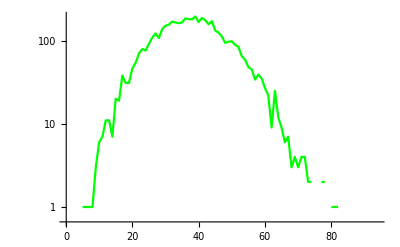

```mathematica
histoCCbP=BinCounts[CCbPmatisto,{grid}];
CCbPisto=ListLogPlot[histoCCbP,Joined->True,PlotStyle->Green,PlotRange->All]
```

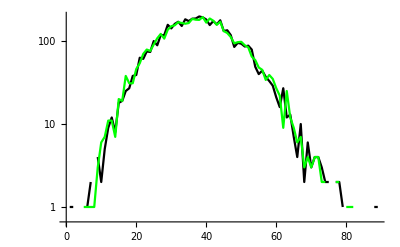

```mathematica
Show[CCisto,CCbPisto]
```

-Graphics-

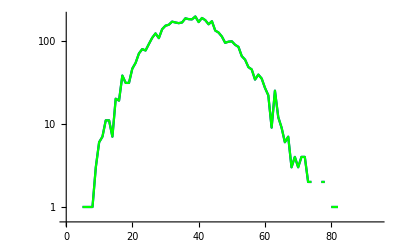

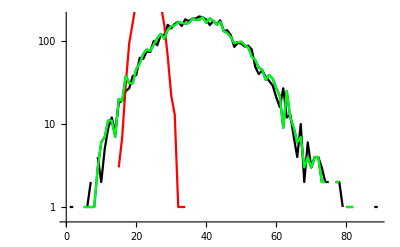

```mathematica
Show[CCisto,CCbPisto]
Show[CCbRisto,CCbPisto]
Show[CCisto,CCbisto,CCbRisto,CCbPisto]
```

```mathematica
CCbRisto
CCbPisto
```

-Graphics-

-Graphics-

```mathematica
Flatten[Table[Table[{st1,st2,CC[st1,st2],
                                              " ",CCbootstrapP[st1,st2],CCbootstrapPsd[st1,st2],
                                              " ",Abs[CC[st1,st2]-CCbootstrapP[st1,st2]]-CCbootstrapPsd[st1,st2]},{st2,st1+1,5}],{st1,1,5}],1]//TableForm
```

1 | 2 | 0.0166255 |   | 0.018878 | 0.013931 |   | -0.0116785
1 | 3 | 0.00779223 |   | 0.00702772 | 0.0133256 |   | -0.012561
1 | 4 | 0.0645654 |   | 0.0632554 | 0.0170487 |   | -0.0157388
1 | 5 | 0.0544416 |   | 0.0466299 | 0.0193387 |   | -0.0115269
2 | 3 | 0.00990031 |   | -0.00123024 | 0.00957375 |   | 0.00155679
2 | 4 | 0.0504668 |   | 0.059115 | 0.0156314 |   | -0.00698309
2 | 5 | 0.0522502 |   | 0.0537934 | 0.0127226 |   | -0.0111794
3 | 4 | 0.0225172 |   | 0.020782 | 0.0199299 |   | -0.0181947
3 | 5 | 0.0271549 |   | 0.0280532 | 0.01447 |   | -0.0135717
4 | 5 | 0.0530319 |   | 0.0623231 | 0.0119903 |   | -0.00269903

```mathematica
Flatten[Table[Table[{st1,st2,CC[st1,st2],
                                              " ",CCbootstrap[st1,st2],CCbootstrapsd[st1,st2], 
                                              " ",Abs[CC[st1,st2]-CCbootstrap[st1,st2]]-CCbootstrapsd[st1,st2],
                                              " ",CCbootstrapR[st1,st2],CCbootstrapRsd[st1,st2],
                                              " ",Abs[CC[st1,st2]-CCbootstrapR[st1,st2]]-CCbootstrapRsd[st1,st2],
                                              " ",CCbootstrapP[st1,st2],CCbootstrapPsd[st1,st2],
                                              " ",Abs[CC[st1,st2]-CCbootstrapP[st1,st2]]-CCbootstrapPsd[st1,st2]},{st2,st1+1,5}],{st1,1,5}],1]//TableForm
```

1 | 2 | 0.0166255 |   | -0.00832836 | 0.00836724 |   | 0.0165866 |   | 0.00303763 | 0.00954153 |   | 0.00404634 |   | 0.018878 | 0.013931 |   | -0.0116785
1 | 3 | 0.00779223 |   | 0.00421482 | 0.00991696 |   | -0.00633955 |   | -0.000210234 | 0.0111092 |   | -0.00310669 |   | 0.00702772 | 0.0133256 |   | -0.012561
1 | 4 | 0.0645654 |   | 0.00140933 | 0.00776842 |   | 0.0553876 |   | 0.00199604 | 0.0161422 |   | 0.0464272 |   | 0.0632554 | 0.0170487 |   | -0.0157388
1 | 5 | 0.0544416 |   | 0.00583866 | 0.00883094 |   | 0.039772 |   | -0.00273911 | 0.0150892 |   | 0.0420915 |   | 0.0466299 | 0.0193387 |   | -0.0115269
2 | 3 | 0.00990031 |   | -0.000885841 | 0.0140521 |   | -0.00326599 |   | -0.000806801 | 0.0182009 |   | -0.00749379 |   | -0.00123024 | 0.00957375 |   | 0.00155679
2 | 4 | 0.0504668 |   | -0.0014914 | 0.0134442 |   | 0.038514 |   | 0.00209322 | 0.00944083 |   | 0.0389327 |   | 0.059115 | 0.0156314 |   | -0.00698309
2 | 5 | 0.0522502 |   | -0.0013066 | 0.0183867 |   | 0.0351701 |   | 0.00512037 | 0.0140277 |   | 0.0331021 |   | 0.0537934 | 0.0127226 |   | -0.0111794
3 | 4 | 0.0225172 |   | -0.00346617 | 0.0212078 |   | 0.00477553 |   | 0.0010894 | 0.00988326 |   | 0.0115445 |   | 0.020782 | 0.0199299 |   | -0.0181947
3 | 5 | 0.0271549 |   | 0.00519931 | 0.0125456 |   | 0.00941003 |   | 0.00326028 | 0.0202282 |   | 0.00366643 |   | 0.0280532 | 0.01447 |   | -0.0135717
4 | 5 | 0.0530319 |   | -0.00862207 | 0.0143398 |   | 0.0473142 |   | -0.00462624 | 0.0126673 |   | 0.0449909 |   | 0.0623231 | 0.0119903 |   | -0.00269903

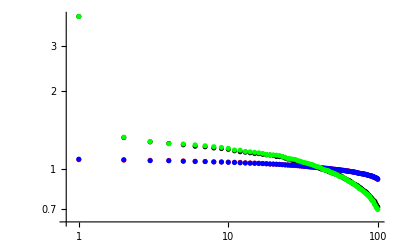

```mathematica
Show[ListLogLogPlot[Eigenvalues[CCmat],PlotStyle->Black],
         ListLogLogPlot[Eigenvalues[CCbmat],PlotStyle->Red],
         ListLogLogPlot[Eigenvalues[CCbRmat],PlotStyle->Blue],
         ListLogLogPlot[Eigenvalues[CCbPmat],PlotStyle->Green]]
```

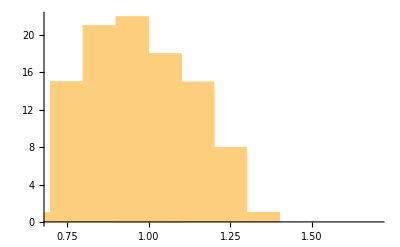

```mathematica
Show[Histogram[Eigenvalues[CCmat]],
         Histogram[Eigenvalues[CCbmat]],
         Histogram[Eigenvalues[CCbRmat]],
         Histogram[Eigenvalues[CCbPmat]]]
```